```mathematica
<<FunctionApproximations`
```

```mathematica
Precision0 = 32;
Precision1=16;
Precisionx=22;
```

```mathematica
(* Functions *)
```

```mathematica
Off[Fit::fitm];
```

```mathematica
Pos[x_]=x(1+Sign[x])/2;
PosQ[x_]=(1+Sign[x])/2;
```

```mathematica
(* returns random sublist length lsub from Range[{1,llist}] *)
RandIntSubset[llist_Integer,lsub_Integer]:=Block[{ilist,iloc,inum,isubset},
ilist=Range[1,llist];
iloc=RandomInteger[{1,Length[ilist]}];
inum=ilist[[iloc]];
isubset={inum};
ilist=Complement[ilist,{inum}];
For[i1=1,i1≤lsub-1,i1++,
iloc=RandomInteger[{1,Length[ilist]}];
inum=ilist[[iloc]];
isubset=Append[isubset,inum];
ilist=Complement[ilist,{inum}];
];
Return[isubset];
];
```

```mathematica
(* forward biased diff. quot: produces accumulated errors for last elements *)
difquot0[func_List,hs_]:=Block[{i1,leng,difq},
leng=Length[func];
difq=Table[0.,{i1,1,leng}];
For[i1=1,i1<leng,i1++,
difq[[i1]] = (func[[i1+1]]-func[[i1]])/hs;
];
difq[[leng]] = difq[[leng-1]];
Return[difq];
];
```

```mathematica
(* symmetric diff. quotient on a list, leng should be odd *)
difquot[func_List,hs_]:=Block[{i1,leng,difq,center},
leng=Length[func];
difq=Table[0.,{i1,1,leng}];
center = Ceiling[leng/2];
For[i1=1,i1<=center-1,i1++,
difq[[i1]] = (func[[i1+1]]-func[[i1]])/hs;
];
For[i1=center+1,i1≤ leng,i1++,
difq[[i1]] = (func[[i1]]-func[[i1-1]])/hs;
];
difq[[center]]= (func[[center+1]]-func[[center-1]])/(2*hs);
Return[difq];
];
```

```mathematica
(* polynome func-approximation of a list with a x-range *)
listfunc[func_List,x1_,x2_,deg_Integer,y_Symbol]:=Block[{i1,leng,dx,flist,expfit,varlist,symb,repfuncfit,funcfit},
leng=Length[func];
dx = (x2-x1)/(leng-1);
(*flist = Table[{x1+dx*(i1-1),func[[i1]]},{i1,1,leng}];*)
flist={};
For[i1=1,i1≤leng,i1++,
If[func[[i1]] ≠ Infinity,
flist=Append[flist,{x1+dx*(i1-1),func[[i1]]}];
];
];
expfit=a0;
varlist={a0};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb* y^(i1);
varlist = Append[varlist, symb];
];
repfuncfit= FindFit[flist,expfit,varlist,y];
funcfit = expfit /. repfuncfit;
Return[funcfit];
];
```

```mathematica
(* polynome interpolation of a list with a x-range *)
listinter[func_List,x1_,x2_,y_Symbol]:=Block[{i1,leng,dx,flist,funcfit},
leng=Length[func];
dx = (x2-x1)/(leng-1);
flist = Table[{x1+dx*(i1-1),func[[i1]]},{i1,1,leng}];
funcfit[y]= InterpolatingPolynomial[flist,y];
Return[funcfit[y]];
];
```

```mathematica
(* polynome interpolation of a list with a x-range, with derivative1,2 at border *)
listinter1[func_List, x1_, x2_, y_Symbol] := Block[{i1, leng, dx, flist, funcfit, funcfit1, padd, padd1, eq1, eq2,eq3,eq4, soleq},
   leng = Length[func];
   dx = (x2 - x1)/(leng - 1);
   flist = Table[{x1 + dx*(i1 - 1), func[[i1]]}, {i1, 1, leng}];
   funcfit[y] = InterpolatingPolynomial[flist, y];
   padd[y] = 1;
   For[i1 = 1, i1 <= leng, i1++,
    padd[y] = padd[y]*(y - (x1 + dx*(i1 - 1)));
    ];
   padd1[y] = padd[y]*(c1 + c2*y+c3*y^2+c4*y^3) + funcfit[y];
   eq1 = ((D[padd1[y], y] /. y -> x1) == (func[[2]] - func[[1]])/dx);
   eq2 = ((D[padd1[y], y] /. y -> x2) == (func[[leng]] - func[[leng - 1]])/dx);eq3 = ((D[padd1[y], {y,2}] /. y -> x1) == (func[[3]] - 2func[[2]]+func[[1]])/dx^2);
eq4 = ((D[padd1[y], {y,2}] /. y -> x2) == (func[[leng]] - 2func[[leng-1]]+func[[leng-2]])/dx^2);
   soleq = Solve[{eq1, eq2,eq3,eq4}, {c1, c2,c3,c4}];
   funcfit1[y] = (padd1[y] /. soleq[[1]]);
   Return[funcfit1[y]];
   ];
```

```mathematica
(* MovingMedian:result list: shorter neigh-1, same length with MovingMedianE *)
MovingMedianE[list_List,neigh_Integer]:= Block[{i1,list1,leng,current1,current2,listloc,neigh2},
leng=Length[list];
neigh2=Floor[neigh/2];
list1=list;
For[i1=1,i1≤leng,i1++,
current1=list[[i1]];
If[i1≤ neigh2,
listloc=list[[Range[1,i1+neigh2]]];
current2= Median[listloc];
list1[[i1]]= current2;
Continue[];
];
If[i1≥ leng- neigh2,
listloc=list[[Range[i1-neigh2,leng]]];
current2= Median[listloc];
list1[[i1]]= current2;
Continue[];
];
listloc=list[[Range[i1-neigh2,i1+neigh2]]];
current2= Median[listloc];
list1[[i1]]= current2;
];


Return[list1];
];
```

```mathematica
(* MovingAverage:result list: shorter neigh-1, same length with MovingAverageE *)
MovingAverageE[list_List,neigh_Integer]:= Block[{i1,list1,leng,current1,current2,listloc,neigh2},
leng=Length[list];
neigh2=Floor[neigh/2];
list1=list;
For[i1=1,i1≤leng,i1++,
current1=list[[i1]];
If[i1≤ neigh2,
listloc=list[[Range[1,i1+neigh2]]];
current2= Mean[listloc];
list1[[i1]]= current2;
Continue[];
];
If[i1≥ leng- neigh2,
listloc=list[[Range[i1-neigh2,leng]]];
current2= Mean[listloc];
list1[[i1]]= current2;
Continue[];
];
listloc=list[[Range[i1-neigh2,i1+neigh2]]];
current2= Mean[listloc];
list1[[i1]]= current2;
];


Return[list1];
];
```

```mathematica
(* runaway-elimination by median filter, thresh: relative deiation threshold *)
ausreisMed[func_List,thresh_Real,neihbours_Integer,eps_Real]:=Block[{i1,leng,maxabs,current1,current2,list1,list2},
leng=Length[func];
list1=func;
If[leng<neihbours,
Return[list1];
];
list2 = MovingMedianE[func, neihbours];
maxabs= Max[Abs[list2]];
If[maxabs<eps,
Return[list1];
];
(* ausreisser *)
For[i1=1,i1<=leng,i1++,
current1= list1[[i1]];
current2= list2[[i1]];

If[Abs[current2]> eps*maxabs,
If[Abs[current1-current2]/Abs[current2]>thresh,
list1[[i1]]=current2;
];
,
If[Abs[current1-current2]/maxabs>thresh,
list1[[i1]]=current2;
];
];

];

Return[list1];
];
```

```mathematica
(* runaway-elimination by mean filter, thresh: relative deiation threshold *)
ausreis[func_List,thresh_]:=Block[{i1,leng,difq,mean,neighbour1,neighbour2,current},
leng=Length[func];
difq=Table[0.,{i1,1,leng}];
For[i1=1,i1<=leng,i1++,
current= func[[i1]];
If[i1==leng,
neighbour1= func[[i1-2]];
neighbour2= func[[i1-1]];
];
If[i1==1,
neighbour1= func[[i1+1]];
neighbour2= func[[i1+2]];
];
If[i1>1 && i1<leng,
neighbour1= func[[i1-1]];
neighbour2= func[[i1+1]];
];
mean= (neighbour1+neighbour2)/2;
If[Abs[mean]>0,
If[Abs[current-mean]/(Abs[mean])> thresh,
difq[[i1]] = mean;
,
difq[[i1]] = current;
];
,
If[(Mean[Abs[func]])== 0.,
Return[func];
];
If[Abs[current-mean]/(Mean[Abs[func]])> thresh,
difq[[i1]] = mean;
,
difq[[i1]] = current;
];
];

];
Return[difq];
];
```

```mathematica
MovingMedianC[list_List,neigh_Integer]:= Block[{neigh1,neigh2,i1,list1,retlist},
neigh1=Floor[neigh/2];
If[neigh1== neigh/2,
neigh2=Floor[neigh/2];
,
neigh2=Floor[neigh/2];
];

list1= Join[Table[list[[1]],{i1,1,neigh1}],list];
list1= Join[list1,Table[Last[list],{i1,1,neigh2}]];
retlist=MovingMedian[Re[list1],neigh]+I*MovingMedian[Im[list1],neigh];
Return[retlist];
];
```

```mathematica
MovingAverageC[list_List,neigh_Integer]:= Block[{neigh1,neigh2,i1,list1,retlist},
neigh1=Floor[neigh/2];
If[neigh1== neigh/2,
neigh2=Floor[neigh/2];
,
neigh2=Floor[neigh/2];
];

list1= Join[Table[list[[1]],{i1,1,neigh1}],list];
list1= Join[list1,Table[Last[list],{i1,1,neigh2}]];
retlist=MovingAverage[list1,neigh];
Return[retlist];
];
```

```mathematica
SavitzkyGol22[list_List]:= Block[{alpha,lalpha,dist,list1,retlist,i1,i2,val},
alpha={-0.086,0.343,0.486,0.343,-0.086};
lalpha=Length[alpha];
dist=Floor[lalpha/2];
list1= Join[Table[list[[1]],{i1,1,2}],list];
list1= Join[list1,Table[Last[list1],{i1,1,2}]];
leng=Length[list];
retlist=Table[0.,{i1,1,leng}];
For[i1=3,i1≤leng+2,i1++,
val=0;
For[i2=1,i2≤lalpha,i2++,
val=val+alpha[[i2]]*list1[[i1-dist+i2-1]];
];
retlist[[i1-2]] = val;
];

Return[retlist];
];
```

```mathematica
(* polynome-trigonom approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
FarrayTfunc[flist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,omy,ymax,ymin,tflist},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
omy = Pi/(ymax-ymin);


expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy]^(i1)*x^(i2);
varlist = Append[varlist, symb];
If[i1>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy]*Cos[y*omy]^(i1-1)*x^(i2);
varlist = Append[varlist, symb];
];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* polynome-polynome approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
Farrayfunc[flist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit},

expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* y^(i1)*x^(i2);
varlist = Append[varlist, symb];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* polynome-Fourier  approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
FarrayFfunc[flist_List,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,ymax,ymin,tflist},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
(*omy = Pi/(ymax-ymin);*)


expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy*i1]*x^(i2);
varlist = Append[varlist, symb];
If[i1>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy*i1]*x^(i2);
varlist = Append[varlist, symb];
];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* list deviation 2-norm for vallists  *)
```

```mathematica
list2norm[func_List,x1_,x2_,functio_Symbol]:=Block[{i1,dx,result,leng},
leng=Length[func];
dx = (x2-x1)/(leng-1);

result=0.;
For[i1=1,i1≤leng,i1++,
result = result+  (func[[i1]]- functio[x1+dx*(i1-1)])^2;
];

result = Sqrt[result];

Return[result];

];
```

```mathematica
listmaxnorm[func_List,x1_,x2_,functio_Symbol]:=Block[{i1,dx,result,leng,val},

leng=Length[func];
dx = (x2-x1)/(leng-1);

result={0.,x1};
For[i1=1,i1≤leng,i1++,
val= Abs[(func[[i1]]- functio[x1+dx*(i1-1)])];
If[result[[1]]< val,
result = {val,x1+dx*(i1-1)};
];
];

Return[result];

];
```

```mathematica
(* list deviation 2-norm for 2-lists  *)
```

```mathematica
array2norm[func_List,x1_,x2_,n1_Integer,y1_,y2_,n2_Integer,functio_Symbol]:=Block[{i1,i2,i3,dx,dy,ct,result},
dx = (x2-x1)/(n1-1);
dy= (y2-y1)/(n2-1);
flist={};
ct=0;
result=0.;
For[i2=1,i2≤n2,i2++,
For[i1=1,i1≤n1,i1++,
ct++;
result = result+  (func[[ct]]- functio[y1+(i2-1)*dy,x1+dx*(i1-1)])^2;
];
];
result = Sqrt[result];
Return[result];

];
```

```mathematica
(* list deviation 2-norm for 2-lists for coord-func-lists *)
Farray2norm[func_List,functio_Symbol]:=Block[{ct,result,dim},

ct=0;
result=0.;
dim = Length[func];

For[ct=1,ct≤Length[func],ct++,
result = result+  (func[[ct,3]]- functio[func[[ct,1]],func[[ct,2]]])^2;
];

result = Sqrt[result];
Return[result];

];
```

```mathematica
Farraymaxnorm[func_List,functio_Symbol]:=Block[{ct,result,val},

ct=1;
result={0.,func[[ct,1]],func[[ct,2]]};

For[ct=1,ct≤Length[func],ct++,
val  =  Abs[(func[[ct,3]]- functio[func[[ct,1]],func[[ct,2]]])];
If[ result[[1]]< val,
result = {val,func[[ct,1]],func[[ct,2]]};
];
];

Return[result];

];
```

```mathematica
solCheb[n_Integer,vaist_List,x1_Real]:=Block[{expr,i1,parlist,retpol,replist,x},
expr = 0;
For[i1=1,i1≤n,i1++,
expr=expr+Symbol["c"<>ToString[i1]]*ChebyshevT[i1,x];
];
parlist = {};
For[i1=1,i1≤n,i1++,
parlist=Append[parlist,Symbol["c"<>ToString[i1]]];
];
replist= FindFit[vaist, expr, parlist, x];
retpol=expr /. replist /. x-> x1;
Return[retpol];
];
```

```mathematica
(* MovingMedian:result list: shorter neigh-1, same length with MovingMedianE, filtering only if intervalspan ≥ span *)
MovingMedianE[list_List,neigh_Integer,span_Real]:= Block[{i1,list1,leng,current1,current2,listloc,neigh2,locspan},
leng=Length[list];
neigh2=Floor[neigh/2];
list1=list;
For[i1=1,i1≤leng,i1++,
current1=list[[i1]];
If[i1≤ neigh2,
listloc=list[[Range[1,i1+neigh2]]];
locspan= Max[listloc]-Min[listloc];
If[locspan≥ span,
current2= Median[listloc];
list1[[i1]]= current2;
];
Continue[];
];
If[i1≥ leng- neigh2,
listloc=list[[Range[i1-neigh2,leng]]];
locspan= Max[listloc]-Min[listloc];
If[locspan≥ span,
current2= Median[listloc];
list1[[i1]]= current2;
];
Continue[];
];
listloc=list[[Range[i1-neigh2,i1+neigh2]]];
locspan= Max[listloc]-Min[listloc];
If[locspan≥ span,
current2= Median[listloc];
list1[[i1]]= current2;
];

];


Return[list1];
];
```

```mathematica
(* polynome-polynome approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
FarrayfuncCoef[flist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,leng,lengr,rlist,val3,flistr,flistrloc,polth,polthlist,flistth,polthser,coeff,coeffloc,polcoeff,polcoeffloc},

leng = Length[flist];
rlist={flist[[1,1]]};
For[i1=1,i1≤leng,i1++,
val3= flist[[i1]];
lengr=Length[rlist];
For[i2=1,i2≤lengr,i2++,
If[val3[[1]]== rlist[[i2]],
Break[];
];
];
If[i2==lengr+1,
rlist=Append[rlist,val3[[1]]];
];
];

lengr=Length[rlist];
flistr={};
For[i1=1,i1≤lengr,i1++,
flistrloc={};
For[i2=1,i2≤leng,i2++,
val3= flist[[i2]];
If[val3[[1]]==rlist[[i1]],
flistrloc=Append[flistrloc,{val3[[2]],val3[[3]]}];
];
];
flistr=Append[flistr,flistrloc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg2,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*y^(i1);
varlist = Append[varlist, symb];
];

polthlist={};
For[i1=1,i1≤lengr,i1++,
flistth= flistr[[i1]];
repfuncfit= FindFit[flistth,expfit,varlist,{y},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polth = expfit /. repfuncfit;
polthlist=Append[polthlist,polth];
];

polthser=Series[polthlist,{y,0,deg2}];

coeff={};
For[i1=0,i1≤deg2,i1++,
coeffloc={};
For[i2=1,i2≤lengr,i2++,
coeffloc=Append[coeffloc,{rlist[[i2]],SeriesCoefficient[polthser[[i2]],i1]}];
];
coeff=Append[coeff,coeffloc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*x^(i1);
varlist = Append[varlist, symb];
];

polcoeff={};
For[i1=0,i1≤deg2,i1++,
repfuncfit= FindFit[coeff[[i1+1]],expfit,varlist,{x},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polcoeffloc = expfit /. repfuncfit; 
polcoeff=Append[polcoeff,polcoeffloc];
];

funcfit=0;
For[i1=0,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+1]]*y^(i1);
];

Return[funcfit];
];
```

```mathematica
(* polynome-trig. approx. for a 2-array on a coordinate-function-list *)
FarrayTfuncCoef[flist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,leng,lengr,val3,flistr,flistrloc,polth,lengc,polthlist,flistth,polthser,polthser1,rlist,coeff,coeffloc,coeff1,coeff1loc,polcoeff,polcoeffloc,coeflist,coeflistloc,coeflistloc1,val,tflist,ymax,ymin,omy},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
omy = Pi/(ymax-ymin);

leng = Length[flist];
rlist={flist[[1,1]]};
For[i1=1,i1≤leng,i1++,
val3= flist[[i1]];
lengr=Length[rlist];
For[i2=1,i2≤lengr,i2++,
If[val3[[1]]== rlist[[i2]],
Break[];
];
];
If[i2==lengr+1,
rlist=Append[rlist,val3[[1]]];
];
];

lengr=Length[rlist];
flistr={};
For[i1=1,i1≤lengr,i1++,
flistrloc={};
For[i2=1,i2≤leng,i2++,
val3= flist[[i2]];
If[val3[[1]]==rlist[[i1]],
flistrloc=Append[flistrloc,{val3[[2]],val3[[3]]}];
];
];
flistr=Append[flistr,flistrloc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg2,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Cos[y*omy]^(i1);
varlist = Append[varlist, symb];
];
For[i1=1,i1≤deg2,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Sin[y*omy]*Cos[y*omy]^(i1-1);
varlist = Append[varlist, symb];
];

polthlist={};
For[i1=1,i1≤lengr,i1++,
flistth= flistr[[i1]];
repfuncfit= FindFit[flistth,expfit,varlist,{y},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polth = expfit /. repfuncfit;
polthlist=Append[polthlist,polth];
];

polthser = Series[polthlist /. Sin[y*omy]->0, {Cos[y*omy], 0, deg2}];
polthser1 = Series[(polthlist /. Sin[y*omy]->1)- (polthlist /. Sin[y*omy]->0), {Cos[y*omy], 0, deg2-1}];

coeflist={};
For[i1=1,i1≤lengr,i1++,
coeflistloc= CoefficientList[polthser[[i1]],Cos[y*omy]] ;
If[Length[coeflistloc]<deg2+1,
coeflistloc = Join[coeflistloc,Table[0,{i3,1,deg2+1-Length[coeflistloc]}]];
];
coeflistloc1= CoefficientList[polthser1[[i1]],Cos[y*omy]] ;
If[Length[coeflistloc1]<deg2,
coeflistloc1 = Join[coeflistloc1,Table[0,{i3,1,deg2-Length[coeflistloc1]}]];
];
coeflist=Append[coeflist,coeflistloc];
];

coeff=Transpose[coeflist];

lengc=1+deg2+deg2;
coeff1={};
For[i1=1,i1≤lengc,i1++,
coeff1loc={};
For[i2=1,i2≤lengr,i2++,
coeff1loc = Append[coeff1loc,{rlist[[i2]],coeff[[i1,i2]]}];
];
coeff1=Append[coeff1,coeff1loc];
];

expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*x^(i1);
varlist = Append[varlist, symb];
];

polcoeff={};
For[i1=1,i1≤lengc,i1++,
repfuncfit= FindFit[coeff[[i1]],expfit,varlist,{x},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polcoeffloc = expfit /. repfuncfit; 
polcoeff=Append[polcoeff,polcoeffloc];
];

funcfit=0;
For[i1=0,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+1]]*Cos[y*omy]^(i1);
];
For[i1=0,i1≤deg2-1,i1++,
funcfit=funcfit+polcoeff[[i1+deg2+2]]*Sin[y*omy]*Cos[y*omy]^(i1);
];

Return[funcfit];
];
```

```mathematica
(* polynome-Fourier approx. for a 2-array on a coordinate-function-list *)
FarrayFfuncCoef[flist_List,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,leng,lengr,val3,flistr,flistrloc,polth,lengc,polthlist,flistth,polthser,polthser1,rlist,coeff,coeffloc,coeff1,coeff1loc,polcoeff,polcoeffloc,coeflist,coeflistloc,coeflistloc1,val,tflist,ymax,ymin,replistfull},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
(*omy = Pi/(ymax-ymin);*)

leng = Length[flist];
rlist={flist[[1,1]]};
For[i1=1,i1≤leng,i1++,
val3= flist[[i1]];
lengr=Length[rlist];
For[i2=1,i2≤lengr,i2++,
If[val3[[1]]== rlist[[i2]],
Break[];
];
];
If[i2==lengr+1,
rlist=Append[rlist,val3[[1]]];
];
];

lengr=Length[rlist];
flistr={};
For[i1=1,i1≤lengr,i1++,
flistrloc={};
For[i2=1,i2≤leng,i2++,
val3= flist[[i2]];
If[val3[[1]]==rlist[[i1]],
flistrloc=Append[flistrloc,{val3[[2]],val3[[3]]}];
];
];
flistr=Append[flistr,flistrloc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg2,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Cos[y*omy*i1];
varlist = Append[varlist, symb];
];
For[i1=1,i1≤deg2,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Sin[y*omy*i1];
varlist = Append[varlist, symb];
];

polthlist={};
For[i1=1,i1≤lengr,i1++,
flistth= flistr[[i1]];
repfuncfit= FindFit[flistth,expfit,varlist,{y},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polth = expfit /. repfuncfit;
polthlist=Append[polthlist,polth];
];

replistfull={};
For[i1=1,i1≤deg2,i1++,
replistfull= Append[replistfull,Cos[y*omy*i1] -> 0];
];
For[i1=1,i1≤deg2,i1++,
replistfull= Append[replistfull,Sin[y*omy*i1] -> 0];
];
coeflist={};
For[i1=1,i1≤lengr,i1++,
coeflistloc = {};
For[i2=0,i2≤deg2,i2++,
If[i2==0,
val= polthlist[[i1]]  /. replistfull;
,
val= polthlist[[i1]]  /. Drop[replistfull,{i2,i2}] /. Cos[y*omy*i2] -> 1;
];
coeflistloc=Append[coeflistloc,val];
];
For[i2=1,i2≤deg2,i2++,
val= polthlist[[i1]]  /. Drop[replistfull,{i2+deg2,i2+deg2}] /. Sin[y*omy*i2] -> 1;
coeflistloc=Append[coeflistloc,val];
];
coeflist=Append[coeflist,coeflistloc];
];

coeff=Transpose[coeflist];

lengc=1+deg2+deg2;
coeff1={};
For[i1=1,i1≤lengc,i1++,
coeff1loc={};
For[i2=1,i2≤lengr,i2++,
coeff1loc = Append[coeff1loc,{rlist[[i2]],coeff[[i1,i2]]}];
];
coeff1=Append[coeff1,coeff1loc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*x^(i1);
varlist = Append[varlist, symb];
];

polcoeff={};
For[i1=1,i1≤lengc,i1++,
repfuncfit= FindFit[coeff1[[i1]],expfit,varlist,{x},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polcoeffloc = expfit /. repfuncfit; 
polcoeff=Append[polcoeff,polcoeffloc];
];

funcfit=0;
For[i1=0,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+1]]*Cos[y*omy*i1];
];
For[i1=1,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+deg2+1]]*Sin[y*omy*i1];
];

Return[funcfit];
];
```

```mathematica
(* polynome approx. in x (degree deg1) for y-coeff (degree deg2) of a trig-polynome-list in y *)
FarrayTCoef[polthlist_List,rlist_List,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,leng,lengr,val3,flistr,flistrloc,polth,lengc,flistth,polthser,polthser1,coeff,coeffloc,coeff1,coeff1loc,polcoeff,polcoeffloc,coeflist,coeflistloc,coeflistloc1,val,tflist,ymax,ymin},

lengr= Length[rlist];


polthser = Series[polthlist /. Sin[y*omy]->0, {Cos[y*omy], 0, deg2}];
polthser1 = Series[(polthlist /. Sin[y*omy]->1)- (polthlist /. Sin[y*omy]->0), {Cos[y*omy], 0, deg2-1}];

coeflist={};
For[i1=1,i1≤lengr,i1++,
coeflistloc= CoefficientList[polthser[[i1]],Cos[y*omy]] ;
If[Length[coeflistloc]<deg2+1,
coeflistloc = Join[coeflistloc,Table[0,{i3,1,deg2+1-Length[coeflistloc]}]];
];
coeflistloc1= CoefficientList[polthser1[[i1]],Cos[y*omy]] ;
If[Length[coeflistloc1]<deg2,
coeflistloc1 = Join[coeflistloc1,Table[0,{i3,1,deg2-Length[coeflistloc1]}]];
];
coeflistloc=Join[coeflistloc,coeflistloc1];
For[i2=1,i2≤Length[coeflistloc],i2++,
val= coeflistloc[[i2]];
coeflistloc[[i2]]= {rlist[[i1]],val};
];
coeflist=Append[coeflist,coeflistloc];
];

coeff=Transpose[coeflist];

lengc=1+deg2+deg2;
coeff1={};
For[i1=1,i1≤lengc,i1++,
coeff1loc={};
For[i2=1,i2≤lengr,i2++,
coeff1loc = Append[coeff1loc,{rlist[[i2]],coeff[[i1,i2]]}];
];
coeff1=Append[coeff1,coeff1loc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*x^(i1);
varlist = Append[varlist, symb];
];

polcoeff={};
For[i1=1,i1≤lengc,i1++,
repfuncfit= FindFit[coeff[[i1]],expfit,varlist,{x},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polcoeffloc = expfit /. repfuncfit; 
polcoeff=Append[polcoeff,polcoeffloc];
];

funcfit=0;
For[i1=0,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+1]]*Cos[y*omy]^(i1);
];
For[i1=0,i1≤deg2-1,i1++,
funcfit=funcfit+polcoeff[[i1+deg2+2]]*Sin[y*omy]*Cos[y*omy]^(i1);
];

Return[funcfit];
];
```

```mathematica
(* polynome approx. in x (degree deg1) for y-coeff (degree deg2) of a Fourier-list in y *)
FarrayFCoef[polthlist_List,rlist_List,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,leng,lengr,val3,flistr,flistrloc,polth,lengc,flistth,polthser,polthser1,coeff,coeffloc,coeff1,coeff1loc,polcoeff,polcoeffloc,coeflist,coeflistloc,coeflistloc1,val,val0,tflist,ymax,ymin,replistfull},

lengr= Length[rlist];


replistfull={};
For[i1=1,i1≤deg2,i1++,
replistfull= Append[replistfull,Cos[y*omy*i1] -> 0];
];
For[i1=1,i1≤deg2,i1++,
replistfull= Append[replistfull,Sin[y*omy*i1] -> 0];
];


coeflist={};
For[i1=1,i1≤lengr,i1++,
coeflistloc = {};

val0 =  polthlist[[i1]]  /. replistfull;
For[i2=0,i2≤deg2,i2++,
If[i2==0,
val= val0;
,
val= ((polthlist[[i1]]  /. Drop[replistfull,{i2,i2}]) /. Cos[y*omy*i2] -> 1) - val0;
];
coeflistloc=Append[coeflistloc,val];
];
For[i2=1,i2≤deg2,i2++,
val= ((polthlist[[i1]]  /. Drop[replistfull,{i2+deg2,i2+deg2}]) /. Sin[y*omy*i2] -> 1) -val0;
coeflistloc=Append[coeflistloc,val];
];
coeflist=Append[coeflist,coeflistloc];
];
coeff=Transpose[coeflist];

lengc=1+deg2+deg2;
coeff1={};
For[i1=1,i1≤lengc,i1++,
coeff1loc={};
For[i2=1,i2≤lengr,i2++,
coeff1loc = Append[coeff1loc,{rlist[[i2]],coeff[[i1,i2]]}];
];
coeff1=Append[coeff1,coeff1loc];
];

expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*x^(i1);
varlist = Append[varlist, symb];
];

polcoeff={};
For[i1=1,i1≤lengc,i1++,
repfuncfit= FindFit[coeff1[[i1]],expfit,varlist,{x},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polcoeffloc = expfit /. repfuncfit; 
polcoeff=Append[polcoeff,polcoeffloc];
];

funcfit=0;
For[i1=0,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+1]]*Cos[y*omy*i1];
];
For[i1=1,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+deg2+1]]*Sin[y*omy*i1];
];

Return[funcfit];
];
```

```mathematica
(* polynome approx. in x (degree deg1) for y-coeff (degree deg2) of a polynome-list in y *)
```

```mathematica
FarrayCoef[polthlist_List,rlist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,leng,lengr,val3,flistr,flistrloc,polth,lengc,flistth,polthser,polthser1,coeff,coeffloc,coeff1,coeff1loc,polcoeff,polcoeffloc,coeflist,coeflistloc,coeflistloc1,val,tflist,ymax,ymin,omy},

lengr= Length[rlist];


polthser = Series[polthlist , {y, 0, deg2}];

coeflist={};
For[i1=1,i1≤lengr,i1++,
coeflistloc= CoefficientList[polthser[[i1]],y] ;
If[Length[coeflistloc]<deg2+1,
coeflistloc = Join[coeflistloc,Table[0,{i3,1,deg2+1-Length[coeflistloc]}]];
];
For[i2=1,i2≤Length[coeflistloc],i2++,
val= coeflistloc[[i2]];
coeflistloc[[i2]]= {rlist[[i1]],val};
];
coeflist=Append[coeflist,coeflistloc];
];

coeff=Transpose[coeflist];

lengc=1+deg2;
coeff1={};
For[i1=1,i1≤lengc,i1++,
coeff1loc={};
For[i1=2,i2≤lengr,i2++,
coeff1loc = Append[coeff1loc,{rlist[[i2]],coeff[[i1,i2]]}];
];
coeff1=Append[coeff1,coeff1loc];
];
expfit=0;
varlist={};
ct=-1;
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*x^(i1);
varlist = Append[varlist, symb];
];

polcoeff={};
For[i1=1,i1≤lengc,i1++,
repfuncfit= FindFit[coeff[[i1]],expfit,varlist,{x},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
polcoeffloc = expfit /. repfuncfit; 
polcoeff=Append[polcoeff,polcoeffloc];
];

funcfit=0;
For[i1=0,i1≤deg2,i1++,
funcfit=funcfit+polcoeff[[i1+1]]*y^(i1);
];


Return[funcfit];
];
```

```mathematica
(* coefficient order deg of exp according to function set funclist *)
GenCoef[exp_,funclist_List,deg_Integer]:= Block[{leng,i1,replist,replistfull,retval},
leng = Length[funclist];
replist={};
replistfull={};
For[i1=1,i1≤leng,i1++,
If[i1 ≠ deg,
replist= Append[replist,funclist[[i1]] -> 0];
,
replist= Append[replist,funclist[[i1]] -> 1];
];
replistfull= Append[replistfull,funclist[[i1]] -> 0];
];
If[deg==0,
retval= exp /. replistfull;
,
retval= (exp /. replist)- (exp /. replistfull);
];

Return[retval];
];
```

```mathematica
(* precision-truncate  exp according to function set funclist *)
TruncCoef[exp_,funclist_List,prec_]:= Block[{leng,i1,replistfull,exp1,val0,val},
leng = Length[funclist];
exp1=exp;
replistfull={};
For[i1=1,i1≤leng,i1++,
replistfull= Append[replistfull,funclist[[i1]] -> 0];
];
val0= exp /. replistfull;
If[Abs[val0]≤10^(-prec),
exp1 = exp1 - val0;
];
For[i1=1,i1≤leng,i1++,
val = ((exp /. Drop[replistfull,{i1,i1}] ) /. funclist[[i1]]->1)  - val0;
If[Abs[val]≤10^(-prec),
exp1 = exp1  /. funclist[[i1]]->0;
];
];

Return[exp1];
];
```

```mathematica
RepList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,symlist[[i]] -> vallist[[i]]];
];
Return[rlist];
];
```

```mathematica
ValList[replist_List] := Block[{leng,rlist,i},
leng = Length[replist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,replist[[i]][[2]]];
];
Return[rlist];
];
```

```mathematica
SymList[replist_List] := Block[{leng,rlist,i},
leng = Length[replist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,replist[[i]][[1]]];
];
Return[rlist];
];
```

```mathematica
SymvalList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,{symlist[[i]] , vallist[[i]]}];
];
Return[rlist];
];
```

```mathematica
GenSymList[index1_Integer,index2_Integer] := Block[{rlist,i,symb},
rlist = {};
For[i=index1,i<=index2,i++,
symb = Symbol["a" <> ToString[i]];
rlist = Append[rlist,symb];
];
Return[rlist];
];
```

```mathematica
SymrangeList[symlist_List,lowlist_List,uplist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,{symlist[[i]] , lowlist[[i]], uplist[[i]]}];
];
Return[rlist];
];
```

```mathematica
ExCoefFit[expr_,fitfunclist_List] := Block[{leng,rlist,rlist1,i,j,clist,coef},
leng = Length[fitfunclist];
clist = {};
rlist1=Table[fitfunclist[[j]]->0,{j,1,leng}];
For[i=1,i<=leng,i++,
rlist=rlist1;
rlist[[i]] = fitfunclist[[i]]->1;
If[i==1,
coef = (expr /. rlist1);
,
coef = (expr /. rlist) -(expr /. rlist1);
];
clist = Append[clist,coef];
];
Return[clist];
];
```

```mathematica
(* extracts params as vallist from a xy-expression in funcsystems funclistx,funclisty  *)
ExParamFit2dsym[fitxy_,funclistx_List,funclisty_List,degx_Integer,degy_Integer,symx_Integer,symy_Integer] := Block[
{i1,i2,ct,varlist,repfunclist,symb,val,areplist,avallist,zrepfunclist,fitv0,funclistxy},

funclistxy = Flatten[Table[funclistx[[i1]]*funclisty[[i2]],{i1,1,degx},{i2,1,degy}]];
   zrepfunclist = Join[Table[(funclistx[[i1]]) -> 0,{i1,1,degx}],
Table[(funclisty[[i1]] )-> 0,{i1,1,degy}]];

varlist={};
repfunclist={};
ct=-1;
For[i2=1,i2≤degy,i2++,
For[i1=1,i1≤degx,i1++,
If[
((EvenQ[i1] && symx≥0) || (OddQ[i1] && symx ≤ 0))  &&
((EvenQ[i2] && symy≥0) || (OddQ[i2] && symy ≤ 0)) 
,
ct++;
symb = Symbol["a" <> ToString[(ct)]];

varlist = Append[varlist, symb];
repfunclist = Append[repfunclist,(funclistx[[i1]])* (funclisty[[i2]] ) -> 1];
];

];
];
fitv0=fitxy;
   areplist={};
For[i1=1,i1<=Length[repfunclist],i1++,
symb = Symbol["a" <> ToString[(i1-1)]];
If[i1 == 1,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist);
,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist) -(fitv0 /. zrepfunclist);
];
areplist = Append[areplist, symb -> val];
];
   avallist = varlist /. areplist;
Return[avallist];
];
```

```mathematica
(* extracts params as vallist from a xy-expression in funcsystems funclistx,funclisty without sym  *)
ExParamFit2d[fitxy_,funclistx_List,funclisty_List,degx_Integer,degy_Integer] := Block[
{i1,i2,ct,varlist,repfunclist,symb,val,areplist,avallist,zrepfunclist,fitv0,funclistxy},

funclistxy = Flatten[Table[funclistx[[i1]]*funclisty[[i2]],{i1,1,degx},{i2,1,degy}]];
   zrepfunclist = Join[Table[(funclistx[[i1]]) -> 0,{i1,1,degx}],
Table[(funclisty[[i1]] )-> 0,{i1,1,degy}]];

varlist={};
repfunclist={};
ct=-1;
For[i2=1,i2≤degy,i2++,
For[i1=1,i1≤degx,i1++,

ct++;
symb = Symbol["a" <> ToString[(ct)]];

varlist = Append[varlist, symb];
repfunclist = Append[repfunclist,(funclistx[[i1]])* (funclisty[[i2]] ) -> 1];


];
];
fitv0=fitxy;
   areplist={};
For[i1=1,i1<=Length[repfunclist],i1++,
symb = Symbol["a" <> ToString[(i1-1)]];
If[i1 == 1,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist);
,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist) -(fitv0 /. zrepfunclist);
];
areplist = Append[areplist, symb -> val];
];
   avallist = varlist /. areplist;
Return[avallist];
];
```

```mathematica
(* extracts params as vallist from a x-expression in funcsystem funclistx*)
ExParamFit1d[fitx_,funclistx_List,degx_] := Block[
{degy,i1,i2,ct,varlist,repfunclist,symb,val,areplist,avallist,zrepfunclist,fitv0,funclistxy},

   zrepfunclist = Table[(funclistx[[i1]]) -> 0,{i1,1,degx}];

   varlist={};
repfunclist={};
ct=-1;
For[i1=1,i1≤degx,i1++,

ct++;
symb = Symbol["a" <> ToString[(ct)]];

varlist = Append[varlist, symb];
repfunclist = Append[repfunclist,(funclistx[[i1]]) -> 1];


];
fitv0=fitx;
   areplist={};
For[i1=1,i1<=Length[repfunclist],i1++,
symb = Symbol["a" <> ToString[(i1-1)]];
If[i1 == 1,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist);
,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist) -(fitv0 /. zrepfunclist);
];
areplist = Append[areplist, symb -> val];
];
   avallist = varlist /. areplist;
Return[avallist];
];
```

```mathematica
(* Fourier-fit on a value-list for equidistant subdivision on interval x1,x2 *)
listFfunc[func_List,omx_,x1_,x2_,deg_Integer,y_Symbol]:=Block[{i1,leng,dx,flist,expfit,varlist,symb,repfuncfit,funcfit,a0},
Precision1=16;
leng=Length[func];
dx = (x2-x1)/(leng-1);
flist = Table[{x1+dx*(i1-1),func[[i1]]},{i1,1,leng}];
(*omx=2*Pi/(x2-x1);*)
expfit=a0;
varlist={a0};

For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb* Cos[y*omx*i1];
varlist = Append[varlist, symb];

symb = Symbol["b" <> ToString[(i1)]];
expfit =expfit+symb* Sin[y*omx*i1];
varlist = Append[varlist, symb];

];

repfuncfit= FindFit[flist,expfit,varlist,y,NormFunction->(Norm[#,2]&),WorkingPrecision->Precision1];
funcfit = expfit /. repfuncfit;
Return[funcfit];
];
```

```mathematica
(* Fourier-fit on a coordinate-value-list  *)
FlistFfunc[func_List,omx_,deg_Integer,y_Symbol]:=Block[{i1,leng,dx,flist,expfit,varlist,symb,repfuncfit,funcfit,a0},
Precision1=16;
leng=Length[func];
flist=func;
(*omx=2*Pi/(x2-x1);*)
expfit=a0;
varlist={a0};

For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb* Cos[y*omx*i1];
varlist = Append[varlist, symb];

symb = Symbol["b" <> ToString[(i1)]];
expfit =expfit+symb* Sin[y*omx*i1];
varlist = Append[varlist, symb];

];

repfuncfit= FindFit[flist,expfit,varlist,y,NormFunction->(Norm[#,2]&),WorkingPrecision->Precision1];
funcfit = expfit /. repfuncfit;
Return[funcfit];
];
```

```mathematica
(* polynome func-approximation of a coordinate-value list *)
PlistFfunc[func_List,deg_Integer,y_Symbol]:=Block[{i1,leng,dx,flist,expfit,varlist,symb,repfuncfit,funcfit},
leng=Length[func];
flist=func;
expfit=a0;
varlist={a0};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb* y^(i1);
varlist = Append[varlist, symb];
];
repfuncfit= FindFit[flist,expfit,varlist,y];
funcfit = expfit /. repfuncfit;
Return[funcfit];
];
```

```mathematica
(* polynome-trigonom approx. for a 2-array *)
arrayTfunc[func_List,x1_,x2_,n1_Integer,y1_,y2_,n2_Integer,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,dx,dy,ct,flist,expfit,varlist,symb,repfuncfit,funcfit,omy},
dx = (x2-x1)/(n1-1);
dy= (y2-y1)/(n2-1);
omy= Pi/(y2-y1);
flist={};
ct=0;
For[i2=1,i2≤n2,i2++,
For[i1=1,i1≤n1,i1++,
ct++;
flist =Append[flist,{y1+(i2-1)*dy,x1+dx*(i1-1),func[[ct]]}];
];
];
expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy]^(i1)*x^(i2);
varlist = Append[varlist, symb];
If[2Floor[i1/2]!=i1,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy]^(i1)*x^(i2);
varlist = Append[varlist, symb];
];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* polynome-polynome approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
Farrayfunc[flist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit},

expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* y^(i1)*x^(i2);
varlist = Append[varlist, symb];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&),WorkingPrecision->Precision1];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* polynome-trigonom  approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
FarrayTfunc[flist_List,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,omy,ymax,ymin,tflist},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
omy = Pi/(ymax-ymin);


expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy]^(i1)*x^(i2);
varlist = Append[varlist, symb];
If[i1>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy]*Cos[y*omy]^(i1-1)*x^(i2);
varlist = Append[varlist, symb];
];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* polynome-Fourier  approx. for a 2-array on a coordinate-function-list *)
FarrayFfunc[flist_List,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,ymax,ymin,tflist},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
(*omy = Pi/(ymax-ymin);*)


expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy*i1]*x^(i2);
varlist = Append[varlist, symb];
If[i1>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy*i1]*x^(i2);
varlist = Append[varlist, symb];
];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* Fourier-Fourier  approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
FarrayFFfunc[flist_List,omx_,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,ymax,ymin,tflist},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
(*omy = Pi/(ymax-ymin);*)


expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy*i1]*Cos[x*omx*i2];
varlist = Append[varlist, symb];
If[i1>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy*i1]*Cos[x*omx*i2];
varlist = Append[varlist, symb];
];
If[i2>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy*i1]*Sin[x*omx*i2];
varlist = Append[varlist, symb];
];
If[i1>0 && i2>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy*i1]*Sin[x*omx*i2];
varlist = Append[varlist, symb];
];

];
];
repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* list deviation 2-norm for vallists  *)
list2norm[func_List,x1_,x2_,functio_Symbol]:=Block[{i1,dx,result,leng},
leng=Length[func];
dx = (x2-x1)/(leng-1);

result=0.;
For[i1=1,i1≤leng,i1++,
result = result+  (func[[i1]]- functio[x1+dx*(i1-1)])^2;
];

result = Sqrt[result];

Return[result];

];
```

```mathematica
listmaxnorm[func_List,x1_,x2_,functio_Symbol]:=Block[{i1,dx,result,leng,val},

leng=Length[func];
dx = (x2-x1)/(leng-1);

result={0.,x1};
For[i1=1,i1≤leng,i1++,
val= Abs[(func[[i1]]- functio[x1+dx*(i1-1)])];
If[result[[1]]< val,
result = {val,x1+dx*(i1-1)};
];
];

Return[result];

];
```

```mathematica
(* list deviation 2-norm for valarrays  *)
array2norm[func_List,x1_,x2_,n1_Integer,y1_,y2_,n2_Integer,functio_Symbol]:=Block[{i1,i2,i3,dx,dy,ct,result},
dx = (x2-x1)/(n1-1);
dy= (y2-y1)/(n2-1);
flist={};
ct=0;
result=0.;
For[i2=1,i2≤n2,i2++,
For[i1=1,i1≤n1,i1++,
ct++;
result = result+  (func[[ct]]- functio[y1+(i2-1)*dy,x1+dx*(i1-1)])^2;
];
];
result = Sqrt[result];
Return[result];

];
```

```mathematica
(* list deviation 2-norm for 3-vallists for coord-func-lists *)
Farray2norm[func_List,functio_Symbol]:=Block[{ct,result,dim},

ct=0;
result=0.;
dim = Length[func];

For[ct=1,ct≤Length[func],ct++,
result = result+  (func[[ct,3]]- functio[func[[ct,1]],func[[ct,2]]])^2;
];

result = Sqrt[result];
Return[result];

];
```

```mathematica
Farraymaxnorm[func_List,functio_Symbol]:=Block[{ct,result,val},

ct=1;
result={0.,func[[ct,1]],func[[ct,2]]};

For[ct=1,ct≤Length[func],ct++,
val  =  Abs[(func[[ct,3]]- functio[func[[ct,1]],func[[ct,2]]])];
If[ result[[1]]< val,
result = {val,func[[ct,1]],func[[ct,2]]};
];
];

Return[result];

];
```

```mathematica
(* trigo-fit on a value-list for equidistant subdivision on interval x1,x2 *)
listTfunc[func_List,x1_,x2_,deg_Integer,y_Symbol]:=Block[{i1,leng,dx,flist,expfit,varlist,symb,repfuncfit,funcfit,omx},
leng=Length[func];
dx = (x2-x1)/(leng-1);
flist = Table[{x1+dx*(i1-1),func[[i1]]},{i1,1,leng}];

expfit=a0;
varlist={a0};
omx= Pi/(x2-x1);
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb* Cos[y*omx]^(i1);
varlist = Append[varlist, symb];
If[2Floor[i1/2]!=i1,
symb = Symbol["b" <> ToString[(i1)]];
expfit =expfit+symb* Sin[y*omx]^(i1);
varlist = Append[varlist, symb];
];
];

repfuncfit= FindFit[flist,expfit,varlist,y,NormFunction->(Norm[#,2]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];
];
```

```mathematica
RecurTab1Func2Var[equ_,v_Symbol,i_Symbol,j_Symbol,jfunc_List,var1val_List,var2val_List,h_] := 
Block[{i01,i02,j01,j02,tlist,vjlist,repij,repim1j,repijp1,repijm1,lengi,i1,j1,elem,equ1,sequ},
i01= var1val[[1]];
i02= var1val[[2]];
j01= var2val[[1]];
j02= var2val[[2]];
tlist = {};
vjlist={};
For[j1=j01,j1<=j02,j1++,
elem= jfunc[[1]] /. j-> j1;
vjlist = Append[vjlist,elem];
];
tlist = Append[tlist,vjlist];
For[i1=i01+1,i1<=i02,i1++,
lengi= Length[tlist];
vjlist={};
For[j1=j01,j1<= j02,j1++,
repij= v[i,j] -> tlist[[lengi,j1-j01+1]];
If[i1 == i01+1,
repim1j = v[i-1,j] -> (jfunc[[2]] /. j-> j1);
,
repim1j= v[i-1,j] -> tlist[[lengi-1,j1-j01+1]];
];
If[j1 == j02,
repijp1= v[i,j+1] -> Last[tlist[[lengi]]]+ (tlist[[lengi,j02-j01+1]]-tlist[[lengi,j02-j01]])/h;
,
repijp1= v[i,j+1] -> tlist[[lengi,j1+1-j01+1]];
];
If[j1== j01,
repijm1= v[i,j-1] -> First[tlist[[lengi]]]-(tlist[[lengi,2]]-tlist[[lengi,1]])/h;
,
repijm1= v[i,j-1] -> tlist[[lengi,j1-1-j01+1]];
];
equ1 = equ /. repij /. repim1j /. repijp1 /. repijm1   ;
sequ = First[NSolve[equ1,v[i+1,j]]];
elem = v[i+1,j] /. sequ;
vjlist = Append[vjlist,elem];
];
tlist = Append[tlist,vjlist];
];

Return[tlist];
];
```

```mathematica
x1=N[-Pi/2];
nlist=11;
x2= N[Pi/2];
dx= (x2-x1)/(nlist-1);
omx=Pi/(x2-x1);
ftest[th_] = Cos[th];
listtabT=Table[{x1+dx*(i1-1), ftest[x1+dx*(i1-1)]},{i1,1,nlist}]
listtabTf=N[Transpose[listtabT][[2]]]
```

{{-1.5708,6.12323×10^-17},{-1.25664,0.309017},{-0.942478,0.587785},{-0.628319,0.809017},{-0.314159,0.951057},{0.,1.},{0.314159,0.951057},{0.628319,0.809017},{0.942478,0.587785},{1.25664,0.309017},{1.5708,6.12323×10^-17}}

{6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,6.12323×10^-17}

```mathematica
flist[th_]= listFfunc[listtabTf,omx, x1, x2, 4, th]
flist[0.1]-ftest[0.1]
```

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (16).

-3.03722097653482×10^-16+1.000000000000001 Cos[1. th]-3.729325844776651×10^-16 Cos[2. th]+1.959844345200289×10^-16 Cos[3. th]-6.887224514239474×10^-17 Cos[4. th]+5.014887693359181×10^-37 Sin[1. th]-6.899773848464754×10^-37 Sin[2. th]+4.882916964586571×10^-37 Sin[3. th]-1.918794251192103×10^-37 Sin[4. th]

-1.11022×10^-16

```mathematica
RecurTabFour1Func2Var[equ_,v_Symbol,i_Symbol,j_Symbol,jfunc_List,var1val_List,var2val_List,h_,deg_Integer,omx_] := 
Block[{i01,i02,j01,j02,tlist,vjlist,repij,repim1j,repijp1,repijm1,lengi,i1,j1,elem,equ1,sequ,th,listtab,flist1},
i01= var1val[[1]];
i02= var1val[[2]];
j01= var2val[[1]];
j02= var2val[[2]];
tlist = {};
vjlist={};
For[j1=j01,j1<=j02,j1++,
elem= jfunc[[1]] /. j-> j1;
vjlist = Append[vjlist,elem];
];
tlist = Append[tlist,vjlist];

For[i1=i01+1,i1<=i02,i1++,
lengi= Length[tlist];
listtab= Last[tlist];
flist1[th_]= listFfunc[listtab,omx, j01, j02, deg, th];
vjlist={};
For[j1=j01,j1<= j02,j1++,
repij= v[i,j] -> tlist[[lengi,j1-j01+1]];
If[i1 == i01+1,
repim1j = v[i-1,j] -> (jfunc[[2]] /. j-> j1);
,
repim1j= v[i-1,j] -> tlist[[lengi-1,j1-j01+1]];
];
If[j1 == j02,
repijp1= v[i,j+1] -> flist1[j1+1];
,
repijp1= v[i,j+1] -> tlist[[lengi,j1+1-j01+1]];
];
If[j1== j01,
repijm1= v[i,j-1] -> flist1[j1-1];
,
repijm1= v[i,j-1] -> tlist[[lengi,j1-1-j01+1]];
];
equ1 = equ /. repij /. repim1j /. repijp1 /. repijm1   ;
sequ = First[NSolve[equ1,v[i+1,j]]];
elem = v[i+1,j] /. sequ;
vjlist = Append[vjlist,elem];
];

tlist = Append[tlist,vjlist];
];

Return[tlist];
];
```

```mathematica
(* generates recursion table  equation equd, function v, index variables i j, lists-list of initial
conditions jfunc, index 1 limits var1val, index 2 limits var2val 
*)
```

```mathematica
RecurTabFourTri1Func2Var[equ_,v_Symbol,i_Symbol,j_Symbol,jfunc_List,var1val_List,var2val_List] := 
Block[{i01,i02,j01,j02,tlist,vjlist,repij,repim1j,repijp1,repijm1,lengi,i1,j1,elem,equ1,sequ,th,listtab,dj01,dj02,elem1,elem2,jlo,jup},
i01= var1val[[1]];
i02= var1val[[2]];
j01= var2val[[1]];
j02= var2val[[2]];
jlo=j01;
jup=j02;
tlist = {};
vjlist={};
For[j1=jlo,j1<=jup,j1++,
elem= jfunc[[1]] /. j-> j1;
vjlist = Append[vjlist,elem];
];
tlist = Append[tlist,vjlist];

For[i1=i01+1,i1<=i02,i1++,
lengi= Length[tlist];
listtab= Last[tlist];

vjlist={};
jlo++;
jup--;
For[j1=jlo,j1<= jup,j1++,
repij= v[i,j] -> tlist[[lengi,j1-j01+1]];
If[i1 == i01+1,
repim1j = v[i-1,j] -> (jfunc[[2]] /. j-> j1);
,
repim1j= v[i-1,j] -> tlist[[lengi-1,j1-j01+1]];
];
repijp1= v[i,j+1] -> tlist[[lengi,j1+1-j01+1]];
repijm1= v[i,j-1] -> tlist[[lengi,j1-1-j01+1]];
equ1 = equ /. repij /. repim1j /. repijp1 /. repijm1   ;
sequ = First[NSolve[equ1,v[i+1,j]]];
elem = v[i+1,j] /. sequ;
vjlist = Append[vjlist,elem];
];
dj01= jlo-j01;
dj02= j02-jup;
elem2=Last[vjlist];
elem1=First[vjlist];
For[j1=1,j1≤dj02,j1++,
vjlist=Append[vjlist,elem2];
];
For[j1=1,j1≤dj01,j1++,
vjlist=Prepend[vjlist,elem1];
];
tlist = Append[tlist,vjlist];
];

Return[tlist];
];
```

```mathematica
(* generates recursion table  equation equd[i..]= f(i+1), function v[x,y], index variables i j,initial
conditions from v0 i=i0,i0-1, index 1 limits var1val, index 2 limits var2val
v[i,j] = v0[hi*i,hj*j]
*)
RecurSt2Func2Var[equ_,v_Symbol,i_Symbol,j_Symbol,v0_Symbol,var1val_List,var2val_List,hi_,hj_] := 
Block[{i01,i02,j01,j02,tlist,vjlist,repij,repim1j,repijp1,repijm1,lengi,i1,j1,elem,equ1,sequ,th,listtab,dj01,dj02,elem1,elem2,jlo,jup,itl,rep,j01s,j02s,i2},
i01= var1val[[1]];
i02= var1val[[2]];
j01= var2val[[1]];
j02= var2val[[2]];
j01s=j01-3;
j02s= j02+3;
jlo=j01;
jup=j02;
tlist = {};
(* generate j-lists i=i01-4,...i01  *)
(* init i01-1 *)
For[i1=i01-4,i1≤ i01,i1++,

vjlist={};
For[j1=j01s,j1<=j02s,j1++,
elem= v0[hi*(i1-1),hj*j1] ;
vjlist = Append[vjlist,elem];
];
tlist = Append[tlist,vjlist];

];


For[i1=i01-1,i1<=i02,i1++,
lengi= Length[tlist];
listtab= Last[tlist];

vjlist={};
jlo++;
jup--;
For[j1=jlo,j1<= jup,j1++,
itl= lengi-1;
rep={};
For[i2=-3,i2≤1,i2++,
rep = Append[rep, v[i+i2,j] -> tlist[[itl+i2,j1-j01s+1]]];
];
For[i2=-3,i2≤2,i2++,
rep = Append[rep, v[i,j+i2] -> tlist[[itl,j1-j01s+1]]];
];


equ1 = equ /. rep   ;
sequ = First[NSolve[equ1,v[i+2,j]]];
elem = v[i+2,j] /. sequ;
vjlist = Append[vjlist,elem];
];
dj01= jlo-j01s;
dj02= j02s-jup;
elem2=Last[vjlist];
elem1=First[vjlist];
For[j1=1,j1≤dj02,j1++,
vjlist=Append[vjlist,elem2];
];
For[j1=1,j1≤dj01,j1++,
vjlist=Prepend[vjlist,elem1];
];
tlist = Append[tlist,vjlist];
];

Return[tlist];
];
```

```mathematica
(* generates recursion table  equation equd, function v, index variables i j, lists-list of initial
conditions jfunc (list from j01+jrange[[1]] to j02+j01+jrange[[2]]), index 1 limits var1val, index 2 limits var2val 
with normal j-range (rectangular j); jrange: d1,d2= d1 negative extension lowerlimit d2 positive offset upperlimit
  extended j-range for j+1,j-1,..: Fourier approx of last j-list
j-range: d1,d2= d1 negative extension lowerlimit d2 positive offset upperlimit
hj, degj,omj: approx-params for j-list approximation
*)
RecurReFou1Func2Var[equ_,v_Symbol,i_Symbol,j_Symbol,jfunc_List,var1val_List,var2val_List,jrange_List,hj_,degj_Integer,omj_] := 
Block[{i01,i02,j01,j02,vjlist,repij,lengi,i1,j1,j2,elem,equ1,sequ,th,listtab,elem1,elem2,jlo,jup,iv,sol1,solj(*,flist1,tlist*)},
i01= var1val[[1]];
i02= var1val[[2]];
j01= var2val[[1]];
j02= var2val[[2]];
jlo=j01+jrange[[1]];
jup=j02+jrange[[2]];
sol1={};
tlist = {};

vjlist={};
For[j1=jlo,j1<=jup,j1++,
iv=i01-1;
elem= jfunc[[2]] /. j-> j1;
vjlist = Append[vjlist,elem];
sol1 = Append[sol1,v[iv,j1] -> elem];
];
tlist = Append[tlist,vjlist];

vjlist={};
For[j1=jlo,j1<=jup,j1++,
iv=i01;
elem= jfunc[[1]] /. j-> j1;
vjlist = Append[vjlist,elem];
sol1 = Append[sol1,v[iv,j1] -> elem];
];
tlist = Append[tlist,vjlist];

For[i1=i01,i1<=i02,i1++,
lengi= Length[tlist];
listtab= Last[tlist];

vjlist={};

solj={};

For[j1=j01,j1<= j02,j1++,
iv=i1+1;
equ1=equ;



equ1 = (equ1  /. i-> i1 /. j->j1)  /. sol1  /. solj;

sequ = First[NSolve[equ1,v[i1+1,j1]]];
elem = v[i1+1,j1] /. sequ;

solj = Append[solj,v[iv,j1] -> elem];
vjlist = Append[vjlist,elem];
];

flist1[th_]= listFfunc[vjlist,omj, j01*hj, j02*hj, degj, th];

vjlist={};
For[j1=jlo,j1≤jup,j1++,
elem2= flist1[(j1)*hj];
vjlist=Append[vjlist,elem2];
sol1 = Append[sol1,v[iv,j1] -> elem2];
];

tlist = Append[tlist,vjlist];
];

Return[tlist];
];
```

```mathematica
RecurReFou1Func2VarE[equ_,v_Symbol,i_Symbol,j_Symbol,jfunc_List,var1val_List,var2val_List,jrange_List,hj_,degj_Integer,omj_,sym_Integer] := 
Block[{i01,i02,j01,j02,vjlist,repij,lengi,i1,j1,j2,elem,equ1,sequ,th,listtab,elem1,elem2,jlo,jup,iv,sol1,solj(*,flist1,flist2,tlist*)},
i01= var1val[[1]];
i02= var1val[[2]];
j01= var2val[[1]];
j02= var2val[[2]];
jlo=j01+jrange[[1]];
jup=j02+jrange[[2]];
sol1={};
tlist = {};

vjlist={};
For[j1=jlo,j1<=jup,j1++,
iv=i01-1;
elem= jfunc[[2]] /. j-> j1;
vjlist = Append[vjlist,elem];
sol1 = Append[sol1,v[iv,j1] -> elem];
];
tlist = Append[tlist,vjlist];

vjlist={};
For[j1=jlo,j1<=jup,j1++,
iv=i01;
elem= jfunc[[1]] /. j-> j1;
vjlist = Append[vjlist,elem];
sol1 = Append[sol1,v[iv,j1] -> elem];
];
tlist = Append[tlist,vjlist];

For[i1=i01,i1<=i02,i1++,
lengi= Length[tlist];
listtab= Last[tlist];

vjlist={};

solj={};

For[j1=j01,j1<= j02,j1++,
iv=i1+1;
equ1=equ;



equ1 = (equ1  /. i-> i1 /. j->j1)  /. sol1  /. solj;

sequ = First[NSolve[equ1,v[i1+1,j1]]];
elem = v[i1+1,j1] /. sequ;

solj = Append[solj,v[iv,j1] -> elem];
vjlist = Append[vjlist,elem];
];

flist2[th_]= listFfunc[vjlist,omj, j01*hj, j02*hj, degj, th];
flist1[th_] = flist2[th];
If[sym == 1,
flist1[th_] = Simplify[(flist2[th]+flist2[-th])/2];
];
If[sym == -1,
flist1[th_] = Simplify[(flist2[th]-flist2[-th])/2];
];

vjlist={};
For[j1=jlo,j1≤jup,j1++,
elem2= flist1[(j1)*hj];
vjlist=Append[vjlist,elem2];
sol1 = Append[sol1,v[iv,j1] -> elem2];
];

tlist = Append[tlist,vjlist];
];

Return[tlist];
];
```

```mathematica
(*  list of complete expressions, 13s for 8 steps  *)
SolveRecur[equs_, bcond_,v_Symbol,i_Symbol,j_Symbol,j1_Integer,j2_Integer] := 
Block[
{bcondrep,k,k1,elem,elem1,rulej1,rulej2,rulegi1,rulegi2,bcondt,bcondj1,bcondjp1,bcondjm1,equsj11,solj1,ut,bcondj2,l},

bcondrep = {};
For[k1=1,k1<=Length[bcond],k1++,
elem = bcond[[k1]];
elem1 = elem[[1]] -> elem[[2]];
bcondrep = Append[bcondrep,elem1];
];

rulegi1 = {i -> i+1};
rulegi2 = {i-> i-1};
bcondt =bcondrep;

For[k=j1,k<= j2-1,k++,

rulej1= {j->k};
rulej2= {j->k-1};

bcondj1 = bcondt[[{1,2}]];

bcondjm1 = bcondj1 /. rulegi2;
bcondjp1 = bcondj1 /. rulegi1;

equsj11 = equs /. rulej1  /. bcondj1 /. bcondjm1 /. bcondjp1;
	solj1 = Solve[equsj11,v[i,k+1]][[1]];
ut[l_] :=v[l,k+1] /. (solj1 /. i-> l);
bcondj2 = v[i,k+1] -> ut[i];
	bcondt = Prepend[bcondt,bcondj2];

];

Return[bcondt];
];
```

```mathematica
(*  interpolation in each step, 0.7 s for 33 steps *)
SolveRecurC[equs_, bcond_,v_Symbol,i_Symbol,j_Symbol,j1_Integer,j2_Integer,i1_Integer,i2_Integer] := 
Block[
{bcondrep,k,k1,elem,elem1,rulej1,rulej2,rulegi1,rulegi2,bcondt,bcondj1,bcondjp1,bcondjm1,equsj11,solj1,ut,bcondj2,l,utC,vlist,intlist,utP},

vlist = {};
bcondrep = {};
For[k1=1,k1<=Length[bcond],k1++,
elem = bcond[[k1]];
elem1 = elem[[1]] -> elem[[2]];
bcondrep = Append[bcondrep,elem1];
vlist = Append[vlist,Table[elem[[2]] /. i->k2,{k2,i1-1,i2+1}]];
];

rulegi1 = {i -> i+1};
rulegi2 = {i-> i-1};
bcondt =bcondrep;



For[k=j1,k<= j2-1,k++,

rulej1= {j->k};
rulej2= {j->k-1};

bcondj1 = bcondt[[{1,2}]];

bcondjm1 = bcondj1 /. rulegi2;
bcondjp1 = bcondj1 /. rulegi1;

equsj11 = equs /. rulej1  /. bcondj1 /. bcondjm1 /. bcondjp1;
	solj1 = Solve[equsj11,v[i,k+1]][[1]];

utC[l_]= (solj1[[1,2]] /. i-> l);
vlist = Append[vlist,Table[utC[k2],{k2,i1-1,i2+1}]];
intlist=Table[{k2,utC[k2]},{k2,i1-1,i2+1}];
utP[l_] = Interpolation[intlist][l];
bcondj2 = v[i,k+1] -> utP[i];
	bcondt = Prepend[bcondt,bcondj2];

];

Return[bcondt];
];
```

```mathematica
(*  fit in each step, 1.6 s for 33 steps *)
```

```mathematica
SolveRecurF[equs_, bcond_,v_Symbol,i_Symbol,j_Symbol,j1_Integer,j2_Integer,i1_Integer,i2_Integer,fitfunc_List,x_Symbol] := 
Block[
{bcondrep,k,k1,elem,elem1,rulej1,rulej2,rulegi1,rulegi2,bcondt,bcondj1,bcondjp1,bcondjm1,equsj11,solj1,ut,bcondj2,l,utC,vlist,intlist,utP},

vlist = {};
bcondrep = {};
For[k1=1,k1<=Length[bcond],k1++,
elem = bcond[[k1]];
elem1 = elem[[1]] -> elem[[2]];
bcondrep = Append[bcondrep,elem1];
vlist = Append[vlist,Table[elem[[2]] /. i->k2,{k2,i1-1,i2+1}]];
];

rulegi1 = {i -> i+1};
rulegi2 = {i-> i-1};
bcondt =bcondrep;



For[k=j1,k<= j2-1,k++,

rulej1= {j->k};
rulej2= {j->k-1};

bcondj1 = bcondt[[{1,2}]];

bcondjm1 = bcondj1 /. rulegi2;
bcondjp1 = bcondj1 /. rulegi1;

equsj11 = equs /. rulej1  /. bcondj1 /. bcondjm1 /. bcondjp1;
	solj1 = Solve[equsj11,v[i,k+1]][[1]];

utC[l_]= (solj1[[1,2]] /. i-> l);
vlist = Append[vlist,Table[utC[k2],{k2,i1-1,i2+1}]];
intlist=Table[{k2,utC[k2]},{k2,i1-1,i2+1}];
(*utP[l_] = Interpolation[intlist][l];*)
utP[l_]= Fit[intlist,fitfunc,x] /. x->l ;
bcondj2 = v[i,k+1] -> utP[i];
	bcondt = Prepend[bcondt,bcondj2];

];

Return[bcondt];
];
```

```mathematica
SolveRecurVlistC[equs_, bcond_,vl1_List,i_Symbol,j_Symbol,j1_Integer,j2_Integer,i1_Integer,i2_Integer] := 
Block[
{bcondrep,k,elem,elem1,rulej1,rulej2,rulegi1,rulegi2,bcondt,bcondj1,bcondjp1,bcondjm1,equsj11,solj1,utP,bcondj2,l,utC,lv,vlist,listv,n1,vl,k1,k2,intlist},

lv = Length[vl1];
vl = vl1;

vlist = {};
bcondrep = {};
For[k1=1,k1<=Length[bcond],k1++,
elem = bcond[[k1]];
elem1 = elem[[1]] -> elem[[2]];
bcondrep = Append[bcondrep,elem1];
vlist = Append[vlist,Table[elem[[2]] /. i->k2,{k2,i1-1,i2+1}]];
];

rulegi1 = {i -> i+1};
rulegi2 = {i-> i-1};
bcondt =bcondrep;



For[k=j1,k<= j2-1,k++,

rulej1= {j->k};
rulej2= {j->k-1};

bcondj1 = bcondt;

bcondjm1 = bcondj1 /. rulegi2;
bcondjp1 = bcondj1 /. rulegi1;

listv = {};
For[n1=1,n1≤lv,n1++,
listv=Append[listv,vl[[n1]][i,k+1]];
];

equsj11 = equs /. rulej1  /. bcondj1 /. bcondjm1 /. bcondjp1;
	solj1 = Solve[equsj11,listv][[1]];

utC[l_] = {};
utP[l_] = {};
For[n1=1,n1≤lv,n1++,
utC[l_] = Append[utC[l],(listv[[n1]] /. i-> l)/. (solj1  /. i-> l)];
vlist = Append[vlist,Table[utC[k2][[n1]],{k2,i1-1,i2+1}]];
intlist=Table[{k2,utC[k2][[n1]]},{k2,i1-1,i2+1}];
utP[l_] = Append[utP[l], Interpolation[intlist][l]];
];


For[n1=1,n1≤lv,n1++,
bcondj2 = vl[[n1]][i,k+1] -> utP[i][[n1]];
	   bcondt = Prepend[bcondt,bcondj2];
];


];

Return[bcondt];
];
```

```mathematica
SolveRecurVlistF[equs_, bcond_,vl1_List,i_Symbol,j_Symbol,j1_Integer,j2_Integer,i1_Integer,i2_Integer,fitfunc_List,x_Symbol] := 
Block[
{bcondrep,k,elem,elem1,rulej1,rulej2,rulegi1,rulegi2,bcondt,bcondj1,bcondjp1,bcondjm1,equsj11,solj1,utP,bcondj2,l,utC,lv,vlist,listv,n1,vl,k1,k2,intlist},

lv = Length[vl1];
vl = vl1;

vlist = {};
bcondrep = {};
For[k1=1,k1<=Length[bcond],k1++,
elem = bcond[[k1]];
elem1 = elem[[1]] -> elem[[2]];
bcondrep = Append[bcondrep,elem1];
vlist = Append[vlist,Table[elem[[2]] /. i->k2,{k2,i1-1,i2+1}]];
];

rulegi1 = {i -> i+1};
rulegi2 = {i-> i-1};
bcondt =bcondrep;



For[k=j1,k<= j2-1,k++,

rulej1= {j->k};
rulej2= {j->k-1};

bcondj1 = bcondt;

bcondjm1 = bcondj1 /. rulegi2;
bcondjp1 = bcondj1 /. rulegi1;

listv = {};
For[n1=1,n1≤lv,n1++,
listv=Append[listv,vl[[n1]][i,k+1]];
];

equsj11 = equs /. rulej1  /. bcondj1 /. bcondjm1 /. bcondjp1;
	solj1 = Solve[equsj11,listv][[1]];

utC[l_] = {};
utP[l_] = {};
For[n1=1,n1≤lv,n1++,

utC[l_] = Append[utC[l],(listv[[n1]] /. i-> l)/. (solj1  /. i-> l)];

vlist = Append[vlist,Table[utC[k2][[n1]],{k2,i1-1,i2+1}]];
intlist=Table[{k2,utC[k2][[n1]]},{k2,i1-1,i2+1}];
(*utP[l_] = Append[utP[l], Interpolation[intlist][l]];*)
utP[l_]=  Append[utP[l],Fit[intlist,fitfunc,x] /. x->l] ;
];


For[n1=1,n1≤lv,n1++,
bcondj2 = vl[[n1]][i,k+1] -> utP[i][[n1]];
	   bcondt = Prepend[bcondt,bcondj2];
];


];

Return[bcondt];
];
```

```mathematica
(* median smoothing routine, imag=1: complex,else real *)
```

```mathematica
MedSmooth[vlist_List,medfact_,locrange_Integer,imag_Integer] := Block[
{leng,med,startind,cvlist,mvlist,i,ind1,ind2,medloc,val,dif,cvlistl},
leng=Length[vlist];
If[imag==1,
med= Median[Re[vlist]]+ I*Median[Im[vlist]];
,
med= Median[vlist];
];
startind = Floor[leng/2];
cvlist= Table[med,{i,1,leng}];
mvlist = cvlist;
For[i=1,i<=leng,i++,
ind1 = i-locrange;
ind2 = i+locrange;
If[ind1 < 1,
ind1 = 1;
ind2 = ind1+2*locrange;
];
If[ind2 > leng,
ind2 = leng;
ind1 = Max[ind2-2*locrange,1];
];
If[imag==1,
medloc = Median[Re[vlist[[Range[ind1,ind2]]]]]+ I*Median[Im[vlist[[Range[ind1,ind2]]]]];
,
medloc = Median[vlist[[Range[ind1,ind2]]]];
];

mvlist[[i]] = medloc;
];
For[i=startind,i<=leng,i++,
val= vlist[[i]];

medloc = mvlist[[i]];

dif = val-medloc;
If[Abs[dif]> medfact*Abs[medloc],
cvlist[[i]] = medloc;
,
cvlist[[i]]= val;
];
];
For[i=startind-1,i>=1,i--,
val= vlist[[i]];

medloc = mvlist[[i]];

dif = val-medloc;
If[Abs[dif]> medfact*Abs[medloc],
cvlist[[i]] = medloc;
,
cvlist[[i]]= val;
];
];
For[i=1,i<=leng,i++,
val= vlist[[i]];
medloc = mvlist[[i]];
If[Abs[dif]> medfact*Abs[medloc],
If[i>1 && i<leng,
cvlist[[i]] = (cvlist[[i-1]] + cvlist[[i+1]])/2;
];
];
];
cvlistl= Join[Table[cvlist[[1]],{ic,1,locrange-1}],cvlist];
cvlistl= Join[cvlistl,Table[cvlist[[leng]],{ic,1,locrange}]];
If[imag==1,
cvlist = MovingMedian[Re[cvlistl],2*locrange] + I*MovingMedian[Im[cvlistl],2*locrange];
,
cvlist = MovingMedian[cvlistl,2*locrange];
];
Return[cvlist];
];
```

(*  interpolation with derivative at border  *)

```mathematica
(* polynome interpolation of a list with a x-range *)
listinter[func_List,x1_,x2_,y_Symbol]:=Block[{i1,leng,dx,flist,funcfit},
leng=Length[func];
dx = (x2-x1)/(leng-1);
flist = Table[{x1+dx*(i1-1),func[[i1]]},{i1,1,leng}];
funcfit[y]= InterpolatingPolynomial[flist,y];
Return[funcfit[y]];
];
```

```mathematica
(* polynome interpolation of a coord-val-list  *)
Ilistinter[func_List,y_Symbol]:=Block[{i1,leng,dx,flist,funcfit},
leng=Length[func];
flist=func;
funcfit[y]= InterpolatingPolynomial[flist,y];
Return[funcfit[y]];
];
```

```mathematica
(* polynome interpolation of a list with a x-range, with derivative1,2 at border *)
listinter1[func_List, x1_, x2_, y_Symbol] := Block[{i1, leng, dx, flist, funcfit, funcfit1, padd, padd1, eq1, eq2,eq3,eq4, soleq},
   leng = Length[func];
   dx = (x2 - x1)/(leng - 1);
   flist = Table[{x1 + dx*(i1 - 1), func[[i1]]}, {i1, 1, leng}];
   funcfit[y] = InterpolatingPolynomial[flist, y];
   padd[y] = 1;
   For[i1 = 1, i1 <= leng, i1++,
    padd[y] = padd[y]*(y - (x1 + dx*(i1 - 1)));
    ];
   padd1[y] = padd[y]*(c1 + c2*y+c3*y^2+c4*y^3) + funcfit[y];
   eq1 = ((D[padd1[y], y] /. y -> x1) == (func[[2]] - func[[1]])/dx);
   eq2 = ((D[padd1[y], y] /. y -> x2) == (func[[leng]] - func[[leng - 1]])/dx);eq3 = ((D[padd1[y], {y,2}] /. y -> x1) == (func[[3]] - 2func[[2]]+func[[1]])/dx^2);
eq4 = ((D[padd1[y], {y,2}] /. y -> x2) == (func[[leng]] - 2func[[leng-1]]+func[[leng-2]])/dx^2);
   soleq = Solve[{eq1, eq2,eq3,eq4}, {c1, c2,c3,c4}];
   funcfit1[y] = (padd1[y] /. soleq[[1]]);
   Return[funcfit1[y]];
   ];
```

```mathematica
(* polynome interpolation of a coord-val-list (ascending in coord) , with derivative1,2 at border *)
Ilistinter1[func_List,  y_Symbol] := Block[{i1, leng, x1,x2,y1, flist, funcfit, funcfit1, padd, padd1, eq1, eq2,eq3,eq4, soleq},
   leng = Length[func];
   x1 = func[[1,1]];
x2 = func[[leng,1]];
flist=func;
   funcfit[y1_] = InterpolatingPolynomial[flist, y1];
   padd[y1_] = 1.;
   For[i1 = 1, i1 <= leng, i1++,
    padd[y1_] = padd[y1]*(y1 - flist[[i1,1]]);
    ];
   padd1[y1_] = padd[y1]*(c1 + c2*y1+c3*y1^2+c4*y1^3) + funcfit[y1];
   eq1 = ((D[padd1[y1], y1] /. y1 -> x1 /. 0.->0 ) == (flist[[2,2]] - flist[[1,2]])/ (flist[[2,1]] - flist[[1,1]]));
eq2 = ((D[padd1[y1], y1] /. y1-> x2 /. 0.->0 ) ==  (flist[[leng,2]] - flist[[leng-1,2]])/ (flist[[leng,1]] - flist[[leng-1,1]]));eq3 = ((D[padd1[y1], {y1,2}] /. y1 -> x1 /. 0.->0 ) == (flist[[3,2]] - flist[[2,2]])/ (flist[[3,1]] - flist[[2,1]])-(flist[[2,2]] - flist[[1,2]])/ (flist[[2,1]] - flist[[1,1]]));
eq4 = ((D[padd1[y1], {y1,2}] /. y1 -> x2 /. 0.->0 ) ==  (flist[[leng,2]] - flist[[leng-1,2]])/ (flist[[leng,1]] - flist[[leng-1,1]])-(flist[[leng-1,2]] - flist[[leng-2,2]])/ (flist[[leng-1,1]] - flist[[leng-2,1]]));
   soleq = Solve[{eq1, eq2,eq3,eq4}, {c1, c2,c3,c4}];
   funcfit1[y1_] = (padd1[y] /. soleq[[1]]) /. y->y1;
   Return[funcfit1[y]];
   ];
```

```mathematica
(* coefficient order deg of exp according to function set funclist *)
```

```mathematica
GenCoef[exp_,funclist_List,deg_Integer]:= Block[{leng,i1,replist,replistfull,retval},
leng = Length[funclist];
replist={};
replistfull={};
For[i1=1,i1≤leng,i1++,
If[i1 ≠ deg,
replist= Append[replist,funclist[[i1]] -> 0];
,
replist= Append[replist,funclist[[i1]] -> 1];
];
replistfull= Append[replistfull,funclist[[i1]] -> 0];
];
If[deg==0,
retval= exp /. replistfull;
,
retval= (exp /. replist)- (exp /. replistfull);
];

Return[retval];
];
```

```mathematica
(* precision-truncate  exp according to function set funclist *)
```

```mathematica
TruncCoef[exp_,funclist_List,prec_]:= Block[{leng,i1,replistfull,exp1,val0,val},
leng = Length[funclist];
exp1=exp;
replistfull={};
For[i1=1,i1≤leng,i1++,
replistfull= Append[replistfull,funclist[[i1]] -> 0];
];
val0= exp /. replistfull;
If[Abs[val0]≤10^(-prec),
exp1 = exp1 - val0;
];
For[i1=1,i1≤leng,i1++,
val = ((exp /. Drop[replistfull,{i1,i1}] ) /. funclist[[i1]]->1)  - val0;
If[Abs[val]≤10^(-prec),
exp1 = exp1  /. funclist[[i1]]->0;
];
];

Return[exp1];
];
```

```mathematica
RepList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,symlist[[i]] -> vallist[[i]]];
];
Return[rlist];
];
```

```mathematica
ReverseRepList[replist_List] := Block[{leng,rlist,i},
leng = Length[replist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,replist[[i,2]] ->replist[[i,1]]];
];
Return[rlist];
];
```

```mathematica
ValList[replist_List] := Block[{leng,rlist,i},
leng = Length[replist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,replist[[i]][[2]]];
];
Return[rlist];
];
```

```mathematica
SymvalList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,{symlist[[i]] , vallist[[i]]}];
];
Return[rlist];
];
```

```mathematica
GenSymList[index1_Integer,index2_Integer] := Block[{rlist,i,symb},
rlist = {};
For[i=index1,i<=index2,i++,
symb = Symbol["a" <> ToString[i]];
rlist = Append[rlist,symb];
];
Return[rlist];
];
```

```mathematica
SymrangeList[symlist_List,lowlist_List,uplist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,{symlist[[i]] , lowlist[[i]], uplist[[i]]}];
];
Return[rlist];
];
```

```mathematica
ExCoefFit[expr_,fitfunclist_List] := Block[{leng,rlist,rlist1,i,j,clist,coef},
leng = Length[fitfunclist];
clist = {};
rlist1=Table[fitfunclist[[j]]->0,{j,1,leng}];
For[i=1,i<=leng,i++,
rlist=rlist1;
rlist[[i]] = fitfunclist[[i]]->1;
If[i==1,
coef = (expr /. rlist1);
,
coef = (expr /. rlist) -(expr /. rlist1);
];
clist = Append[clist,coef];
];
Return[clist];
];
```

```mathematica
(* 1-dim fit to vals, diffquots of a list, dfactor=weight for sum normalized vals and diffquots  *)
```

```mathematica
Fit1Ed[flist_List,funcsys_List,x_Symbol, dfactor_] := Block[{flistt,xlist,maxflist,flistn,vlist,lflist,dflistn,dval,
ic,dval1,dvalL,maxdflist,dflist,deg,expfit,varlist,symb,dfuclist,dvarlist,dfunclist1,dvarlist1,i1,dfuncsys1,
dfuncsys,dexpfit,sgoal,fequs,equloc,sfequs1,sfequs,retexp,retsgoal,eps},
eps = 10^-16;
flistt= Transpose[flist];
xlist = flistt[[1]];
maxflist = Max[Abs[flistt[[2]]]];
If[maxflist < eps,
maxflist=1.;
];
flistn = Transpose[{flistt[[1]],flistt[[2]]/maxflist}];
vlist = flistt[[2]]/maxflist;
lflist = Length[flist];
dflistn ={};
For[ic=2,ic<=lflist-1,ic++,
dval= (flistn[[ic+1,2]]-flistn[[ic-1,2]])/(flistn[[ic+1,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dval];
];
ic=1;
dval1= (flistn[[ic+1,2]]-flistn[[ic,2]])/(flistn[[ic+1,1]]-flistn[[ic,1]]);
dflistn=Prepend[dflistn, dval1];
ic=lflist;
dvalL= (flistn[[ic,2]]-flistn[[ic-1,2]])/(flistn[[ic,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dvalL];
maxdflist = Max[Abs[dflistn]];
If[maxdflist < eps,
maxdflist=1.;
];
dflist = dflistn / maxdflist;


deg = Length[funcsys];

expfit= 0;
varlist={};

For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb*funcsys[[i1]];
varlist = Append[varlist, symb];
];

dfuncsys1 = D[funcsys,x];
dvarlist1 = varlist;
dfuncsys = {};
dvarlist = {};
For[i1=1,i1≤deg,i1++,
dfuncsys = Append[dfuncsys,dfuncsys1[[i1]]];
dvarlist = Append[dvarlist,dvarlist1[[i1]]];
If[dfuncsys1[[i1]]  ==   0,
dfuncsys =Drop[dfuncsys,-1];
dvarlist = Drop[dvarlist,-1];
];
];

expfit = varlist.funcsys;
dexpfit = dvarlist.dfuncsys;

sgoal = Sum[((expfit /. x-> xlist[[i1]])-vlist[[i1]])^2,{i1,1,lflist}];
sgoal = sgoal + dfactor*Sum[((dexpfit /. x-> xlist[[i1]])-dflist[[i1]])^2,{i1,1,lflist}];

fequs = {};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
equloc = D[sgoal,symb]==0;
fequs = Append[fequs,equloc];
];

sfequs1 = Solve[fequs, varlist];
If[sfequs1 == {},
Return[{Infinity,Infinity}];
,
sfequs = sfequs1[[1]];
retexp = maxflist*(expfit /. sfequs);
retsgoal = maxflist*sgoal /. sfequs;
Return[{retsgoal,retexp}];
];

];
```

```mathematica
(* 1-dim fit to vals, end-diffquots of a list, dfactor=weight for sum normalized vals and diffquots  *)
```

```mathematica
Fit1Ee[flist_List,funcsys_List,x_Symbol, dfactor_] := Block[{flistt,xlist,maxflist,flistn,vlist,lflist,dflistn,dval,
ic,dval1,dvalL,maxdflist,dflist,deg,expfit,varlist,symb,dfuclist,dvarlist,dfunclist1,dvarlist1,i1,dfuncsys1,
dfuncsys,dexpfit,sgoal,fequs,equloc,sfequs1,sfequs,retexp,retsgoal,eps},
eps = 10^-16;
flistt= Transpose[flist];
xlist = flistt[[1]];
maxflist = Max[Abs[flistt[[2]]]];
If[maxflist < eps,
maxflist=1.;
];
flistn = Transpose[{flistt[[1]],flistt[[2]]/maxflist}];
vlist = flistt[[2]]/maxflist;
lflist = Length[flist];
dflistn ={};
For[ic=2,ic<=lflist-1,ic++,
dval= (flistn[[ic+1,2]]-flistn[[ic-1,2]])/(flistn[[ic+1,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dval];
];
ic=1;
dval1= (flistn[[ic+1,2]]-flistn[[ic,2]])/(flistn[[ic+1,1]]-flistn[[ic,1]]);
dflistn=Prepend[dflistn, dval1];
ic=lflist;
dvalL= (flistn[[ic,2]]-flistn[[ic-1,2]])/(flistn[[ic,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dvalL];
maxdflist = Max[Abs[dflistn]];
If[maxdflist < eps,
maxdflist=1.;
];
dflist = dflistn / maxdflist;


deg = Length[funcsys];

expfit= 0;
varlist={};

For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb*funcsys[[i1]];
varlist = Append[varlist, symb];
];

dfuncsys1 = D[funcsys,x];
dvarlist1 = varlist;
dfuncsys = {};
dvarlist = {};
For[i1=1,i1≤deg,i1++,
dfuncsys = Append[dfuncsys,dfuncsys1[[i1]]];
dvarlist = Append[dvarlist,dvarlist1[[i1]]];
If[dfuncsys1[[i1]]  ==   0,
dfuncsys =Drop[dfuncsys,-1];
dvarlist = Drop[dvarlist,-1];
];
];

expfit = varlist.funcsys;
dexpfit = dvarlist.dfuncsys;

sgoal = Sum[((expfit /. x-> xlist[[i1]])-vlist[[i1]])^2,{i1,1,lflist}];
sgoal = sgoal + dfactor*(((dexpfit /. x-> xlist[[1]])-dflist[[1]])^2 + ((dexpfit /. x-> xlist[[lflist]])-dflist[[lflist]])^2);

fequs = {};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
equloc = D[sgoal,symb]==0;
fequs = Append[fequs,equloc];
];

sfequs1 = Solve[fequs, varlist];
If[sfequs1 == {},
Return[{Infinity,Infinity}];
,
sfequs = sfequs1[[1]];
retexp = maxflist*(expfit /. sfequs);
retsgoal = maxflist*sgoal /. sfequs;
Return[{retsgoal,retexp}];
];

];
```

```mathematica
(* 1-dim fit to vals, diffquots1 and diffquots2 of a list, dfactor=weight for sum normalized  diffquots  *)
```

```mathematica
Fit1E2d[flist_List,funcsys_List,x_Symbol, dfactor1_,dfactor2_] := Block[{flistt,xlist,maxflist,flistn,vlist,lflist,dval,
ic,i1,dval1,dvalL,maxdflist,dflist,dflistn,maxd2flist,d2flist,d2flistn,deg,expfit,varlist,symb,dvarlist,dvarlist1,dfuncsys1,
dfuncsys,d2varlist,d2varlist1,d2funcsys1,
d2funcsys,dexpfit,d2expfit,sgoal,fequs,equloc,sfequs1,sfequs,retexp,retsgoal,eps},
eps = 10^-16;
flistt= Transpose[flist];
xlist = flistt[[1]];
maxflist = Max[Abs[flistt[[2]]]];
If[maxflist < eps,
maxflist=1.;
];
flistn = Transpose[{flistt[[1]],flistt[[2]]/maxflist}];
vlist = flistt[[2]]/maxflist;
lflist = Length[flist];

dflistn ={};
For[ic=2,ic<=lflist-1,ic++,
dval= (flistn[[ic+1,2]]-flistn[[ic-1,2]])/(flistn[[ic+1,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dval];
];
ic=1;
dval1= (flistn[[ic+1,2]]-flistn[[ic,2]])/(flistn[[ic+1,1]]-flistn[[ic,1]]);
dflistn=Prepend[dflistn, dval1];
ic=lflist;
dvalL= (flistn[[ic,2]]-flistn[[ic-1,2]])/(flistn[[ic,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dvalL];

maxdflist = Max[Abs[dflistn]];
If[maxdflist < eps,
maxdflist=1.;
];
dflist = dflistn / maxdflist;

d2flistn ={};
For[ic=2,ic<=lflist-1,ic++,
dval= (dflist[[ic+1]]-dflist[[ic-1]])/(flistn[[ic+1,1]]-flistn[[ic-1,1]]);
d2flistn=Append[d2flistn, dval];
];
ic=1;
dval1= (dflist[[ic+1]]-dflist[[ic]])/(flistn[[ic+1,1]]-flistn[[ic,1]]);
d2flistn=Prepend[d2flistn, dvalL];
ic=lflist;
dvalL= (dflist[[ic]]-dflist[[ic-1]])/(flistn[[ic,1]]-flistn[[ic-1,1]]);
d2flistn=Append[d2flistn, dvalL];

maxd2flist = Max[Abs[d2flistn]];
If[maxd2flist < eps,
maxd2flist=1.;
];
d2flist = d2flistn / maxd2flist;


deg = Length[funcsys];

expfit= 0;
varlist={};

For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb*funcsys[[i1]];
varlist = Append[varlist, symb];
];

dfuncsys1 = D[funcsys,x];
dvarlist1 = varlist;
dfuncsys = {};
dvarlist = {};
For[i1=1,i1≤deg,i1++,
dfuncsys = Append[dfuncsys,dfuncsys1[[i1]]];
dvarlist = Append[dvarlist,dvarlist1[[i1]]];
If[dfuncsys1[[i1]]  ==   0,
dfuncsys =Drop[dfuncsys,-1];
dvarlist = Drop[dvarlist,-1];
];
];

d2funcsys1 = D[funcsys,x];
d2varlist1 = varlist;
d2funcsys = {};
d2varlist = {};
For[i1=1,i1≤deg,i1++,
d2funcsys = Append[d2funcsys,d2funcsys1[[i1]]];
d2varlist = Append[d2varlist,d2varlist1[[i1]]];
If[d2funcsys1[[i1]]  ==   0,
d2funcsys =Drop[d2funcsys,-1];
d2varlist = Drop[d2varlist,-1];
];
];


expfit = varlist.funcsys;
dexpfit = dvarlist.dfuncsys;
d2expfit = d2varlist.d2funcsys;

sgoal = Sum[((expfit /. x-> xlist[[i1]])-vlist[[i1]])^2,{i1,1,lflist}];
sgoal = sgoal + dfactor1*Sum[((dexpfit /. x-> xlist[[i1]])-dflist[[i1]])^2,{i1,1,lflist}];
sgoal = sgoal + dfactor2*Sum[((d2expfit /. x-> xlist[[i1]])-d2flist[[i1]])^2,{i1,1,lflist}];

fequs = {};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
equloc = D[sgoal,symb]==0;
fequs = Append[fequs,equloc];
];

sfequs1 = Solve[fequs, varlist];
If[sfequs1 == {},
Return[{Infinity,Infinity}];
,
sfequs = sfequs1[[1]];
retexp = maxflist*(expfit /. sfequs);
retsgoal = maxflist*sgoal /. sfequs;
Return[{retsgoal,retexp}];
];

];
```

```mathematica
(* 1-dim fit to vals, end-diffquots1 and diffquots2 of a list, dfactor=weight for sum normalized  diffquots  *)
```

```mathematica
Fit1E2e[flist_List,funcsys_List,x_Symbol, dfactor1_,dfactor2_] := Block[{flistt,xlist,maxflist,flistn,vlist,lflist,dval,
ic,i1,dval1,dvalL,maxdflist,dflist,dflistn,maxd2flist,d2flist,d2flistn,deg,expfit,varlist,symb,dvarlist,dvarlist1,dfuncsys1,
dfuncsys,d2varlist,d2varlist1,d2funcsys1,
d2funcsys,dexpfit,d2expfit,sgoal,fequs,equloc,sfequs1,sfequs,retexp,retsgoal,eps},
eps=10^-16;
flistt= Transpose[flist];
xlist = flistt[[1]];
maxflist = Max[Abs[flistt[[2]]]];
If[maxflist < eps,
maxflist=1.;
];
flistn = Transpose[{flistt[[1]],flistt[[2]]/maxflist}];
vlist = flistt[[2]]/maxflist;
lflist = Length[flist];

dflistn ={};
For[ic=2,ic<=lflist-1,ic++,
dval= (flistn[[ic+1,2]]-flistn[[ic-1,2]])/(flistn[[ic+1,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dval];
];
ic=1;
dval1= (flistn[[ic+1,2]]-flistn[[ic,2]])/(flistn[[ic+1,1]]-flistn[[ic,1]]);
dflistn=Prepend[dflistn, dval1];
ic=lflist;
dvalL= (flistn[[ic,2]]-flistn[[ic-1,2]])/(flistn[[ic,1]]-flistn[[ic-1,1]]);
dflistn=Append[dflistn, dvalL];

maxdflist = Max[Abs[dflistn]];
If[maxdflist < eps,
maxdflist=1.;
];
dflist = dflistn / maxdflist;

d2flistn ={};
For[ic=2,ic<=lflist-1,ic++,
dval= (dflist[[ic+1]]-dflist[[ic-1]])/(flistn[[ic+1,1]]-flistn[[ic-1,1]]);
d2flistn=Append[d2flistn, dval];
];
ic=1;
dval1= (dflist[[ic+1]]-dflist[[ic]])/(flistn[[ic+1,1]]-flistn[[ic,1]]);
d2flistn=Prepend[d2flistn, dvalL];
ic=lflist;
dvalL= (dflist[[ic]]-dflist[[ic-1]])/(flistn[[ic,1]]-flistn[[ic-1,1]]);
d2flistn=Append[d2flistn, dvalL];
maxd2flist = Max[Abs[d2flistn]];
If[maxd2flist < eps,
maxd2flist=1.;
];
d2flist = d2flistn / maxd2flist;


deg = Length[funcsys];

expfit= 0;
varlist={};

For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb*funcsys[[i1]];
varlist = Append[varlist, symb];
];

dfuncsys1 = D[funcsys,x];
dvarlist1 = varlist;
dfuncsys = {};
dvarlist = {};
For[i1=1,i1≤deg,i1++,
dfuncsys = Append[dfuncsys,dfuncsys1[[i1]]];
dvarlist = Append[dvarlist,dvarlist1[[i1]]];
If[dfuncsys1[[i1]]  ==   0,
dfuncsys =Drop[dfuncsys,-1];
dvarlist = Drop[dvarlist,-1];
];
];

d2funcsys1 = D[funcsys,x];
d2varlist1 = varlist;
d2funcsys = {};
d2varlist = {};
For[i1=1,i1≤deg,i1++,
d2funcsys = Append[d2funcsys,d2funcsys1[[i1]]];
d2varlist = Append[d2varlist,d2varlist1[[i1]]];
If[d2funcsys1[[i1]]  ==   0,
d2funcsys =Drop[d2funcsys,-1];
d2varlist = Drop[d2varlist,-1];
];
];


expfit = varlist.funcsys;
dexpfit = dvarlist.dfuncsys;
d2expfit = d2varlist.d2funcsys;

sgoal = Sum[((expfit /. x-> xlist[[i1]])-vlist[[i1]])^2,{i1,1,lflist}];
sgoal = sgoal + dfactor1*(((dexpfit /. x-> xlist[[1]])-dflist[[1]])^2 + ((dexpfit /. x-> xlist[[lflist]])-dflist[[lflist]])^2);
sgoal = sgoal + dfactor2*(((d2expfit /. x-> xlist[[1]])-d2flist[[1]])^2 + ((d2expfit /. x-> xlist[[lflist]])-d2flist[[lflist]])^2);


fequs = {};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
equloc = D[sgoal,symb]==0;
fequs = Append[fequs,equloc];
];

sfequs1 = Solve[fequs, varlist];
If[sfequs1 == {},
Return[{Infinity,Infinity}];
,
sfequs = sfequs1[[1]];
retexp = maxflist*(expfit /. sfequs);
retsgoal = maxflist*sgoal /. sfequs;
Return[{retsgoal,retexp}];
];

];
```

```mathematica
(* val-matrix of a ccord2-val-matrix, if elem=vallist: list of matrices *)
```

```mathematica
ValMat[replist_List] := Block[{lengx,lengy,rmat,rmate,rvaly,lelem,i1,i2,ic},
lengx =Dimensions[replist][[1]];
lengy =Dimensions[replist][[2]];
lelem = Length[Last[replist[[1,1]]]];
If[lelem == 0,
rmat = {};
For[i1=1,i1<=lengx,i1++,
rvaly = {};
For[i2=1,i2<=lengy,i2++,
rvaly = Append[rvaly,Last[replist[[i1,i2]]]];
];
rmat = Append[rmat,rvaly];
];
,
rmat = {};
For[ic=1,ic≤lelem,ic++,
rmate = {};
For[i1=1,i1<=lengx,i1++,
rvaly = {};
For[i2=1,i2<=lengy,i2++,
rvaly = Append[rvaly,Last[replist[[i1,i2]]][[ic]]];
];
rmate = Append[rmate,rvaly];
];
rmat = Append[rmat,rmate];
];
];
Return[rmat];
];
```

```mathematica
(* list of coord-val-matrices of a ccord2-listval-matrix *)
```

```mathematica
ElemMat[replist_List] := Block[{lengx,lengy,rmat,rmate,rvaly,lelem,i1,i2,ic,elem,elemic,dimelem,velem},
lengx =Dimensions[replist][[1]];
lengy =Dimensions[replist][[2]];
lelem = Length[Last[replist[[1,1]]]];

rmat = {};
For[i1=1,i1<=lengx,i1++,
rvaly = {};
For[i2=1,i2<=lengy,i2++,
elem = replist[[i1,i2]];
rvaly = Append[rvaly,elem];
];
rmat = Append[rmat,rvaly];
];

If[lelem == 0,
rmat = replist;
,
rmat = {};
For[ic=1,ic≤lelem,ic++,
rmate = {};
For[i1=1,i1<=lengx,i1++,
rvaly = {};
For[i2=1,i2<=lengy,i2++,
elem = replist[[i1,i2]];
elemic = elem;
velem = Last[elem];
dimelem = Length[elem];
elemic[[dimelem]] =  velem[[ic]];
rvaly = Append[rvaly,elemic];
];
rmate = Append[rmate,rvaly];
];
rmat = Append[rmat,rmate];
];
];
Return[rmat];
];
```

```mathematica
(* 2-dim fit to vals, diffquots of a coord2-val-matrix (x-rows,y-columns), dfactor=weight for sum normalized vals and diffquots
if val= vallist: returns fitlist  *)
```

```mathematica
Fit2Ed[flist_List,funcsys_List,x_Symbol,y_Symbol, dfactor_] := Block[{flistt,maxflist,flistn1,flistn2,xloc1,xloc2,vlist,lflistx,lflisty,lelem,dflistn,dflistn1,dval,dvalloc,yloc2,yloc1,
ic,dval1,dvalL,maxdflist,dflist,deg,expfit,varlist,symb,dfuclist,dvarlist,dfunclist1,dvarlist1,i1,i2,dfuncsys1,
dfuncsys,dexpfit,sgoal,fequs,equloc,sfequs1,sfequs,retexp,retsgoal,eps,fitlist,vmat,vmatloc,vmatlocn,elmat,elmatloc,dvmatloc,dvmatlocn,dvmatlocn1,dvmatn,xlist,ylist},
eps = 10^-16;
lflistx = Dimensions[flist][[1]];
lflisty = Dimensions[flist][[2]];
lelem = Length[Last[flist[[1,1]]]];
vmat = ValMat[flist];
elmat = ElemMat[flist];
xlist={};
For[i1=1,i1<=lflistx,i1++,
xlist = Append[xlist,flist[[i1,1,1]]];
];
ylist={};
For[i2=1,i2<=lflisty,i2++,
ylist = Append[ylist,flist[[1,i2,2]]];
];

fitlist = {};
For[ic=1,ic≤lelem,ic++,
vmatloc =  vmat[[ic]];
elmatloc = elmat[[ic]];

(* deriv-matrix dvmatloc, delmatloc *)
maxflist = Max[Abs[vmatloc]];
If[maxflist < eps,
maxflist=1.;
];
vmatlocn = vmatloc/maxflist;

(* d/dx vmatlocn = dvmatlocn *)
dvmatlocn ={};
For[i1=2,i1<=lflistx-1,i1++,
flistn1= vmatlocn[[i1-1]];
flistn2= vmatlocn[[i1+1]];
xloc1 = elmatloc[[i1-1,1,1]];
xloc2 = elmatloc[[i1+1,1,1]];
dval=  (flistn2-flistn1)/(xloc2-xloc1);
dvmatlocn=Append[dvmatlocn, dval];
];
i1 = 1;
flistn1= vmatlocn[[i1]];
flistn2= vmatlocn[[i1+1]];
xloc1 = elmatloc[[i1,1,1]];
xloc2 = elmatloc[[i1+1,1,1]];
dval=  (flistn2-flistn1)/(xloc2-xloc1);
dvmatlocn=Prepend[dvmatlocn, dval];
i1 = lflistx;
flistn1= vmatlocn[[i1-1]];
flistn2= vmatlocn[[i1]];
xloc1 = elmatloc[[i1-1,1,1]];
xloc2 = elmatloc[[i1,1,1]];
dval=  (flistn2-flistn1)/(xloc2-xloc1);
dvmatlocn=Append[dvmatlocn, dval];

(* d/dy dvmatlocn = dvmatlocn1 *)
dvmatlocn1 ={};
For[i1=1,i1<=lflistx,i1++,
dflistn = dvmatlocn[[i1]];
dflistn1={};
For[i2=2,i2<=lflisty-1,i2++,
yloc1=  elmatloc[[i1,i2-1,2]];
yloc2=  elmatloc[[i1,i2+1,2]];
dvalloc= (dflistn[[i2+1]]-dflistn[[i2-1]])/(yloc2-yloc1);
dflistn1=Append[dflistn1, dvalloc];
];
i2=1;
yloc1=  elmatloc[[i1,i2,2]];
yloc2=  elmatloc[[i1,i2+1,2]];
dvalloc= (dflistn[[i2+1]]-dflistn[[i2]])/(yloc2-yloc1);
dflistn1=Append[dflistn1, dvalloc];
i2=lflisty;
yloc1=  elmatloc[[i1,i2-1,2]];
yloc2=  elmatloc[[i1,i2,2]];
dvalloc= (dflistn[[i2]]-dflistn[[i2-1]])/(yloc2-yloc1);
dflistn1=Append[dflistn1, dvalloc];
dvmatlocn1=Append[dvmatlocn1, dflistn1];
];(* end i1-loop *)
maxdflist = Max[Abs[dvmatlocn1]];
If[maxdflist < eps,
maxdflist=1.;
];
dvmatn = dvmatlocn1 / maxdflist;

deg = Length[funcsys];
expfit= 0;
varlist={};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb*funcsys[[i1]];
varlist = Append[varlist, symb];
];

(* d/dxdy funcsys = dfuncsys *)
dfuncsys1 = D[D[funcsys,x],y];
dvarlist1 = varlist;
dfuncsys = {};
dvarlist = {};
For[i1=1,i1≤deg,i1++,
dfuncsys = Append[dfuncsys,dfuncsys1[[i1]]];
dvarlist = Append[dvarlist,dvarlist1[[i1]]];
If[dfuncsys1[[i1]]  ==   0,
dfuncsys =Drop[dfuncsys,-1];
dvarlist = Drop[dvarlist,-1];
];
];
(* goal-function *)
expfit = varlist.funcsys;
dexpfit = dvarlist.dfuncsys;
sgoal = Sum[((expfit /. x-> xlist[[i1]] /. y-> ylist[[i2]])-vmatlocn[[i1,i2]])^2,{i1,1,lflistx},{i2,1,lflisty}];
sgoal = sgoal + dfactor*Sum[((dexpfit /. x-> xlist[[i1]] /. y-> ylist[[i2]])-dvmatn[[i1,i2]])^2,{i1,1,lflistx},{i2,1,lflisty}];

fequs = {};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
equloc = D[sgoal,symb]==0;
fequs = Append[fequs,equloc];
];

sfequs1 = Solve[fequs, varlist];
If[sfequs1 == {},
retsgoal = Infinity;
retexp=Infinity;
,
sfequs = sfequs1[[1]];
retexp = maxflist*(expfit /. sfequs);
retsgoal = maxflist*sgoal /. sfequs;
];


fitlist =  Append[fitlist,{retsgoal,retexp}];
];

Return[fitlist];

];
```

```mathematica
(* 2-dim fit to vals, boundary-diffquots of a coord2-val-matrix (x-rows,y-columns), dfactor=weight for sum normalized vals and diffquots
if val= vallist: returns fitlist  *)
```

```mathematica
Fit2Ee[flist_List,funcsys_List,x_Symbol,y_Symbol, dfactor_] := Block[{flistt,maxflist,flistn1,flistn2,xloc1,xloc2,vlist,lflistx,lflisty,lelem,dflistn,dflistn1,dval,dvalloc,yloc2,yloc1,
ic,dval1,dvalL,maxdflist,dflist,deg,expfit,varlist,symb,dfuclist,dvarlist,dfunclist1,dvarlist1,i1,i2,dfuncsys1,
dfuncsys,dexpfit,sgoal,fequs,equloc,sfequs1,sfequs,retexp,retsgoal,eps,fitlist,vmat,vmatloc,vmatlocn,elmat,elmatloc,dvmatloc,dvmatlocn,dvmatlocn1,dvmatn,xlist,ylist},
eps = 10^-16;
lflistx = Dimensions[flist][[1]];
lflisty = Dimensions[flist][[2]];
lelem = Length[Last[flist[[1,1]]]];
vmat = ValMat[flist];
elmat = ElemMat[flist];
xlist={};
For[i1=1,i1<=lflistx,i1++,
xlist = Append[xlist,flist[[i1,1,1]]];
];
ylist={};
For[i2=1,i2<=lflisty,i2++,
ylist = Append[ylist,flist[[1,i2,2]]];
];

fitlist = {};
For[ic=1,ic≤lelem,ic++,
vmatloc =  vmat[[ic]];
elmatloc = elmat[[ic]];

(* deriv-matrix dvmatloc, delmatloc *)
maxflist = Max[Abs[vmatloc]];
If[maxflist < eps,
maxflist=1.;
];
vmatlocn = vmatloc/maxflist;

(* d/dx vmatlocn = dvmatlocn *)
dvmatlocn ={};
For[i1=2,i1<=lflistx-1,i1++,
flistn1= vmatlocn[[i1-1]];
flistn2= vmatlocn[[i1+1]];
xloc1 = elmatloc[[i1-1,1,1]];
xloc2 = elmatloc[[i1+1,1,1]];
dval=  (flistn2-flistn1)/(xloc2-xloc1);
dvmatlocn=Append[dvmatlocn, dval];
];
i1 = 1;
flistn1= vmatlocn[[i1]];
flistn2= vmatlocn[[i1+1]];
xloc1 = elmatloc[[i1,1,1]];
xloc2 = elmatloc[[i1+1,1,1]];
dval=  (flistn2-flistn1)/(xloc2-xloc1);
dvmatlocn=Prepend[dvmatlocn, dval];
i1 = lflistx;
flistn1= vmatlocn[[i1-1]];
flistn2= vmatlocn[[i1]];
xloc1 = elmatloc[[i1-1,1,1]];
xloc2 = elmatloc[[i1,1,1]];
dval=  (flistn2-flistn1)/(xloc2-xloc1);
dvmatlocn=Append[dvmatlocn, dval];

(* d/dy dvmatlocn = dvmatlocn1 *)
dvmatlocn1 ={};
For[i1=1,i1<=lflistx,i1++,
dflistn = dvmatlocn[[i1]];
dflistn1={};
For[i2=2,i2<=lflisty-1,i2++,
yloc1=  elmatloc[[i1,i2-1,2]];
yloc2=  elmatloc[[i1,i2+1,2]];
dvalloc= (dflistn[[i2+1]]-dflistn[[i2-1]])/(yloc2-yloc1);
dflistn1=Append[dflistn1, dvalloc];
];
i2=1;
yloc1=  elmatloc[[i1,i2,2]];
yloc2=  elmatloc[[i1,i2+1,2]];
dvalloc= (dflistn[[i2+1]]-dflistn[[i2]])/(yloc2-yloc1);
dflistn1=Append[dflistn1, dvalloc];
i2=lflisty;
yloc1=  elmatloc[[i1,i2-1,2]];
yloc2=  elmatloc[[i1,i2,2]];
dvalloc= (dflistn[[i2]]-dflistn[[i2-1]])/(yloc2-yloc1);
dflistn1=Append[dflistn1, dvalloc];
dvmatlocn1=Append[dvmatlocn1, dflistn1];
];(* end i1-loop *)
maxdflist = Max[Abs[dvmatlocn1]];
If[maxdflist < eps,
maxdflist=1.;
];
dvmatn = dvmatlocn1 / maxdflist;

deg = Length[funcsys];
expfit= 0;
varlist={};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
expfit =expfit+symb*funcsys[[i1]];
varlist = Append[varlist, symb];
];

(* d/dxdy funcsys = dfuncsys *)
dfuncsys1 = D[D[funcsys,x],y];
dvarlist1 = varlist;
dfuncsys = {};
dvarlist = {};
For[i1=1,i1≤deg,i1++,
dfuncsys = Append[dfuncsys,dfuncsys1[[i1]]];
dvarlist = Append[dvarlist,dvarlist1[[i1]]];
If[dfuncsys1[[i1]]  ==   0,
dfuncsys =Drop[dfuncsys,-1];
dvarlist = Drop[dvarlist,-1];
];
];
(* goal-function *)
expfit = varlist.funcsys;
dexpfit = dvarlist.dfuncsys;
sgoal = Sum[((expfit /. x-> xlist[[i1]] /. y-> ylist[[i2]])-vmatlocn[[i1,i2]])^2,{i1,1,lflistx},{i2,1,lflisty}];
sgoal = sgoal + dfactor*Sum[((dexpfit /. x-> xlist[[i1]] /. y-> ylist[[i2]])-dvmatn[[i1,i2]])^2,{i1,{1,lflistx}},{i2,1,lflisty}];
sgoal = sgoal + dfactor*Sum[((dexpfit /. x-> xlist[[i1]] /. y-> ylist[[i2]])-dvmatn[[i1,i2]])^2,{i1,{1,lflistx}},{i2,{1,lflisty}}];

fequs = {};
For[i1=1,i1≤deg,i1++,
symb = Symbol["a" <> ToString[(i1)]];
equloc = D[sgoal,symb]==0;
fequs = Append[fequs,equloc];
];

sfequs1 = Solve[fequs, varlist];
If[sfequs1 == {},
retsgoal = Infinity;
retexp=Infinity;
,
sfequs = sfequs1[[1]];
retexp = maxflist*(expfit /. sfequs);
retsgoal = maxflist*sgoal /. sfequs;
];


fitlist =  Append[fitlist,{retsgoal,retexp}];
];

Return[fitlist];

];
```

```mathematica
maxdevfunc[f1_Symbol,f2_Symbol,xi_List,yi_List] := Block[{lxi,lyi,ic1,ic2,xloc,yloc,maxdev,val,ixmax,iymax},
lxi=Length[xi];
lyi=Length[yi];
maxdev = 0;
ixmax=-1;
iymax=-1;
For[ic1=1,ic1≤lxi,ic1++,
xloc=xi[[ic1]];
For[ic2=1,ic2≤lyi,ic2++,
yloc = yi[[ic2]];
val = Abs[Apply[f1,{xloc,yloc}] - Apply[f2,{xloc,yloc}]];
If[maxdev<val,
maxdev = val;
ixmax = ic1;
iymax = ic2;
];
];
];
Return[{xi[[ixmax]],yi[[iymax]],maxdev}];
];
```

```mathematica
(* approximate indef.integral on lattice: r1 must be non-symbolic *)
AIntegrate[func_,r_Symbol,r1_,xi_List]:=Block[{leng,i1,igrid,nint1,nint2,val},
leng=Length[xi];
For[i1=1,i1≤Length[xi],i1++,
If[r1≤  xi[[i1]],
igrid=i1;
Break[];
];
];
If[r1≤First[xi],
igrid=1;
val=0;
Return[val];
];
If[r1≥ Last[xi],
igrid=leng;
val=Sum[(func /. r->xi[[i1]])(xi[[i1+1]]-xi[[i1]]),{i1,1,igrid-1}];
Return[val];
];
nint1=0.;
nint2=0.;
nint1=Sum[(func /. r->xi[[i1]])(xi[[i1+1]]-xi[[i1]]),{i1,1,igrid-1}];
nint2=Sum[(func /. r->xi[[i1]])(xi[[i1+1]]-xi[[i1]]),{i1,1,igrid}];
val=( nint2*(xi[[igrid]]-r1)+nint1*(r1-xi[[igrid-1]]))/(xi[[igrid]]-xi[[igrid-1]]);
Return[val];
];
```

```mathematica
(* spline-approximated indef.integral on lattice *)
SIntegrate[func_,r_Symbol,r1_,xi_List]:=Block[{leng,i1,i2,igrid,nint1,nint2,val,data,elem},
leng=Length[xi];
data={};
For[i2=1,i2≤Length[xi],i2++,
nint1=0.;
nint1=Sum[(func /. r->xi[[i1]])(xi[[i1+1]]-xi[[i1]]),{i1,1,i2-1}];
elem={xi[[i2]],nint1};
data=Append[data,elem];
];
val=Interpolation[data,Method->"Spline"];
Return[val[r1]];
];
```

```mathematica
(* spline-2dim-interpolation  latticex,latticey, parameters replaced by rlist *)
S2Interpolate[func_,x_Symbol,y_Symbol,xi_List,yi_List,rlist_List]:=Block[{leng1,leng2,i1,i2,igrid,nint1,val,data,elem},
leng1=Length[xi];
leng2=Length[yi];
data={};
For[i1=1,i1≤Length[xi],i1++,
For[i2=1,i2≤Length[yi],i2++,
nint1=func /. x->xi[[i1]] /. y->yi[[i2]] /. rlist;
elem={xi[[i1]],yi[[i2]],nint1};
data=Append[data,elem];
];
];
val=Interpolation[data,Method->"Hermite"];
Return[val[x,y]];
];
```

```mathematica
xi={0.05,0.1,0.2,0.384375,0.7187500000000001,1.053125,1.3875000000000002,1.7218750000000003,2.05625,2.390625,2.725,3.059375,3.3937500000000003,3.7281250000000004,4.0625,4.3968750000000005,4.73125,5.065625000000001,5.4};
yi={0.,0.26013272113248276,0.5202654422649655,0.7803981633974483,1.040530884529931,1.3006636056624137,1.5607963267948965};
repqRr={q1->0.032,q2->-0.007,R1->-1,dR1->3,R2->-1,dR2->20,qt1->0.1,qt2->0.1,p1n1->1.,p1n2->0.1,p1n3->0.1,p2n1->1.,p2n2->0.1,p2n3->0.1,p3n1->1.,p3n2->0.1,p3n3->0.1,p4n1->1.,p4n2->0.1,p4n3->0.1,p5n1->1.,p5n2->0.1,p5n3->0.1,q1n1->0.1,q1n2->0.1,q2n1->0.1,q2n2->0.1,q3n1->0.1,q3n2->0.1,q4n1->0.1,q4n2->0.1,q5n1->0.1,q5n2->0.1};
AIntegrate[r^2,r,1.05,xi]
SIntegrate[r^2,r,1.05,xi]
SIntegrate[r^2,r,r1,xi]
Integrate[r^2,{r,xi[[1]],1.05}]
Integrate[S2Interpolate[r^3 Cos[th]^2 ,r,th,xi,yi,repqRr],{th,yi[[1]],Last[yi]},{r,xi[[1]],r1}] /. r1->3.
Integrate[r^3 Cos[th]^2 ,{th,yi[[1]],Last[yi]},{r,xi[[1]],r1}] /. r1->3.
```

0.234106

0.228219

InterpolatingFunction[{{0.05,5.4}},<>][r1]

0.385833

15.9043

15.9043

```mathematica
(* stochastic manual minimzation  *)
minstoch[expr_,varsloc_List,lvarsloc_List,uvarsloc_List,mincount_Integer,varsloc0_List] := Block[{leng,minval,varslocv,varslocl,minlocl,repDce,i1,ix},
leng=Length[varsloc];

varslocv=varsloc0;
minval = expr /.  RepList[varsloc,varsloc0];

For[ix=1,ix≤mincount,ix++,
varslocl = Table[RandomReal[{lvarsloc[[i1]],uvarsloc[[i1]]}],{i1,1,leng}];
repDce={};
For[i1=1,i1≤leng,i1++,
repDce=Append[repDce,varsloc[[i1]]-> varslocl[[i1]]];
];
minlocl = expr /. repDce;
If[minlocl < minval,
minval=minlocl;
varslocv = varslocl;
];
];
Return[{minval,varslocv}];
];
```

```mathematica
(* stochastic manual minimzation with condition and gradient from derivative: dexpr = D(expr,varsloc) ,factstep=step-factor fractstep= step-fraction-range in gradient algor. *)
minstochc[expr_,cond_,factstep_,fractstep_,varsloc_List,lvarsloc_List,uvarsloc_List,mincount_Integer,mincountd_Integer,varsloc0_List] := Block[{leng,minval,varslocv,varslocl,minlocl,repDce,i1,ix,condv,dexpr,dexprl,dstep,gradv,condl},
leng=Length[varsloc];

varslocv=varsloc0;
minval = Abs[expr /.  RepList[varsloc,varsloc0]];

For[ix=1,ix≤mincount,ix++,
varslocl = Table[RandomReal[{lvarsloc[[i1]],uvarsloc[[i1]]}],{i1,1,leng}];
repDce = RepList[varsloc,varslocl];
minlocl =Abs[ expr /. repDce];
condv= cond /.  repDce;
If[(minlocl < minval) && condv,
minval=minlocl;
varslocv = varslocl;
];
];

dstep= Max[Abs[uvarsloc-lvarsloc]]*fractstep;

For[ix=1,ix≤mincountd,ix++,
dexpr ={};
For[i1=1,i1≤Length[varsloc],i1++,
dexprl= D[expr,varsloc[[i1]]]  /.  RepList[varsloc,varslocv];
dexpr = Append[dexpr,dexprl];
];
gradv= Re[dexpr ];
gradv = gradv / Norm[gradv];
varslocl = varslocv - dstep*gradv;
repDce = RepList[varsloc,varslocl];
minlocl = Abs[expr /. repDce];
condv= cond /.  repDce;
condl = (Min[uvarsloc-varslocl] ≥ 0 ) && (Min[varslocl-lvarsloc] ≥ 0 );
If[(minlocl < minval) && condv && condl,
dstep=dstep*factstep;
minval=minlocl;
varslocv = varslocl;
,
dstep=dstep*factstep;
];
];
Return[{minval,varslocv}];
];
```

```mathematica
(* stochastic manual minimzation with condition and gradient from difference quotient: dexpr = D(expr,varsloc) ,factstep=step-factor fractstep= step-fraction-range in gradient algor. *)
minstochdc[expr_,cond_,factstep_,fractstep_,varsloc_List,lvarsloc_List,uvarsloc_List,mincount_Integer,mincountd_Integer,varsloc0_List] := Block[{leng,minval,varslocv,varslocl,minlocl,repDce,i1,i2,ix,condv,dexpr,dexprl,dstep,gradv,condl,unitv,vminlocl},
leng=Length[varsloc];

varslocv=varsloc0;
minval = Abs[expr /.  RepList[varsloc,varsloc0]];

For[ix=1,ix≤mincount,ix++,
varslocl = Table[RandomReal[{lvarsloc[[i1]],uvarsloc[[i1]]}],{i1,1,leng}];
repDce = RepList[varsloc,varslocl];
minlocl =Abs[ expr /. repDce];
condv= cond /.  repDce;
If[(minlocl < minval) && condv,
minval=minlocl;
varslocv = varslocl;
];
];

dstep= Max[Abs[uvarsloc-lvarsloc]]*fractstep;


For[ix=1,ix≤mincountd,ix++,
vminlocl= expr /.  RepList[varsloc,varslocv];
dexpr ={};
For[i1=1,i1≤Length[varsloc],i1++,
unitv=Table[0.,{i2,1,Length[varsloc]}];
unitv[[i1]] = 1.;
dexprl = ((expr /.  RepList[varsloc,varslocv+dstep*unitv] ) -(vminlocl))/dstep;
dexpr = Append[dexpr,dexprl];
];
gradv= Re[dexpr ];
gradv = gradv / Norm[gradv];
varslocl = varslocv - dstep*gradv;
repDce = RepList[varsloc,varslocl];
minlocl = Abs[expr /. repDce];
condv= cond /.  repDce;
condl = (Min[uvarsloc-varslocl] ≥ 0 ) && (Min[varslocl-lvarsloc] ≥ 0 );
If[(minlocl < minval) && condv && condl,
dstep=dstep*factstep;
minval=minlocl;
varslocv = varslocl;
,
dstep=dstep*factstep;
];
];
Return[{minval,varslocv}];
];
```

```mathematica
(* stochastic manual minimzation with condition and gradient from difference quotient: dexpr = D(expr,varsloc) ,factstep=step-factor fractstep= step-fraction-range in gradient algor.
replace Acrho,D_Acrho by Vlalist in expr for every {x,y} in xylist *)
minstorepdc[expr_,Acrho_List,Vlalist_List,xylist_List,cond_,factstep_,fractstep_,varsloc_List,lvarsloc_List,uvarsloc_List,mincount_Integer,mincountd_Integer,varsloc0_List] := Block[{leng,minval,varslocv,varslocl,minlocl,repDce,i1,i2,i3,ix,condv,dexpr,dexprl,dstep,gradv,condl,unitv,vminlocl,xyleng,xyloc,exprloc,exprq,rAcrho,lengA},
leng=Length[varsloc];
lengA= Length[Acrho];
xyleng = Length[xylist];
rAcrho = {};
For[i3=1,i3≤xyleng,i3++,
xyloc = xylist[[i3]];
For[i2=1,i2≤ lengA,i2++,
rAcrho = Append[rAcrho,(Acrho[[i2]]  /. x-> xyloc[[1]]  /. y-> xyloc[[2]])->  Vlalist[[1,i3,i2]]];
];
For[i2=1,i2≤ lengA,i2++,
rAcrho = Append[rAcrho,(D[Acrho[[i2]],x]  /. x-> xyloc[[1]]  /. y-> xyloc[[2]])->  Vlalist[[2,i3,i2]]];
];
For[i2=1,i2≤ lengA,i2++,
rAcrho = Append[rAcrho,(D[Acrho[[i2]],y]  /. x-> xyloc[[1]]  /. y-> xyloc[[2]])->  Vlalist[[3,i3,i2]]];
];
For[i2=1,i2≤ lengA,i2++,
rAcrho = Append[rAcrho,(D[D[Acrho[[i2]],x],x]  /. x-> xyloc[[1]]  /. y-> xyloc[[2]])->  Vlalist[[4,i3,i2]]];
];
For[i2=1,i2≤ lengA,i2++,
rAcrho = Append[rAcrho,(D[D[Acrho[[i2]],x],y]  /. x-> xyloc[[1]]  /. y-> xyloc[[2]])->  Vlalist[[5,i3,i2]]];
];
For[i2=1,i2≤ lengA,i2++,
rAcrho = Append[rAcrho,(D[D[Acrho[[i2]],y],y]  /. x-> xyloc[[1]]  /. y-> xyloc[[2]])->  Vlalist[[6,i3,i2]]];
];
];
exprq = 0;
For[i3=1,i3≤ xyleng,i3++,
xyloc = xylist[[i3]];
exprloc= ((expr /. x-> xyloc[[1]]  /. y-> xyloc[[2]])  /.  rAcrho ) /. 0. ->0  ;
exprq = exprq + exprloc;
];
varslocv=varsloc0;
minval = Abs[exprq /.  RepList[varsloc,varsloc0]];

For[ix=1,ix≤mincount,ix++,
varslocl = Table[RandomReal[{lvarsloc[[i1]],uvarsloc[[i1]]}],{i1,1,leng}];
repDce = RepList[varsloc,varslocl];
minlocl =Abs[ exprq /. repDce];
condv= cond /.  repDce;
If[(minlocl < minval) && condv,
minval=minlocl;
varslocv = varslocl;
];
];

dstep= Max[Abs[uvarsloc-lvarsloc]]*fractstep;


For[ix=1,ix≤mincountd,ix++,
vminlocl= exprq /.  RepList[varsloc,varslocv];
dexpr ={};
For[i1=1,i1≤Length[varsloc],i1++,
unitv=Table[0.,{i2,1,Length[varsloc]}];
unitv[[i1]] = 1.;
dexprl = ((exprq /.  RepList[varsloc,varslocv+dstep*unitv] ) -(vminlocl))/dstep;
dexpr = Append[dexpr,dexprl];
];
gradv= Re[dexpr ];
gradv = gradv / Norm[gradv];
varslocl = varslocv - dstep*gradv;
repDce = RepList[varsloc,varslocl];
minlocl = Abs[exprq /. repDce];
condv= cond /.  repDce;
condl = (Min[uvarsloc-varslocl] ≥ 0 ) && (Min[varslocl-lvarsloc] ≥ 0 );
If[(minlocl < minval) && condv && condl,
dstep=dstep*factstep;
minval=minlocl;
varslocv = varslocl;
,
dstep=dstep*factstep;
];
];
Return[{minval,varslocv}];
];
```

```mathematica
RepList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,symlist[[i]] -> vallist[[i]]];
];
Return[rlist];
];
```

```mathematica
ValList[replist_List] := Block[{leng,rlist,i},
leng = Length[replist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,replist[[i]][[2]]];
];
Return[rlist];
];
```

```mathematica
SymList[replist_List] := Block[{leng,rlist,i},
leng = Length[replist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,replist[[i]][[1]]];
];
Return[rlist];
];
```

```mathematica
SymvalList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,{symlist[[i]] , vallist[[i]]}];
];
Return[rlist];
];
```

```mathematica
SymEqValList[symlist_List,vallist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,symlist[[i]] ==vallist[[i]]];
];
Return[rlist];
];
```

```mathematica
GenSymList[index1_Integer,index2_Integer] := Block[{rlist,i,symb},
rlist = {};
For[i=index1,i<=index2,i++,
symb = Symbol["a" <> ToString[i]];
rlist = Append[rlist,symb];
];
Return[rlist];
];
```

```mathematica
SymrangeList[symlist_List,lowlist_List,uplist_List] := Block[{leng,rlist,i},
leng = Length[symlist];
rlist = {};
For[i=1,i<=leng,i++,
rlist = Append[rlist,{symlist[[i]] , lowlist[[i]], uplist[[i]]}];
];
Return[rlist];
];
```

```mathematica
(* generates symbol list name symb_i*)
SymbList[symb_String,nsymb_Integer] := Block[
{varlist,ct,i1,symbloc},
varlist={};
ct=0;
For[i1=1,i1≤nsymb,i1++,

ct++;
symbloc = Symbol[symb <>"n"<> ToString[(ct)]];

varlist = Append[varlist, symbloc];
];

Return[varlist];
];
```

```mathematica
(* Fourier-Fourier  approx. for a 2-array on a coordinate-function-list *)
```

```mathematica
FarrayFFfunc[flist_List,omx_,omy_,deg1_Integer,deg2_Integer,x_Symbol,y_Symbol,norm_Integer]:=Block[{i1,i2,ct,expfit,varlist,symb,repfuncfit,funcfit,ymax,ymin,tflist},

tflist= Transpose[flist];
ymin= Min[tflist[[2]]];
ymax= Max[tflist[[2]]];
(*omy = Pi/(ymax-ymin);*)


expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤deg2,i2++,
For[i1=0,i1≤deg1,i1++,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy*i1]*Cos[x*omx*i2];
varlist = Append[varlist, symb];
If[i1>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy*i1]*Cos[x*omx*i2];
varlist = Append[varlist, symb];
];
If[i2>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Cos[y*omy*i1]*Sin[x*omx*i2];
varlist = Append[varlist, symb];
];
If[i1>0 && i2>0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb* Sin[y*omy*i1]*Sin[x*omx*i2];
varlist = Append[varlist, symb];
];

];
];

repfuncfit= FindFit[flist,expfit,varlist,{x,y},NormFunction->(Norm[#,norm]&)];
funcfit = expfit /. repfuncfit;
Return[funcfit];

];
```

```mathematica
(* generate series in coefficients and functions from 2 1-variable-function-lists funcsys1, funcsys2, returns expression and coefficients  *)
RiGaxyCoef[funcsys1_List,funcsys2_List,pref_String]:=Block[{expfit,varlist,i1,i2,symb,retval,deg1,deg2,ct},
deg1=Length[funcsys1];
deg2=Length[funcsys2];
expfit=0;
varlist={};
ct=0;
For[i2=1,i2≤deg2,i2++,
For[i1=1,i1≤deg1,i1++,
ct++;
symb = Symbol[pref <> ToString[(ct)]];
expfit =expfit+symb* funcsys1[[i1]]*funcsys2[[i2]];
varlist = Append[varlist, symb];
];
];
retval={expfit,varlist};
Return[retval];
];
```

```mathematica
Table[funcsys1[r1][[i1]]*funcsys2[th][[ix-i1]],{ix,2,1+deg2},{i1,1,Min[ix-1,deg1]}]
```

Table::iterb: Iterator {ix, 2, 1 + deg2} does not have appropriate bounds.

Table[funcsys1[r1]⟦i1⟧ funcsys2[th]⟦ix-i1⟧,{ix,2,1+deg2},{i1,1,Min[ix-1,deg1]}]

```mathematica
(* generate ordered series in coefficients and functions from 2 1-variable-function-lists funcsys1, funcsys2, returns expression and coefficients  *)
RiGaoxyCoef[funcsys1e_List,funcsys2e_List,pref_String]:=Block[{funcsys1,funcsys2,expfit,varlist,i1,i2,ix,symb,retval,deg1,deg2,deg1e,deg2e,ct},
deg1e=Length[funcsys1e];
deg2e=Length[funcsys2e];
If[deg1e≤ deg2e,
deg1=deg1e;
deg2=deg2e;
funcsys1=funcsys1e;
funcsys2=funcsys2e;
,
deg1=deg2e;
deg2=deg1e;
funcsys1=funcsys2e;
funcsys2=funcsys1e;
];
expfit=0;
varlist={};
ct=0;
For[ix=2,ix≤1+deg1+deg2,ix++,
For[i1=Max[1,ix-deg2],i1≤Min[ix-1,deg1],i1++,
i2=ix-i1;
ct++;
symb = Symbol[pref <> ToString[(ct)]];
expfit =expfit+symb* funcsys1[[i1]]*funcsys2[[i2]];
varlist = Append[varlist, symb];
];
];
retval={expfit,varlist};
Return[retval];
];
```

```mathematica
(* pure NSolve of derivative-eq ersquares on equi-lattice {x1,x2,y1,y2 nx,ny; degx,degy: Fourier-order}; boundary function,deriv x=x1: fbdxy(x,y),dfbdxy; deq(f)=equ,  boundary y=y1,y2: boundary functions fbdy1(x,y),fbdy2(x,y); x1x2-boundaryfactor bdfactor ; sym: symmetric=1 Cos,-1: Sin, 0: both
undetval=replace value undetermined params *)
```

```mathematica
Precision0=16;
Precision1=64;
```

```mathematica
FFBdOp2xy[fbdxy_,dfbdxy_,fbdy1_,fbdy2_,x1_,x2_,nx_Integer,degx_Integer,x_Symbol,y1_,y2_,ny_Integer,degy_Integer,y_Symbol,f_Symbol,equ_,bdfactor_,symx_Integer,symy_Integer]:=Block[{i1,i2,ct,dx,dy,omx,omy,fbdlist,dfbdlist,expfit,fexp,varlist,symb,repfuncfit,funcfit,minexp,scaleval,
scaleval1,weight,weight1,minexp0,minexp1,equxy,xi,yi,equxy1,lvar,cond,condlist,lreps,repfuncfits,varlist10,repvarlist10,varlist10s,varlist20,repvarlist20,minexp10,repminexp2,repvarlist40,minvarlist40, minexpfit
,fbdy1list,fbdy2list},
(*infin= 10^6;*)

omx = Pi/((x2-x1));
omy = Pi/((y2-y1));
dx = (x2-x1)/(nx-1);
dy = (y2-y1)/(ny-1);
fbdlist = Table[fbdxy[x1,y1+dy*(i1-1)],{i1,1,ny}];
If[ Head[dfbdxy] == Symbol,
dfbdlist = Table[dfbdxy[x1,y1+dy*(i1-1)],{i1,1,ny}];
];
If[  Head[fbdy1] == Symbol,
fbdy1list = Table[fbdy1[x1+dx*(i1-1),y1],{i1,1,nx}];
];
If[ Head[fbdy2] == Symbol,
fbdy2list = Table[fbdy2[x1+dx*(i1-1),y2],{i1,1,nx}];
];

(* test function with a's *)
expfit=0;
varlist={};
ct=-1;
For[i2=0,i2≤degy,i2++,
For[i1=0,i1≤degx,i1++,

If[i1>0,
If[ symx <= 0 && symy ≥ 0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Sin[x*omx*i1]* Cos[y*omy*i2];
varlist = Append[varlist, symb];
];
];
If[ symx ≥ 0 && symy ≥ 0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Cos[x*omx*i1]* Cos[y*omy*i2];
varlist = Append[varlist, symb];
];
If[i2>0,
If[ symx <= 0 && symy <= 0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Sin[x*omx*i1]* Sin[y*omy*i2];
varlist = Append[varlist, symb];
];
If[ symx  ≥  0 && symy <= 0,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*Cos[x*omx*i1]* Sin[y*omy*i2];
varlist = Append[varlist, symb];
];
];


];
];
fexp[xs_,ys_]:= expfit /. x->xs /. y-> ys;

equxy1= equ[[1]] /. f->fbdxy;
       scaleval1 = Sum[Abs[equxy1 /. x->x1 /. y-> y1+(i1-1)*dy ],{i1,1,ny}]/ny;
scaleval = Sum[Abs[fbdlist[[i1]]],{i1,1,ny}]/ny;
(* weight, bdfactor*weight: for boundary, weight1: others *)
weight= scaleval/(scaleval+scaleval1);
weight1= scaleval1/(scaleval+scaleval1);

(* goal function *)
minexp0=bdfactor* weight* Sum[(fexp[x1,y1+dy*(i1-1)]-fbdlist[[i1]])^2,{i1,1,ny}];
If[ Head[dfbdxy] ==  Symbol,
minexp0+= bdfactor*weight*Sum[((Derivative[0,1][fexp][x,y] /. x-> x1+dx*(i1-1) /. y-> y1)-dfbdlist[[i1]])^2,{i1,1,nx}];
];
equxy= (equ /. f-> fexp)[[1]];
minexp1=0;
For[i1=2,i1 <= nx,i1++,
xi= x1+(i1-1)*dx;
For[i2=1,i2<= ny,i2++,
yi = y1+(i2-1)*dy;
If[i1==nx || i2==1 || i2== ny,
If[ i2==1,
If[ Head[fbdy1] == Symbol ,
minexp1 += bdfactor*weight*(fexp[xi,y1]-fbdy1list[[i1]])^2;
,
minexp1 += bdfactor*weight*(equxy /. x-> xi /. y-> yi)^2;
];
];
If[ i2==ny,
If[ Head[fbdy2] == Symbol ,
minexp1 += bdfactor*weight*(fexp[xi,y2]-fbdy2list[[i1]])^2;
,
minexp1 += bdfactor*weight*(equxy /. x-> xi /. y-> yi)^2;
];
];
If[i1==nx ,
minexp1 += bdfactor*weight*(equxy /. x-> xi /. y-> yi)^2;
];
,
minexp1 += weight1*(equxy /. x-> xi /. y-> yi)^2;
];
];
];


(* minimum conditions *)
minexp = minexp0 + minexp1;
lvar=Length[varlist];
cond=Table[0,{i1,1,lvar}];
condlist={};
For[i1=1,i1<= lvar,i1++,
cond[[i1]] = D[minexp,varlist[[i1]]];
cond[[i1]] = Simplify[D[minexp,varlist[[i1]]],TimeConstraint->0.3]; 
condlist=Append[condlist, cond[[i1]]==0];
If[cond[[i1]] == 0,
condlist= Drop[condlist,-1];
];

];

(* solve  *)
repfuncfits= NSolve[condlist ,varlist,WorkingPrecision->Precision0,Method->{"UseSlicingHyperplanes"->False}];
If[repfuncfits== {},
Return[{0,0}];
,
repfuncfits = repfuncfits [[1]];
];

(* calculate undetermined variables: varlist20 *)
 lreps=Length[repfuncfits];
varlist10={};
repvarlist10 = {};
For[i1=1,i1<=lreps,i1++,
symb= repfuncfits[[i1,1]];
varlist10 = Append[varlist10,symb];
repvarlist10 = Append[repvarlist10,symb->0];
];

varlist10s = varlist /. repvarlist10;
varlist20={};
repvarlist20={};
For[i1=1, i1<=lvar, i1++,
varlist20 = Append[varlist20,varlist10s[[i1]]];
repvarlist20 = Append[repvarlist20,varlist10s[[i1]]->undetval];
If[varlist10s[[i1]] == 0,
varlist20=Drop[varlist20,-1];
repvarlist20=Drop[repvarlist20,-1];
];
];
  repfuncfit = Join[repfuncfits /. repvarlist20,repvarlist20];
(* minimize for undetermined variables *)
minexp10 = minexp /. repfuncfits;
repminexp2=Minimize[minexp10,varlist20] ;
       repvarlist40= repminexp2[[2]];
minvarlist40= repminexp2[[1]];
repfuncfit = Join[repfuncfits /. repvarlist40,repvarlist40];
        funcfit[xs_,ys_] := fexp[x,y] /. repfuncfit  /. x->xs /. y-> ys;
minexpfit= minexp10 /. repfuncfit;

Return[{funcfit[x,y],minexpfit}];
];
```

```mathematica
(* pure NSolve of derivative-eq ersquares with derivatives on equi-lattice {x1,x2,y1,y2; nx,ny}; degx,degy: Fourier-order}; boundary function,deriv x=x1: fbdxy(x,y),dfbdxy; deq(f)=equ,  boundary y=y1,y2: boundary functions fbdy1(x,y),fbdy2(x,y); x1x2-boundaryfactor bdfactor ; sym: symmetric=1 Cos,-1: Sin, 0: both, with variable functionsystem fusx,fusy, parameter omega according to type fussysnr,
bdfactor=0: exakte Randbedingungen statt minexp0,
undetval=replace value undetermined params  *)
```

```mathematica
RitzGalFsys[fbdxy_,dfbdxy_,fbdy1_,fbdy2_,x1_,x2_,nx_Integer,degx_Integer,x_Symbol,y1_,y2_,ny_Integer,degy_Integer,y_Symbol,f_Symbol,equ_,bdfactor_,symx_Integer,symy_Integer,fusx_List,fusy_List,z_Symbol,fusysnr_Integer]:=Block[{i1,i2,ct,dx,dy,omx1,omy1,fbdlist,dfbdlist,expfit,fexp,varlist,symb,repfuncfit,funcfit,minexp,scaleval,
scaleval1,weight,weight1,minexp0,minexp1,equxy,xi,yi,equxy1,lvar,cond,condlist,lreps,repfuncfits,varlist10,repvarlist10,varlist10s,varlist20,repvarlist20,minexp10,repminexp2,repvarlist40,minvarlist40, minexpfit
,fbdy1list,fbdy2list},
(*infin= 10^6;*)
omx1=1;
omy1=1;
If[fusysnr == 1,
(* Fourier *)
omx1= Pi/(x2-x1);
omy1= Pi/(y2-y1);
];
If[fusysnr == 2,
(* Poly *)
omx1= 1/(x2-x1);
omy1= 1/(y2-y1);
];
dx = (x2-x1)/(nx-1);
dy = (y2-y1)/(ny-1);
fbdlist = Table[fbdxy[x1,y1+dy*(i1-1)],{i1,1,ny}];
If[ Head[dfbdxy] == Symbol,
dfbdlist = Table[dfbdxy[x1,y1+dy*(i1-1)],{i1,1,ny}];
];
If[  Head[fbdy1] == Symbol,
fbdy1list = Table[fbdy1[x1+dx*(i1-1),y1],{i1,1,nx}];
];
If[ Head[fbdy2] == Symbol,
fbdy2list = Table[fbdy2[x1+dx*(i1-1),y2],{i1,1,nx}];
];

(* test function with a's *)
expfit=0;
varlist={};
ct=-1;
For[i2=1,i2≤degy,i2++,
For[i1=1,i1≤degx,i1++,
If[
(EvenQ[i1] && symx≥0) ||
(OddQ[i1] && symx ≤ 0) ||
(EvenQ[i2] && symy≥0) ||
(OddQ[i2] && symy ≤ 0) 
,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*(fusx[[i1]] /. z-> omx1*x)* (fusy[[i2]] /. z-> omy1*y);
varlist = Append[varlist, symb];
];



];
];
fexp[xs_,ys_]:= expfit /. x->xs /. y-> ys;

equxy1= equ[[1]] /. f->fbdxy;
       scaleval1 = Sum[Abs[equxy1 /. x->x1 /. y-> y1+(i1-1)*dy ],{i1,1,ny}]/ny;
scaleval = Sum[Abs[fbdlist[[i1]]],{i1,1,ny}]/ny;
(* weight, bdfactor*weight: for boundary, weight1: others *)
weight= scaleval/(scaleval+scaleval1);
weight1= scaleval1/(scaleval+scaleval1);
weight=1;
weight1=1;

(* goal function *)
minexp0=bdfactor* weight* Sum[(fexp[x1,y1+dy*(i1-1)]-fbdlist[[i1]])^2,{i1,1,ny}];
If[ Head[dfbdxy] ==  Symbol,
minexp0+= bdfactor*weight*Sum[((Derivative[0,1][fexp][x,y] /. x-> x1+dx*(i1-1) /. y-> y1)-dfbdlist[[i1]])^2,{i1,1,nx}];
];
equxy= (equ /. f-> fexp)[[1]];
minexp1=0;
For[i1=1,i1 <= nx,i1++,
xi= x1+(i1-1)*dx;
For[i2=1,i2<= ny,i2++,
yi = y1+(i2-1)*dy;
If[i1==nx || i2==1 || i2== ny,
If[ i2==1,
If[ Head[fbdy1] == Symbol ,
minexp1 += bdfactor*weight*(fexp[xi,y1]-fbdy1list[[i1]])^2;
,
minexp1 += bdfactor*weight*(equxy /. x-> xi /. y-> y1)^2;
];
];
If[ i2==ny,
If[ Head[fbdy2] == Symbol ,
minexp1 += bdfactor*weight*(fexp[xi,y2]-fbdy2list[[i1]])^2;
,
minexp1 += bdfactor*weight*(equxy /. x-> xi /. y-> y2)^2;
];
];
If[i1==nx ,
minexp1 += bdfactor*weight*(equxy /. x-> x2 /. y-> yi)^2;
];
If[i1==1,
minexp1 += bdfactor*weight*(equxy /. x-> x1 /. y-> yi)^2;
];
,
minexp1 += weight1*(equxy /. x-> xi /. y-> yi)^2;
];
];
];

(* boundary conditions *)
lvar=Length[varlist];
condlist={};
If[ bdfactor == 0,
For[i1=1,i1<= ny,i1++,
yi=y1+(i1-1)*dy;
condlist=Append[condlist, fexp[x1,yi] - fbdlist[[i1]]==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
If[Length[dfbdlist] >0,
For[i1=1,i1<= ny,i1++,
yi=y1+(i1-1)*dy;
condlist=Append[condlist, Derivative[1,0][fexp][x1,yi] - dfbdlist[[i1]]==0];
If[ Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];
If[Length[fbdy1list] >0,
For[i1=1,i1<= nx,i1++,
xi=x1+(i1-1)*dx;
condlist=Append[condlist,fexp[xi,y1] - fbdy1list[[i1]]==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];
If[Length[fbdy2list] >0,
For[i1=1,i1<= nx,i1++,
xi=x1+(i1-1)*dx;
condlist=Append[condlist,fexp[xi,y2] - fbdy2list[[i1]]==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];

];


(* minimum conditions *)
minexp = minexp0 + minexp1;
lvar=Length[varlist];
cond=Table[0,{i1,1,lvar}];
For[i1=1,i1<= lvar,i1++,
cond[[i1]] = D[minexp,varlist[[i1]]];
cond[[i1]] = Simplify[D[minexp,varlist[[i1]]],TimeConstraint->0.3]; 
condlist=Append[condlist, cond[[i1]]==0];
If[cond[[i1]] == 0,
condlist= Drop[condlist,-1];
];
];

(* solve  *)
repfuncfits= NSolve[condlist ,varlist,WorkingPrecision->Precision0,Method->{"UseSlicingHyperplanes"->False}];
If[Length[repfuncfits]==  0,
Return[{0,0}];
,
repfuncfits = repfuncfits [[1]];
];

(* calculate undetermined variables: varlist20 *)
       lreps=Length[repfuncfits];
varlist10={};
repvarlist10 = {};
For[i1=1,i1<=lreps,i1++,
symb= repfuncfits[[i1,1]];
varlist10 = Append[varlist10,symb];
repvarlist10 = Append[repvarlist10,symb->0];
];

varlist10s = varlist /. repvarlist10;
varlist20={};
repvarlist20={};
For[i1=1, i1<=lvar, i1++,
varlist20 = Append[varlist20,varlist10s[[i1]]];
repvarlist20 = Append[repvarlist20,varlist10s[[i1]]->undetval];
If[varlist10s[[i1]] == 0,
varlist20=Drop[varlist20,-1];
repvarlist20=Drop[repvarlist20,-1];
];
];
  repfuncfit = Join[repfuncfits /. repvarlist20,repvarlist20];
(* minimize for undetermined variables *)
minexp10 = minexp /. repfuncfits;
repminexp2=Minimize[minexp10,varlist20] ;
      repvarlist40= repminexp2[[2]];
minvarlist40= repminexp2[[1]];
repfuncfit = Join[repfuncfits /. repvarlist40,repvarlist40];
        funcfit[xs_,ys_] := fexp[x,y] /. repfuncfit  /. x->xs /. y-> ys;
minexpfit= minexp10 /. repfuncfit;

Return[{funcfit[x,y],minexpfit}];
];
```

```mathematica
(* minimization ersquares on equi-lattice {x1,x2,y1,y2 nx,ny; degx,degy: Fourier-order}; boundary function,deriv x=x1: fbdxy(x,y),dfbdxy; deq(f)=equ,  boundary y=y1,y2: boundary functions fbdy1(x,y),fbdy2(x,y); x1-boundaryfactor bdfactor, y1y2x2-boundary factor bdfactor1 ; sym: symmetric=1 Cos,-1: Sin, 0: both; with variable functionsystem fusx,fusy, parameter omegax omegay; with minimize: if bdfactor=0 or bdfactor1=0: equ-conds on boundary, weight function(z) weightx weighty; minim==1: NMinimize, ==0: NSolve*Minimize, ==2: FindMinimum ; simple==bit1 : Simplify bit2: Minim. Rest;
avallist0: initval for a-list in FindMinimum
undetval=replace value undetermined params *)
```

```mathematica
RitzMinFsys[fbdxy_,dfbdxy_,fbdy1_,fbdy2_,x1_,x2_,nx_Integer,degx_Integer,x_Symbol,y1_,y2_,ny_Integer,degy_Integer,y_Symbol,f_Symbol,equ_,bdfactor_,bdfactor1_,symx_Integer,symy_Integer,fusx_List,fusy_List,z_Symbol,omegax_,omegay_,weightx_,weighty_,minim_Integer,simple_Integer,avallist0_List]:=Block[{i1,i2,ct,dx,dy,omx1,omy1,fbdlist,dfbdlist,expfit,fexp,varlist,symb,repfuncfit,funcfit,minexp,scaleval,
scaleval1,weight,weight1,minexp0,minexp1,xi,yi,equxy1,lvar,cond,condlist,condlist1,lreps,repfuncfits,varlist10,repvarlist10,varlist10s,varlist20,repvarlist20,minexp10,repminexp2,repvarlist40,minvarlist40, minexpfit
,fbdy1list,fbdy2list,arglist,xs,ys,equxy,repfuncfits2,repfuncfits3,zreplist,funclistx,funclisty,funclistxy,v0list,fitv0,repfunclist,zrepfunclist,areplist,avallist,varlistinit,val},
(*infin= 10^6;*)
omx1=omegax;
omy1=omegay;

dx = (x2-x1)/(nx-1);
dy = (y2-y1)/(ny-1);
dfbdlist={};
fbdy1list={};
fbdy2list={};
fbdlist = Table[fbdxy[x1,y1+dy*(i1-1)],{i1,1,ny}];
If[ Head[dfbdxy] == Symbol,
dfbdlist = Table[dfbdxy[x1,y1+dy*(i1-1)],{i1,1,ny}];
];
If[  Head[fbdy1] == Symbol,
fbdy1list = Table[fbdy1[x1+dx*(i1-1),y1],{i1,1,nx}];
];
If[ Head[fbdy2] == Symbol,
fbdy2list = Table[fbdy2[x1+dx*(i1-1),y2],{i1,1,nx}];
];

zrepfunclist = Join[Table[(fusx[[i1]] /. z-> omx1*x) -> 0,{i1,1,Length[fusx]}],
Table[(fusy[[i1]] /. z-> omy1*y)-> 0,{i1,1,Length[fusy]}]];

(* test function with a's *)
expfit=0;
varlist={};
repfunclist={};
ct=-1;
For[i2=1,i2≤degy,i2++,
For[i1=1,i1≤degx,i1++,
If[
((EvenQ[i1] && symx≥0) || (OddQ[i1] && symx ≤ 0))  &&
((EvenQ[i2] && symy≥0) || (OddQ[i2] && symy ≤ 0)) 
,
ct++;
symb = Symbol["a" <> ToString[(ct)]];
expfit =expfit+symb*(fusx[[i1]] /. z-> omx1*x)* (fusy[[i2]] /. z-> omy1*y);
varlist = Append[varlist, symb];
repfunclist = Append[repfunclist,(fusx[[i1]] /. z-> omx1*x)* (fusy[[i2]] /. z-> omy1*y) -> 1];
];

];
];

lvar=Length[varlist];

fexp[xs_,ys_] = expfit /. x->xs /. y-> ys;

equxy[xs_,ys_]= (equ /. f-> fexp)[[1]] /. x->xs /. y-> ys;
     
(* goal function *)
minexp0=0;
If[bdfactor>0,
        minexp0+= Sum[bdfactor*(fexp[x1,y1+dy*(i1-1)]-fbdlist[[i1]])^2,{i1,1,ny}];
If[ Head[dfbdxy] ==  Symbol,
minexp0+=Sum[ bdfactor*((Derivative[1,0][fexp][x,y] /. x-> x1 /. y-> (y1+dy*(i1-1)))-dfbdlist[[i1]])^2,{i1,1,ny}];
];
];
If[bdfactor1>0,
If[ Head[fbdy1] == Symbol,
minexp0+= bdfactor1*Sum[((fexp[x1+dx*(i1-1),y1] )-fbdy1list[[i1]])^2,{i1,1,nx}];
];
If[  Head[fbdy2] == Symbol,
minexp0+= bdfactor1*Sum[((fexp[x1+dx*(i1-1),y2] )-fbdy2list[[i1]])^2,{i1,1,nx}];
];
minexp0+= bdfactor1*Sum[((equxy[x,y] /. x-> x2)/. y-> (y1+dy*(i1-1)) )^2,{i1,1,ny}];
];


minexp1=0;
For[i1=1,i1 <= nx,i1++,
xi= x1+(i1-1)*dx;
For[i2=1,i2<= ny,i2++,
yi = y1+(i2-1)*dy;

weight1 =weightx[(i1)*dx];
weight= weighty[(i2-(ny+1)/2)*dy];


minexp1 += weight*weight1*((equxy[x,y] /. x-> xi /. y-> yi))^2;

];
];

minexp = minexp0+minexp1;

(* boundary conditions *)
lvar=Length[varlist];
condlist={};
If[bdfactor == 0,
For[i1=1,i1<= ny,i1++,
yi=y1+(i1-1)*dy;
condlist=Append[condlist, fexp[x1,yi] - fbdlist[[i1]]==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
If[ Head[dfbdxy] == Symbol,
For[i1=1,i1<= ny,i1++,
yi=y1+(i1-1)*dy;
condlist=Append[condlist, Derivative[1,0][fexp][x1,yi] - dfbdlist[[i1]]==0];
If[ Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];
];

If[bdfactor1 == 0,
If[ Head[fbdy1] == Symbol,
For[i1=1,i1<= nx,i1++,
xi=x1+(i1-1)*dx;
condlist=Append[condlist,fexp[xi,y1] - fbdy1list[[i1]]==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
,
For[i1=1,i1<= nx,i1++,
xi=x1+(i1-1)*dx;
condlist=Append[condlist,(equxy[x,y]  /. x-> xi /. y-> y1)==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];
];
If[bdfactor1 == 0,
If[ Head[fbdy2] == Symbol,
For[i1=1,i1<= nx,i1++,
xi=x1+(i1-1)*dx;
condlist=Append[condlist,fexp[xi,y2] - fbdy2list[[i1]]==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
,
For[i1=1,i1<= nx,i1++,
xi=x1+(i1-1)*dx;
condlist=Append[condlist,(equxy[x,y]  /. x-> xi /. y-> y2)==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];
];
If[bdfactor1 == 0,
For[i1=1,i1<= ny,i1++,
yi=y1+(i1-1)*dy;
condlist=Append[condlist,(equxy[x,y]  /. x-> x2 /. y-> yi)==0];
If[Last[condlist]== True ,
condlist= Drop[condlist,-1];
];
];
];


If[minim == 0,
(* minimum conditions *)
lvar= Length[varlist]-Length[condlist];
condlist1={};
For[i1=1,i1<= lvar,i1++,
cond = D[minexp,varlist[[i1]]]==0; 
If[IntegerDigits[simple,2][[Length[IntegerDigits[simple,2]]]] == 1,
cond = Simplify[D[minexp,varlist[[i1]]]==0,TimeConstraint->0.3]; 
];
condlist1=Append[condlist1,cond];
If[Last[condlist1] == True,
condlist1= Drop[condlist1,-1];
];
];

(* solve  *)
repfuncfits2={};
If[Length[condlist]>0,
repfuncfits2 =  NSolve[condlist,varlist,WorkingPrecision->Precision0,Method->{"UseSlicingHyperplanes"->False}];
If[Length[repfuncfits2]==  0,
Return[{0,0}];
,
repfuncfits2 = repfuncfits2 [[1]];
];
];
         repfuncfits3 =  NSolve[condlist1 /. repfuncfits2,varlist,WorkingPrecision->Precision0,Method->{"UseSlicingHyperplanes"->False}][[1]];
repfuncfits=Join[ repfuncfits2 /. repfuncfits3, repfuncfits3];


        (* calculate undetermined variables: varlist20 *)
 lreps=Length[repfuncfits];
varlist10={};
repvarlist10 = {};
For[i1=1,i1<=lreps,i1++,
symb= repfuncfits[[i1,1]];
varlist10 = Append[varlist10,symb];
repvarlist10 = Append[repvarlist10,symb->0];
];

varlist10s = varlist /. repvarlist10;
varlist20={};
repvarlist20={};
For[i1=1, i1≤Length[varlist], i1++,
varlist20 = Append[varlist20,varlist10s[[i1]]];
repvarlist20 = Append[repvarlist20,varlist10s[[i1]]->undetval];
If[varlist10s[[i1]] == 0 ,
varlist20=Drop[varlist20,-1];
repvarlist20=Drop[repvarlist20,-1];
];
];
(* minimize for undetermined variables *)
minexp10 = minexp /. repfuncfits;
If[IntegerDigits[simple,2][[Length[IntegerDigits[simple,2]]-1]] == 1 && Length[varlist20]>0,
repminexp2=Minimize[minexp10,varlist20] ;
repfuncfit = Join[repfuncfits /. repminexp2[[2]],repminexp2[[2]]];
,
(* set undetermined variables to undetval *)
repfuncfit = Join[repfuncfits /. repvarlist20,repvarlist20];
];
        funcfit[xs_,ys_] = fexp[x,y] /. repfuncfit  /. x->xs /. y-> ys;
minexpfit= minexp10 /. repfuncfit;

];

If[minim == 1,
arglist= Prepend[condlist,minexp];
(* minimize *)
repminexp2=NMinimize[arglist,varlist] ;
         repvarlist40= repminexp2[[2]];
minexpfit= repminexp2[[1]];
        If[Head[repvarlist40[[1]]]== Rule,
funcfit[xs_,ys_] = fexp[x,y] /. repvarlist40 /. x->xs /. y-> ys;
,
funcfit[xs_,ys_] =0;
minexpfit=0;
];
];

If[minim == 2,
(* init-values for FindMinimum *)
If[Length[avallist0] > 0,
avallist= avallist0;
,
(* init-values for a's from fit to v0  *)
funclistx= fusx /. z-> omx1*x;
funclisty= fusx /. z-> omy1*y;
          funclistxy = Flatten[Table[funclistx[[i1]]*funclisty[[i2]],{i1,1,degx},{i2,1,degy}]];
         v0list=Flatten[Table[{x1+(i1-1)dx,y1+(i2-1)dy,fbdxy[x1+(i1-1)dx,y1+(i2-1)dy]},{i1,1,3degx},{i2,1,3degy}],1];
           fitv0=Fit[v0list,funclistxy,{x,y}];

areplist={};
For[i1=1,i1<=Length[varlist],i1++,
symb = Symbol["a" <> ToString[(i1-1)]];
If[i1 == 1,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist);
,
val= (fitv0 /. repfunclist[[i1]] /. zrepfunclist) -(fitv0 /. zrepfunclist);
];
areplist = Append[areplist, symb -> val];
];
            avallist = varlist /. areplist;
];

varlistinit= Transpose[{varlist,avallist}];
arglist= Prepend[condlist,N[minexp]];
(* minimize *)
repminexp2=FindMinimum[arglist,varlistinit] ;
         repvarlist40= repminexp2[[2]];
minexpfit= repminexp2[[1]];
        If[Head[repvarlist40[[1]]]== Rule,
funcfit[xs_,ys_] = fexp[x,y] /. repvarlist40 /. x->xs /. y-> ys;
,
funcfit[xs_,ys_] =0;
minexpfit=0;
];
];


Return[{funcfit[x,y],minexpfit}];
];
```

```mathematica
(* gives number of negative signs and zeros in a list *)
signct[vec_List,zeroval_]:=Module[{lvec,i1,svec,ctneg,ctzero},
lvec=Length[vec];
svec=Sign[vec];
ctneg=0;
ctzero=0;
For[i1=1,i1≤lvec,i1++,
If[Abs[vec[[i1]]]<zeroval,
ctzero++;
Continue[];
];
If[svec[[i1]]==-1,
ctneg++;
Continue[];
];
];
Return[{ctneg,ctzero}];
];
```

```mathematica
(*  returns bcond-error-value by setting vla[indequs]=vals *)
ebcvl[vals_List,indequs_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,lxi,lyi,ebcx1,ebcy1,ebc1},
lxi=Length[xi];
lyi=Length[yi];
lindeq=Length[indequs];
vlaloc=vla;
For[i1=1,i1≤lindeq,i1++,
vlaloc[[indequs[[i1,1]],indequs[[i1,2]],3]]=Table[vals[[ic+(i1-1)nA]],{ic,1,nA}];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
ebcx1=Norm[Table[vlacf[xi[[i1]],y02]-bcx2[xi[[i1]]],{i1,1,lxi}]]/Sqrt[lxi];
ebcy1=Norm[Table[vlacf[x02,yi[[i1]]]-bcy2[yi[[i1]]],{i1,1,lyi}]]/Sqrt[lyi];
ebc1=ebcx1+ebcy1;
retval=ebc1;
Return[retval];
];
```

```mathematica
(*  returns dequs-error-value by setting vla[indequs]=vals *)
equsvl[vals_List,indequs_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,lxi,lyi},
lxi=Length[xi];
lyi=Length[yi];
lindeq=Length[indequs];
vlaloc=vla;
For[i1=1,i1≤lindeq,i1++,
vlaloc[[indequs[[i1,1]],indequs[[i1,2]],3]]=Table[vals[[ic+(i1-1)nA]],{ic,1,nA}];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
retval=Sum[Evaluate[eus1[x,y] /. {x->xi[[indequs[[i1,1]]]],y->yi[[indequs[[i1,2]]]]}],{i1,1,lindeq}]/lindeq;
Return[retval];
];
```

```mathematica
(*  returns dequs-error-function by setting vla[indequs]=vals *)
fequsvl[vals_List,indequs_List,vla_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt},
lindeq=Length[indequs];
vlaloc=vla;
For[i1=1,i1≤lindeq,i1++,
vlaloc[[indequs[[i1,1]],indequs[[i1,2]],3]]=Table[vals[[ic+(i1-1)nA]],{ic,1,nA}];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
retval=eus1[x,y];
Return[retval];
];
```

```mathematica
(* calculates dequs-error-function of vla *)
fequsv[vla_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt},
vlat=Transpose[Flatten[vla,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
retval=eus1[x,y];
Return[retval];
];
```

```mathematica
(* calculates numerical error on boundary ebcx+ebcy  *)
febcv[vla_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,ebcx,ebcy,ebcloce},
vlat=Transpose[Flatten[vla,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];ebcx=Norm[Table[(vlacf[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlacf[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloce=ebcx+ebcy;
retval=ebcloce;
Return[retval];
];
```

```mathematica
(* calculates fit(funcsys) of vla *)
fitvla[vla_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt},
vlat=Transpose[Flatten[vla,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
Return[vlacf[x,y]];
];
```

```mathematica
(* calculates numerical error on boundary ebcx+ebcy  *)
febcv[vla_List,funcsys_List,bcx2_Symbol,bcy2_Symbol]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,ebcx,ebcy,ebcloce,nA,xi,yi,lxi,lyi,x02,y02},
xi=Transpose[vla[[1]]][[1]];
yi=Transpose[Transpose[vla][[1]]][[2]];
lxi=Length[xi];
lyi=Length[yi];
x02=Last[xi];
y02=Last[yi];
nA=Dimensions[vla][[3]];
vlat=Transpose[Flatten[vla,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];ebcx=Norm[Table[(vlacf[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlacf[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloce=ebcx+ebcy;
retval=ebcloce;
Return[retval];
];
```

```mathematica
(* calculates fit(funcsys) of vla *)
fitvla[vla_List,funcsys_List]:=Module[{lindeq,i1,ic,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,nA},
nA=Dimensions[vla][[3]];
vlat=Transpose[Flatten[vla,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
Return[vlacf[x,y]];
];
```

```mathematica
(*  returns dequs-error-value by adding vals: vla[rows,cols]+=vals *)
equsrowcol[vals_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,i2,ic,valsr,valsc,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,indequs,lxi,lyi},
lxi=Length[xi];
lyi=Length[yi];
vlaloc=vla;
valsr=vals[[Range[1,nA*lyi]]];
valsc=vals[[Range[-(nA*lxi),-1]]];
For[i1=1,i1≤Floor[(Length[valsr]/nA)],i1++,
indequs=Table[{i1,i2},{i2,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
vlaloc[[indequs[[i2,1]],indequs[[i2,2]],3]]+=Table[valsr[[ic+(i1-1)nA]],{ic,1,nA}];
];
];
For[i1=1,i1≤Floor[(Length[valsc]/nA)],i1++,
indequs=Table[{i2,i1},{i2,1,lyi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
vlaloc[[indequs[[i2,1]],indequs[[i2,2]],3]]+=Table[valsc[[ic+(i1-1)nA]],{ic,1,nA}];
];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
ebcx1=Norm[Table[vlacf[xi[[i1]],y02]-bcx2[xi[[i1]]],{i1,1,lxi}]]/Sqrt[lxi];
ebcy1=Norm[Table[vlacf[x02,yi[[i1]]]-bcy2[yi[[i1]]],{i1,1,lyi}]]/Sqrt[lyi];
ebc1=ebcx1+ebcy1;
indequs=Flatten[Table[{i2,i1},{i1,1,lxi},{i2,1,lyi}],1];
lindeq=Length[indequs];
retval=Sum[Evaluate[eus1[x,y] /. {x->xi[[indequs[[i1,1]]]],y->yi[[indequs[[i1,2]]]]}],{i1,1,lindeq}]/lindeq+ebc1;
Return[retval];
];
```

```mathematica
(*  returns dequs-error-value by adding vals: vla[rows]+=vals *)
equsrow[vals_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,i2,ic,valsr,valsc,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,indequs,lxi,lyi},
lxi=Length[xi];
lyi=Length[yi];
vlaloc=vla;
valsr=vals;
For[i1=1,i1≤Floor[(Length[valsr]/nA)],i1++,
indequs=Table[{i1,i2},{i2,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
vlaloc[[indequs[[i2,1]],indequs[[i2,2]],3]]+=Table[valsr[[ic+(i1-1)nA]],{ic,1,nA}];
];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
ebcx1=Norm[Table[vlacf[xi[[i1]],y02]-bcx2[xi[[i1]]],{i1,1,lxi}]]/Sqrt[lxi];
ebcy1=Norm[Table[vlacf[x02,yi[[i1]]]-bcy2[yi[[i1]]],{i1,1,lyi}]]/Sqrt[lyi];
ebc1=ebcx1+ebcy1;
indequs=Flatten[Table[{i2,i1},{i1,1,lxi},{i2,1,lyi}],1];
lindeq=Length[indequs];
retval=Sum[Evaluate[eus1[x,y] /. {x->xi[[indequs[[i1,1]]]],y->yi[[indequs[[i1,2]]]]}],{i1,1,lindeq}]/lindeq+ebc1;
Return[retval];
];
```

```mathematica
(*  returns dequs-error-value by adding vals: vla[cols]+=vals *)
equscol[vals_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,i2,ic,valsr,valsc,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,indequs,lxi,lyi},
lxi=Length[xi];
lyi=Length[yi];
vlaloc=vla;
valsc=vals;
For[i1=1,i1≤Floor[(Length[valsc]/nA)],i1++,
indequs=Table[{i2,i1},{i2,1,lyi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
vlaloc[[indequs[[i2,1]],indequs[[i2,2]],3]]+=Table[valsc[[ic+(i1-1)nA]],{ic,1,nA}];
];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
ebcx1=Norm[Table[vlacf[xi[[i1]],y02]-bcx2[xi[[i1]]],{i1,1,lxi}]]/Sqrt[lxi];
ebcy1=Norm[Table[vlacf[x02,yi[[i1]]]-bcy2[yi[[i1]]],{i1,1,lyi}]]/Sqrt[lyi];
ebc1=ebcx1+ebcy1;
indequs=Flatten[Table[{i2,i1},{i1,1,lxi},{i2,1,lyi}],1];
lindeq=Length[indequs];
retval=Sum[Evaluate[eus1[x,y] /. {x->xi[[indequs[[i1,1]]]],y->yi[[indequs[[i1,2]]]]}],{i1,1,lindeq}]/lindeq+ebc1;
Return[retval];
];
```

```mathematica
(*  returns dequs-error-value by adding vals: vla[rows]+=vals *)
equsrow[vals_List,rownum_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,i2,ic,valsr,valsc,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,indequs,lxi,lyi,ind},
lxi=Length[xi];
lyi=Length[yi];
vlaloc=vla;
valsr=vals;
For[i1=1,i1≤Floor[(Length[valsr]/nA)],i1++,
ind=rownum[[i1]];
indequs=Table[{ind,i2},{i2,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
vlaloc[[indequs[[i2,1]],indequs[[i2,2]],3]]+=Table[valsr[[ic+(i1-1)nA]],{ic,1,nA}];
];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
ebcx1=Norm[Table[vlacf[xi[[i1]],y02]-bcx2[xi[[i1]]],{i1,1,lxi}]]/Sqrt[lxi];
ebcy1=Norm[Table[vlacf[x02,yi[[i1]]]-bcy2[yi[[i1]]],{i1,1,lyi}]]/Sqrt[lyi];
ebc1=ebcx1+ebcy1;
indequs=Flatten[Table[{i2,i1},{i1,1,lxi},{i2,1,lyi}],1];
lindeq=Length[indequs];
retval=Sum[Evaluate[eus1[x,y] /. {x->xi[[indequs[[i1,1]]]],y->yi[[indequs[[i1,2]]]]}],{i1,1,lindeq}]/lindeq+ebc1;
Return[retval];
];
```

```mathematica
(*  returns dequs-error-value by adding vals: vla[cols]+=vals *)
equscol[vals_List,colnum_List,vla_List,xi_List,yi_List]:=Module[{lindeq,i1,i2,ic,valsr,valsc,vlaloc,vlacf,rus10,rus1,eus1,retval,vlat,vlac,vlaca,vlatx,vlaty,vlatv,vlatvt,indequs,lxi,lyi,ind},
lxi=Length[xi];
lyi=Length[yi];
vlaloc=vla;
valsc=vals;
For[i1=1,i1≤Floor[(Length[valsc]/nA)],i1++,
ind=colnum[[i1]];
indequs=Table[{i2,ind},{i2,1,lyi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
vlaloc[[indequs[[i2,1]],indequs[[i2,2]],3]]+=Table[valsc[[ic+(i1-1)nA]],{ic,1,nA}];
];
];
vlat=Transpose[Flatten[vlaloc,1]];
vlaca={};
vlatx=vlat[[1]];
vlaty=vlat[[2]];
vlatv=vlat[[3]];
vlatvt=Transpose[vlatv];
For[i1=1,i1≤nA,i1++,
vlac=Transpose[{vlatx,vlaty,vlatvt[[i1]]}];
vlaca=Append[vlaca,vlac];
];
vlacf[x_,y_]=Table[Fit[vlaca[[ic]],funcsys,{x,y}],{ic,1,nA}];
rus10=RepList[{u1[x,y],u2[x,y],u3[x,y]},vlacf[x,y]];
rus1=Join[rus10,D[rus10,x],D[rus10,y],D[D[rus10,x],y],D[rus10,{x,2}],D[rus10,{y,2}]];
eus1[x_,y_]=Sqrt[ (dequsv.dequsv/nA )/. rus1];
ebcx1=Norm[Table[vlacf[xi[[i1]],y02]-bcx2[xi[[i1]]],{i1,1,lxi}]]/Sqrt[lxi];
ebcy1=Norm[Table[vlacf[x02,yi[[i1]]]-bcy2[yi[[i1]]],{i1,1,lyi}]]/Sqrt[lyi];
ebc1=ebcx1+ebcy1;
indequs=Flatten[Table[{i2,i1},{i1,1,lxi},{i2,1,lyi}],1];
lindeq=Length[indequs];
retval=Sum[Evaluate[eus1[x,y] /. {x->xi[[indequs[[i1,1]]]],y->yi[[indequs[[i1,2]]]]}],{i1,1,lindeq}]/lindeq+ebc1;
Return[retval];
];
```

```mathematica
(* weighted gradient minimzation with gradient default hstepf *)
minexpr[expr_,varlist_List,varlist0_List,hstepf_List]:=Module[{replist0,expr0,epszero,lvarlist,i1,gradx,gradx1,gradx2,sgradx1,sgradx2,hstepfl,varlistl,replistl,exprloc,gradloc,gradf,shstep,gradw,elemgr,sumgradw},
replist0= RepList[varlist,varlist0];
hstepfl=hstepf;
expr0=expr /. replist0;
varlistl=varlist0;
epszero=0.0001;
lvarlist=Length[varlist];
gradx={};
For[i1=1,i1≤lvarlist,i1++,
varlistl[[i1]]=varlist0[[i1]]+hstepfl[[i1]];
replistl= RepList[varlist,varlistl];
exprloc=expr /. replistl;
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
gradx1=gradx;
sgradx1=signct[gradx1,epszero];
gradx={};
For[i1=1,i1≤lvarlist,i1++,
varlistl[[i1]]=varlist0[[i1]]-hstepfl[[i1]];
replistl= RepList[varlist,varlistl];
exprloc=expr /. replistl;
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
gradx2=gradx;
sgradx2=signct[gradx2,epszero];
If[sgradx1[[1]]>sgradx2[[1]],
shstep=1;
gradf=gradx1;
,
shstep=-1;
gradf=gradx2;
];
gradw={};
For[i1=1,i1≤lvarlist,i1++,
If[Sign[gradf[[i1]]]==-1,
elemgr=Abs[gradf[[i1]]];
,
elemgr=0;
hstepfl[[i1]]=0;
];
gradw=Append[gradw,elemgr];
];
sumgradw=Max[Abs[gradw]];
If[sumgradw<epszero,
gradw=Table[1.,{i1,1,lvarlist}];
hstepfl=hstepf;
,
gradw=gradw/sumgradw;
];
For[i1=1,i1≤lvarlist,i1++,
hstepfl[[i1]]=shstep*hstepfl[[i1]]*gradw[[i1]];
];
For[i1=1,i1≤lvarlist,i1++,
varlistl[[i1]]=varlist0[[i1]]+hstepfl[[i1]];
];
replistl= RepList[varlist,varlistl];
exprloc=expr /. replistl;
Return[{exprloc,replistl,signct[gradf,epszero]}];
];
```

```mathematica
(* weighted gradient minimzation with gradient default hstepf from vla by row(x-profile) modification *)
minrowvla[vlae_List,hstepf_List,fequsv_Symbol,fitvla_Symbol,bcx2_Symbol,bcy2_Symbol,signct_Symbol]:=Module[{ig,ic,i,i1,i2,ind,epszero,expr0,eusloc,vlafloc,eus0,ebcx,ebcy,ebc0,xi,yi,lxi,lyi,nA,x02,y02,gradx,vlal,indequs,lindeq,ebcloc,exprloc,gradloc,gradx1,sgradx1,gradx2,sgradx2,gradf,shstep,elemgr,gradw,sumgradw,eusloce,ebcloce,hstepfl},
eusloc[x_,y_]=fequsv[vlae];
vlafloc[x_,y_]=fitvla[vlae];
xi=Transpose[vlae[[1]]][[1]];
yi=Transpose[Transpose[vlae][[1]]][[2]];
lxi=Length[xi];
lyi=Length[yi];
x02=Last[xi];
y02=Last[yi];
nA=Dimensions[vlae][[3]];
hstepfl=hstepf;
eus0=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi);
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebc0=ebcx+ebcy;
epszero=0.0001;
expr0=eus0+ebc0;
gradx={};
ig=0;
For[ic=1,ic≤nA,ic++,
For[i=1,i≤lyi,i++,
ig++;
vlal=vlae;
indequs=Table[{i,i1},{i1,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
ind=indequs[[i2]];
vlal[[ind[[1]],ind[[2]],3,ic]]=vlal[[ind[[1]],ind[[2]],3,ic]]+hstepfl[[ig]];
];
eusloc[x_,y_]=fequsv[vlal];
vlafloc[x_,y_]=fitvla[vlal];
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloc=ebcx+ebcy;
exprloc=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi)+ebcloc;
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
];
gradx1=gradx;
sgradx1=signct[gradx1,epszero];
gradx={};
ig=0;
For[ic=1,ic≤nA,ic++,
For[i=1,i≤lyi,i++,
ig++;
vlal=vlae;
indequs=Table[{i,i1},{i1,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
ind=indequs[[i2]];
vlal[[ind[[1]],ind[[2]],3,ic]]=vlal[[ind[[1]],ind[[2]],3,ic]]-hstepfl[[ig]];
];
eusloc[x_,y_]=fequsv[vlal];
vlafloc[x_,y_]=fitvla[vlal];
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloc=ebcx+ebcy;
exprloc=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi)+ebcloc;
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
];
gradx2=gradx;
sgradx2=signct[gradx2,epszero];
If[sgradx1[[1]]>sgradx2[[1]],
shstep=1;
gradf=gradx1;
,
shstep=-1;
gradf=gradx2;
];
gradw={};
For[i1=1,i1≤Length[gradf],i1++,
If[Sign[gradf[[i1]]]==-1,
elemgr=Abs[gradf[[i1]]];
,
elemgr=0;
hstepfl[[i1]]=0;
];
gradw=Append[gradw,elemgr];
];
sumgradw=Norm[gradw,1];
sumgradw=Max[Abs[gradw]];
If[sumgradw<epszero,
gradw=Table[1.,{i1,1,Length[gradf]}];
hstepfl=hstepf;
,
gradw=gradw/sumgradw;
];
For[i1=1,i1≤Length[gradf],i1++,
hstepfl[[i1]]=shstep*hstepfl[[i1]]*gradw[[i1]];
];
ig=0;
vlal=vlae;
For[ic=1,ic≤nA,ic++,
For[i=1,i≤lyi,i++,
ig++;
indequs=Table[{i,i1},{i1,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
ind=indequs[[i2]];
vlal[[ind[[1]],ind[[2]],3,ic]]=vlal[[ind[[1]],ind[[2]],3,ic]]+hstepfl[[ig]];
];
];
];
eusloc[x_,y_]=fequsv[vlal];
vlafloc[x_,y_]=fitvla[vlal];
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloce=ebcx+ebcy;
eusloce=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi);
Return[{vlal,eusloce,ebcloce,signct[gradf,epszero]}];
];
```

```mathematica
(* weighted gradient minimzation with gradient default hstepf from vla by column(y-profile) modification *)
mincolvla[vlae_List,hstepf_List,fequsv_Symbol,fitvla_Symbol,bcx2_Symbol,bcy2_Symbol,signct_Symbol]:=Module[{ig,ic,i,i1,i2,ind,epszero,expr0,eusloc,vlafloc,eus0,ebcx,ebcy,ebc0,xi,yi,lxi,lyi,nA,x02,y02,gradx,vlal,indequs,lindeq,ebcloc,exprloc,gradloc,gradx1,sgradx1,gradx2,sgradx2,gradf,shstep,elemgr,gradw,sumgradw,eusloce,ebcloce,hstepfl},
eusloc[x_,y_]=fequsv[vlae];
vlafloc[x_,y_]=fitvla[vlae];
xi=Transpose[vlae[[1]]][[1]];
yi=Transpose[Transpose[vlae][[1]]][[2]];
lxi=Length[xi];
lyi=Length[yi];
x02=Last[xi];
y02=Last[yi];
nA=Dimensions[vlae][[3]];
hstepfl=hstepf;
eus0=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi);
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebc0=ebcx+ebcy;
epszero=0.0001;
expr0=eus0+ebc0;
gradx={};
gradx={};
ig=0;
For[ic=1,ic≤nA,ic++,
For[i=1,i≤lxi,i++,
ig++;
vlal=vlae;
indequs=Table[{i1,i},{i1,1,lyi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
ind=indequs[[i2]];
vlal[[ind[[1]],ind[[2]],3,ic]]=vlal[[ind[[1]],ind[[2]],3,ic]]+hstepfl[[ig]];
];
eusloc[x_,y_]=fequsv[vlal];
vlafloc[x_,y_]=fitvla[vlal];
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloc=ebcx+ebcy;
exprloc=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi)+ebcloc;
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
];
gradx1=gradx;
sgradx1=signct[gradx1,epszero];
gradx={};
ig=0;
For[ic=1,ic≤nA,ic++,
For[i=1,i≤lxi,i++,
ig++;
vlal=vlae;
indequs=Table[{i1,i},{i1,1,lyi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
ind=indequs[[i2]];
vlal[[ind[[1]],ind[[2]],3,ic]]=vlal[[ind[[1]],ind[[2]],3,ic]]-hstepfl[[ig]];
];
eusloc[x_,y_]=fequsv[vlal];
vlafloc[x_,y_]=fitvla[vlal];
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloc=ebcx+ebcy;
exprloc=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi)+ebcloc;
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
];
gradx2=gradx;
sgradx2=signct[gradx2,epszero];
If[sgradx1[[1]]>sgradx2[[1]],
shstep=1;
gradf=gradx1;
,
shstep=-1;
gradf=gradx2;
];
gradw={};
For[i1=1,i1≤Length[gradf],i1++,
If[Sign[gradf[[i1]]]==-1,
elemgr=Abs[gradf[[i1]]];
,
elemgr=0;
hstepfl[[i1]]=0;
];
gradw=Append[gradw,elemgr];
];
sumgradw=Norm[gradw,1];
sumgradw=Max[Abs[gradw]];
If[sumgradw<epszero,
gradw=Table[1.,{i1,1,Length[gradf]}];
hstepfl=hstepf;
,
gradw=gradw/sumgradw;
];
For[i1=1,i1≤Length[gradf],i1++,
hstepfl[[i1]]=shstep*hstepfl[[i1]]*gradw[[i1]];
];
ig=0;
vlal=vlae;
For[ic=1,ic≤nA,ic++,
For[i=1,i≤lyi,i++,
ig++;
indequs=Table[{i,i1},{i1,1,lxi}];
lindeq=Length[indequs];
For[i2=1,i2≤lindeq,i2++,
ind=indequs[[i2]];
vlal[[ind[[1]],ind[[2]],3,ic]]=vlal[[ind[[1]],ind[[2]],3,ic]]+hstepfl[[ig]];
];
];
];
eusloc[x_,y_]=fequsv[vlal];
vlafloc[x_,y_]=fitvla[vlal];
ebcx=Norm[Table[(vlafloc[x,y] /. {x->xi[[i1]],y->y02})-(bcx2[x] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lxi}]]/Sqrt[lxi];
ebcy=Norm[Table[(vlafloc[x,y] /. {x->x02,y->yi[[i1]]})-(bcy2[y] /. {x->xi[[i1]],y->yi[[i1]]}),{i1,1,lyi}]]/Sqrt[lyi];
ebcloce=ebcx+ebcy;
eusloce=Sum[eusloc[x,y] /. {x->xi[[i1]],y->yi[[i2]]},{i1,1,lxi},{i2,1,lyi}]/(lxi*lyi);
Return[{vlal,eusloce,ebcloce,signct[gradf,epszero]}];
];
```

```mathematica
(* weighted gradient minimzation of an expression matrix in parallel with gradient default hstepf
parallel execution only in-code
Compiled[] shows the same behaviour
 *)
minexprmat[exprmat_List,varlist_List,varlist0_List,hstepf_List]:=Module[{dimemat,replist0,expr0,epszero,lvarlist,i1,i2,gradx,gradx1,gradx2,sgradx1,sgradx2,hstepfl,varlistl,replistl,exprloc,gradloc,gradf,shstep,gradw,elemgr,sumgradw},
replist0= RepList[varlist,varlist0];
hstepfl=hstepf;
dimemat=Dimensions[exprmat];
expr0=Norm[ParallelTable[exprmat[[i1,i2]] /. replist0,{i1,1,dimemat[[1]]},{i2,1,dimemat[[2]]}]];
varlistl=varlist0;
epszero=0.0001;
lvarlist=Length[varlist];
gradx={};
For[i1=1,i1≤lvarlist,i1++,
varlistl[[i1]]=varlist0[[i1]]+hstepfl[[i1]];
replistl= RepList[varlist,varlistl];
exprloc=Norm[ParallelTable[exprmat[[i1,i2]] /. replistl,{i1,1,dimemat[[1]]},{i2,1,dimemat[[2]]}]];
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
gradx1=gradx;
sgradx1=signct[gradx1,epszero];
gradx={};
For[i1=1,i1≤lvarlist,i1++,
varlistl[[i1]]=varlist0[[i1]]-hstepfl[[i1]];
replistl= RepList[varlist,varlistl];
exprloc=Norm[ParallelTable[exprmat[[i1,i2]] /. replistl,{i1,1,dimemat[[1]]},{i2,1,dimemat[[2]]}]];
gradloc=exprloc-expr0;
gradx=Append[gradx,gradloc];
];
gradx2=gradx;
sgradx2=signct[gradx2,epszero];
If[sgradx1[[1]]>sgradx2[[1]],
shstep=1;
gradf=gradx1;
,
shstep=-1;
gradf=gradx2;
];
gradw={};
For[i1=1,i1≤lvarlist,i1++,
If[Sign[gradf[[i1]]]==-1,
elemgr=Abs[gradf[[i1]]];
,
elemgr=0;
hstepfl[[i1]]=0;
];
gradw=Append[gradw,elemgr];
];
sumgradw=Max[Abs[gradw]];
If[sumgradw<epszero,
gradw=Table[1.,{i1,1,lvarlist}];
hstepfl=hstepf;
,
gradw=gradw/sumgradw;
];
For[i1=1,i1≤lvarlist,i1++,
hstepfl[[i1]]=shstep*hstepfl[[i1]]*gradw[[i1]];
];
For[i1=1,i1≤lvarlist,i1++,
varlistl[[i1]]=varlist0[[i1]]+hstepfl[[i1]];
];
replistl= RepList[varlist,varlistl];
exprloc=Norm[ParallelTable[exprmat[[i1,i2]] /. replistl,{i1,1,dimemat[[1]]},{i2,1,dimemat[[2]]}]];
Return[{exprloc,replistl,signct[gradf,epszero]}];
];
```

```mathematica
(*  spacetime solutions of Einstein equations 
GR orbit bin.BH:μ=1/2  rs=rs(m)  (m=m1+m2)  yields approximate correct results of Newton radial equation
 *)
```

```mathematica
(* theoretical part  *)
```

```mathematica
(* Kerr spacetime, general orbit equations  *)
```

```mathematica
eps=0.01;
```

```mathematica
rho12=r1^2+alpha1^2*Cos[th]^2
La12= r1^2-r1*rsx+alpha1^2
```

r1^2+alpha1^2 Cos[th]^2

alpha1^2+r1^2-r1 rsx

```mathematica
gij0[0,0,t1_,r1_,th_,phi_]=(1-r1 rsx/rho12) ;
gij0[1,1,t1_,r1_,th_,phi_]=-rho12/La12 ;
gij0[2,2,t1_,r1_,th_,phi_]= -rho12;
gij0[3,3,t1_,r1_,th_,phi_]= -Sin[th]^2(r1^2+alpha1^2+alpha1^2*Sin[th]^2*r1*rsx/rho12);
gij0[0,3,t1_,r1_,th_,phi_]=alpha1*r1*rsx*Sin[th]^2/(rho12);
gij0[3,0,t1_,r1_,th_,phi_]= gij0[0,3,t1,r1,th,phi] ;
gij0[0,1,t1_,r1_,th_,phi_]= 0;
gij0[1,0,t1_,r1_,th_,phi_]= 0;
gij0[0,2,t1_,r1_,th_,phi_]=  0;
gij0[2,0,t1_,r1_,th_,phi_]=  0;
gij0[1,2,t1_,r1_,th_,phi_]=  0;
gij0[2,1,t1_,r1_,th_,phi_]=  0;
gij0[1,3,t1_,r1_,th_,phi_]=  0;
gij0[3,1,t1_,r1_,th_,phi_]=  0;
gij0[2,3,t1_,r1_,th_,phi_]= 0;
gij0[3,2,t1_,r1_,th_,phi_]=  0;
```

```mathematica
gij00[0,0,t1_,r1_,th_,phi_]=(1-rsx/r1) ;
gij00[1,1,t1_,r1_,th_,phi_]=-1/(1-rsx/r1) ;
gij00[2,2,t1_,r1_,th_,phi_]= -r1^2;
gij00[3,3,t1_,r1_,th_,phi_]= -r1^2Sin[th]^2;
gij00[0,3,t1_,r1_,th_,phi_]= 0 ;
gij00[3,0,t1_,r1_,th_,phi_]= 0 ;
gij00[0,1,t1_,r1_,th_,phi_]= 0;
gij00[1,0,t1_,r1_,th_,phi_]= 0;
gij00[0,2,t1_,r1_,th_,phi_]=  0;
gij00[2,0,t1_,r1_,th_,phi_]=  0;
gij00[1,2,t1_,r1_,th_,phi_]=  0;
gij00[2,1,t1_,r1_,th_,phi_]=  0;
gij00[1,3,t1_,r1_,th_,phi_]=  0;
gij00[3,1,t1_,r1_,th_,phi_]=  0;
gij00[2,3,t1_,r1_,th_,phi_]= 0;
gij00[3,2,t1_,r1_,th_,phi_]=  0;
```

```mathematica
Mgijs={
{gij00[0,0,t1,r1,th,phi],0,0,0},
{0,gij00[1,1,t1,r1,th,phi],0,0},
{0,0,gij00[2,2,t1,r1,th,phi],0},
{0,0,0,gij00[3,3,t1,r1,th,phi]}
} /. rsx->1
```

{{1-1/r1,0,0,0},{0,-1/(1-1/r1),0,0},{0,0,-r1^2,0},{0,0,0,-r1^2 Sin[th]^2}}

```mathematica
Mgijk={
{gij0[0,0,t1,r1,th,phi],0,0,gij0[0,3,t1,r1,th,phi]},
{0,gij0[1,1,t1,r1,th,phi],0,0},
{0,0,gij0[2,2,t1,r1,th,phi],0},
{gij0[0,3,t1,r1,th,phi],0,0,gij0[3,3,t1,r1,th,phi]}
}  /. rsx->1
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
Mgijs
```

{{1-1/r1,0,0,0},{0,-1/(1-1/r1),0,0},{0,0,-r1^2,0},{0,0,0,-r1^2 Sin[th]^2}}

```mathematica
MatrixForm[Mgijs  /. r1->r   /. th->θ   /. alpha1->α]
```

(1-1/r | 0 | 0 | 0
0 | -1/(1-1/r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Mgijk
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
MatrixForm[Mgijk  /. r1->r   /. th->θ   /. alpha1->α]
```

(1-r/(r^2+α^2 Cos[θ]^2) | 0 | 0 | (r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)
0 | (-r^2-α^2 Cos[θ]^2)/(-r+r^2+α^2) | 0 | 0
0 | 0 | -r^2-α^2 Cos[θ]^2 | 0
(r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2) | 0 | 0 | -Sin[θ]^2 (r^2+α^2+(r α^2 Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)))

```mathematica
(*  
Gijkmat[mx,nx,1];
0  x  0  0;
x  0  0  0;
0  0  0  0;
0  0  0  0;
Gijkmat[mx,nx,2];
x  0  0  0;
0  x  0  0;
0  0  x  0;
0  0  0  x;
Gijkmat[mx,nx,3];
0  0  0  0;
0  0  x  0;
0  x  0  0;
0  0  0  x;
Gijkmat[mx,nx,4];
0  0  0  0;
0  0  0  x;
0  0  0  x;
0  x  x  0;
*)
iMgijs=Inverse[Mgijs]
```

{{1/(1-1/r1),0,0,0},{0,-(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^4,0,0},{0,0,-1/r1^2,0},{0,0,0,-Csc[th]^2/r1^2}}

```mathematica
iMgijk=Simplify[Inverse[Mgijk]]
```

{{(alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th])/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])),0,0,(2 alpha1 r1)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))},{0,-(alpha1^2+(-1+r1) r1)/(r1^2+alpha1^2 Cos[th]^2),0,0},{0,0,-1/(r1^2+alpha1^2 Cos[th]^2),0},{(2 alpha1 r1)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])),0,0,-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))}}

```mathematica
vi={t,r1,th,phi}
```

{t,r1,th,phi}

```mathematica
(* Christoffel-symbols *)
MGijx[i_Integer,j_Integer,k_Integer,igijx_List,gijx_List]:=(1/2)Sum[igijx[[k,l]]*(D[gijx[[l,i]],vi[[j]]]
+D[gijx[[l,j]],vi[[i]]]-D[gijx[[i,j]],vi[[l]]]),{l,1,4}];
```

```mathematica
MGijx[1,2,1,iMgijs,Mgijs]
MGijx[1,2,1,iMgijk,Mgijk]
```

1/(2 (1-1/r1) r1^2)

1/2 ((((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)) (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])))

```mathematica
MGijk=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
MGijs=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
```

```mathematica
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijk[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijk,Mgijk];
];
];
];
```

```mathematica
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijs[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijs,Mgijs];
];
];
];
```

```mathematica
MGijs[[1,2,1]]
```

1/(2 (1-1/r1) r1^2)

```mathematica
MGijk[[1,2,1]]
```

1/2 ((((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)) (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])))

```mathematica
(* Riemann tensor 22.10 *)
MRiemx[m_Integer,i_Integer,k_Integer,p_Integer,Gijx_List] := D[Gijx[[i,k,m ]],vi[[p]]]-D[Gijx[[i,p,m ]],vi[[k]]]+Sum[Gijx[[i,k,r]]*Gijx[[r,p,m]],{r,1,4}]- Sum[Gijx[[i,p,r]]*Gijx[[r,k,m]],{r,1,4}];
```

```mathematica
(*  Ricci tensor *)
```

```mathematica
MRicx[i_Integer,p_Integer,Gijx_List] := Sum[D[Gijx[[i,l,l ]],vi[[p]]],{l,1,4}]-Sum[D[Gijx[[i,p,l]],vi[[l]]],{l,1,4}]+Sum[Gijx[[i,l,m]]*Gijx[[m,p,l]],{l,1,4},{m,1,4}]- Sum[Gijx[[i,p,m]]*Gijx[[m,l,l]],{l,1,4},{m,1,4}];
```

```mathematica
MRicx[1,1,MGijs]
```

-(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/(2 r1^6)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1) r1^8)+(2 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^7+(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(4 (1-1/r1)^2 r1^12)

```mathematica
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
If[j≥i,
Print["ij=",{i,j}," ",Simplify[MRicx[i,j,MGijs]]];
];
];
];
```

ij={1,1} 0

ij={1,2} 0

ij={1,3} 0

ij={1,4} 0

ij={2,2} 0

ij={2,3} 0

ij={2,4} 0

ij={3,3} 0

ij={3,4} 0

ij={4,4} 0

```mathematica
LeafCount[MRicx[1,1,MGijk]]
```

1820

```mathematica
MRicx[1,1,MGijk]
```

(alpha1^2 r1 Cos[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^3)+((alpha1^2+(-1+r1) r1) ((8 r1^3)/((r1^2+alpha1^2 Cos[th]^2)^3)-(6 r1)/((r1^2+alpha1^2 Cos[th]^2)^2)))/(2 (r1^2+alpha1^2 Cos[th]^2))-(r1 (alpha1^2+(-1+r1) r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)))/(2 (r1^2+alpha1^2 Cos[th]^2)^2)+((-1+2 r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)))/(2 (r1^2+alpha1^2 Cos[th]^2))-((alpha1^2+(-1+r1) r1)^2 (-(2 r1)/(alpha1^2-r1+r1^2)-((-1+2 r1) (-r1^2-alpha1^2 Cos[th]^2))/((alpha1^2-r1+r1^2)^2)) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)))/(4 (r1^2+alpha1^2 Cos[th]^2)^2)+(5 alpha1^4 r1 Cos[th]^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^4)-(alpha1^4 r1 (alpha1^2+(-1+r1) r1) Cos[th]^2 Sin[th]^2)/((alpha1^2-r1+r1^2) (r1^2+alpha1^2 Cos[th]^2)^4)-(alpha1^2 r1 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^3)-((alpha1^2+(-1+r1) r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)) ((((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)) (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(4 (r1^2+alpha1^2 Cos[th]^2))-((alpha1^2+(-1+r1) r1) ((2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)) ((2 alpha1 r1 ((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2))+((alpha1^2+(-1+r1) r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)) ((2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) (2 r1-(2 alpha1^2 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1^2 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(4 (r1^2+alpha1^2 Cos[th]^2))-(alpha1^2 r1 Cos[th] Sin[th] (-(2 alpha1^2 r1 Cos[th] (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]) Sin[th])/((alpha1^2+(-1+r1) r1) (r1^2+alpha1^2 Cos[th]^2)^2 (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 ((2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2)^3)-((-(2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)-(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)) (-(4 alpha1^3 r1^2 Cos[th] Sin[th])/((alpha1^2+(-1+r1) r1) (r1^2+alpha1^2 Cos[th]^2)^2 (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2 ((2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2))+(alpha1^2 r1 Cos[th] Sin[th] ((2 alpha1 r1 ((2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2 (-2 Cos[th] Sin[th] (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))-Sin[th]^2 ((2 alpha1^2 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^4 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2))))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2)^3)

```mathematica
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
If[j≥i,
Print["ij=",{i,j}," ",Simplify[MRicx[i,j,MGijk]]];
];
];
];
```

ij={1,1} 0

ij={1,2} 0

ij={1,3} 0

ij={1,4} 0

ij={2,2} 0

ij={2,3} 0

ij={2,4} 0

ij={3,3} 0

ij={3,4} 0

ij={4,4} 0

```mathematica
(**********************)
Gijkmats=MGijs /. r1->r /. th->θ ;
Gijkmat1=Table[Gijkmats[[mx,nx,1]],{mx,1,4},{nx,1,4}]
Gijkmat2=Table[Gijkmats[[mx,nx,2]],{mx,1,4},{nx,1,4}]
Gijkmat3=Table[Gijkmats[[mx,nx,3]],{mx,1,4},{nx,1,4}]
Gijkmat4=Table[Gijkmats[[mx,nx,4]],{mx,1,4},{nx,1,4}]
```

{{0,1/(2 (1-1/r) r^2),0,0},{1/(2 (1-1/r) r^2),0,0,0},{0,0,0,0},{0,0,0,0}}

{{(Csc[θ]^2 (-r^3 Sin[θ]^2+r^4 Sin[θ]^2))/(2 r^6),0,0,0},{0,-(Csc[θ]^2 (-r^3 Sin[θ]^2+r^4 Sin[θ]^2))/(2 (1-1/r)^2 r^6),0,0},{0,0,-(Csc[θ]^2 (-r^3 Sin[θ]^2+r^4 Sin[θ]^2))/r^3,0},{0,0,0,-(-r^3 Sin[θ]^2+r^4 Sin[θ]^2)/r^3}}

{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}}

{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}

```mathematica
Print[Gijkmat1]//OutputForm;
Print[Gijkmat2]//OutputForm;
Print[Gijkmat3]//OutputForm;
Print[Gijkmat4]//OutputForm;
```

{{0,1/(2 (1-1/r) r^2),0,0},{1/(2 (1-1/r) r^2),0,0,0},{0,0,0,0},{0,0,0,0}}

{{(Csc[θ]^2 (-r^3 Sin[θ]^2+r^4 Sin[θ]^2))/(2 r^6),0,0,0},{0,-(Csc[θ]^2 (-r^3 Sin[θ]^2+r^4 Sin[θ]^2))/(2 (1-1/r)^2 r^6),0,0},{0,0,-(Csc[θ]^2 (-r^3 Sin[θ]^2+r^4 Sin[θ]^2))/r^3,0},{0,0,0,-(-r^3 Sin[θ]^2+r^4 Sin[θ]^2)/r^3}}

{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}}

{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}

```mathematica
(*  
Gijkkat[mx,nx,1];
0  x  x  0;
x  0  0  x;
x  0  0  x;
0  x  x  0;
Gijkkat[mx,nx,2];
x  0  0  x;
0  x  x  0;
0  x  x  0;
x  0  0  x;
Gijkkat[mx,nx,3];
x  0  0  x;
0  x  x  0;
0  x  x  0;
x  0  0  x;
Gijkkat[mx,nx,4];
0  x  x  0;
x  0  0  x;
x  0  0  x;
0  x  x  0;
*)
```

```mathematica
Gijkkats=Simplify[MGijk  /. r1->r   /. th->θ   /. alpha1->α];
```

```mathematica
Gijkkat1=Table[Gijkkats[[mx,nx,1]],{mx,1,4},{nx,1,4}]
```

{{0,((r^2+α^2) (2 r^2-α^2-α^2 Cos[2 θ]))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),-(2 r α^2 Sin[2 θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0},{((r^2+α^2) (2 r^2-α^2-α^2 Cos[2 θ]))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(α (-6 r^4-3 r^2 α^2+α^4+(-r^2 α^2+α^4) Cos[2 θ]) Sin[θ]^2)/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)},{-(2 r α^2 Sin[2 θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(4 r α^3 Cos[θ] Sin[θ]^3)/((2 r^2+α^2+α^2 Cos[2 θ])^2)},{0,(α (-6 r^4-3 r^2 α^2+α^4+(-r^2 α^2+α^4) Cos[2 θ]) Sin[θ]^2)/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),(4 r α^3 Cos[θ] Sin[θ]^3)/((2 r^2+α^2+α^2 Cos[2 θ])^2),0}}

```mathematica
Print[Gijkkat1]//OutputForm;
```

{{0,((r^2+α^2) (2 r^2-α^2-α^2 Cos[2 θ]))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),-(2 r α^2 Sin[2 θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0},{((r^2+α^2) (2 r^2-α^2-α^2 Cos[2 θ]))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(α (-6 r^4-3 r^2 α^2+α^4+(-r^2 α^2+α^4) Cos[2 θ]) Sin[θ]^2)/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)},{-(2 r α^2 Sin[2 θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(4 r α^3 Cos[θ] Sin[θ]^3)/((2 r^2+α^2+α^2 Cos[2 θ])^2)},{0,(α (-6 r^4-3 r^2 α^2+α^4+(-r^2 α^2+α^4) Cos[2 θ]) Sin[θ]^2)/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),(4 r α^3 Cos[θ] Sin[θ]^3)/((2 r^2+α^2+α^2 Cos[2 θ])^2),0}}

```mathematica
Gijkkat2=Table[Gijkkats[[mx,nx,2]],{mx,1,4},{nx,1,4}]
```

{{((-r+r^2+α^2) (r^2-α^2 Cos[θ]^2))/(2 (r^2+α^2 Cos[θ]^2)^3),0,0,(α (-r+r^2+α^2) (-r^2+α^2 Cos[θ]^2) Sin[θ]^2)/(2 (r^2+α^2 Cos[θ]^2)^3)},{0,-(r (r-2 α^2)+(-1+2 r) α^2 Cos[θ]^2)/(2 (-r+r^2+α^2) (r^2+α^2 Cos[θ]^2)),-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),0},{0,-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),-(r ((-1+r) r+α^2))/(r^2+α^2 Cos[θ]^2),0},{(α (-r+r^2+α^2) (-r^2+α^2 Cos[θ]^2) Sin[θ]^2)/(2 (r^2+α^2 Cos[θ]^2)^3),0,0,-1/(2 (r^2+α^2 Cos[θ]^2)^3)(-r+r^2+α^2) Sin[θ]^2 (2 r^5+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+Cos[θ]^2 (4 r^3 α^2+α^4 Sin[θ]^2))}}

```mathematica
Print[Gijkkat2]//OutputForm;
```

{{((-r+r^2+α^2) (r^2-α^2 Cos[θ]^2))/(2 (r^2+α^2 Cos[θ]^2)^3),0,0,(α (-r+r^2+α^2) (-r^2+α^2 Cos[θ]^2) Sin[θ]^2)/(2 (r^2+α^2 Cos[θ]^2)^3)},{0,-(r (r-2 α^2)+(-1+2 r) α^2 Cos[θ]^2)/(2 (-r+r^2+α^2) (r^2+α^2 Cos[θ]^2)),-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),0},{0,-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),-(r ((-1+r) r+α^2))/(r^2+α^2 Cos[θ]^2),0},{(α (-r+r^2+α^2) (-r^2+α^2 Cos[θ]^2) Sin[θ]^2)/(2 (r^2+α^2 Cos[θ]^2)^3),0,0,-((-r+r^2+α^2) Sin[θ]^2 (2 r^5+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+Cos[θ]^2 (4 r^3 α^2+α^4 Sin[θ]^2)))/(2 (r^2+α^2 Cos[θ]^2)^3)}}

```mathematica
Gijkkat3=Table[Gijkkats[[mx,nx,3]],{mx,1,4},{nx,1,4}]
```

{{-(r α^2 Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3),0,0,(r α (r^2+α^2) Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3)},{0,(α^2 Cos[θ] Sin[θ])/((-r+r^2+α^2) (r^2+α^2 Cos[θ]^2)),r/(r^2+α^2 Cos[θ]^2),0},{0,r/(r^2+α^2 Cos[θ]^2),-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),0},{(r α (r^2+α^2) Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3),0,0,-1/((r^2+α^2 Cos[θ]^2)^3)Cos[θ] Sin[θ] (r^6+r^4 α^2+α^4 (r^2+α^2) Cos[θ]^4+2 r^3 α^2 Sin[θ]^2+r α^4 Sin[θ]^4+2 r α^2 Cos[θ]^2 (r^3+r α^2+α^2 Sin[θ]^2))}}

```mathematica
Print[Gijkkat3]//OutputForm;
```

{{-(r α^2 Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3),0,0,(r α (r^2+α^2) Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3)},{0,(α^2 Cos[θ] Sin[θ])/((-r+r^2+α^2) (r^2+α^2 Cos[θ]^2)),r/(r^2+α^2 Cos[θ]^2),0},{0,r/(r^2+α^2 Cos[θ]^2),-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),0},{(r α (r^2+α^2) Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3),0,0,-1/((r^2+α^2 Cos[θ]^2)^3)Cos[θ] Sin[θ] (r^6+r^4 α^2+α^4 (r^2+α^2) Cos[θ]^4+2 r^3 α^2 Sin[θ]^2+r α^4 Sin[θ]^4+2 r α^2 Cos[θ]^2 (r^3+r α^2+α^2 Sin[θ]^2))}}

```mathematica
Gijkkat4=Table[Gijkkats[[mx,nx,4]],{mx,1,4},{nx,1,4}]
```

{{0,(2 α (r^2-α^2 Cos[θ]^2))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),-(4 r α Cot[θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0},{(2 α (r^2-α^2 Cos[θ]^2))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(2 (2 (-1+r) r^4+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+α^2 Cos[θ]^2 (2 r^2 (-1+2 r)+α^2 Sin[θ]^2)))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)},{-(4 r α Cot[θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,((8 r^4+4 r α^2+8 r^2 α^2+3 α^4+4 α^2 (-r+2 r^2+α^2) Cos[2 θ]+α^4 Cos[4 θ]) Cot[θ])/(2 (2 r^2+α^2+α^2 Cos[2 θ])^2)},{0,(2 (2 (-1+r) r^4+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+α^2 Cos[θ]^2 (2 r^2 (-1+2 r)+α^2 Sin[θ]^2)))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),((8 r^4+4 r α^2+8 r^2 α^2+3 α^4+4 α^2 (-r+2 r^2+α^2) Cos[2 θ]+α^4 Cos[4 θ]) Cot[θ])/(2 (2 r^2+α^2+α^2 Cos[2 θ])^2),0}}

```mathematica
Print[Gijkkat4]//OutputForm;
```

{{0,(2 α (r^2-α^2 Cos[θ]^2))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),-(4 r α Cot[θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0},{(2 α (r^2-α^2 Cos[θ]^2))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(2 (2 (-1+r) r^4+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+α^2 Cos[θ]^2 (2 r^2 (-1+2 r)+α^2 Sin[θ]^2)))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)},{-(4 r α Cot[θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,((8 r^4+4 r α^2+8 r^2 α^2+3 α^4+4 α^2 (-r+2 r^2+α^2) Cos[2 θ]+α^4 Cos[4 θ]) Cot[θ])/(2 (2 r^2+α^2+α^2 Cos[2 θ])^2)},{0,(2 (2 (-1+r) r^4+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+α^2 Cos[θ]^2 (2 r^2 (-1+2 r)+α^2 Sin[θ]^2)))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),((8 r^4+4 r α^2+8 r^2 α^2+3 α^4+4 α^2 (-r+2 r^2+α^2) Cos[2 θ]+α^4 Cos[4 θ]) Cot[θ])/(2 (2 r^2+α^2+α^2 Cos[2 θ])^2),0}}

```mathematica
(* Kerr orbit equations with only first order in (alpha/r) *)
Mgijks= Mgijk   /. r1->r   /. th->θ   /. alpha1->α
```

{{1-r/(r^2+α^2 Cos[θ]^2),0,0,(r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)},{0,(-r^2-α^2 Cos[θ]^2)/(-r+r^2+α^2),0,0},{0,0,-r^2-α^2 Cos[θ]^2,0},{(r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2),0,0,-Sin[θ]^2 (r^2+α^2+(r α^2 Sin[θ]^2)/(r^2+α^2 Cos[θ]^2))}}

```mathematica
Mgijkt= Mgijks   /. r->r[τ] /. θ->θ[τ]
```

{{1-r[τ]/(α^2 Cos[θ[τ]]^2+r[τ]^2),0,0,(α r[τ] Sin[θ[τ]]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)},{0,(-α^2 Cos[θ[τ]]^2-r[τ]^2)/(α^2-r[τ]+r[τ]^2),0,0},{0,0,-α^2 Cos[θ[τ]]^2-r[τ]^2,0},{(α r[τ] Sin[θ[τ]]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2),0,0,-Sin[θ[τ]]^2 (α^2+r[τ]^2+(α^2 r[τ] Sin[θ[τ]]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2))}}

```mathematica
Gijkkatt = Gijkkats  /. r->r[τ] /. θ->θ[τ]
```

{{{0,((-α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2))/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3),-(α^2 Cos[θ[τ]] r[τ] Sin[θ[τ]])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3),0},{((α^2+r[τ]^2) (-α^2-α^2 Cos[2 θ[τ]]+2 r[τ]^2))/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,(2 α (-α^2 Cos[θ[τ]]^2+r[τ]^2))/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)},{-(2 α^2 r[τ] Sin[2 θ[τ]])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,-(4 α Cot[θ[τ]] r[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)},{0,(α (α^2 Cos[θ[τ]]^2-r[τ]^2) (α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3),(α Cos[θ[τ]] r[τ] (α^2+r[τ]^2) Sin[θ[τ]])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3),0}},{{((α^2+r[τ]^2) (-α^2-α^2 Cos[2 θ[τ]]+2 r[τ]^2))/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,(2 α (-α^2 Cos[θ[τ]]^2+r[τ]^2))/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)},{0,-(r[τ] (-2 α^2+r[τ])+α^2 Cos[θ[τ]]^2 (-1+2 r[τ]))/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2)),(α^2 Cos[θ[τ]] Sin[θ[τ]])/((α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2)),0},{0,-(α^2 Cos[θ[τ]] Sin[θ[τ]])/(α^2 Cos[θ[τ]]^2+r[τ]^2),r[τ]/(α^2 Cos[θ[τ]]^2+r[τ]^2),0},{(α (α^4-3 α^2 r[τ]^2-6 r[τ]^4+Cos[2 θ[τ]] (α^4-α^2 r[τ]^2)) Sin[θ[τ]]^2)/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,(2 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 (-1+r[τ]) r[τ]^4-α^2 r[τ]^2 Sin[θ[τ]]^2+α^2 Cos[θ[τ]]^2 (2 r[τ]^2 (-1+2 r[τ])+α^2 Sin[θ[τ]]^2)))/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)}},{{-(2 α^2 r[τ] Sin[2 θ[τ]])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,-(4 α Cot[θ[τ]] r[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)},{0,-(α^2 Cos[θ[τ]] Sin[θ[τ]])/(α^2 Cos[θ[τ]]^2+r[τ]^2),r[τ]/(α^2 Cos[θ[τ]]^2+r[τ]^2),0},{0,-(r[τ] (α^2+(-1+r[τ]) r[τ]))/(α^2 Cos[θ[τ]]^2+r[τ]^2),-(α^2 Cos[θ[τ]] Sin[θ[τ]])/(α^2 Cos[θ[τ]]^2+r[τ]^2),0},{(4 α^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3)/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,(Cot[θ[τ]] (3 α^4+α^4 Cos[4 θ[τ]]+4 α^2 r[τ]+8 α^2 r[τ]^2+8 r[τ]^4+4 α^2 Cos[2 θ[τ]] (α^2-r[τ]+2 r[τ]^2)))/(2 (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)}},{{0,(α (α^2 Cos[θ[τ]]^2-r[τ]^2) (α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3),(α Cos[θ[τ]] r[τ] (α^2+r[τ]^2) Sin[θ[τ]])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3),0},{(α (α^4-3 α^2 r[τ]^2-6 r[τ]^4+Cos[2 θ[τ]] (α^4-α^2 r[τ]^2)) Sin[θ[τ]]^2)/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,(2 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 (-1+r[τ]) r[τ]^4-α^2 r[τ]^2 Sin[θ[τ]]^2+α^2 Cos[θ[τ]]^2 (2 r[τ]^2 (-1+2 r[τ])+α^2 Sin[θ[τ]]^2)))/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)},{(4 α^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3)/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2),0,0,(Cot[θ[τ]] (3 α^4+α^4 Cos[4 θ[τ]]+4 α^2 r[τ]+8 α^2 r[τ]^2+8 r[τ]^4+4 α^2 Cos[2 θ[τ]] (α^2-r[τ]+2 r[τ]^2)))/(2 (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)},{0,-((α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 r[τ]^5-α^2 r[τ]^2 Sin[θ[τ]]^2+Cos[θ[τ]]^2 (4 α^2 r[τ]^3+α^4 Sin[θ[τ]]^2)))/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3),-(Cos[θ[τ]] Sin[θ[τ]] (α^2 r[τ]^4+r[τ]^6+α^4 Cos[θ[τ]]^4 (α^2+r[τ]^2)+2 α^2 r[τ]^3 Sin[θ[τ]]^2+α^4 r[τ] Sin[θ[τ]]^4+2 α^2 Cos[θ[τ]]^2 r[τ] (α^2 r[τ]+r[τ]^3+α^2 Sin[θ[τ]]^2)))/(α^2 Cos[θ[τ]]^2+r[τ]^2)^3,0}}}

```mathematica
vit={tt[tau],r1t[tau],tht[tau],phit[tau]}
```

{tt[tau],r1t[tau],tht[tau],phit[tau]}

```mathematica
vitt = (vit /. tau->τ ) /. tt[τ]->t[τ]  /. r1t[τ]->r[τ] /. tht[τ]->θ[τ] /. phit[τ]->ϕ[τ]
```

{t[τ],r[τ],θ[τ],ϕ[τ]}

```mathematica
repvitt={r->r[τ],θ->θ[τ]}
```

{r→r[τ],θ→θ[τ]}

```mathematica
(*  series in α *)
```

```mathematica
Gijkkat4[[1,2]]
Gijkkat4[[2,4]]
```

(2 α (r^2-α^2 Cos[θ]^2))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)

(2 (2 (-1+r) r^4+2 r α^4 Cos[θ]^4-r^2 α^2 Sin[θ]^2+α^2 Cos[θ]^2 (2 r^2 (-1+2 r)+α^2 Sin[θ]^2)))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)

```mathematica
Gijkkat4[[1,2]]      /. α^2->0
```

α/(2 r^2 (-r+r^2))

```mathematica
Gijkkat4[[2,4]]    /. α^4->0  /. α^6->0
```

(2 (2 (-1+r) r^4-r^2 α^2 Sin[θ]^2+α^2 Cos[θ]^2 (2 r^2 (-1+2 r)+α^2 Sin[θ]^2)))/((-r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)

```mathematica
Simplify[Series[Gijkkat4[[2,4]]    /. α^4->0  /. α^6->0   ,{α,0,4}]]
```

1/r+((1-4 r+3 Cos[2 θ]) α^2)/(4 (-1+r) r^3)+((3-r+10 r^2-4 (-2+3 r+2 r^2) Cos[2 θ]+(5-3 r-2 r^2) Cos[4 θ]) α^4)/(16 (-1+r)^2 r^5)+O[α]^5

```mathematica
Mgijkta=Series[Mgijkt,{α,0,4}]
```

{{(1-1/r[τ])+(Cos[θ[τ]]^2 α^2)/r[τ]^3-(Cos[θ[τ]]^4 α^4)/r[τ]^5+O[α]^5,0,0,(Sin[θ[τ]]^2 α)/r[τ]-(Cos[θ[τ]]^2 Sin[θ[τ]]^2 α^3)/r[τ]^3+O[α]^5},{0,-r[τ]/(-1+r[τ])+(1/(-1+r[τ])^2-Cos[θ[τ]]^2/(-r[τ]+r[τ]^2)) α^2+((-Cos[θ[τ]]^2-r[τ]+Cos[θ[τ]]^2 r[τ]) α^4)/((-1+r[τ])^3 r[τ]^2)+O[α]^5,0,0},{0,0,-r[τ]^2-Cos[θ[τ]]^2 α^2+O[α]^5,0},{(Sin[θ[τ]]^2 α)/r[τ]-(Cos[θ[τ]]^2 Sin[θ[τ]]^2 α^3)/r[τ]^3+O[α]^5,0,0,-r[τ]^2 Sin[θ[τ]]^2+(-Sin[θ[τ]]^2-Sin[θ[τ]]^4/r[τ]) α^2+(Cos[θ[τ]]^2 Sin[θ[τ]]^4 α^4)/r[τ]^3+O[α]^5}}

```mathematica
Mgijktb=Table[SeriesCoefficient[Mgijkta[[i1,i2]],0]+α SeriesCoefficient[Mgijkta[[i1,i2]],1]+α^2 SeriesCoefficient[Mgijkta[[i1,i2]],2],{i1,1,4},{i2,1,4}] /. SeriesCoefficient[0,2]->0 /. SeriesCoefficient[0,1]->0
```

{{1+(α^2 Cos[θ[τ]]^2)/r[τ]^3-1/r[τ],0,0,(α Sin[θ[τ]]^2)/r[τ]},{0,-r[τ]/(-1+r[τ])+α^2 (1/(-1+r[τ])^2-Cos[θ[τ]]^2/(-r[τ]+r[τ]^2)),0,0},{0,0,-α^2 Cos[θ[τ]]^2-r[τ]^2,0},{(α Sin[θ[τ]]^2)/r[τ],0,0,-r[τ]^2 Sin[θ[τ]]^2+α^2 (-Sin[θ[τ]]^2-Sin[θ[τ]]^4/r[τ])}}

```mathematica
Gijkkata1=Series[Gijkkat1,{α,0,4}]
```

{{0,1/(2 (-1+r) r)+((1-3 r+3 Cos[2 θ]-3 r Cos[2 θ]) α^2)/(4 (-1+r)^2 r^3)+1/(8 (-1+r)^3 r^5)(-1+5 r^2+4 Cos[2 θ]-14 r Cos[2 θ]+10 r^2 Cos[2 θ]+5 Cos[2 θ]^2-10 r Cos[2 θ]^2+5 r^2 Cos[2 θ]^2) α^4+O[α]^5,-(Sin[2 θ] α^2)/(2 r^3)+((Sin[2 θ]+Cos[2 θ] Sin[2 θ]) α^4)/(2 r^5)+O[α]^5,0},{1/(2 (-1+r) r)+((1-3 r+3 Cos[2 θ]-3 r Cos[2 θ]) α^2)/(4 (-1+r)^2 r^3)+1/(8 (-1+r)^3 r^5)(-1+5 r^2+4 Cos[2 θ]-14 r Cos[2 θ]+10 r^2 Cos[2 θ]+5 Cos[2 θ]^2-10 r Cos[2 θ]^2+5 r^2 Cos[2 θ]^2) α^4+O[α]^5,0,0,-(3 Sin[θ]^2 α)/(2 ((-1+r) r))+((-3 Sin[θ]^2+9 r Sin[θ]^2-5 Cos[2 θ] Sin[θ]^2+5 r Cos[2 θ] Sin[θ]^2) α^3)/(4 (-1+r)^2 r^3)+O[α]^5},{-(Sin[2 θ] α^2)/(2 r^3)+((Sin[2 θ]+Cos[2 θ] Sin[2 θ]) α^4)/(2 r^5)+O[α]^5,0,0,(Cos[θ] Sin[θ]^3 α^3)/r^3+O[α]^5},{0,-(3 Sin[θ]^2 α)/(2 ((-1+r) r))+((-3 Sin[θ]^2+9 r Sin[θ]^2-5 Cos[2 θ] Sin[θ]^2+5 r Cos[2 θ] Sin[θ]^2) α^3)/(4 (-1+r)^2 r^3)+O[α]^5,(Cos[θ] Sin[θ]^3 α^3)/r^3+O[α]^5,0}}

```mathematica
Gijkkatb1=Table[SeriesCoefficient[Gijkkata1[[i1,i2]],0]+α SeriesCoefficient[Gijkkata1[[i1,i2]],1]+α^2 SeriesCoefficient[Gijkkata1[[i1,i2]],2],{i1,1,4},{i2,1,4}] /. SeriesCoefficient[0,2]->0 /. SeriesCoefficient[0,1]->0
```

{{0,1/(2 (-1+r) r)+(α^2 (1-3 r+3 Cos[2 θ]-3 r Cos[2 θ]))/(4 (-1+r)^2 r^3),-(α^2 Sin[2 θ])/(2 r^3),0},{1/(2 (-1+r) r)+(α^2 (1-3 r+3 Cos[2 θ]-3 r Cos[2 θ]))/(4 (-1+r)^2 r^3),0,0,-(3 α Sin[θ]^2)/(2 (-1+r) r)},{-(α^2 Sin[2 θ])/(2 r^3),0,0,0},{0,-(3 α Sin[θ]^2)/(2 (-1+r) r),0,0}}

```mathematica
Gijkkata2=Series[Gijkkat2,{α,0,4}]
```

{{(-1+r)/(2 r^3)+((r+4 Cos[θ]^2-4 r Cos[θ]^2) α^2)/(2 r^5)+((-4 r Cos[θ]^2-9 Cos[θ]^4+9 r Cos[θ]^4) α^4)/(2 r^7)+O[α]^5,0,0,-(((-1+r) Sin[θ]^2) α)/(2 r^3)+((-r-4 Cos[θ]^2+4 r Cos[θ]^2) Sin[θ]^2 α^3)/(2 r^5)+O[α]^5},{0,-1/(2 ((-1+r) r))+((-r+2 r^2-2 Cos[θ]^2+4 r Cos[θ]^2-2 r^2 Cos[θ]^2) α^2)/(2 (-1+r)^2 r^3)+((r^2-2 r^3-2 Cos[θ]^4+6 r Cos[θ]^4-6 r^2 Cos[θ]^4+2 r^3 Cos[θ]^4) α^4)/(2 (-1+r)^3 r^5)+O[α]^5,-(Cos[θ] Sin[θ] α^2)/r^2+(Cos[θ]^3 Sin[θ] α^4)/r^4+O[α]^5,0},{0,-(Cos[θ] Sin[θ] α^2)/r^2+(Cos[θ]^3 Sin[θ] α^4)/r^4+O[α]^5,(1-r)+((-r-Cos[θ]^2+r Cos[θ]^2) α^2)/r^2+((r Cos[θ]^2+Cos[θ]^4-r Cos[θ]^4) α^4)/r^4+O[α]^5,0},{-(((-1+r) Sin[θ]^2) α)/(2 r^3)+((-r-4 Cos[θ]^2+4 r Cos[θ]^2) Sin[θ]^2 α^3)/(2 r^5)+O[α]^5,0,0,(Sin[θ]^2-r Sin[θ]^2)+1/(2 r^3)(-2 r^2 Sin[θ]^2-2 r Cos[θ]^2 Sin[θ]^2+2 r^2 Cos[θ]^2 Sin[θ]^2-Sin[θ]^4+r Sin[θ]^4) α^2+1/(2 r^5)(2 r^2 Cos[θ]^2 Sin[θ]^2+2 r Cos[θ]^4 Sin[θ]^2-2 r^2 Cos[θ]^4 Sin[θ]^2+r Sin[θ]^4+4 Cos[θ]^2 Sin[θ]^4-4 r Cos[θ]^2 Sin[θ]^4) α^4+O[α]^5}}

```mathematica
Gijkkatb2=Table[SeriesCoefficient[Gijkkata2[[i1,i2]],0]+α SeriesCoefficient[Gijkkata2[[i1,i2]],1]+α^2 SeriesCoefficient[Gijkkata2[[i1,i2]],2],{i1,1,4},{i2,1,4}] /. SeriesCoefficient[0,2]->0 /. SeriesCoefficient[0,1]->0
```

{{(-1+r)/(2 r^3)+(α^2 (r+4 Cos[θ]^2-4 r Cos[θ]^2))/(2 r^5),0,0,-((-1+r) α Sin[θ]^2)/(2 r^3)},{0,-1/(2 (-1+r) r)+(α^2 (-r+2 r^2-2 Cos[θ]^2+4 r Cos[θ]^2-2 r^2 Cos[θ]^2))/(2 (-1+r)^2 r^3),-(α^2 Cos[θ] Sin[θ])/r^2,0},{0,-(α^2 Cos[θ] Sin[θ])/r^2,1-r+(α^2 (-r-Cos[θ]^2+r Cos[θ]^2))/r^2,0},{-((-1+r) α Sin[θ]^2)/(2 r^3),0,0,Sin[θ]^2-r Sin[θ]^2+1/(2 r^3)α^2 (-2 r^2 Sin[θ]^2-2 r Cos[θ]^2 Sin[θ]^2+2 r^2 Cos[θ]^2 Sin[θ]^2-Sin[θ]^4+r Sin[θ]^4)}}

```mathematica
Gijkkata3=Series[Gijkkat3,{α,0,4}]
```

{{-(Cos[θ] Sin[θ] α^2)/r^5+(3 Cos[θ]^3 Sin[θ] α^4)/r^7+O[α]^5,0,0,(Cos[θ] Sin[θ] α)/r^3+((Cos[θ] Sin[θ]-3 Cos[θ]^3 Sin[θ]) α^3)/r^5+O[α]^5},{0,(Cos[θ] Sin[θ] α^2)/((-1+r) r^3)-((r Cos[θ]-Cos[θ]^3+r Cos[θ]^3) Sin[θ] α^4)/((-1+r)^2 r^5)+O[α]^5,1/r-(Cos[θ]^2 α^2)/r^3+(Cos[θ]^4 α^4)/r^5+O[α]^5,0},{0,1/r-(Cos[θ]^2 α^2)/r^3+(Cos[θ]^4 α^4)/r^5+O[α]^5,-(Cos[θ] Sin[θ] α^2)/r^2+(Cos[θ]^3 Sin[θ] α^4)/r^4+O[α]^5,0},{(Cos[θ] Sin[θ] α)/r^3+((Cos[θ] Sin[θ]-3 Cos[θ]^3 Sin[θ]) α^3)/r^5+O[α]^5,0,0,-Cos[θ] Sin[θ]+((-r Cos[θ] Sin[θ]+r Cos[θ]^3 Sin[θ]-2 Cos[θ] Sin[θ]^3) α^2)/r^3+((r Cos[θ]^3 Sin[θ]-r Cos[θ]^5 Sin[θ]+4 Cos[θ]^3 Sin[θ]^3-Cos[θ] Sin[θ]^5) α^4)/r^5+O[α]^5}}

```mathematica
Gijkkatb3=Table[SeriesCoefficient[Gijkkata3[[i1,i2]],0]+α SeriesCoefficient[Gijkkata3[[i1,i2]],1]+α^2 SeriesCoefficient[Gijkkata3[[i1,i2]],2],{i1,1,4},{i2,1,4}] /. SeriesCoefficient[0,2]->0 /. SeriesCoefficient[0,1]->0
```

{{-(α^2 Cos[θ] Sin[θ])/r^5,0,0,(α Cos[θ] Sin[θ])/r^3},{0,(α^2 Cos[θ] Sin[θ])/((-1+r) r^3),1/r-(α^2 Cos[θ]^2)/r^3,0},{0,1/r-(α^2 Cos[θ]^2)/r^3,-(α^2 Cos[θ] Sin[θ])/r^2,0},{(α Cos[θ] Sin[θ])/r^3,0,0,-Cos[θ] Sin[θ]+(α^2 (-r Cos[θ] Sin[θ]+r Cos[θ]^3 Sin[θ]-2 Cos[θ] Sin[θ]^3))/r^3}}

```mathematica
Gijkkata4=Series[Gijkkat4,{α,0,4}]
```

{{0,α/(2 (-1+r) r^3)+((1-2 r+Cos[θ]^2-r Cos[θ]^2+Cos[2 θ]-r Cos[2 θ]) α^3)/(2 (-1+r)^2 r^5)+O[α]^5,-(Cot[θ] α)/r^3+((Cot[θ]+Cos[2 θ] Cot[θ]) α^3)/r^5+O[α]^5,0},{α/(2 (-1+r) r^3)+((1-2 r+Cos[θ]^2-r Cos[θ]^2+Cos[2 θ]-r Cos[2 θ]) α^3)/(2 (-1+r)^2 r^5)+O[α]^5,0,0,1/r+((2-4 r-2 Cos[θ]^2+4 r Cos[θ]^2+2 Cos[2 θ]-2 r Cos[2 θ]-Sin[θ]^2) α^2)/(2 (-1+r) r^3)+2 ((-2 r^4+2 r^5) (1/(4 r^4 (-r+r^2)^3)+(1+Cos[2 θ])/(4 (-1+r)^2 r^8)+(3 (1+Cos[2 θ])^2)/(16 r^8 (-r+r^2)))+(-1/(4 (-1+r)^2 r^6)-(1+Cos[2 θ])/(4 r^6 (-r+r^2))) (-2 r^2 Cos[θ]^2+4 r^3 Cos[θ]^2-r^2 Sin[θ]^2)+(2 r Cos[θ]^4+Cos[θ]^2 Sin[θ]^2)/(4 r^4 (-r+r^2))) α^4+O[α]^5},{-(Cot[θ] α)/r^3+((Cot[θ]+Cos[2 θ] Cot[θ]) α^3)/r^5+O[α]^5,0,0,Cot[θ]+((Cot[θ]-Cos[2 θ] Cot[θ]) α^2)/(2 r^3)+1/(8 r^5)(-4 Cot[θ]+r Cot[θ]+4 Cos[2 θ]^2 Cot[θ]-2 r Cos[2 θ]^2 Cot[θ]+r Cos[4 θ] Cot[θ]) α^4+O[α]^5},{0,1/r+((2-4 r-2 Cos[θ]^2+4 r Cos[θ]^2+2 Cos[2 θ]-2 r Cos[2 θ]-Sin[θ]^2) α^2)/(2 (-1+r) r^3)+2 ((-2 r^4+2 r^5) (1/(4 r^4 (-r+r^2)^3)+(1+Cos[2 θ])/(4 (-1+r)^2 r^8)+(3 (1+Cos[2 θ])^2)/(16 r^8 (-r+r^2)))+(-1/(4 (-1+r)^2 r^6)-(1+Cos[2 θ])/(4 r^6 (-r+r^2))) (-2 r^2 Cos[θ]^2+4 r^3 Cos[θ]^2-r^2 Sin[θ]^2)+(2 r Cos[θ]^4+Cos[θ]^2 Sin[θ]^2)/(4 r^4 (-r+r^2))) α^4+O[α]^5,Cot[θ]+((Cot[θ]-Cos[2 θ] Cot[θ]) α^2)/(2 r^3)+1/(8 r^5)(-4 Cot[θ]+r Cot[θ]+4 Cos[2 θ]^2 Cot[θ]-2 r Cos[2 θ]^2 Cot[θ]+r Cos[4 θ] Cot[θ]) α^4+O[α]^5,0}}

```mathematica
Gijkkatb4=Table[SeriesCoefficient[Gijkkata4[[i1,i2]],0]+α SeriesCoefficient[Gijkkata4[[i1,i2]],1]+α^2 SeriesCoefficient[Gijkkata4[[i1,i2]],2],{i1,1,4},{i2,1,4}] /. SeriesCoefficient[0,2]->0 /. SeriesCoefficient[0,1]->0
```

{{0,α/(2 (-1+r) r^3),-(α Cot[θ])/r^3,0},{α/(2 (-1+r) r^3),0,0,1/r+(α^2 (2-4 r-2 Cos[θ]^2+4 r Cos[θ]^2+2 Cos[2 θ]-2 r Cos[2 θ]-Sin[θ]^2))/(2 (-1+r) r^3)},{-(α Cot[θ])/r^3,0,0,Cot[θ]+(α^2 (Cot[θ]-Cos[2 θ] Cot[θ]))/(2 r^3)},{0,1/r+(α^2 (2-4 r-2 Cos[θ]^2+4 r Cos[θ]^2+2 Cos[2 θ]-2 r Cos[2 θ]-Sin[θ]^2))/(2 (-1+r) r^3),Cot[θ]+(α^2 (Cot[θ]-Cos[2 θ] Cot[θ]))/(2 r^3),0}}

```mathematica
(* original orbit equs *)
```

```mathematica
E1s=Sum[Mgijkt[[i1,i2]]D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]-1
```

-1+((-α^2 Cos[θ[τ]]^2-r[τ]^2) r'[τ]^2)/(α^2-r[τ]+r[τ]^2)+(1-r[τ]/(α^2 Cos[θ[τ]]^2+r[τ]^2)) t'[τ]^2+(-α^2 Cos[θ[τ]]^2-r[τ]^2) θ'[τ]^2+(2 α r[τ] Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/(α^2 Cos[θ[τ]]^2+r[τ]^2)-Sin[θ[τ]]^2 (α^2+r[τ]^2+(α^2 r[τ] Sin[θ[τ]]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)) ϕ'[τ]^2

```mathematica
O1s=D[vitt[[1]],{τ,2}]+Sum[(Gijkkat1[[i1,i2]]  /. repvitt)D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

(2 (α^2+r[τ]^2) (-α^2-α^2 Cos[2 θ[τ]]+2 r[τ]^2) r'[τ] t'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)-(4 α^2 r[τ] Sin[2 θ[τ]] t'[τ] θ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(2 α (α^4-3 α^2 r[τ]^2-6 r[τ]^4+Cos[2 θ[τ]] (α^4-α^2 r[τ]^2)) Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(8 α^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3 θ'[τ] ϕ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+t''[τ]

```mathematica
O2s=D[vitt[[2]],{τ,2}]+Sum[(Gijkkat2[[i1,i2]]  /. repvitt) D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

-((r[τ] (-2 α^2+r[τ])+α^2 Cos[θ[τ]]^2 (-1+2 r[τ])) r'[τ]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2))+((-α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2) t'[τ]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3)-(2 α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ] θ'[τ])/(α^2 Cos[θ[τ]]^2+r[τ]^2)-(r[τ] (α^2+(-1+r[τ]) r[τ]) θ'[τ]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)+(α (α^2 Cos[θ[τ]]^2-r[τ]^2) (α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3)-((α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 r[τ]^5-α^2 r[τ]^2 Sin[θ[τ]]^2+Cos[θ[τ]]^2 (4 α^2 r[τ]^3+α^4 Sin[θ[τ]]^2)) ϕ'[τ]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3)+r''[τ]

```mathematica
O3s=D[vitt[[3]],{τ,2}]+Sum[(Gijkkat3[[i1,i2]]  /. repvitt) D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

(α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ]^2)/((α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2))-(α^2 Cos[θ[τ]] r[τ] Sin[θ[τ]] t'[τ]^2)/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3)+(2 r[τ] r'[τ] θ'[τ])/(α^2 Cos[θ[τ]]^2+r[τ]^2)-(α^2 Cos[θ[τ]] Sin[θ[τ]] θ'[τ]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)+(2 α Cos[θ[τ]] r[τ] (α^2+r[τ]^2) Sin[θ[τ]] t'[τ] ϕ'[τ])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3)-(Cos[θ[τ]] Sin[θ[τ]] (α^2 r[τ]^4+r[τ]^6+α^4 Cos[θ[τ]]^4 (α^2+r[τ]^2)+2 α^2 r[τ]^3 Sin[θ[τ]]^2+α^4 r[τ] Sin[θ[τ]]^4+2 α^2 Cos[θ[τ]]^2 r[τ] (α^2 r[τ]+r[τ]^3+α^2 Sin[θ[τ]]^2)) ϕ'[τ]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)^3+θ''[τ]

```mathematica
O4s=D[vitt[[4]],{τ,2}]+Sum[(Gijkkat4[[i1,i2]]  /. repvitt) D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

(4 α (-α^2 Cos[θ[τ]]^2+r[τ]^2) r'[τ] t'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)-(8 α Cot[θ[τ]] r[τ] t'[τ] θ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(4 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 (-1+r[τ]) r[τ]^4-α^2 r[τ]^2 Sin[θ[τ]]^2+α^2 Cos[θ[τ]]^2 (2 r[τ]^2 (-1+2 r[τ])+α^2 Sin[θ[τ]]^2)) r'[τ] ϕ'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(Cot[θ[τ]] (3 α^4+α^4 Cos[4 θ[τ]]+4 α^2 r[τ]+8 α^2 r[τ]^2+8 r[τ]^4+4 α^2 Cos[2 θ[τ]] (α^2-r[τ]+2 r[τ]^2)) θ'[τ] ϕ'[τ])/(α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2+ϕ''[τ]

```mathematica
(* α-series orbit equs *)
```

```mathematica
(*  Kerr radial equation has only α^2-corrections  *)
E1b=Sum[Mgijktb[[i1,i2]]D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]-1
```

-1+(-r[τ]/(-1+r[τ])+α^2 (1/(-1+r[τ])^2-Cos[θ[τ]]^2/(-r[τ]+r[τ]^2))) r'[τ]^2+(1+(α^2 Cos[θ[τ]]^2)/r[τ]^3-1/r[τ]) t'[τ]^2+(-α^2 Cos[θ[τ]]^2-r[τ]^2) θ'[τ]^2+(2 α Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/r[τ]+(-r[τ]^2 Sin[θ[τ]]^2+α^2 (-Sin[θ[τ]]^2-Sin[θ[τ]]^4/r[τ])) ϕ'[τ]^2

```mathematica
O1b=D[vitt[[1]],{τ,2}]+Sum[(Gijkkatb1[[i1,i2]]  /. repvitt)D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

2 (1/(2 (-1+r[τ]) r[τ])+(α^2 (1+3 Cos[2 θ[τ]]-3 r[τ]-3 Cos[2 θ[τ]] r[τ]))/(4 (-1+r[τ])^2 r[τ]^3)) r'[τ] t'[τ]-(α^2 Sin[2 θ[τ]] t'[τ] θ'[τ])/r[τ]^3-(3 α Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((-1+r[τ]) r[τ])+t''[τ]

```mathematica
O2b=D[vitt[[2]],{τ,2}]+Sum[(Gijkkatb2[[i1,i2]]  /. repvitt) D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

(-1/(2 (-1+r[τ]) r[τ])+(α^2 (-2 Cos[θ[τ]]^2-r[τ]+4 Cos[θ[τ]]^2 r[τ]+2 r[τ]^2-2 Cos[θ[τ]]^2 r[τ]^2))/(2 (-1+r[τ])^2 r[τ]^3)) r'[τ]^2+((-1+r[τ])/(2 r[τ]^3)+(α^2 (4 Cos[θ[τ]]^2+r[τ]-4 Cos[θ[τ]]^2 r[τ]))/(2 r[τ]^5)) t'[τ]^2-(2 α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ] θ'[τ])/r[τ]^2+(1-r[τ]+(α^2 (-Cos[θ[τ]]^2-r[τ]+Cos[θ[τ]]^2 r[τ]))/r[τ]^2) θ'[τ]^2-(α (-1+r[τ]) Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/r[τ]^3+(Sin[θ[τ]]^2-r[τ] Sin[θ[τ]]^2+1/(2 r[τ]^3)α^2 (-2 Cos[θ[τ]]^2 r[τ] Sin[θ[τ]]^2-2 r[τ]^2 Sin[θ[τ]]^2+2 Cos[θ[τ]]^2 r[τ]^2 Sin[θ[τ]]^2-Sin[θ[τ]]^4+r[τ] Sin[θ[τ]]^4)) ϕ'[τ]^2+r''[τ]

```mathematica
O3b=D[vitt[[3]],{τ,2}]+Sum[(Gijkkatb3[[i1,i2]]  /. repvitt) D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

(α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ]^2)/((-1+r[τ]) r[τ]^3)-(α^2 Cos[θ[τ]] Sin[θ[τ]] t'[τ]^2)/r[τ]^5+2 (-(α^2 Cos[θ[τ]]^2)/r[τ]^3+1/r[τ]) r'[τ] θ'[τ]-(α^2 Cos[θ[τ]] Sin[θ[τ]] θ'[τ]^2)/r[τ]^2+(2 α Cos[θ[τ]] Sin[θ[τ]] t'[τ] ϕ'[τ])/r[τ]^3+(-Cos[θ[τ]] Sin[θ[τ]]+1/r[τ]^3 α^2 (-Cos[θ[τ]] r[τ] Sin[θ[τ]]+Cos[θ[τ]]^3 r[τ] Sin[θ[τ]]-2 Cos[θ[τ]] Sin[θ[τ]]^3)) ϕ'[τ]^2+θ''[τ]

```mathematica
O4b=D[vitt[[4]],{τ,2}]+Sum[(Gijkkatb4[[i1,i2]]  /. repvitt) D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]
```

(α r'[τ] t'[τ])/((-1+r[τ]) r[τ]^3)-(2 α Cot[θ[τ]] t'[τ] θ'[τ])/r[τ]^3+2 (1/r[τ]+1/(2 (-1+r[τ]) r[τ]^3)α^2 (2-2 Cos[θ[τ]]^2+2 Cos[2 θ[τ]]-4 r[τ]+4 Cos[θ[τ]]^2 r[τ]-2 Cos[2 θ[τ]] r[τ]-Sin[θ[τ]]^2)) r'[τ] ϕ'[τ]+2 (Cot[θ[τ]]+(α^2 (Cot[θ[τ]]-Cos[2 θ[τ]] Cot[θ[τ]]))/(2 r[τ]^3)) θ'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
Print[E1b==0]//OutputForm;
```

-1+(-r[τ]/(-1+r[τ])+α^2 (1/(-1+r[τ])^2-Cos[θ[τ]]^2/(-r[τ]+r[τ]^2))) r'[τ]^2+(1+(α^2 Cos[θ[τ]]^2)/r[τ]^3-1/r[τ]) t'[τ]^2+(-α^2 Cos[θ[τ]]^2-r[τ]^2) θ'[τ]^2+(2 α Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/r[τ]+(-r[τ]^2 Sin[θ[τ]]^2+α^2 (-Sin[θ[τ]]^2-Sin[θ[τ]]^4/r[τ])) ϕ'[τ]^2==0

```mathematica
Print[O1b==0]//OutputForm;
```

2 (1/(2 (-1+r[τ]) r[τ])+(α^2 (1+3 Cos[2 θ[τ]]-3 r[τ]-3 Cos[2 θ[τ]] r[τ]))/(4 (-1+r[τ])^2 r[τ]^3)) r'[τ] t'[τ]-(α^2 Sin[2 θ[τ]] t'[τ] θ'[τ])/r[τ]^3-(3 α Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((-1+r[τ]) r[τ])+t''[τ]==0

```mathematica
Print[O2b==0]//OutputForm;
```

(-1/(2 (-1+r[τ]) r[τ])+(α^2 (-2 Cos[θ[τ]]^2-r[τ]+4 Cos[θ[τ]]^2 r[τ]+2 r[τ]^2-2 Cos[θ[τ]]^2 r[τ]^2))/(2 (-1+r[τ])^2 r[τ]^3)) r'[τ]^2+((-1+r[τ])/(2 r[τ]^3)+(α^2 (4 Cos[θ[τ]]^2+r[τ]-4 Cos[θ[τ]]^2 r[τ]))/(2 r[τ]^5)) t'[τ]^2-(2 α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ] θ'[τ])/r[τ]^2+(1-r[τ]+(α^2 (-Cos[θ[τ]]^2-r[τ]+Cos[θ[τ]]^2 r[τ]))/r[τ]^2) θ'[τ]^2-(α (-1+r[τ]) Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/r[τ]^3+(Sin[θ[τ]]^2-r[τ] Sin[θ[τ]]^2+1/(2 r[τ]^3)α^2 (-2 Cos[θ[τ]]^2 r[τ] Sin[θ[τ]]^2-2 r[τ]^2 Sin[θ[τ]]^2+2 Cos[θ[τ]]^2 r[τ]^2 Sin[θ[τ]]^2-Sin[θ[τ]]^4+r[τ] Sin[θ[τ]]^4)) ϕ'[τ]^2+r''[τ]==0

```mathematica
Print[O3b==0]//OutputForm;
```

(α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ]^2)/((-1+r[τ]) r[τ]^3)-(α^2 Cos[θ[τ]] Sin[θ[τ]] t'[τ]^2)/r[τ]^5+2 (-(α^2 Cos[θ[τ]]^2)/r[τ]^3+1/r[τ]) r'[τ] θ'[τ]-(α^2 Cos[θ[τ]] Sin[θ[τ]] θ'[τ]^2)/r[τ]^2+(2 α Cos[θ[τ]] Sin[θ[τ]] t'[τ] ϕ'[τ])/r[τ]^3+(-Cos[θ[τ]] Sin[θ[τ]]+(α^2 (-Cos[θ[τ]] r[τ] Sin[θ[τ]]+Cos[θ[τ]]^3 r[τ] Sin[θ[τ]]-2 Cos[θ[τ]] Sin[θ[τ]]^3))/r[τ]^3) ϕ'[τ]^2+θ''[τ]==0

```mathematica
Print[O4b==0]//OutputForm;
```

(α r'[τ] t'[τ])/((-1+r[τ]) r[τ]^3)-(2 α Cot[θ[τ]] t'[τ] θ'[τ])/r[τ]^3+2 (1/r[τ]+1/(2 (-1+r[τ]) r[τ]^3)α^2 (2-2 Cos[θ[τ]]^2+2 Cos[2 θ[τ]]-4 r[τ]+4 Cos[θ[τ]]^2 r[τ]-2 Cos[2 θ[τ]] r[τ]-Sin[θ[τ]]^2)) r'[τ] ϕ'[τ]+2 (Cot[θ[τ]]+(α^2 (Cot[θ[τ]]-Cos[2 θ[τ]] Cot[θ[τ]]))/(2 r[τ]^3)) θ'[τ] ϕ'[τ]+ϕ''[τ]==0

```mathematica
Print[O1s==0]//OutputForm;
```

(2 (α^2+r[τ]^2) (-α^2-α^2 Cos[2 θ[τ]]+2 r[τ]^2) r'[τ] t'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)-(4 α^2 r[τ] Sin[2 θ[τ]] t'[τ] θ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(2 α (α^4-3 α^2 r[τ]^2-6 r[τ]^4+Cos[2 θ[τ]] (α^4-α^2 r[τ]^2)) Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(8 α^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3 θ'[τ] ϕ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+t''[τ]==0

```mathematica
Print[O2s==0]//OutputForm;
```

-((r[τ] (-2 α^2+r[τ])+α^2 Cos[θ[τ]]^2 (-1+2 r[τ])) r'[τ]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2))+((-α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2) t'[τ]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3)-(2 α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ] θ'[τ])/(α^2 Cos[θ[τ]]^2+r[τ]^2)-(r[τ] (α^2+(-1+r[τ]) r[τ]) θ'[τ]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)+(α (α^2 Cos[θ[τ]]^2-r[τ]^2) (α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3)-((α^2-r[τ]+r[τ]^2) Sin[θ[τ]]^2 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 r[τ]^5-α^2 r[τ]^2 Sin[θ[τ]]^2+Cos[θ[τ]]^2 (4 α^2 r[τ]^3+α^4 Sin[θ[τ]]^2)) ϕ'[τ]^2)/(2 (α^2 Cos[θ[τ]]^2+r[τ]^2)^3)+r''[τ]==0

```mathematica
Print[O3s==0]//OutputForm;
```

(α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ]^2)/((α^2 Cos[θ[τ]]^2+r[τ]^2) (α^2-r[τ]+r[τ]^2))-(α^2 Cos[θ[τ]] r[τ] Sin[θ[τ]] t'[τ]^2)/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3)+(2 r[τ] r'[τ] θ'[τ])/(α^2 Cos[θ[τ]]^2+r[τ]^2)-(α^2 Cos[θ[τ]] Sin[θ[τ]] θ'[τ]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)+(2 α Cos[θ[τ]] r[τ] (α^2+r[τ]^2) Sin[θ[τ]] t'[τ] ϕ'[τ])/((α^2 Cos[θ[τ]]^2+r[τ]^2)^3)-(Cos[θ[τ]] Sin[θ[τ]] (α^2 r[τ]^4+r[τ]^6+α^4 Cos[θ[τ]]^4 (α^2+r[τ]^2)+2 α^2 r[τ]^3 Sin[θ[τ]]^2+α^4 r[τ] Sin[θ[τ]]^4+2 α^2 Cos[θ[τ]]^2 r[τ] (α^2 r[τ]+r[τ]^3+α^2 Sin[θ[τ]]^2)) ϕ'[τ]^2)/(α^2 Cos[θ[τ]]^2+r[τ]^2)^3+θ''[τ]==0

```mathematica
Print[O4s==0]//OutputForm;
```

(4 α (-α^2 Cos[θ[τ]]^2+r[τ]^2) r'[τ] t'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)-(8 α Cot[θ[τ]] r[τ] t'[τ] θ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(4 (2 α^4 Cos[θ[τ]]^4 r[τ]+2 (-1+r[τ]) r[τ]^4-α^2 r[τ]^2 Sin[θ[τ]]^2+α^2 Cos[θ[τ]]^2 (2 r[τ]^2 (-1+2 r[τ])+α^2 Sin[θ[τ]]^2)) r'[τ] ϕ'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(Cot[θ[τ]] (3 α^4+α^4 Cos[4 θ[τ]]+4 α^2 r[τ]+8 α^2 r[τ]^2+8 r[τ]^4+4 α^2 Cos[2 θ[τ]] (α^2-r[τ]+2 r[τ]^2)) θ'[τ] ϕ'[τ])/(α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2+ϕ''[τ]==0

```mathematica
(* Kerr-orbit equs with θ=Pi/2 *)
```

```mathematica
E1t=Simplify[E1s /. θ[τ]->Pi/2  /. θ'[τ]->0]
```

-1+t'[τ]^2-α^2 ϕ'[τ]^2-(t'[τ]-α ϕ'[τ])^2/r[τ]+r[τ]^2 (-r'[τ]^2/(α^2-r[τ]+r[τ]^2)-ϕ'[τ]^2)

```mathematica
O1t=Simplify[r[τ]^2 (α^2-r[τ]+r[τ]^2)Simplify[O1s /. θ[τ]->Pi/2  /. θ'[τ]->0]]
```

r'[τ] ((α^2+r[τ]^2) t'[τ]-α (α^2+3 r[τ]^2) ϕ'[τ])+r[τ]^2 (α^2-r[τ]+r[τ]^2) t''[τ]

```mathematica
O2t=Simplify[O2s /. θ[τ]->Pi/2  /. θ'[τ]->0]
```

1/2 (-((-2 α^2+r[τ]) r'[τ]^2)/(r[τ] (α^2-r[τ]+r[τ]^2))+((α^2-r[τ]+r[τ]^2) t'[τ]^2)/r[τ]^4-(2 α (α^2-r[τ]+r[τ]^2) t'[τ] ϕ'[τ])/r[τ]^4+((α^2-r[τ]+r[τ]^2) (α^2-2 r[τ]^3) ϕ'[τ]^2)/r[τ]^4+2 r''[τ])

```mathematica
O3t=O3s /. θ[τ]->Pi/2  /. θ'[τ]->0
```

θ''[τ]

```mathematica
O4t=Simplify[r[τ]^2 (α^2-r[τ]+r[τ]^2)Simplify[O4s /. θ[τ]->Pi/2  /. θ'[τ]->0]]
```

r'[τ] (α t'[τ]-(α^2+2 r[τ]^2-2 r[τ]^3) ϕ'[τ])+r[τ]^2 (α^2-r[τ]+r[τ]^2) ϕ''[τ]

```mathematica
Simplify[O4t /. α->0]
```

(-1+r[τ]) r[τ]^2 (2 r'[τ] ϕ'[τ]+r[τ] ϕ''[τ])

```mathematica
sE1t=Simplify[Solve[E1t==0,t'[τ]]]
```

{{t'[τ]→-(α (α^2-r[τ]+r[τ]^2) ϕ'[τ]+√(r[τ] (α^2-r[τ]+r[τ]^2) (-α^2-2 r[τ]^4 ϕ'[τ]^2+r[τ]^5 ϕ'[τ]^2-r[τ]^2 (2+r'[τ]^2+2 α^2 ϕ'[τ]^2)+r[τ] (1+α^2+α^4 ϕ'[τ]^2)+r[τ]^3 (1+r'[τ]^2+(1+2 α^2) ϕ'[τ]^2))))/((-1+r[τ]) (α^2-r[τ]+r[τ]^2))},{t'[τ]→(-α (α^2-r[τ]+r[τ]^2) ϕ'[τ]+√(r[τ] (α^2-r[τ]+r[τ]^2) (-α^2-2 r[τ]^4 ϕ'[τ]^2+r[τ]^5 ϕ'[τ]^2-r[τ]^2 (2+r'[τ]^2+2 α^2 ϕ'[τ]^2)+r[τ] (1+α^2+α^4 ϕ'[τ]^2)+r[τ]^3 (1+r'[τ]^2+(1+2 α^2) ϕ'[τ]^2))))/((-1+r[τ]) (α^2-r[τ]+r[τ]^2))}}

```mathematica
s1E1t=Simplify[Solve[E1t==0   /.  r'[τ]^2->r1x,r1x]][[1]] /. r1x-> r'[τ]^2
```

{r'[τ]^2→-1/r[τ]^3(α^2-r[τ]+r[τ]^2) (r[τ]^3 ϕ'[τ]^2+(t'[τ]-α ϕ'[τ])^2+r[τ] (1-t'[τ]^2+α^2 ϕ'[τ]^2))}

```mathematica
O4t1=Simplify[((Simplify[ O4t  /. r'[τ]-> r'[τ]^2 ]  /.  ϕ''[τ]->ϕ''[τ]r'[τ]) /. s1E1t)/(α^2-r[τ]+r[τ]^2)]
```

1/r[τ]^3(-(α t'[τ]-(α^2+2 r[τ]^2-2 r[τ]^3) ϕ'[τ]) (r[τ]^3 ϕ'[τ]^2+(t'[τ]-α ϕ'[τ])^2+r[τ] (1-t'[τ]^2+α^2 ϕ'[τ]^2))+r[τ]^5 r'[τ] ϕ''[τ])

```mathematica
(*  Christoffel-symbols Ricci-tensor, Einstein-tensor  *)
```

```mathematica
eps=0.01;
```

```mathematica
rho12=r1^2+alpha1^2*Cos[th]^2
La12= r1^2-r1*rsx+alpha1^2
```

r1^2+alpha1^2 Cos[th]^2

alpha1^2+r1^2-r1 rsx

```mathematica
gij0[0,0,t1_,r1_,th_,phi_]=(1-r1 rsx/rho12) ;
gij0[1,1,t1_,r1_,th_,phi_]=-rho12/La12 ;
gij0[2,2,t1_,r1_,th_,phi_]= -rho12;
gij0[3,3,t1_,r1_,th_,phi_]= -Sin[th]^2(r1^2+alpha1^2+alpha1^2*Sin[th]^2*r1*rsx/rho12);
gij0[0,3,t1_,r1_,th_,phi_]=alpha1*r1*rsx*Sin[th]^2/(rho12);
gij0[3,0,t1_,r1_,th_,phi_]= gij0[0,3,t1,r1,th,phi] ;
gij0[0,1,t1_,r1_,th_,phi_]= 0;
gij0[1,0,t1_,r1_,th_,phi_]= 0;
gij0[0,2,t1_,r1_,th_,phi_]=  0;
gij0[2,0,t1_,r1_,th_,phi_]=  0;
gij0[1,2,t1_,r1_,th_,phi_]=  0;
gij0[2,1,t1_,r1_,th_,phi_]=  0;
gij0[1,3,t1_,r1_,th_,phi_]=  0;
gij0[3,1,t1_,r1_,th_,phi_]=  0;
gij0[2,3,t1_,r1_,th_,phi_]= 0;
gij0[3,2,t1_,r1_,th_,phi_]=  0;
```

```mathematica
gij00[0,0,t1_,r1_,th_,phi_]=(1-rsx/r1) ;
gij00[1,1,t1_,r1_,th_,phi_]=-1/(1-rsx/r1) ;
gij00[2,2,t1_,r1_,th_,phi_]= -r1^2;
gij00[3,3,t1_,r1_,th_,phi_]= -r1^2Sin[th]^2;
gij00[0,3,t1_,r1_,th_,phi_]= 0 ;
gij00[3,0,t1_,r1_,th_,phi_]= 0 ;
gij00[0,1,t1_,r1_,th_,phi_]= 0;
gij00[1,0,t1_,r1_,th_,phi_]= 0;
gij00[0,2,t1_,r1_,th_,phi_]=  0;
gij00[2,0,t1_,r1_,th_,phi_]=  0;
gij00[1,2,t1_,r1_,th_,phi_]=  0;
gij00[2,1,t1_,r1_,th_,phi_]=  0;
gij00[1,3,t1_,r1_,th_,phi_]=  0;
gij00[3,1,t1_,r1_,th_,phi_]=  0;
gij00[2,3,t1_,r1_,th_,phi_]= 0;
gij00[3,2,t1_,r1_,th_,phi_]=  0;
```

```mathematica
Mgijs={
{gij00[0,0,t1,r1,th,phi],0,0,0},
{0,gij00[1,1,t1,r1,th,phi],0,0},
{0,0,gij00[2,2,t1,r1,th,phi],0},
{0,0,0,gij00[3,3,t1,r1,th,phi]}
} /. rsx->1
```

{{1-1/r1,0,0,0},{0,-1/(1-1/r1),0,0},{0,0,-r1^2,0},{0,0,0,-r1^2 Sin[th]^2}}

```mathematica
Mgijk={
{gij0[0,0,t1,r1,th,phi],0,0,gij0[0,3,t1,r1,th,phi]},
{0,gij0[1,1,t1,r1,th,phi],0,0},
{0,0,gij0[2,2,t1,r1,th,phi],0},
{gij0[0,3,t1,r1,th,phi],0,0,gij0[3,3,t1,r1,th,phi]}
}  /. rsx->1
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
Simplify[Det[Mgijk]]
```

-1/4 (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])^2 Sin[th]^2

```mathematica
(* trial r1->r1+I alpha1 Cos[th], gij=Re[]  *)
```

```mathematica
Simplify[(1-r1/(r1^2+alpha1^2 cos^2(th)))(r1^2+alpha1^2 cos^2(th))/(alpha1^2+r1^2-r1)]
```

((-1+r1) r1+alpha1^2 Cos[th]^2)/(alpha1^2+(-1+r1) r1)

```mathematica
Simplify[1+-r1/(r1^2+alpha1^2 cos^2(th))+(alpha1^2 sin^2(th))/(r1^2+alpha1^2 cos^2(th))-(alpha1^2+r1^2-r1)/(r1^2+alpha1^2 cos^2(th))]
```

0

```mathematica
Simplify[1/(1+-r1/(r1^2+alpha1^2 cos^2(th))+(alpha1^2 sin^2(th))/(r1^2+alpha1^2 cos^2(th)))+(-r1^2-alpha1^2 cos^2(th))/(alpha1^2+r1^2-r1)]
```

0

```mathematica
Simplify[1/(r1+I alpha1 Cos[th])-(r1-I alpha1 Cos[th])/(r1^2+alpha1^2 Cos[th]^2)]
```

0

```mathematica
Simplify[1/(1-1/(r1+I alpha1 Cos[th]))-((r1+I alpha1 Cos[th])(r1-1-I alpha1 Cos[th]))/((r1-1)^2+ alpha1^2  Cos[th]^2)]
```

0

```mathematica
Simplify[(r1+I alpha1 Cos[th])(r1-1-I alpha1 Cos[th])]/((r1-1)^2+ alpha1^2  Cos[th]^2)
```

((-1+r1-ⅈ alpha1 Cos[th]) (r1+ⅈ alpha1 Cos[th]))/((-1+r1)^2+alpha1^2 Cos[th]^2)

```mathematica
Simplify[((r1(r1-1)+ alpha1^2 Cos[th]^2) -I (alpha1 Cos[th]))/((-1+r1)^2+alpha1^2 Cos[th]^2)-((r1+I alpha1 Cos[th])(r1-1-I alpha1 Cos[th]))/((r1-1)^2+ alpha1^2  Cos[th]^2)]
```

0

```mathematica
Mgijk1=
{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,-(1/(1-r1/(r1^2+alpha1^2 Cos[th]^2)+(alpha1^2 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2(r1^2+alpha1^2 Cos[th]^2+alpha1^2 (1+r1/(r1^2+alpha1^2 Cos[th]^2)) Sin[th]^2)}}
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,-1/(1-r1/(r1^2+alpha1^2 Cos[th]^2)+(alpha1^2 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (r1^2+alpha1^2 Cos[th]^2+alpha1^2 (1+r1/(r1^2+alpha1^2 Cos[th]^2)) Sin[th]^2)}}

```mathematica
(*  Kerr-Schild-decomposition gij=g0ij+(r1/rho)la.la *)
```

```mathematica
Mgijk0={{1,r1/(alpha1^2-r1+r1^2),0,0},{r1/(alpha1^2-r1+r1^2),-(((r1^2+alpha1^2 Cos[th]^2)(r1^2-2r1+alpha1^2 ))/(alpha1^2-r1+r1^2)^2),0,-(alpha1 r1 Sin[th]^2)/(alpha1^2-r1+r1^2)},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{0,-(alpha1 r1 Sin[th]^2)/(alpha1^2-r1+r1^2),0,-Sin[th]^2 (alpha1^2+r1^2)}}
```

{{1,r1/(alpha1^2-r1+r1^2),0,0},{r1/(alpha1^2-r1+r1^2),-((alpha1^2-2 r1+r1^2) (r1^2+alpha1^2 Cos[th]^2))/((alpha1^2-r1+r1^2)^2),0,-(alpha1 r1 Sin[th]^2)/(alpha1^2-r1+r1^2)},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{0,-(alpha1 r1 Sin[th]^2)/(alpha1^2-r1+r1^2),0,-(alpha1^2+r1^2) Sin[th]^2}}

```mathematica
iMgijk0=Inverse[Mgijk0];
```

```mathematica
la={1,(r1^2+alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,-alpha1 Sin[th]^2}
```

{1,(r1^2+alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,-alpha1 Sin[th]^2}

```mathematica
Mgijk1=Mgijk0-(r1/(r1^2+alpha1^2 Cos[th]^2))Outer[Times,la,la]
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,-(r1 (r1^2+alpha1^2 Cos[th]^2))/((alpha1^2-r1+r1^2)^2)-((alpha1^2-2 r1+r1^2) (r1^2+alpha1^2 Cos[th]^2))/((alpha1^2-r1+r1^2)^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-(alpha1^2+r1^2) Sin[th]^2-(alpha1^2 r1 Sin[th]^4)/(r1^2+alpha1^2 Cos[th]^2)}}

```mathematica
Simplify[Mgijk1-Mgijk]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(* la null-vector  *)
```

```mathematica
Simplify[la.iMgijk0.la]
```

0

```mathematica
(***********)
```

```mathematica
Mgijs
Mgijk
```

{{1-1/r1,0,0,0},{0,-1/(1-1/r1),0,0},{0,0,-r1^2,0},{0,0,0,-r1^2 Sin[th]^2}}

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
iMgijs=Inverse[Mgijs]
```

{{1/(1-1/r1),0,0,0},{0,-(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^4,0,0},{0,0,-1/r1^2,0},{0,0,0,-Csc[th]^2/r1^2}}

```mathematica
iMgijk=Simplify[Inverse[Mgijk]]
```

{{(alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th])/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])),0,0,(2 alpha1 r1)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))},{0,-(alpha1^2+(-1+r1) r1)/(r1^2+alpha1^2 Cos[th]^2),0,0},{0,0,-1/(r1^2+alpha1^2 Cos[th]^2),0},{(2 alpha1 r1)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])),0,0,-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))}}

```mathematica
vi={t,r1,th,phi}
```

{t,r1,th,phi}

```mathematica
(* Christoffel-symbols *)
```

```mathematica
MGijx[i_Integer,j_Integer,k_Integer,igijx_List,gijx_List]:=(1/2)Sum[igijx[[k,l]]*(D[gijx[[l,i]],vi[[j]]]
+D[gijx[[l,j]],vi[[i]]]-D[gijx[[i,j]],vi[[l]]]),{l,1,4}];
```

```mathematica
MGijx[1,2,1,iMgijs,Mgijs]
MGijx[1,2,1,iMgijk,Mgijk]
```

1/(2 (1-1/r1) r1^2)

1/2 ((((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)) (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])))

```mathematica
MGijk=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
```

```mathematica
MGijs=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
```

```mathematica
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijk[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijk,Mgijk];
];
];
];
```

```mathematica
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijs[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijs,Mgijs];
];
];
];
```

```mathematica
MGijs[[1,2,1]]
```

1/(2 (1-1/r1) r1^2)

```mathematica
MGijk[[1,2,1]]
```

1/2 ((((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)) (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])))

```mathematica
(* Riemann tensor 22.10 *)
```

```mathematica
MRiemx[m_Integer,i_Integer,k_Integer,p_Integer,Gijx_List] := D[Gijx[[i,k,m ]],vi[[p]]]-D[Gijx[[i,p,m ]],vi[[k]]]+Sum[Gijx[[i,k,r]]*Gijx[[r,p,m]],{r,1,4}]- Sum[Gijx[[i,p,r]]*Gijx[[r,k,m]],{r,1,4}];
```

```mathematica
(* Ricci tensor *)
```

```mathematica
MRicx[i_Integer,p_Integer,Gijx_List] := Sum[D[Gijx[[i,l,l ]],vi[[p]]],{l,1,4}]-Sum[D[Gijx[[i,p,l]],vi[[l]]],{l,1,4}]+Sum[Gijx[[i,l,m]]*Gijx[[m,p,l]],{l,1,4},{m,1,4}]- Sum[Gijx[[i,p,m]]*Gijx[[m,l,l]],{l,1,4},{m,1,4}];
```

```mathematica
MRicx[1,1,MGijs]
```

-(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/(2 r1^6)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1) r1^8)+(2 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^7+(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(4 (1-1/r1)^2 r1^12)

```mathematica
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
If[j≥i,
Print["ij=",{i,j}," ",Simplify[MRicx[i,j,MGijs]]];
];
];
];
```

ij={1,1} 0

ij={1,2} 0

ij={1,3} 0

ij={1,4} 0

ij={2,2} 0

ij={2,3} 0

ij={2,4} 0

ij={3,3} 0

ij={3,4} 0

ij={4,4} 0

```mathematica
LeafCount[MRicx[1,1,MGijk]]
```

1820

```mathematica
MRicx[1,1,MGijk]
```

(alpha1^2 r1 Cos[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^3)+((alpha1^2+(-1+r1) r1) ((8 r1^3)/((r1^2+alpha1^2 Cos[th]^2)^3)-(6 r1)/((r1^2+alpha1^2 Cos[th]^2)^2)))/(2 (r1^2+alpha1^2 Cos[th]^2))-(r1 (alpha1^2+(-1+r1) r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)))/(2 (r1^2+alpha1^2 Cos[th]^2)^2)+((-1+2 r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)))/(2 (r1^2+alpha1^2 Cos[th]^2))-((alpha1^2+(-1+r1) r1)^2 (-(2 r1)/(alpha1^2-r1+r1^2)-((-1+2 r1) (-r1^2-alpha1^2 Cos[th]^2))/((alpha1^2-r1+r1^2)^2)) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)))/(4 (r1^2+alpha1^2 Cos[th]^2)^2)+(5 alpha1^4 r1 Cos[th]^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^4)-(alpha1^4 r1 (alpha1^2+(-1+r1) r1) Cos[th]^2 Sin[th]^2)/((alpha1^2-r1+r1^2) (r1^2+alpha1^2 Cos[th]^2)^4)-(alpha1^2 r1 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^3)-((alpha1^2+(-1+r1) r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)) ((((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)) (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(4 (r1^2+alpha1^2 Cos[th]^2))-((alpha1^2+(-1+r1) r1) ((2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)) ((2 alpha1 r1 ((2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)-1/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2))+((alpha1^2+(-1+r1) r1) (-(2 r1^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+1/(r1^2+alpha1^2 Cos[th]^2)) ((2 alpha1 r1 (-(2 alpha1 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) (2 r1-(2 alpha1^2 r1^2 Sin[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^2)+(alpha1^2 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(4 (r1^2+alpha1^2 Cos[th]^2))-(alpha1^2 r1 Cos[th] Sin[th] (-(2 alpha1^2 r1 Cos[th] (alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th]) Sin[th])/((alpha1^2+(-1+r1) r1) (r1^2+alpha1^2 Cos[th]^2)^2 (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))+(2 alpha1 r1 ((2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2)^3)-((-(2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)-(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)) (-(4 alpha1^3 r1^2 Cos[th] Sin[th])/((alpha1^2+(-1+r1) r1) (r1^2+alpha1^2 Cos[th]^2)^2 (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2 ((2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2))+(alpha1^2 r1 Cos[th] Sin[th] ((2 alpha1 r1 ((2 alpha1 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^3 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2)))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2 (-2 Cos[th] Sin[th] (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))-Sin[th]^2 ((2 alpha1^2 r1 Cos[th] Sin[th])/(r1^2+alpha1^2 Cos[th]^2)+(2 alpha1^4 r1 Cos[th] Sin[th]^3)/((r1^2+alpha1^2 Cos[th]^2)^2))))/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))))/(2 (r1^2+alpha1^2 Cos[th]^2)^3)

```mathematica
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
If[j≥i,
Print["ij=",{i,j}," ",Simplify[MRicx[i,j,MGijk]]];
];
];
];
```

ij={1,1} 0

ij={1,2} 0

ij={1,3} 0

ij={1,4} 0

ij={2,2} 0

ij={2,3} 0

ij={2,4} 0

ij={3,3} 0

ij={3,4} 0

ij={4,4} 0

```mathematica
(* Riemann trace Rsum *)
```

```mathematica
Rsumx[igijx_List,Gijx_List] := Sum[igijx[[i,j]]*MRicx[i,j,Gijx],{i,1,4},{j,1,4}];
```

```mathematica
Simplify[Rsumx[iMgijs,MGijs]]
```

0

```mathematica
eqEinst[i_Integer,j_Integer,Gijx_List,gijx_List,igijx_List]:=MRicx[i,j,Gijx] -   Rsumx[igijx,Gijx]*gijx[[i,j]]/2 ;
```

```mathematica
(*  verification Einstein equs with Schwarzschild *)
```

```mathematica
tim1=TimeUsed[];
eqR00rrt = MRicx[1,1,MGijs] -   Rsumx[iMgijs,MGijs]*Mgijs[[1,1]]/2  ;
LeafCount[eqR00rrt]
tim2=TimeUsed[];
Print[tim2-tim1]
```

709

0.

```mathematica
Simplify[eqR00rrt]
```

0

```mathematica
eqEinst[1,1,MGijs,Mgijs,iMgijs]
Simplify[eqEinst[1,1,MGijs,Mgijs,iMgijs]]
```

-(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/(2 r1^6)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1) r1^8)+(2 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^7+(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(4 (1-1/r1)^2 r1^12)-1/2 (1-1/r1) (-1/r1^4 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2) (-1/(4 (1-1/r1)^2 r1^4)-1/((1-1/r1) r1^3)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1)^3 r1^8)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/((1-1/r1)^2 r1^7))-1/r1^2 Csc[th]^2 (-Sin[th]^2+(-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2)/r1^3+(-r1^3 Sin[th]^2+r1^4 Sin[th]^2)/(2 (1-1/r1) r1^5)-(3 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^4-(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(2 (1-1/r1)^2 r1^9))+1/(1-1/r1)(-(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/(2 r1^6)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1) r1^8)+(2 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^7+(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(4 (1-1/r1)^2 r1^12))-1/r1^2(Cot[th]^2-Csc[th]^2+(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/r1^3+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(2 (1-1/r1) r1^5)-(3 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^4-(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(2 (1-1/r1)^2 r1^9)))

0

```mathematica
eqEinst[1,2,MGijs,Mgijs,iMgijs]
eqEinst[1,3,MGijs,Mgijs,iMgijs]
eqEinst[1,4,MGijs,Mgijs,iMgijs]
```

0

0

0

```mathematica
eqEinst[2,2,MGijs,Mgijs,iMgijs]
Simplify[eqEinst[2,2,MGijs,Mgijs,iMgijs]]
```

-1/(4 (1-1/r1)^2 r1^4)-1/((1-1/r1) r1^3)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1)^3 r1^8)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/((1-1/r1)^2 r1^7)+1/(2 (1-1/r1))(-1/r1^4Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2) (-1/(4 (1-1/r1)^2 r1^4)-1/((1-1/r1) r1^3)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1)^3 r1^8)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/((1-1/r1)^2 r1^7))-1/r1^2Csc[th]^2 (-Sin[th]^2+(-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2)/r1^3+(-r1^3 Sin[th]^2+r1^4 Sin[th]^2)/(2 (1-1/r1) r1^5)-(3 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^4-(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(2 (1-1/r1)^2 r1^9))+1/(1-1/r1)(-(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/(2 r1^6)+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(4 (1-1/r1) r1^8)+(2 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^7+(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(4 (1-1/r1)^2 r1^12))-1/r1^2(Cot[th]^2-Csc[th]^2+(Csc[th]^2 (-3 r1^2 Sin[th]^2+4 r1^3 Sin[th]^2))/r1^3+(Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/(2 (1-1/r1) r1^5)-(3 Csc[th]^2 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2))/r1^4-(Csc[th]^4 (-r1^3 Sin[th]^2+r1^4 Sin[th]^2)^2)/(2 (1-1/r1)^2 r1^9)))

0

```mathematica
GEins=Table[Simplify[eqEinst[i,j,MGijs,Mgijs,iMgijs]],{i,1,4},{j,1,4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*  verification Einstein equs with Kerr *)
```

```mathematica
eqEinst[1,1,MGijk,Mgijk,iMgijk]
Simplify[eqEinst[1,1,MGijk,Mgijk,iMgijk]]
```

(alpha1^2 r1 Cos[th]^2)/((r1^2+alpha1^2 Cos[th]^2)^3)+((alpha1^2+(-1+r1) r1) ((8 r1^3)/(((«2»)^2+«1»)^3)-(6 r1)/(«1»)^2))/(2 (r1^2+alpha1^2 Cos[th]^2))-(«1»)/(2 («1»)^2)+«17»+(alpha1^2 r1 «1» «1» ((2 «3»)/(((«6»)^2+«1»)«1»(«1»«1»)-(«1»)/(«1»)))/(2 (r1^2+(«6»)^2 («1»)^2)^3)-1/2 (1-r1/(r1^2+alpha1^2 Cos[th]^2)) («1»)

0

```mathematica
Simplify[eqEinst[1,4,MGijk,Mgijk,iMgijk]]
```

0

```mathematica
tim1=TimeUsed[];
GEink=Table[Simplify[eqEinst[i,j,MGijk,Mgijk,iMgijk]],{i,1,4},{j,1,4}]
tim2=TimeUsed[];
Print[tim2-tim1]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

2.235

```mathematica
(* unitary transformed Mgijk: no solution, as expected  *)
```

```mathematica
Utrij={{1,1,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
iUtrij=Inverse[Utrij];
```

```mathematica
ph0=Pi/4;
Utrij={{Cos[ph0],Sin[ph0],0,0},{-Sin[ph0],Cos[ph0],0,0},{0,0,1,0},{0,0,0,1}};
iUtrij=Inverse[Utrij]
Transpose[Utrij]
```

{{1/(√2),-1/(√2),0,0},{1/(√2),1/(√2),0,0},{0,0,1,0},{0,0,0,1}}

{{1/(√2),-1/(√2),0,0},{1/(√2),1/(√2),0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
LeafCount[Mgijk]
```

155

```mathematica
Mgijtr=Simplify[Transpose[iUtrij].Mgijk.iUtrij];
```

```mathematica
Mgijtr=Simplify[Transpose[Utrij].Mgijk.Utrij];
```

```mathematica
iMgijtr=Inverse[Mgijtr];
```

```mathematica
MGijtr=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijtr[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijtr,Mgijtr];
];
];
];
```

```mathematica
LeafCount[MGijtr]
```

84355

```mathematica
SeedRandom[4711];
```

```mathematica
repartloc={alpha1->RandomReal[{0,1}],r1->RandomReal[{1.01,2.01}],th->RandomReal[{0,Pi}]};
```

```mathematica
reqEinst0=Table[eqEinst[i1,i2,MGijtr,Mgijtr,iMgijtr],{i1,1,4},{i2,1,4}];
```

```mathematica
reqEinst=Simplify[Table[eqEinst[i1,i2,MGijtr,Mgijtr,iMgijtr],{i1,1,4},{i2,1,4}]];
```

```mathematica
LeafCount[reqEinst]
LeafCount[reqEinst0]
```

6103

6211438

```mathematica
SeedRandom[4711];
```

```mathematica
lsublat=32;
```

```mathematica
lattice=Table[{RandomReal[{0,1.}],RandomReal[{1.1,5.}],RandomReal[{0,Pi}]},{i1,1,lsublat}];
```

```mathematica
reqEinstv=Table[Norm[reqEinst /. {alpha1->lattice[[i1,1]],r1->lattice[[i1,2]],th->lattice[[i1,3]]}]/4,{i1,1,Length[lattice]}];
```

```mathematica
emed=Median[reqEinstv]
emax=Max[reqEinstv]
```

0.0296935

2.3081

```mathematica
(* limit iMgijk r1->inf  *)
```

```mathematica
Mgijk
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
Series[Mgijk /. r1->1/p, {p,0,4}]
```

{{1-p+alpha1^2 Cos[th]^2 p^3+O[p]^5,0,0,alpha1 Sin[th]^2 p-alpha1^3 Cos[th]^2 Sin[th]^2 p^3+O[p]^5},{0,-1-p+(-1+alpha1^2-alpha1^2 Cos[th]^2) p^2+(-1+2 alpha1^2-alpha1^2 Cos[th]^2) p^3+(-1+3 alpha1^2-alpha1^4-alpha1^2 Cos[th]^2+alpha1^4 Cos[th]^2) p^4+O[p]^5,0,0},{0,0,-1/p^2-alpha1^2 Cos[th]^2+O[p]^5,0},{alpha1 Sin[th]^2 p-alpha1^3 Cos[th]^2 Sin[th]^2 p^3+O[p]^5,0,0,-Sin[th]^2/p^2-alpha1^2 Sin[th]^2-alpha1^2 Sin[th]^4 p+alpha1^4 Cos[th]^2 Sin[th]^4 p^3+O[p]^5}}

```mathematica
iMgijk
```

{{(alpha1^4+2 r1^4+alpha1^2 r1 (1+3 r1)+alpha1^2 (alpha1^2+(-1+r1) r1) Cos[2 th])/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])),0,0,(2 alpha1 r1)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))},{0,-(alpha1^2+(-1+r1) r1)/(r1^2+alpha1^2 Cos[th]^2),0,0},{0,0,-1/(r1^2+alpha1^2 Cos[th]^2),0},{(2 alpha1 r1)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])),0,0,-(2 ((-1+r1) r1+alpha1^2 Cos[th]^2) Csc[th]^2)/((alpha1^2+(-1+r1) r1) (alpha1^2+2 r1^2+alpha1^2 Cos[2 th]))}}

```mathematica
Series[iMgijk /. r1->1/p, {p,0,4}]
```

{{1+p+p^2+1/2 (2-alpha1^2-alpha1^2 Cos[2 th]) p^3+1/2 (2-3 alpha1^2-alpha1^2 Cos[2 th]) p^4+O[p]^5,0,0,alpha1 p^3+alpha1 p^4+O[p]^5},{0,-1+p+(-alpha1^2+alpha1^2 Cos[th]^2) p^2-alpha1^2 Cos[th]^2 p^3+(alpha1^4 Cos[th]^2-alpha1^4 Cos[th]^4) p^4+O[p]^5,0,0},{0,0,-p^2+alpha1^2 Cos[th]^2 p^4+O[p]^5,0},{alpha1 p^3+alpha1 p^4+O[p]^5,0,0,-Csc[th]^2 p^2+1/2 (-2 alpha1^2 Cot[th]^2+3 alpha1^2 Csc[th]^2+alpha1^2 Cos[2 th] Csc[th]^2) p^4+O[p]^5}}

```mathematica
(* bcond r1->inf Kerr: O(1/r1)=1 (i=0,1) or 0 (i=2,3), O(1/r1^2)={1,-alpha1^2 Sin[th]^2,-1,-1/Sin[th]^2} *)
```

```mathematica
SeriesCoefficient[Series[iMgijk /. r1->1/p, {p,0,4}],{p,0,1}]
SeriesCoefficient[Series[iMgijk /. r1->1/p, {p,0,4}],{p,0,2}]
```

{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}

{{1,0,0,0},{0,-alpha1^2+alpha1^2 Cos[th]^2,0,0},{0,0,-1,0},{0,0,0,-Csc[th]^2}}

```mathematica
(* complex Mgijk: no solution  *)
```

```mathematica
Simplify[(1-1/(r1+I alpha1))-(r1(r1-1)+alpha1^2+I alpha1 )/(r1^2+ alpha1^2 )]
```

0

```mathematica
Simplify[1/(1-1/(r1+I alpha1))-(r1^2+ alpha1^2 )/(r1(r1-1)+alpha1^2+I alpha1 ) ]
```

0

```mathematica
Mgijc={{1-1/(r1+I alpha1 Cos[ th]),0,0,(alpha1  Sin[th]^2)/(r1+I alpha1 Cos[ th])},{0,-((r1^2+alpha1^2 Cos[th]^2)/((r1+I alpha1 )(r1-1-I alpha1))),0,0},{0,0,-(r1^2+alpha1^2 Cos[th]^2),0},{(alpha1  Sin[th]^2)/(r1+I alpha1 Cos[ th]),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2  Sin[th]^2)/(r1+I alpha1 Cos[ th]))}};
```

```mathematica
iMgijc=Inverse[Mgijc];
```

```mathematica
MGijc=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijc[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijc,Mgijc];
];
];
];
```

```mathematica
SeedRandom[4711];
```

```mathematica
repartloc={alpha1->RandomReal[{0,1}],r1->RandomReal[{1.01,2.01}],th->RandomReal[{0,Pi}]};
```

```mathematica
Simplify[eqEinst[1,1,MGijtr,Mgijtr,iMgijtr]]
Simplify[eqEinst[1,1,MGijtr,Mgijtr,iMgijtr]] /. repartloc
```

-(6 alpha1^10+2744 alpha1^12-52 alpha1^8 r1-15248 alpha1^10 r1-96 alpha1^6 r1^2+27524 alpha1^8 r1^2+14608 alpha1^10 r1^2-25984 alpha1^6 r1^3-65536 alpha1^8 r1^3+13440 alpha1^4 r1^4+89312 alpha1^6 r1^4+30800 alpha1^8 r1^4-3072 alpha1^2 r1^5-55872 alpha1^4 r1^5-109312 alpha1^6 r1^5+14592 alpha1^2 r1^6+110016 alpha1^4 r1^6+32512 alpha1^6 r1^6-39424 alpha1^2 r1^7-92160 alpha1^4 r1^7+2048 r1^8+65536 alpha1^2 r1^8+18176 alpha1^4 r1^8-12288 r1^9-43008 alpha1^2 r1^9+20480 r1^10+4096 alpha1^2 r1^10-8192 r1^11+2 alpha1^2 (1980 alpha1^10+alpha1^8 (1-9920 r1+10112 r1^2)+16 alpha1^6 r1 (-1+1020 r1-2712 r1^2+1314 r1^3)+128 alpha1^2 r1^4 (56-263 r1+539 r1^2-448 r1^3+84 r1^4)+8 alpha1^4 r1^2 (-3-1792 r1+7129 r1^2-9264 r1^3+2752 r1^4)+128 r1^5 (-12+63 r1-166 r1^2+240 r1^3-120 r1^4+16 r1^5)) Cos[2 th]+8 alpha1^4 (172 alpha1^8+alpha1^6 (-1-648 r1+744 r1^2)+2 alpha1^4 r1 (3+325 r1-1152 r1^2+572 r1^3)+8 r1^4 (14-59 r1+157 r1^2-96 r1^3+20 r1^4)+4 alpha1^2 r1^2 (3-84 r1+409 r1^2-648 r1^3+168 r1^4)) Cos[4 th]-3 alpha1^10 Cos[6 th]+140 alpha1^12 Cos[6 th]+32 alpha1^8 r1 Cos[6 th]-640 alpha1^10 r1 Cos[6 th]+48 alpha1^6 r1^2 Cos[6 th]+128 alpha1^8 r1^2 Cos[6 th]+256 alpha1^10 r1^2 Cos[6 th]-1280 alpha1^8 r1^3 Cos[6 th]+624 alpha1^6 r1^4 Cos[6 th]-64 alpha1^8 r1^4 Cos[6 th]-256 alpha1^6 r1^5 Cos[6 th]+2 alpha1^10 Cos[8 th]-24 alpha1^12 Cos[8 th]+4 alpha1^8 r1 Cos[8 th]-48 alpha1^10 r1 Cos[8 th]+44 alpha1^8 r1^2 Cos[8 th]-80 alpha1^10 r1^2 Cos[8 th]-16 alpha1^8 r1^4 Cos[8 th]+alpha1^10 Cos[10 th]-4 alpha1^12 Cos[10 th])/(512 (alpha1^2+(-1+r1) r1)^3 (alpha1^2+2 r1^2+alpha1^2 Cos[2 th])^4)

0.222693

```mathematica
(* trials with transformed Kerr: rs=r(1+fm*I), drs=dr(1+fm*I),d/drs=(d/dr)(1+fm*I),2rotBH:r2=r1*(m1/m2) fm=m2/m1≤1 r2=Re[rs] r1=Re[rs]*fm *)
```

```mathematica
Mgijk
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
Mgijd=Mgijk /. r1->rs/(1+fm*I);
```

```mathematica
Mgijd[[2,2]]=Mgijd[[2,2]]/(1+fm*I)^2
```

(-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2)/((1+ⅈ fm)^2 (alpha1^2-rs/(1+ⅈ fm)+rs^2/(1+ⅈ fm)^2))

```mathematica
Mgijd
```

{{1-rs/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)),0,0,(alpha1 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))},{0,(-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2)/((1+ⅈ fm)^2 (alpha1^2-rs/(1+ⅈ fm)+rs^2/(1+ⅈ fm)^2)),0,0},{0,0,-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2,0},{(alpha1 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)),0,0,-Sin[th]^2 (alpha1^2+rs^2/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)))}}

```mathematica
iMgijd=Inverse[Mgijd]
```

{{-(Sin[th]^2 (alpha1^2+rs^2/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))))/(-alpha1^2 Sin[th]^2-(rs^2 Sin[th]^2)/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))+(rs^3 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))-(alpha1^2 rs Sin[th]^4)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))),0,0,-(alpha1 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2) (-alpha1^2 Sin[th]^2-(rs^2 Sin[th]^2)/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))+(rs^3 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))-(alpha1^2 rs Sin[th]^4)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))))},{0,((1+ⅈ fm)^2 (alpha1^2-rs/(1+ⅈ fm)+rs^2/(1+ⅈ fm)^2))/(-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2),0,0},{0,0,1/(-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2),0},{-(alpha1 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2) (-alpha1^2 Sin[th]^2-(rs^2 Sin[th]^2)/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))+(rs^3 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))-(alpha1^2 rs Sin[th]^4)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)))),0,0,(1-rs/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)))/(-alpha1^2 Sin[th]^2-(rs^2 Sin[th]^2)/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))+(rs^3 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))-(alpha1^2 rs Sin[th]^4)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)))}}

```mathematica
vi
```

{t,r1,th,phi}

```mathematica
vi={t,rs,th,phi}
```

{t,rs,th,phi}

```mathematica
fvi={1,1/(1+fm*I),1,1}
```

{1,1/(1+ⅈ fm),1,1}

```mathematica
fvi={1,1,1,1}
```

{1,1,1,1}

```mathematica
MGijx[i_Integer,j_Integer,k_Integer,igijx_List,gijx_List]:=(1/2)Sum[igijx[[k,l]]*(D[gijx[[l,i]],vi[[j]]]fvi[[j]]
+D[gijx[[l,j]],vi[[i]]]fvi[[i]]-D[gijx[[i,j]],vi[[l]]]fvi[[l]]),{l,1,4}];
```

```mathematica
Rsumx[igijx_List,Gijx_List] := Sum[igijx[[i,j]]*MRicx[i,j,Gijx],{i,1,4},{j,1,4}];
```

```mathematica
MRicx[i_Integer,p_Integer,Gijx_List] := Sum[D[Gijx[[i,l,l]],vi[[p]]]fvi[[p]],{l,1,4}]-Sum[D[Gijx[[i,p,l]],vi[[l]]]fvi[[l]],{l,1,4}]+Sum[Gijx[[i,l,m]]*Gijx[[m,p,l]],{l,1,4},{m,1,4}]- Sum[Gijx[[i,p,m]]*Gijx[[m,l,l]],{l,1,4},{m,1,4}];
```

```mathematica
eqEinst[i_Integer,j_Integer,Gijx_List,gijx_List,igijx_List]:=MRicx[i,j,Gijx] -   Rsumx[igijx,Gijx]*gijx[[i,j]]/2 ;
```

```mathematica
MGijd=Table[0,{i1,1,4},{i2,1,4},{i3,1,4}];
```

```mathematica
For[i1=1,i1≤4,i1++,
For[i2=1,i2≤4,i2++,
For[i3=1,i3≤4,i3++,
MGijd[[i1,i2,i3]]=MGijx[i1,i2,i3,iMgijd,Mgijd];
];
];
];
```

```mathematica
MGijd[[1,2,1]]
```

1/2 (-(alpha1 rs Sin[th]^2 (-(2 alpha1 rs^2 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)^2)+(alpha1 Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))))/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2) (-alpha1^2 Sin[th]^2-(rs^2 Sin[th]^2)/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))+(rs^3 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))-(alpha1^2 rs Sin[th]^4)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))))-(((2 rs^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)^2)-1/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))) Sin[th]^2 (alpha1^2+rs^2/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))))/(-alpha1^2 Sin[th]^2-(rs^2 Sin[th]^2)/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))+(rs^3 Sin[th]^2)/((1+ⅈ fm)^3 (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))-(alpha1^2 rs Sin[th]^4)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))))

```mathematica
TraditionalForm[MRicx[1,1,MGijd]]
```

-(4 rs cos^2(th) sin^2(th) alpha1^4)/((ⅈ fm+1) (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^3)+(rs sin^2(th) alpha1^2)/((ⅈ fm+1) (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)+(rs cos(th) sin(th) ((2 alpha1^2 rs cos(th) sin^3(th) ((rs sin^2(th) alpha1^2)/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+alpha1^2+rs^2/(ⅈ fm+1)^2))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2 (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))-(alpha1 rs sin^2(th) ((2 alpha1^3 rs cos(th) sin^3(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)+(2 alpha1 rs cos(th) sin(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)) (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))) alpha1^2)/(2 (ⅈ fm+1) (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-(rs cos(th) sin(th) (((1-rs/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) (-((2 rs cos(th) sin^3(th) alpha1^4)/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)+(2 rs cos(th) sin(th) alpha1^2)/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) sin^2(th)-2 cos(th) ((rs sin^2(th) alpha1^2)/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+alpha1^2+rs^2/(ⅈ fm+1)^2) sin(th)))/(-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))))-(alpha1 rs sin^2(th) ((2 alpha1^3 rs cos(th) sin^3(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)+(2 alpha1 rs cos(th) sin(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)) (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))) alpha1^2)/(2 (ⅈ fm+1) (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-(rs cos^2(th) alpha1^2)/((ⅈ fm+1) (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-((ⅈ fm+1)^2 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1)) ((8 rs^3)/((ⅈ fm+1)^5 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^3)-(6 rs)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)))/(2 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))-((ⅈ fm+1)^4 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1))^2 (-(2 rs)/((ⅈ fm+1)^4 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1)))-(((2 rs)/(ⅈ fm+1)^2-1/(ⅈ fm+1)) (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))/((ⅈ fm+1)^2 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1))^2)) (1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)))/(4 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th))^2)-((ⅈ fm+1)^2 ((2 rs)/(ⅈ fm+1)^2-1/(ⅈ fm+1)) (1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)))/(2 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))-(rs (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1)) (1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)))/(2 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th))^2)+((ⅈ fm+1)^2 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1)) ((2 alpha1 rs^2 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-(alpha1 sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) (((1-rs/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) ((alpha1 sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 alpha1 rs^2 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)))/(-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))))-(alpha1 rs ((2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)) (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))))/(2 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))-((ⅈ fm+1)^2 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1)) (1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)) (-(alpha1 rs ((alpha1 sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 alpha1 rs^2 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)) sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)) (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))-((1-rs/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) ((alpha1^2 sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 alpha1^2 rs^2 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)+(2 rs)/(ⅈ fm+1)^2) sin^2(th))/(-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))))))/(4 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))+((ⅈ fm+1)^2 (alpha1^2+rs^2/(ⅈ fm+1)^2-rs/(ⅈ fm+1)) (1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)) (-(alpha1 rs ((alpha1 sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-(2 alpha1 rs^2 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)) sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)) (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))-(((2 rs^2)/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-1/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) ((rs sin^2(th) alpha1^2)/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+alpha1^2+rs^2/(ⅈ fm+1)^2) sin^2(th))/(-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))))))/(4 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))+((-(2 alpha1^3 rs cos(th) sin^3(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)-(2 alpha1 rs cos(th) sin(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) ((2 alpha1^3 rs^2 cos(th) sin^3(th))/((ⅈ fm+1)^2 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^3 (-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))+((1-rs/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))) ((2 alpha1^3 rs cos(th) sin^3(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))^2)+(2 alpha1 rs cos(th) sin(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))))/(-(alpha1^2 rs sin^4(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))-alpha1^2 sin^2(th)-(rs^2 sin^2(th))/(ⅈ fm+1)^2+(rs^3 sin^2(th))/((ⅈ fm+1)^3 (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th)))+(alpha1^2 rs sin^2(th))/((ⅈ fm+1) (rs^2/(ⅈ fm+1)^2+alpha1^2 cos^2(th))))))/(2 (-rs^2/(ⅈ fm+1)^2-alpha1^2 cos^2(th)))

```mathematica
GEind=Table[0,{i,1,4},{j,1,4}];
```

```mathematica
(* Mgijd satisfies Einstein equations *)
GEind[[1,1]]=Simplify[eqEinst[1,1,MGijd,Mgijd,iMgijd]]
```

0

```mathematica
tim1=TimeUsed[];
GEind=Table[Simplify[eqEinst[i,j,MGijd,Mgijd,iMgijd]],{i,1,4},{j,1,4}]
tim2=TimeUsed[];
Print[tim2-tim1]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

15.938

```mathematica
(* general orbit equations Mgijd: com-transformed Kerr spacetime  *)
```

```mathematica
repvar= { rs->r ,th->θ ,alpha1->α,fm->μ};
```

```mathematica
Mgijds=Simplify[Mgijd /. repvar]
```

{{1-(ⅈ r (-ⅈ+μ))/(r^2-α^2 (-ⅈ+μ)^2 Cos[θ]^2),0,0,(r α (1+ⅈ μ) Sin[θ]^2)/(r^2-α^2 (-ⅈ+μ)^2 Cos[θ]^2)},{0,(-r^2+α^2 (-ⅈ+μ)^2 Cos[θ]^2)/((-ⅈ+μ)^2 (r-r^2+ⅈ r μ+α^2 (-ⅈ+μ)^2)),0,0},{0,0,r^2/(-ⅈ+μ)^2-α^2 Cos[θ]^2,0},{(r α (1+ⅈ μ) Sin[θ]^2)/(r^2-α^2 (-ⅈ+μ)^2 Cos[θ]^2),0,0,-Sin[θ]^2 (α^2+r^2/(1+ⅈ μ)^2+(r α^2 (1+ⅈ μ) Sin[θ]^2)/(r^2-α^2 (-ⅈ+μ)^2 Cos[θ]^2))}}

```mathematica
TraditionalForm[Mgijds]
```

(1-(ⅈ r (μ-ⅈ))/(r^2-α^2 (μ-ⅈ)^2 cos^2(θ)) | 0 | 0 | (r α (ⅈ μ+1) sin^2(θ))/(r^2-α^2 (μ-ⅈ)^2 cos^2(θ))
0 | (α^2 (μ-ⅈ)^2 cos^2(θ)-r^2)/((μ-ⅈ)^2 (-r^2+ⅈ μ r+r+α^2 (μ-ⅈ)^2)) | 0 | 0
0 | 0 | r^2/(μ-ⅈ)^2-α^2 cos^2(θ) | 0
(r α (ⅈ μ+1) sin^2(θ))/(r^2-α^2 (μ-ⅈ)^2 cos^2(θ)) | 0 | 0 | -sin^2(θ) (r^2/(ⅈ μ+1)^2+(α^2 (ⅈ μ+1) sin^2(θ) r)/(r^2-α^2 (μ-ⅈ)^2 cos^2(θ))+α^2))

```mathematica
iMgijds=Simplify[iMgijd /. repvar];
```

```mathematica
MGijds=Simplify[ MGijd  /. repvar];
```

```mathematica
MGijds[[1,2,1]]
```

-(2 ⅈ (-ⅈ+μ) (-r^2+α^2 (-ⅈ+μ)^2) (r^2+α^2 (-ⅈ+μ)^2 Cos[θ]^2))/((r^2+r (-1-ⅈ μ)-α^2 (-ⅈ+μ)^2) (-2 r^2+α^2 (-ⅈ+μ)^2+α^2 (-ⅈ+μ)^2 Cos[2 θ])^2)

```mathematica
vitt={t[τ],r[τ],θ[τ],ϕ[τ]}
```

{t[τ],r[τ],θ[τ],ϕ[τ]}

```mathematica
repvitt={r->r[τ],θ->θ[τ]}
```

{r→r[τ],θ→θ[τ]}

```mathematica
repvitt1={r1->r[τ],th->θ[τ]}
```

{r1→r[τ],th→θ[τ]}

```mathematica
MGijdt=MGijds  /. repvitt;
```

```mathematica
Mgijdt=Mgijds  /. repvitt
```

{{1-(ⅈ (-ⅈ+μ) r[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2),0,0,(α (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)},{0,(α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2)),0,0},{0,0,-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2,0},{(α (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2),0,0,-Sin[θ[τ]]^2 (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2))}}

```mathematica
TraditionalForm[Mgijdt]
```

(1-(ⅈ (μ-ⅈ) r(τ))/((r(τ))^2-α^2 (μ-ⅈ)^2 cos^2(θ(τ))) | 0 | 0 | (α (ⅈ μ+1) r(τ) sin^2(θ(τ)))/((r(τ))^2-α^2 (μ-ⅈ)^2 cos^2(θ(τ)))
0 | (α^2 (μ-ⅈ)^2 cos^2(θ(τ))-(r(τ))^2)/((μ-ⅈ)^2 (α^2 (μ-ⅈ)^2-(r(τ))^2+ⅈ μ r(τ)+r(τ))) | 0 | 0
0 | 0 | (r(τ))^2/(μ-ⅈ)^2-α^2 cos^2(θ(τ)) | 0
(α (ⅈ μ+1) r(τ) sin^2(θ(τ)))/((r(τ))^2-α^2 (μ-ⅈ)^2 cos^2(θ(τ))) | 0 | 0 | -sin^2(θ(τ)) (((ⅈ μ+1) r(τ) sin^2(θ(τ)) α^2)/((r(τ))^2-α^2 (μ-ⅈ)^2 cos^2(θ(τ)))+α^2+(r(τ))^2/(ⅈ μ+1)^2))

```mathematica
MGijdt[[1,2,1]]
```

-(2 ⅈ (-ⅈ+μ) (α^2 (-ⅈ+μ)^2-r[τ]^2) (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2))/((α^2 (-ⅈ+μ)^2+α^2 (-ⅈ+μ)^2 Cos[2 θ[τ]]-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))

```mathematica
Gijdkat1=Table[MGijdt[[mx,nx,1]],{mx,1,4},{nx,1,4}];
Gijdkat2=Table[MGijdt[[mx,nx,2]],{mx,1,4},{nx,1,4}];
Gijdkat3=Table[MGijdt[[mx,nx,3]],{mx,1,4},{nx,1,4}];
Gijdkat4=Table[MGijdt[[mx,nx,4]],{mx,1,4},{nx,1,4}];
```

```mathematica
Gijdkat1[[1]]
```

{0,-(2 ⅈ (-ⅈ+μ) (α^2 (-ⅈ+μ)^2-r[τ]^2) (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2))/((α^2 (-ⅈ+μ)^2+α^2 (-ⅈ+μ)^2 Cos[2 θ[τ]]-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2)),(2 ⅈ α^2 (-ⅈ+μ)^3 r[τ] Sin[2 θ[τ]])/((α^2 (-ⅈ+μ)^2+α^2 (-ⅈ+μ)^2 Cos[2 θ[τ]]-2 r[τ]^2)^2),0}

```mathematica
(*  generalized relativistic energy equation  *)
```

```mathematica
E1d=Simplify[Sum[Mgijdt[[i1,i2]]D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]-1]
```

-1+((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2) r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))+(1+((1+ⅈ μ) r[τ])/(α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)) t'[τ]^2+(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2) θ'[τ]^2+(2 α (1+ⅈ μ) r[τ] Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)-Sin[θ[τ]]^2 (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)) ϕ'[τ]^2

```mathematica
Print[E1d]//OutputForm;
```

-1+((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2) r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))+(1+((1+ⅈ μ) r[τ])/(α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)) t'[τ]^2+(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2) θ'[τ]^2+(2 α (1+ⅈ μ) r[τ] Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)-Sin[θ[τ]]^2 (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)) ϕ'[τ]^2

```mathematica
(*  orbit equations *)
```

```mathematica
O1d=Simplify[D[vitt[[1]],{τ,2}]+Sum[(Gijdkat1[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]]
```

((1+ⅈ μ) (α^2 (-ⅈ+μ)^2-r[τ]^2) (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) r'[τ] t'[τ])/((α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)+(ⅈ α^2 (-ⅈ+μ)^3 r[τ] Sin[2 θ[τ]] t'[τ] θ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)-(4 ⅈ α (-ⅈ+μ) (α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^2+1/2 α^2 (-ⅈ+μ)^2 (3+Cos[2 θ[τ]]) r[τ]^2-3 r[τ]^4) Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-2 r[τ]^2)^2 (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))-(2 ⅈ α^3 (-ⅈ+μ)^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3 θ'[τ] ϕ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)+t''[τ]

```mathematica
O2d=Simplify[D[vitt[[2]],{τ,2}]+Sum[(Gijdkat2[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]]
```

1/2 (-(ⅈ (-ⅈ+μ) (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2-2 ⅈ α^2 (-ⅈ+μ) r[τ] Sin[θ[τ]]^2) r'[τ]^2)/((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2) (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))-(ⅈ (-ⅈ+μ)^3 (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) t'[τ]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3+(4 α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ] θ'[τ])/(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2)-(2 r[τ] (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) θ'[τ]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)+(2 ⅈ α (-ⅈ+μ)^3 (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3+((α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2) Sin[θ[τ]]^2 (2 α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^4 r[τ]+α^2 Cos[θ[τ]]^2 (-4 (-ⅈ+μ)^2 r[τ]^3+α^2 (1+5 ⅈ μ+5 μ^4+ⅈ μ^5) Sin[θ[τ]]^2)+1/2 (4 r[τ]^5+2 α^2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ[τ]]^2-5 ⅈ α^4 μ^2 (-ⅈ+μ) Sin[2 θ[τ]]^2)) ϕ'[τ]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3+2 r''[τ])

```mathematica
Print[O2d]//OutputForm;
```

1/2 (-(ⅈ (-ⅈ+μ) (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2-2 ⅈ α^2 (-ⅈ+μ) r[τ] Sin[θ[τ]]^2) r'[τ]^2)/((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2) (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))-(ⅈ (-ⅈ+μ)^3 (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) t'[τ]^2)/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3)+(4 α^2 Cos[θ[τ]] Sin[θ[τ]] r'[τ] θ'[τ])/(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2)-(2 r[τ] (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) θ'[τ]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)+(2 ⅈ α (-ⅈ+μ)^3 (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3+((α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2) Sin[θ[τ]]^2 (2 α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^4 r[τ]+α^2 Cos[θ[τ]]^2 (-4 (-ⅈ+μ)^2 r[τ]^3+α^2 (1+5 ⅈ μ+5 μ^4+ⅈ μ^5) Sin[θ[τ]]^2)+1/2 (4 r[τ]^5+2 α^2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ[τ]]^2-5 ⅈ α^4 μ^2 (-ⅈ+μ) Sin[2 θ[τ]]^2)) ϕ'[τ]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3+2 r''[τ])

```mathematica
O3d=Simplify[D[vitt[[3]],{τ,2}]+Sum[(Gijdkat3[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]]
```

-(α^2 (-ⅈ+μ)^2 Sin[2 θ[τ]] r'[τ]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+(α^2 (1+ⅈ μ)^5 Cos[θ[τ]] r[τ] Sin[θ[τ]] t'[τ]^2)/((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)^3)+(2 r[τ] r'[τ] θ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)+(α^2 Cos[θ[τ]] Sin[θ[τ]] θ'[τ]^2)/(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2)-(2 ⅈ α (-ⅈ+μ)^3 Cos[θ[τ]] r[τ] (-α^2 (-ⅈ+μ)^2+r[τ]^2) Sin[θ[τ]] t'[τ] ϕ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3)+(Cos[θ[τ]] Sin[θ[τ]] (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] (-α^2 (-ⅈ+μ)^2 (3+Cos[2 θ[τ]])+4 r[τ]^2) Sin[θ[τ]]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)) ϕ'[τ]^2)/(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2)+θ''[τ]

```mathematica
Print[O3d]//OutputForm;
```

-(α^2 (-ⅈ+μ)^2 Sin[2 θ[τ]] r'[τ]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+(α^2 (1+ⅈ μ)^5 Cos[θ[τ]] r[τ] Sin[θ[τ]] t'[τ]^2)/((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)^3)+(2 r[τ] r'[τ] θ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)+(α^2 Cos[θ[τ]] Sin[θ[τ]] θ'[τ]^2)/(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2)-(2 ⅈ α (-ⅈ+μ)^3 Cos[θ[τ]] r[τ] (-α^2 (-ⅈ+μ)^2+r[τ]^2) Sin[θ[τ]] t'[τ] ϕ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^3)+(Cos[θ[τ]] Sin[θ[τ]] (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] (-α^2 (-ⅈ+μ)^2 (3+Cos[2 θ[τ]])+4 r[τ]^2) Sin[θ[τ]]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)) ϕ'[τ]^2)/(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2)+θ''[τ]

```mathematica
O4d=Simplify[D[vitt[[4]],{τ,2}]+Sum[(Gijdkat4[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]]
```

(α (-1-ⅈ μ)^3 (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) r'[τ] t'[τ])/((α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)+(2 α (-1-ⅈ μ)^3 Cot[θ[τ]] r[τ] t'[τ] θ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)+(4 (2 α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^4 r[τ]+α^2 Cos[θ[τ]]^2 (2 (-ⅈ+μ)^2 (1+ⅈ μ-2 r[τ]) r[τ]^2+α^2 (1+5 ⅈ μ+5 μ^4+ⅈ μ^5) Sin[θ[τ]]^2)+1/2 (4 r[τ]^4 (-1-ⅈ μ+r[τ])+2 α^2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ[τ]]^2-5 ⅈ α^4 μ^2 (-ⅈ+μ) Sin[2 θ[τ]]^2)) r'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+(8 Cot[θ[τ]] (α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^4 (-α^2 (-ⅈ+μ)^2+r[τ]^2)+α^2 (-ⅈ+μ) Cos[θ[τ]]^2 r[τ] (α^2 (-5 μ (-1-ⅈ μ+μ^2)+(-ⅈ-μ+ⅈ μ^2+μ^3-ⅈ μ^4) Cos[2 θ[τ]])+2 α^2 (-ⅈ+μ)^3 r[τ]+ⅈ (-ⅈ+μ)^2 r[τ]^2-2 (-ⅈ+μ) r[τ]^3)+1/2 r[τ] (2 r[τ]^2 (-1-ⅈ μ+r[τ]) (-α^2 (-ⅈ+μ)^2+r[τ]^2)-2 α^2 (-ⅈ+μ)^3 (-ⅈ+μ+2 ⅈ r[τ]) r[τ] Sin[θ[τ]]^2+2 α^4 (1+ⅈ μ)^5 Sin[θ[τ]]^4+5 α^4 μ (ⅈ-2 μ-2 ⅈ μ^2+μ^3) Sin[2 θ[τ]]^2)) θ'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+ϕ''[τ]

```mathematica
Print[O4d]//OutputForm;
```

(α (-1-ⅈ μ)^3 (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2) r'[τ] t'[τ])/((α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)+(2 α (-1-ⅈ μ)^3 Cot[θ[τ]] r[τ] t'[τ] θ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)^2)+(4 (2 α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^4 r[τ]+α^2 Cos[θ[τ]]^2 (2 (-ⅈ+μ)^2 (1+ⅈ μ-2 r[τ]) r[τ]^2+α^2 (1+5 ⅈ μ+5 μ^4+ⅈ μ^5) Sin[θ[τ]]^2)+1/2 (4 r[τ]^4 (-1-ⅈ μ+r[τ])+2 α^2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ[τ]]^2-5 ⅈ α^4 μ^2 (-ⅈ+μ) Sin[2 θ[τ]]^2)) r'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+(8 Cot[θ[τ]] (α^4 (-ⅈ+μ)^4 Cos[θ[τ]]^4 (-α^2 (-ⅈ+μ)^2+r[τ]^2)+α^2 (-ⅈ+μ) Cos[θ[τ]]^2 r[τ] (α^2 (-5 μ (-1-ⅈ μ+μ^2)+(-ⅈ-μ+ⅈ μ^2+μ^3-ⅈ μ^4) Cos[2 θ[τ]])+2 α^2 (-ⅈ+μ)^3 r[τ]+ⅈ (-ⅈ+μ)^2 r[τ]^2-2 (-ⅈ+μ) r[τ]^3)+1/2 r[τ] (2 r[τ]^2 (-1-ⅈ μ+r[τ]) (-α^2 (-ⅈ+μ)^2+r[τ]^2)-2 α^2 (-ⅈ+μ)^3 (-ⅈ+μ+2 ⅈ r[τ]) r[τ] Sin[θ[τ]]^2+2 α^4 (1+ⅈ μ)^5 Sin[θ[τ]]^4+5 α^4 μ (ⅈ-2 μ-2 ⅈ μ^2+μ^3) Sin[2 θ[τ]]^2)) θ'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+ϕ''[τ]

```mathematica
Mgijst=Mgijs /. repvitt1
```

{{1-1/r[τ],0,0,0},{0,-1/(1-1/r[τ]),0,0},{0,0,-r[τ]^2,0},{0,0,0,-r[τ]^2 Sin[θ[τ]]^2}}

```mathematica
TraditionalForm[Mgijst]
```

(1-1/(r(τ)) | 0 | 0 | 0
0 | -1/(1-1/(r(τ))) | 0 | 0
0 | 0 | -(r(τ))^2 | 0
0 | 0 | 0 | -(r(τ))^2 sin^2(θ(τ)))

```mathematica
Simplify[(1-1/r[τ])(Sum[Mgijst[[i1,i2]]D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]-1) /. t'[τ]->Fc/(1-1/r[τ])  /. θ[τ]->Pi/2  /. θ'[τ]->0 /. ϕ'[τ]->lc/r[τ]^2]
```

-1+Fc^2+lc^2/r[τ]^3-lc^2/r[τ]^2+1/r[τ]-r'[τ]^2

```mathematica
(*  equatorial energy and orbit equs *)
```

```mathematica
E1dA=E1d  /. θ[τ]->Pi/2  /. θ'[τ]->0 /. ϕ'[τ]->lc/r[τ]^2
```

-1-(lc^2 (α^2+(α^2 (1+ⅈ μ))/r[τ]+r[τ]^2/(1+ⅈ μ)^2))/r[τ]^4-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))+(2 lc α (1+ⅈ μ) t'[τ])/r[τ]^3+(1-(1+ⅈ μ)/r[τ]) t'[τ]^2

```mathematica
E1dAa=E1dA /. α->0
```

-1-lc^2/((1+ⅈ μ)^2 r[τ]^2)-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (r[τ]+ⅈ μ r[τ]-r[τ]^2))+(1-(1+ⅈ μ)/r[τ]) t'[τ]^2

```mathematica
O1s=(2 (α^2+r[τ]^2) (-α^2-α^2 Cos[2 θ[τ]]+2 r[τ]^2) r'[τ] t'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)-(4 α^2 r[τ] Sin[2 θ[τ]] t'[τ] θ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(2 α (α^4-3 α^2 r[τ]^2-6 r[τ]^4+Cos[2 θ[τ]] (α^4-α^2 r[τ]^2)) Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(8 α^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3 θ'[τ] ϕ'[τ])/(α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2+t''[τ]
```

(2 (α^2+r[τ]^2) (-α^2-α^2 Cos[2 θ[τ]]+2 r[τ]^2) r'[τ] t'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)-(4 α^2 r[τ] Sin[2 θ[τ]] t'[τ] θ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(2 α (α^4-3 α^2 r[τ]^2-6 r[τ]^4+Cos[2 θ[τ]] (α^4-α^2 r[τ]^2)) Sin[θ[τ]]^2 r'[τ] ϕ'[τ])/((α^2-r[τ]+r[τ]^2) (α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+(8 α^3 Cos[θ[τ]] r[τ] Sin[θ[τ]]^3 θ'[τ] ϕ'[τ])/((α^2+α^2 Cos[2 θ[τ]]+2 r[τ]^2)^2)+t''[τ]

```mathematica
O1A=O1s   /. θ[τ]->Pi/2  /. θ'[τ]->0 /. ϕ'[τ]->lc/r[τ]^2
```

(lc α (-2 α^2 r[τ]^2-6 r[τ]^4) r'[τ])/(2 r[τ]^6 (α^2-r[τ]+r[τ]^2))+((α^2+r[τ]^2) r'[τ] t'[τ])/(r[τ]^2 (α^2-r[τ]+r[τ]^2))+t''[τ]

```mathematica
(* Kerr-sol. O1  *)
```

```mathematica
(* t''+t'r'f2(r)-r'f3(r)==0;
t''f1(r)+t'r'f2(r)f1(r)-r'f3(r)f1(r)==0;
f1'(r)=f1(r)*f2(r) -> f1(r)=Exp(I(f2(r));
t'(r)=I(f3(r)f1(r))/f1(r);
Schw:f2(r)=1/(r^2(1-1/r)); If2(r)=Log(1-1/r);f1(r)=1-1/r; f3=0 -> t'=F/(1-1/r);
*)
```

```mathematica
repFclc={Fc->F,lc->l};
```

```mathematica
O1A=t''[τ]+(r'[τ] t'[τ])/(r[τ]^2 (1-r[τ]/(α^2+r[τ]^2)))-(lc α r'[τ])/r[τ]^4((1+2 r[τ]^2/(α^2+r[τ]^2))/(1-r[τ]/(α^2+r[τ]^2)))
```

-(lc α (1+(2 r[τ]^2)/(α^2+r[τ]^2)) r'[τ])/(r[τ]^4 (1-r[τ]/(α^2+r[τ]^2)))+(r'[τ] t'[τ])/(r[τ]^2 (1-r[τ]/(α^2+r[τ]^2)))+t''[τ]

```mathematica
-Print[O1A /. repFclc];
```

-(l α (1+(2 r[τ]^2)/(α^2+r[τ]^2)) r'[τ])/(r[τ]^4 (1-r[τ]/(α^2+r[τ]^2)))+(r'[τ] t'[τ])/(r[τ]^2 (1-r[τ]/(α^2+r[τ]^2)))+t''[τ]

```mathematica
f2O1A[r_,α_]=1/(r[τ]^2 (1-r[τ]/(α^2+r[τ]^2))) /. r[τ]->r
```

1/(r^2 (1-r/(r^2+α^2)))

```mathematica
Print[f2O1A[r,α]];
```

1/(r^2 (1-r/(r^2+α^2)))

```mathematica
Exp[Integrate[f2O1A[r,α] /. α->0,r]]
```

(1-r)/r

```mathematica
f3O1A[r_,α_]=α/r[τ]^4((1+2 r[τ]^2/(α^2+r[τ]^2))/(1-r[τ]/(α^2+r[τ]^2))) /. r[τ]->r
```

(α (1+(2 r^2)/(r^2+α^2)))/(r^4 (1-r/(r^2+α^2)))

```mathematica
Print[f3O1A[r,α]];
```

(α (1+(2 r^2)/(r^2+α^2)))/(r^4 (1-r/(r^2+α^2)))

```mathematica
f3O1A[2.,0.1]
```

0.0373445

```mathematica
f3O1A[r_,α_]=(α (1+2/(1+α^2/r^2)))/(r^4 (1-1/(r(1+α^2/r^2))));
```

```mathematica
f3O1A[2.,0.1]
```

0.0373445

```mathematica
ns1=2;
sfrac1=Sum[x^i1 SeriesCoefficient[1/(1+α^2 x^2),{x,0,i1}],{i1,0,ns1}]
```

1-x^2 α^2

```mathematica
f3O1As[r_,α_]=(α (1+2 (sfrac1 /. x-> 1/r)))/(r^4 (1-1/r(sfrac1 /. x-> 1/r)))
```

(α (1+2 (1-α^2/r^2)))/(r^4 (1-(1-α^2/r^2)/r))

```mathematica
(*  nArcTan identically 0-> arctan=ArcTan *)
nArcTan[y_]=(ArcTan[y]-(1/I)Log[1/Sqrt[1+y^2] +I*y/Sqrt[1+y^2]])
arctan[y_]=(1/I)Log[1/Sqrt[1+y^2] +I*y/Sqrt[1+y^2]]
```

ArcTan[y]+ⅈ Log[1/(√(1+y^2))+(ⅈ y)/(√(1+y^2))]

-ⅈ Log[1/(√(1+y^2))+(ⅈ y)/(√(1+y^2))]

```mathematica
N[nArcTan[y]] /. y->RandomReal[{-10,10}]
```

0.+0. ⅈ

```mathematica
"convert to exponential"0.-1.1102230246251565*^-16 ⅈWith[{n=Abs[0.-1.1102230246251565*^-16 ⅈ],a=Arg[0.-1.1102230246251565*^-16 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

1.11022×10^-16 ⅇ^(ⅈ (-1.5708))

```mathematica
If2O1A[r_,α_]=Simplify[Integrate[f2O1A[r,α],r]  /. ArcTan[(-1+2 r)/(√(-1+4 α^2))]->arctan[(-1+2 r)/(√(-1+4 α^2))]]
```

-1/r+Log[r]/α^2-Log[-r+r^2+α^2]/(2 α^2)-(ⅈ Log[(-ⅈ+2 ⅈ r+√(-1+4 α^2))/(2 √((-r+r^2+α^2)/(-1+4 α^2)) √(-1+4 α^2))])/(α^2 √(-1+4 α^2))

```mathematica
If2O1A[r_,α_]=-1/r+Log[r]/α^2-Log[-r+r^2+α^2]/(2 α^2)-Log[(-1+2  r+√(1-4 α^2))/(2 √(-r+r^2+α^2))]/(α^2 √(1-4 α^2));
```

```mathematica
If2O1A[2.,0.1]
```

-0.692693

```mathematica
If2O1A[r_,α_]=-1/r+(1/α^2)(Log[1/√(1-(1-α^2/r)/r)]-Log[(1+(√(1-4 α^2)-1)/(2 r))/(√(1-(1-α^2/r)/r))]/(√(1-4 α^2)));
```

```mathematica
If2O1A1[2.,0.1]
```

If2O1A1[2.,0.1]

```mathematica
ns=4;
sLog1=Sum[x^i1 SeriesCoefficient[Log[1-x],{x,0,i1}],{i1,1,ns}]
sLog2=Sum[x^i1 SeriesCoefficient[Log[(1/√(1-(1-α^2 x)x) )],{x,0,i1}],{i1,1,ns}]
sLog3=Sum[x^i1 SeriesCoefficient[Log[(1+(√(1-4 α^2)-1)x/2)/(√(1-(1-α^2 x)x)) ]/ √(1-4 α^2),{x,0,i1}],{i1,1,ns}]
```

-x-x^2/2-x^3/3-x^4/4

x/2+x^3 (1/6-α^2/2)+x^2 (1/4-α^2/2)+1/8 x^4 (1-4 α^2+2 α^4)

x/2+x^2/4+x^4 (1/8-α^2/4)+x^3 (1/6-α^2/6)

```mathematica
If2O1As[r_,α_]=Simplify[Log[1-1/r]-(sLog1  /. x-> 1/r)-1/r+(1/α^2)((sLog2 /. x-> 1/r)-(sLog3 /. x-> 1/r))]
```

α^2/(4 r^4)+Log[(-1+r)/r]

```mathematica
Simplify[Integrate[f2O1A[r,0],r]  /. ArcTan[(-1+2 r)/(√(-1+4 α^2))]->arctan[(-1+2 r)/(√(-1+4 α^2))]]
```

Log[1-r]-Log[r]

```mathematica
f1O1As[r_,α_]=Simplify[Exp[If2O1As[r,α]]]
```

(ⅇ^(α^2/(4 r^4)) (-1+r))/r

```mathematica
f3O1As[r,α]
```

(α (1+2 (1-α^2/r^2)))/(r^4 (1-(1-α^2/r^2)/r))

```mathematica
f3O1As1[r_,α_]=(α 3)/(r^4 (1-1/r))
```

(3 α)/((1-1/r) r^4)

```mathematica
f3O1As2[r_,α_]=(α (1+2 (1-α^2/r^2)))/(r^4 (1-1/r)(1-α^2/r^2))
```

(α (1+2 (1-α^2/r^2)))/((1-1/r) r^4 (1-α^2/r^2))

```mathematica
f1O1As[r,α]
f3O1As[r,α]
f3O1As1[r,α]
f3O1As2[r,α]
f3O1As[r,α]f1O1As[r,α]
```

(ⅇ^(α^2/(4 r^4)) (-1+r))/r

(α (1+2 (1-α^2/r^2)))/(r^4 (1-(1-α^2/r^2)/r))

(3 α)/((1-1/r) r^4)

(α (1+2 (1-α^2/r^2)))/((1-1/r) r^4 (1-α^2/r^2))

(ⅇ^(α^2/(4 r^4)) (-1+r) α (1+2 (1-α^2/r^2)))/(r^5 (1-(1-α^2/r^2)/r))

```mathematica
If3f1O1A0[r_,α_]=Integrate[((-1+r) α (1+2 (1-α^2/r^2)))/(r^5 (1-(1-α^2/r^2)/r)),r]
```

α (-2/(3 r^3)+1/r^2+1/(r α^2)-Log[r]/α^2+RootSum[α^2-#1^2+#1^3&,(-Log[r-#1]+2 α^2 Log[r-#1]+Log[r-#1] #1^2)/(-2 #1+3 #1^2)&]/α^2)

```mathematica
Integrate[ⅇ^(α^2/(4 r^4)),r]
```

ⅇ^(α^2/(4 r^4)) r-(r (-α^2/r^4)^(1/4) Gamma[3/4,-α^2/(4 r^4)])/(√2)

```mathematica
If3f1O1A0[2.,0.1]
If3f1O1A0[2.,0.01]
If3f1O1A0[2.,0.001]
```

-0.0124737

-0.00124997

-0.000125

```mathematica
If3f1O1A1[r_,α_]=lc Integrate[f3O1As[r,α]f1O1As[r,α],r] +Fc
```

Function::slot: Slot[(Collect[#1, Integrate`TableDump`evars$2206] &)[1]] (in (Collect[#1, Integrate`TableDump`evars$2206] &)[(Collect[#1, Integrate`TableDump`evars$2206] &)[(Collect[Slot[« 1 »], Integrate`TableDump`evars$2206] &)[α]^(Collect[Slot[« 1 »], Integrate`TableDump`evars$2206] &)[2]] + « 1 » + (Collect[#1, Integrate`TableDump`evars$2206] &)[« 1 »^« 1 »]] &) should contain a non-negative integer.

General::stop: Further output of Function :: slot will be suppressed during this calculation.

Root::npoly: ((Collect[#1, Integrate`TableDump`evars$2206] &)[(Collect[#1, Integrate`TableDump`evars$2206] &)[(Collect[Slot[« 1 »], Integrate`TableDump`evars$2206] &)[α]^(Collect[Slot[« 1 »], Integrate`TableDump`evars$2206] &)[2]] + « 1 » + (Collect[#1, Integrate`TableDump`evars$2206] &)[« 1 »^« 1 »]] &)[#1] is not a polynomial in #1.

Fc+lc α ∫(ⅇ^(α^2/(4 r^4)) (-1+r) (1+2 (1-α^2/r^2)))/(r^5 (1-(1-α^2/r^2)/r))ⅆr

```mathematica
If3f1O1A2[r_,α_]=lc Integrate[f3O1As1[r,α]f1O1As[r,α],r] +Fc
```

Fc+(3 lc α Gamma[3/4,-α^2/(4 r^4)])/(√2 r^3 (-α^2/r^4)^(3/4))

```mathematica
Series[Gamma[n,a], {a,0,2}]
```

Gamma[n]+a^n (-1/n+a/(1+n)-a^2/(2 (2+n))+O[a]^3)

```mathematica
If3f1O1A3[r_,α_]=lc Integrate[f3O1As2[r,α]f1O1As[r,α],r] +Fc
```

Fc+lc α ∫(ⅇ^(α^2/(4 r^4)) (-1+r) (1+2 (1-α^2/r^2)))/((1-1/r) r^5 (1-α^2/r^2))ⅆr

```mathematica
If3f1O1A4[r_,α_]=lc α ⅇ^(α^2/(4 r^4)) Integrate[((-1+r) (1+2 (1-α^2/r^2)))/(r^5 (1-(1-α^2/r^2)/r)),r] +Fc
```

Fc+ⅇ^(α^2/(4 r^4)) lc α (-2/(3 r^3)+1/r^2+1/(r α^2)-Log[r]/α^2+RootSum[α^2-#1^2+#1^3&,(-Log[r-#1]+2 α^2 Log[r-#1]+Log[r-#1] #1^2)/(-2 #1+3 #1^2)&]/α^2)

```mathematica
If3f1O1A5[r_,α_]=lc α  Integrate[( (1+α^2/(4 r^4))(-1+r) (1+2 (1-α^2/r^2)))/(r^5 (1-(1-α^2/r^2)/r)),r] +Fc
```

Fc+1/4 lc α (1/(5 r^5)+1/(4 r^4)+4/r^2-(2 α^2)/(7 r^7)+α^2/(3 r^6)+(1-10 α^2)/(3 r^3 α^2)+(1+α^2)/(r α^4)+((1-6 α^2) Log[r])/α^4+1/α^4 RootSum[α^2-#1^2+#1^3&,1/(-2 #1+3 #1^2)(-Log[r-#1]-α^2 Log[r-#1]+8 α^4 Log[r-#1]+2 Log[r-#1] #1-5 α^2 Log[r-#1] #1-Log[r-#1] #1^2+6 α^2 Log[r-#1] #1^2)&])

```mathematica
ts[r_,α_]=If3f1O1A4[r,α]/f1O1As[r,α]
```

1/(-1+r)ⅇ^(-α^2/(4 r^4)) r (Fc+ⅇ^(α^2/(4 r^4)) lc α (-2/(3 r^3)+1/r^2+1/(r α^2)-Log[r]/α^2+RootSum[α^2-#1^2+#1^3&,(-Log[r-#1]+2 α^2 Log[r-#1]+Log[r-#1] #1^2)/(-2 #1+3 #1^2)&]/α^2))

```mathematica
tsap1[r_,α_]=Sum[x^i1 SeriesCoefficient[(1/r-Log[r]+RootSum[α^2-#1^2+#1^3&,(-Log[r-#1]+2 α^2 Log[r-#1]+Log[r-#1] #1^2)/(-2 #1+3 #1^2)&])  /. r-> 1/x,{x,0,i1}],{i1,0,4}] /. x->1/r
```

-α^2/(3 r^3)-α^2/r^2

```mathematica
tsap2[r_,α_]=Sum[x^i1 SeriesCoefficient[((1-10 α^2)/(3 r^3)+(1+α^2)/(r α^2)+((1-6 α^2) Log[r])/α^2+1/α^2 RootSum[α^2-#1^2+#1^3&,1/(-2 #1+3 #1^2)(-Log[r-#1]-α^2 Log[r-#1]+8 α^4 Log[r-#1]+2 Log[r-#1] #1-5 α^2 Log[r-#1] #1-Log[r-#1] #1^2+6 α^2 Log[r-#1] #1^2)&])  /. r-> 1/x,{x,0,i1}],{i1,0,4}] /. x->1/r
```

-α^2/(4 r^4)-(4 α^2)/r^3-(4 α^2)/r^2

```mathematica
ts[r_,α_]=Simplify[1/(-1+r)ⅇ^(-α^2/(4 r^4)) r (Fc+ⅇ^(α^2/(4 r^4)) lc α(-2/(3 r^3)+1/r^2+tsap1[r,α]/α^2))]
```

(ⅇ^(-α^2/(4 r^4)) Fc r^3-lc α)/((-1+r) r^2)

```mathematica
ts[r_,α_]=Simplify[1/(-1+r)ⅇ^(-α^2/(4 r^4)) r (Fc+ lc α(1/(5 r^5)+1/(4 r^4)+4/r^2-(2 α^2)/(7 r^7)+α^2/(3 r^6)+tsap2[r,α]/α^2))]
```

(ⅇ^(-α^2/(4 r^4)) (105 Fc r^7+lc α (21 r^2-420 r^4-30 α^2+35 r α^2)))/(105 (-1+r) r^6)

```mathematica
ts[r_,α_]=(ⅇ^(-α^2/(4 r^4))r  Fc)/(-1+r)+(ⅇ^(-α^2/(4 r^4)) lc α (1/(5 r^2)-4 -(2/7) α^2/r^4+  α^2/(3 r^3)))/( (-1+r) r^2)
```

(ⅇ^(-α^2/(4 r^4)) Fc r)/(-1+r)+(ⅇ^(-α^2/(4 r^4)) lc α (-4+1/(5 r^2)-(2 α^2)/(7 r^4)+α^2/(3 r^3)))/((-1+r) r^2)

```mathematica
Print[ts[r,α] /. repFclc];
```

(ⅇ^(-α^2/(4 r^4)) F r)/(-1+r)+(ⅇ^(-α^2/(4 r^4)) l α (-4+1/(5 r^2)-(2 α^2)/(7 r^4)+α^2/(3 r^3)))/((-1+r) r^2)

```mathematica
Limit[ts[r,α],α->0]
```

(Fc r)/(-1+r)

```mathematica
(* ********************************  *)
```

```mathematica
repFclc={Fc->F,lc->l};
```

```mathematica
O1dA=O1d   /. θ[τ]->Pi/2  /. θ'[τ]->0 /. ϕ'[τ]->lc/r[τ]^2
```

-(ⅈ lc α (-ⅈ+μ) (α^2 (-ⅈ+μ)^2 r[τ]^2-3 r[τ]^4) r'[τ])/(r[τ]^6 (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))+((1+ⅈ μ) (α^2 (-ⅈ+μ)^2-r[τ]^2) r'[τ] t'[τ])/(r[τ]^2 (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))+t''[τ]

```mathematica
O1dAc=t''[τ]+( (1+α^2 (1+ⅈ μ)^2/r[τ]^2) r'[τ] t'[τ])/(r[τ]^2 (α^2 (1+ⅈ μ)- r[τ]+r[τ]^2/(1+ⅈ μ)))-( lc α  (α^2 (1+ⅈ μ)^2+3 r[τ]^2) r'[τ])/(r[τ]^4(α^2 (1+ⅈ μ)- r[τ]+r[τ]^2/(1+ⅈ μ)))
```

-(lc α (α^2 (1+ⅈ μ)^2+3 r[τ]^2) r'[τ])/(r[τ]^4 (α^2 (1+ⅈ μ)-r[τ]+r[τ]^2/(1+ⅈ μ)))+((1+(α^2 (1+ⅈ μ)^2)/r[τ]^2) r'[τ] t'[τ])/(r[τ]^2 (α^2 (1+ⅈ μ)-r[τ]+r[τ]^2/(1+ⅈ μ)))+t''[τ]

```mathematica
O1dAa=O1dA /. α->0
```

-((1+ⅈ μ) r'[τ] t'[τ])/((1+ⅈ μ) r[τ]-r[τ]^2)+t''[τ]

```mathematica
(*  Schwarzschild sol for t' *)
rO1dAa=t'[τ]->Fc/(1-(1+ⅈ μ)/r[τ])
```

t'[τ]→Fc/(1-(1+ⅈ μ)/r[τ])

```mathematica
(* Kerr sol for t' *)
rO1dKa=t'[τ]->(ts[r,α]  /.  r-> r[τ]/(1+ⅈ μ))
```

t'[τ]→(ⅇ^(-(α^2 (1+ⅈ μ)^4)/(4 r[τ]^4)) lc α (1+ⅈ μ)^2 (-4-(2 α^2 (1+ⅈ μ)^4)/(7 r[τ]^4)+(α^2 (1+ⅈ μ)^3)/(3 r[τ]^3)+(1+ⅈ μ)^2/(5 r[τ]^2)))/(r[τ]^2 (-1+r[τ]/(1+ⅈ μ)))+(ⅇ^(-(α^2 (1+ⅈ μ)^4)/(4 r[τ]^4)) Fc r[τ])/((1+ⅈ μ) (-1+r[τ]/(1+ⅈ μ)))

```mathematica
repSchw=Join[{rO1dAa},{ θ[τ]->Pi/2 , θ'[τ]->0 , ϕ'[τ]->lc/r[τ]^2}]
```

{t'[τ]→Fc/(1-(1+ⅈ μ)/r[τ]),θ[τ]→π/2,θ'[τ]→0,ϕ'[τ]→lc/r[τ]^2}

```mathematica
repKerr=Join[{rO1dKa},{ θ[τ]->Pi/2 , θ'[τ]->0 , ϕ'[τ]->lc/r[τ]^2}]
```

{t'[τ]→(ⅇ^(-(α^2 (1+ⅈ μ)^4)/(4 r[τ]^4)) lc α (1+ⅈ μ)^2 (-4-(2 α^2 (1+ⅈ μ)^4)/(7 r[τ]^4)+(α^2 (1+ⅈ μ)^3)/(3 r[τ]^3)+(1+ⅈ μ)^2/(5 r[τ]^2)))/(r[τ]^2 (-1+r[τ]/(1+ⅈ μ)))+(ⅇ^(-(α^2 (1+ⅈ μ)^4)/(4 r[τ]^4)) Fc r[τ])/((1+ⅈ μ) (-1+r[τ]/(1+ⅈ μ))),θ[τ]→π/2,θ'[τ]→0,ϕ'[τ]→lc/r[τ]^2}

```mathematica
(*  GR radial half-Kerr (Schwarzschild-t' ) with α *)
E1dS=Simplify[(1+ⅈ μ)^2(1-(1+ⅈ μ)/r[τ])(E1d  /. repSchw)]
```

1/r[τ](1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) (-1-(2 Fc lc α (-ⅈ+μ))/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)+(ⅈ Fc^2 r[τ])/(-ⅈ+μ+ⅈ r[τ])-(lc^2 (α^2+(α^2 (1+ⅈ μ))/r[τ]+r[τ]^2/(1+ⅈ μ)^2))/r[τ]^4-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2)))

```mathematica
Print[(r[τ]/((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) ))E1dS /. repFclc]// OutputForm;
```

-1-(2 F l α (-ⅈ+μ))/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)+(ⅈ F^2 r[τ])/(-ⅈ+μ+ⅈ r[τ])-(l^2 (α^2+(α^2 (1+ⅈ μ))/r[τ]+r[τ]^2/(1+ⅈ μ)^2))/r[τ]^4-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))

```mathematica
E1dA=Simplify[(1+ⅈ μ)^2(1-(1+ⅈ μ)/r[τ])(E1d  /. repKerr)]
```

1/r[τ](1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) (-1-(lc^2 (α^2+(α^2 (1+ⅈ μ))/r[τ]+r[τ]^2/(1+ⅈ μ)^2))/r[τ]^4+(2 ⅇ^(-(α^2 (-ⅈ+μ)^4)/(4 r[τ]^4)) lc α (-ⅈ+μ) (-30 ⅈ lc α^3 (-ⅈ+μ)^7+35 lc α^3 (-ⅈ+μ)^6 r[τ]-21 ⅈ lc α (-ⅈ+μ)^5 r[τ]^2-420 ⅈ lc α (-ⅈ+μ)^3 r[τ]^4-105 Fc r[τ]^7))/(105 (-ⅈ+μ+ⅈ r[τ]) r[τ]^9)+(ⅈ ⅇ^(-(α^2 (-ⅈ+μ)^4)/(2 r[τ]^4)) (30 ⅈ lc α^3 (-ⅈ+μ)^7-35 lc α^3 (-ⅈ+μ)^6 r[τ]+21 lc α (1+ⅈ μ)^5 r[τ]^2+420 lc α (-1-ⅈ μ)^3 r[τ]^4+105 Fc r[τ]^7)^2)/(11025 (-ⅈ+μ+ⅈ r[τ]) r[τ]^13)-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2)))

```mathematica
Print[(r[τ]/((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) ))E1dA /. repFclc]// OutputForm;
```

-1-(l^2 (α^2+(α^2 (1+ⅈ μ))/r[τ]+r[τ]^2/(1+ⅈ μ)^2))/r[τ]^4+(2 ⅇ^(-(α^2 (-ⅈ+μ)^4)/(4 r[τ]^4)) l α (-ⅈ+μ) (-30 ⅈ l α^3 (-ⅈ+μ)^7+35 l α^3 (-ⅈ+μ)^6 r[τ]-21 ⅈ l α (-ⅈ+μ)^5 r[τ]^2-420 ⅈ l α (-ⅈ+μ)^3 r[τ]^4-105 F r[τ]^7))/(105 (-ⅈ+μ+ⅈ r[τ]) r[τ]^9)+(ⅈ ⅇ^(-(α^2 (-ⅈ+μ)^4)/(2 r[τ]^4)) (30 ⅈ l α^3 (-ⅈ+μ)^7-35 l α^3 (-ⅈ+μ)^6 r[τ]+21 l α (1+ⅈ μ)^5 r[τ]^2+420 l α (-1-ⅈ μ)^3 r[τ]^4+105 F r[τ]^7)^2)/(11025 (-ⅈ+μ+ⅈ r[τ]) r[τ]^13)-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))

```mathematica
(* original Schwarzschild radial *)
Print[Simplify[E1dA /. α->0 /.  μ->0 /. repFclc]];
```

-1+F^2+l^2/r[τ]^3-l^2/r[τ]^2+1/r[τ]-r'[τ]^2

```mathematica
(*  half Kerr with α=0 *)
E1dSa=Simplify[E1dS /. α->0 ]
```

(lc^2 (1+ⅈ μ)-lc^2 r[τ]-ⅈ (-ⅈ+μ)^3 r[τ]^2+r[τ]^3 (-(-1+Fc^2) (-ⅈ+μ)^2-r'[τ]^2))/r[τ]^3

```mathematica
(*  full Kerr with α=0 *)
E1dAa=Simplify[E1dA /. α->0 /. repFclc ]
```

(l^2 (1+ⅈ μ)-l^2 r[τ]-ⅈ (-ⅈ+μ)^3 r[τ]^2+r[τ]^3 (-(-1+F^2) (-ⅈ+μ)^2-r'[τ]^2))/r[τ]^3

```mathematica
(* simplified full Schwarzschild with α=0, *)
E1dAbs=-(lc^2(1-(1+ⅈ μ)/r[τ]))/r[τ]^2-r'[τ]^2+(1+ⅈ μ)^3 /r[τ]+(Fc^2-1)(1+ⅈ μ)^2
```

(-1+Fc^2) (1+ⅈ μ)^2-(lc^2 (1-(1+ⅈ μ)/r[τ]))/r[τ]^2+(1+ⅈ μ)^3/r[τ]-r'[τ]^2

```mathematica
(* simplified full Schwarzschild with α=0,divided by (1+ⅈ μ)^2 *)
E1dAbsn=-(lc^2(1-(1+ⅈ μ)/r[τ]))/((1+ⅈ μ)^2 r[τ]^2)-r'[τ]^2/(1+ⅈ μ)^2+(1+ⅈ μ) /r[τ]+(Fc^2-1)
```

-1+Fc^2-(lc^2 (1-(1+ⅈ μ)/r[τ]))/((1+ⅈ μ)^2 r[τ]^2)+(1+ⅈ μ)/r[τ]-r'[τ]^2/(1+ⅈ μ)^2

```mathematica
Print[E1dAbsn /. repFclc];
```

-1+F^2-(l^2 (1-(1+ⅈ μ)/r[τ]))/((1+ⅈ μ)^2 r[τ]^2)+(1+ⅈ μ)/r[τ]-r'[τ]^2/(1+ⅈ μ)^2

```mathematica
repcp={Fc->F,lcp->l,rp[τ]->r[τ],rp'[τ]->r'[τ]}
```

{Fc→F,lcp→l,rp[τ]→r[τ],rp'[τ]→r'[τ]}

```mathematica
(* simplified transformed Schwarzschild radial, rp=r/(1+ⅈ μ), lcp=lc/(1+ⅈ μ)^2, rp(0)=r0/(1+μ) *)
E1dAbt=-(lcp^2(1-1/rp[τ]))/rp[τ]^2-rp'[τ]^2+1/rp[τ]+(Fc^2-1)
```

-1+Fc^2-(lcp^2 (1-1/rp[τ]))/rp[τ]^2+1/rp[τ]-rp'[τ]^2

```mathematica
(* simplified transformed Schwarzschild radial, rp=r/(1+ⅈ μ), lcp=lc/(1+ⅈ μ)^2, rp(0)=r0/(1+μ) *)
E1dAbt=-(lcp^2(1-1/rp[τ]))/rp[τ]^2-rp'[τ]^2+1/rp[τ]+(Fc^2-1)
```

-1+Fc^2-(lcp^2 (1-1/rp[τ]))/rp[τ]^2+1/rp[τ]-rp'[τ]^2

```mathematica
-E1dAbt  /. repcp
```

1-F^2+(l^2 (1-1/r[τ]))/r[τ]^2-1/r[τ]+r'[τ]^2

```mathematica
(* simplified transformed Newton radial, rp=r/(1+ⅈ μ), lcp=lc/(1+ⅈ μ)^2, rp(0)=r0/(1+μ) *)
N1dAbt=-lcp^2/rp[τ]^2-rp'[τ]^2+1/rp[τ]+(Fc^2-1)
```

-1+Fc^2-lcp^2/rp[τ]^2+1/rp[τ]-rp'[τ]^2

```mathematica
N1dAbc=-N1dAbt  /. repcp
```

1-F^2+l^2/r[τ]^2-1/r[τ]+r'[τ]^2

```mathematica
(* simplified transformed Newton radial, rp=r/(1+ⅈ μ), lcp=lc/(1+ⅈ μ)^2, rp(0)=r0/(1+μ) *)
N1dAbt=-lcp^2/rp[τ]^2-rp'[τ]^2+1/rp[τ]+(Fc^2-1)
```

-1+Fc^2-lcp^2/rp[τ]^2+1/rp[τ]-rp'[τ]^2

```mathematica
N1dAbc=-N1dAbt  /. repcp
```

1-F^2+l^2/r[τ]^2-1/r[τ]+r'[τ]^2

```mathematica
(* calculate rp2, rp1 smallest and largest radius irp=1/rp *)
rN1dAbt1=-rp'[τ]^2 -> 0;
rN1dAbt2= -1+Fc^2-> 2ϵ;
rN1dAbt={ -1+Fc^2-> 2ϵ,-rp'[τ]^2 -> 0};
sirpx=Solve[N1dAbt==0 /. rN1dAbt1 /. rN1dAbt2 /. rp[τ]->1/irpx ,irpx]
irp[ϵ_,lcp_]={ϵ,1/(lcp^2-ϵ)}  (* ϵlcp^2<<1 *)
irp[ϵ_,lcp_]=irpx /. sirpx
```

{{irpx→(1-√(1+8 lcp^2 ϵ))/(2 lcp^2)},{irpx→(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}}

{ϵ,1/(lcp^2-ϵ)}

{(1-√(1+8 lcp^2 ϵ))/(2 lcp^2),(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}

```mathematica
Print[irp[ϵ,l] ];
```

{(1-√(1+8 l^2 ϵ))/(2 l^2),(1+√(1+8 l^2 ϵ))/(2 l^2)}

```mathematica
E1dAbsn=E1dAbs(1-1/r[τ])/((1-(1+ⅈ μ)/r[τ]) (1+ⅈ μ)^2)
```

((1-1/r[τ]) ((-1+Fc^2) (1+ⅈ μ)^2-(lc^2 (1-(1+ⅈ μ)/r[τ]))/r[τ]^2+(1+ⅈ μ)^3/r[τ]-r'[τ]^2))/((1+ⅈ μ)^2 (1-(1+ⅈ μ)/r[τ]))

```mathematica
repvec={10.,0.1,0.1,0.1,1.1}
```

{10.,0.1,0.1,0.1,1.1}

```mathematica
(E1dAbsn)  /. RepList[{r[τ],r'[τ],μ,lc,Fc},repvec] /. μⅈ-> repvec[[3]]ⅈ
(+E1dAa)  /. RepList[{r[τ],r'[τ],μ,lc,Fc},repvec] /. μⅈ-> repvec[[3]]ⅈ
```

0.300038+0.015313 ⅈ

0.001 ((97.+29.9 ⅈ)+1000. (-0.01+(0.99+0.2 ⅈ) (-1+F^2))-(9.-0.1 ⅈ) l^2)

```mathematica
E1dSs=Series[E1dS,{α,0,3}]
```

((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) (-1+lc^2/((-ⅈ+μ)^2 r[τ]^2)+(ⅈ Fc^2 r[τ])/(-ⅈ+μ+ⅈ r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))))/r[τ]-(2 ⅈ Fc lc (-ⅈ+μ)^3 α)/r[τ]^3+((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) (-lc^2/r[τ]^5-(ⅈ lc^2 μ)/r[τ]^5-lc^2/r[τ]^4-r'[τ]^2/(-ⅈ+μ+ⅈ r[τ])^2) α^2)/r[τ]+O[α]^4

```mathematica
E1dAs=Series[E1dA,{α,0,3}]
```

((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) (-1+lc^2/((-ⅈ+μ)^2 r[τ]^2)+(ⅈ Fc^2 r[τ])/(-ⅈ+μ+ⅈ r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))))/r[τ]+1/(5 r[τ]^5)2 Fc (-ⅈ+μ)^3 (-ⅈ lc+4 lc μ+6 ⅈ lc μ^2-4 lc μ^3-ⅈ lc μ^4+15 ⅈ lc r[τ]^2-40 lc μ r[τ]^2-20 ⅈ lc μ^2 r[τ]^2) α+1/r[τ](1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) ((-lc^2-ⅈ lc^2 μ-lc^2 r[τ])/r[τ]^5-(2 ⅈ lc^2 (-ⅈ+μ)^4 (-1-2 ⅈ μ+μ^2+20 r[τ]^2))/(5 (-ⅈ+μ+ⅈ r[τ]) r[τ]^7)+(ⅈ (-11025/2 Fc^2 (-ⅈ+μ)^4 r[τ]^10+(21 lc (1+ⅈ μ)^5 r[τ]^2+420 lc (-1-ⅈ μ)^3 r[τ]^4)^2))/(11025 (-ⅈ+μ+ⅈ r[τ]) r[τ]^13)-r'[τ]^2/(-ⅈ+μ+ⅈ r[τ])^2) α^2+1/(210 r[τ]^9)(-1-ⅈ μ)^7 (42 Fc lc+168 ⅈ Fc lc μ-252 Fc lc μ^2-168 ⅈ Fc lc μ^3+42 Fc lc μ^4-615 Fc lc r[τ]^2-1440 ⅈ Fc lc μ r[τ]^2+720 Fc lc μ^2 r[τ]^2-140 Fc lc r[τ]^3-140 ⅈ Fc lc μ r[τ]^3) α^3+O[α]^4

```mathematica
E1dAs1=SeriesCoefficient[E1dA,{α,0,1}]
```

1/(5 r[τ]^5)2 Fc (-ⅈ+μ)^3 (-ⅈ lc+4 lc μ+6 ⅈ lc μ^2-4 lc μ^3-ⅈ lc μ^4+15 ⅈ lc r[τ]^2-40 lc μ r[τ]^2-20 ⅈ lc μ^2 r[τ]^2)

```mathematica
Print[(r[τ]/((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) ))E1dAs /. repFclc]// OutputForm;
```

(-1+l^2/((-ⅈ+μ)^2 r[τ]^2)+(ⅈ F^2 r[τ])/(-ⅈ+μ+ⅈ r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ])))+(2 F (-ⅈ+μ)^3 (-ⅈ l+4 l μ+6 ⅈ l μ^2-4 l μ^3-ⅈ l μ^4+15 ⅈ l r[τ]^2-40 l μ r[τ]^2-20 ⅈ l μ^2 r[τ]^2) α)/(5 (1+ⅈ μ)^2 r[τ]^4 (-1-ⅈ μ+r[τ]))+((-l^2-ⅈ l^2 μ-l^2 r[τ])/r[τ]^5-(2 ⅈ l^2 (-ⅈ+μ)^4 (-1-2 ⅈ μ+μ^2+20 r[τ]^2))/(5 (-ⅈ+μ+ⅈ r[τ]) r[τ]^7)+(ⅈ (-11025/2 F^2 (-ⅈ+μ)^4 r[τ]^10+(21 l (1+ⅈ μ)^5 r[τ]^2+420 l (-1-ⅈ μ)^3 r[τ]^4)^2))/(11025 (-ⅈ+μ+ⅈ r[τ]) r[τ]^13)-r'[τ]^2/(-ⅈ+μ+ⅈ r[τ])^2) α^2+((-1-ⅈ μ)^7 (42 F l+168 ⅈ F l μ-252 F l μ^2-168 ⅈ F l μ^3+42 F l μ^4-615 F l r[τ]^2-1440 ⅈ F l μ r[τ]^2+720 F l μ^2 r[τ]^2-140 F l r[τ]^3-140 ⅈ F l μ r[τ]^3) α^3)/(210 (1+ⅈ μ)^2 r[τ]^8 (-1-ⅈ μ+r[τ]))+O[α]^4

```mathematica
Print[(r[τ]/((1+ⅈ μ)^2 (-1-ⅈ μ+r[τ]) ))E1dAs1 /. repFclc]// OutputForm;
```

(2 F (-ⅈ+μ)^3 (-ⅈ l+4 l μ+6 ⅈ l μ^2-4 l μ^3-ⅈ l μ^4+15 ⅈ l r[τ]^2-40 l μ r[τ]^2-20 ⅈ l μ^2 r[τ]^2))/(5 (1+ⅈ μ)^2 r[τ]^4 (-1-ⅈ μ+r[τ]))

```mathematica
(* GR orbit equations bin. BH   *)
```

```mathematica
repth={θ[τ]->Pi/2, θ'[τ]->0};
```

```mathematica
E1db=(Sum[Mgijdt[[i1,i2]]D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}]-1) /. repth
```

-1-(r[τ]^2 r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))+(1-(ⅈ (-ⅈ+μ))/r[τ]) t'[τ]^2+(2 α (1+ⅈ μ) t'[τ] ϕ'[τ])/r[τ]-(α^2+(α^2 (1+ⅈ μ))/r[τ]+r[τ]^2/(1+ⅈ μ)^2) ϕ'[τ]^2

```mathematica
O1db=(D[vitt[[1]],{τ,2}]+Sum[(Gijdkat1[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}])   /. repth
```

-(ⅈ (-ⅈ+μ) (α^2 (-ⅈ+μ)^2-r[τ]^2) r'[τ] t'[τ])/(r[τ]^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))-(ⅈ α (-ⅈ+μ) (-α^2 (-ⅈ+μ)^2+3 r[τ]^2) r'[τ] ϕ'[τ])/(r[τ]^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+t''[τ]

```mathematica
O2db=(D[vitt[[2]],{τ,2}]+Sum[(Gijdkat2[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}])    /. repth
```

-(ⅈ (-ⅈ+μ) (-2 ⅈ α^2 (-ⅈ+μ)+r[τ]) r'[τ]^2)/(2 r[τ] (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))-(ⅈ (-ⅈ+μ)^3 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) t'[τ]^2)/(2 r[τ]^4)+(ⅈ α (-ⅈ+μ)^3 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) t'[τ] ϕ'[τ])/r[τ]^4+((α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2) (2 α^2 (-1-ⅈ μ)^3 r[τ]^2+4 r[τ]^5) ϕ'[τ]^2)/(4 r[τ]^6)+r''[τ]

```mathematica
O3db=(D[vitt[[3]],{τ,2}]+Sum[(Gijdkat3[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}])    /. repth
```

θ''[τ]

```mathematica
O4db=(D[vitt[[4]],{τ,2}]+Sum[(Gijdkat4[[i1,i2]]  )D[vitt[[i1]],τ]D[vitt[[i2]],τ],{i1,1,4},{i2,1,4}])  /. repth
```

-(ⅈ α (-ⅈ+μ)^3 r'[τ] t'[τ])/(r[τ]^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+((2 α^2 (-1-ⅈ μ)^3 r[τ]^2+4 r[τ]^4 (-1-ⅈ μ+r[τ])) r'[τ] ϕ'[τ])/(2 r[τ]^4 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+ϕ''[τ]

```mathematica
(*  Newtonian limit for observer: t'=Fc/(1-(1+iμ)/r) *)
```

```mathematica
E1d
```

-1+((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2) r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))+(1+((1+ⅈ μ) r[τ])/(α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)) t'[τ]^2+(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2) θ'[τ]^2+(2 α (1+ⅈ μ) r[τ] Sin[θ[τ]]^2 t'[τ] ϕ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)-Sin[θ[τ]]^2 (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)) ϕ'[τ]^2

```mathematica
Simplify[E1d /. α->0]
```

-1+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+t'[τ]^2+((-1-ⅈ μ) t'[τ]^2)/r[τ]+(r[τ]^2 (θ'[τ]^2+Sin[θ[τ]]^2 ϕ'[τ]^2))/(-ⅈ+μ)^2

```mathematica
Simplify[E1d /. α->0 /. μ->0]
```

-1+(r[τ] r'[τ]^2)/(1-r[τ])+t'[τ]^2-t'[τ]^2/r[τ]-r[τ]^2 (θ'[τ]^2+Sin[θ[τ]]^2 ϕ'[τ]^2)

```mathematica
repN={t'[τ]->Fc/(1-(1+ⅈ μ)/r[τ]),t''[τ]->0}
```

{t'[τ]→Fc/(1-(1+ⅈ μ)/r[τ]),t''[τ]→0}

```mathematica
E1dn=Simplify[E1d /. repN]
```

-1+(Fc^2 r[τ]^2 (1+((1+ⅈ μ) r[τ])/(α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2)))/(-1-ⅈ μ+r[τ])^2+((α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2) r'[τ]^2)/((-ⅈ+μ)^2 (α^2 (-ⅈ+μ)^2+r[τ]+ⅈ μ r[τ]-r[τ]^2))+(-α^2 Cos[θ[τ]]^2+r[τ]^2/(-ⅈ+μ)^2) θ'[τ]^2+(2 Fc α (-ⅈ+μ) r[τ]^2 Sin[θ[τ]]^2 ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) (α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2-r[τ]^2))-Sin[θ[τ]]^2 (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] Sin[θ[τ]]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ[τ]]^2+r[τ]^2)) ϕ'[τ]^2

```mathematica
Series[E1dn ,{α,0,3}]
```

(-1+(Fc^2 r[τ])/(-1-ⅈ μ+r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 θ'[τ]^2)/(-ⅈ+μ)^2+(r[τ]^2 Sin[θ[τ]]^2 ϕ'[τ]^2)/(-ⅈ+μ)^2)-(2 (Fc (-ⅈ+μ) Sin[θ[τ]]^2 ϕ'[τ]) α)/(-ⅈ+μ+ⅈ r[τ])+(-(ⅈ Fc^2 (-ⅈ+μ)^3 Cos[θ[τ]]^2)/(r[τ] (-1-ⅈ μ+r[τ])^2)+((-Cos[θ[τ]]^2-ⅈ μ Cos[θ[τ]]^2-r[τ]+Cos[θ[τ]]^2 r[τ]) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ[τ]]^2 θ'[τ]^2-Sin[θ[τ]]^2 ϕ'[τ]^2-(Sin[θ[τ]]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ[τ]]^4 ϕ'[τ]^2)/r[τ]) α^2-(2 (Fc (-ⅈ+μ)^3 Cos[θ[τ]]^2 Sin[θ[τ]]^2 ϕ'[τ]) α^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)+O[α]^4

```mathematica
Series[E1dn   /. θ[τ]->θ0,{α,0,3}]
```

(-1+(Fc^2 r[τ])/(-1-ⅈ μ+r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 θ'[τ]^2)/(-ⅈ+μ)^2+(r[τ]^2 Sin[θ0]^2 ϕ'[τ]^2)/(-ⅈ+μ)^2)-(2 (Fc (-ⅈ+μ) Sin[θ0]^2 ϕ'[τ]) α)/(-ⅈ+μ+ⅈ r[τ])+(-(ⅈ Fc^2 (-ⅈ+μ)^3 Cos[θ0]^2)/(r[τ] (-1-ⅈ μ+r[τ])^2)+((-Cos[θ0]^2-ⅈ μ Cos[θ0]^2-r[τ]+Cos[θ0]^2 r[τ]) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ0]^2 θ'[τ]^2-Sin[θ0]^2 ϕ'[τ]^2-(Sin[θ0]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ0]^4 ϕ'[τ]^2)/r[τ]) α^2-(2 (Fc (-ⅈ+μ)^3 Cos[θ0]^2 Sin[θ0]^2 ϕ'[τ]) α^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)+O[α]^4

```mathematica
E1dn1=Simplify[Series[E1dn (1-1/r[τ])  /. θ[τ]->θ0,{α,0,3}]]
```

(1-1/r[τ]) (-1+(ⅈ r[τ] (Fc^2 (-ⅈ+μ)^2+r'[τ]^2))/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 (θ'[τ]^2+Sin[θ0]^2 ϕ'[τ]^2))/(-ⅈ+μ)^2)-(2 (Fc (-ⅈ+μ) (-1+r[τ]) Sin[θ0]^2 ϕ'[τ]) α)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+(1-1/r[τ]) ((Fc^2 (-1-ⅈ μ)^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(((-1-ⅈ μ) Cos[θ0]^2-r[τ] Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ0]^2 θ'[τ]^2-Sin[θ0]^2 ϕ'[τ]^2-(Sin[θ0]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ0]^4 ϕ'[τ]^2)/r[τ]) α^2-(2 (Fc (-ⅈ+μ)^3 Cos[θ0]^2 (-1+r[τ]) Sin[θ0]^2 ϕ'[τ]) α^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ]^3)+O[α]^4

```mathematica
E1dn1=(1-1/r[τ]) (-1+(ⅈ r[τ] (Fc^2 (-ⅈ+μ)^2+r'[τ]^2))/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 (θ'[τ]^2+Sin[θ0]^2 ϕ'[τ]^2))/(-ⅈ+μ)^2)-(2 (Fc (-ⅈ+μ) (-1+r[τ]) Sin[θ0]^2 ϕ'[τ]) α)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+(1-1/r[τ]) ((Fc^2 (-1-ⅈ μ)^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(((-1-ⅈ μ) Cos[θ0]^2-r[τ] Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ0]^2 θ'[τ]^2-Sin[θ0]^2 ϕ'[τ]^2-(Sin[θ0]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ0]^4 ϕ'[τ]^2)/r[τ]) α^2
```

-(2 Fc α (-ⅈ+μ) (-1+r[τ]) Sin[θ0]^2 ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ])+α^2 (1-1/r[τ]) ((Fc^2 (-1-ⅈ μ)^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(((-1-ⅈ μ) Cos[θ0]^2-r[τ] Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ0]^2 θ'[τ]^2-Sin[θ0]^2 ϕ'[τ]^2-(Sin[θ0]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ0]^4 ϕ'[τ]^2)/r[τ])+(1-1/r[τ]) (-1+(ⅈ r[τ] (Fc^2 (-ⅈ+μ)^2+r'[τ]^2))/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 (θ'[τ]^2+Sin[θ0]^2 ϕ'[τ]^2))/(-ⅈ+μ)^2)

```mathematica
E1dn1= -1+r[τ]+(Fc^2(1-1/r[τ]))/(1-(1+ⅈμ)/r[τ])-(r'[τ]^2(1-1/r[τ]))/(1-(1+ⅈμ)/r[τ])-(lth^2+Sin[θ0]^2 lphi^2)/(r[τ]^2 (1+ⅈμ)^2)(1-1/r[τ])+(2 (Fc (1+ⅈμ)(1-1/r[τ]) Sin[θ0]^2 lphi) α)/( (1-(1+ⅈμ)/r[τ]) r[τ] r[τ]^2) +(1-1/r[τ]) ((Fc^2 (-1-ⅈ μ)^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(((-1-ⅈ μ) Cos[θ0]^2-r[τ] Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ0]^2 θ'[τ]^2-Sin[θ0]^2 ϕ'[τ]^2-(Sin[θ0]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ0]^4 ϕ'[τ]^2)/r[τ]) α^2
```

-1+(Fc^2 (1-1/r[τ]))/(1-(1+ⅈμ)/r[τ])+r[τ]+(2 Fc lphi α (1+ⅈμ) (1-1/r[τ]) Sin[θ0]^2)/((1-(1+ⅈμ)/r[τ]) r[τ]^3)-((1-1/r[τ]) (lth^2+lphi^2 Sin[θ0]^2))/((1+ⅈμ)^2 r[τ]^2)-((1-1/r[τ]) r'[τ]^2)/(1-(1+ⅈμ)/r[τ])+α^2 (1-1/r[τ]) ((Fc^2 (-1-ⅈ μ)^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(((-1-ⅈ μ) Cos[θ0]^2-r[τ] Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-Cos[θ0]^2 θ'[τ]^2-Sin[θ0]^2 ϕ'[τ]^2-(Sin[θ0]^4 ϕ'[τ]^2)/r[τ]-(ⅈ μ Sin[θ0]^4 ϕ'[τ]^2)/r[τ])

```mathematica
E1dn1c0=SeriesCoefficient[Series[E1dn  /. θ[τ]->θ0,{α,0,3}],0]
```

-1+(Fc^2 r[τ])/(-1-ⅈ μ+r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 θ'[τ]^2)/(-ⅈ+μ)^2+(r[τ]^2 Sin[θ0]^2 ϕ'[τ]^2)/(-ⅈ+μ)^2

```mathematica
E1dn1c1=α SeriesCoefficient[Series[E1dn /. θ[τ]->θ0,{α,0,3}],1]
```

-(2 Fc α (-ⅈ+μ) Sin[θ0]^2 ϕ'[τ])/(-ⅈ+μ+ⅈ r[τ])

```mathematica
(*  Newton standard radial equation *)
E1dAs1=Simplify[(N1dAbc ) /. F->Fc /. l->lc]
```

1-Fc^2+lc^2/r[τ]^2-1/r[τ]+r'[τ]^2

```mathematica
E1dAs1=-1+Fc^2+1/r[τ]-r'[τ]^2-r[τ]^2 (θ'[τ]^2+Sin[θo]^2 ϕ'[τ]^2)(1-1/r[τ])
```

-1+Fc^2+1/r[τ]-r'[τ]^2-(1-1/r[τ]) r[τ]^2 (θ'[τ]^2+Sin[θo]^2 ϕ'[τ]^2)

```mathematica
O1dn=Simplify[O1d   /. repN   /. θ[τ]->θ0]
```

(-ⅈ+μ) ((Fc r[τ] (-α^2 (-ⅈ+μ)^2+r[τ]^2) (α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2) r'[τ])/((-ⅈ+μ+ⅈ r[τ]) (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^2)-(Fc α^2 (-ⅈ+μ)^2 r[τ]^2 Sin[2 θ0] θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^2)-(4 ⅈ α (α^4 (-ⅈ+μ)^4 Cos[θ0]^2+1/2 α^2 (-ⅈ+μ)^2 (3+Cos[2 θ0]) r[τ]^2-3 r[τ]^4) Sin[θ0]^2 r'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ0]^2-2 r[τ]^2)^2 (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))-(2 ⅈ α^3 (-ⅈ+μ)^2 Cos[θ0] r[τ] Sin[θ0]^3 θ'[τ] ϕ'[τ])/((-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^2))

```mathematica
O1dnA= SeriesCoefficient[Series[O1dn ,{α,0,3}],0] + α SeriesCoefficient[Series[O1dn ,{α,0,3}],1] + α^2 SeriesCoefficient[Series[O1dn ,{α,0,3}],2]
```

-(ⅈ Fc (-ⅈ+μ) r'[τ])/(-ⅈ+μ+ⅈ r[τ])^2+α^2 (-ⅈ+μ) ((Fc (-ⅈ+μ)^2 (1+ⅈ μ-3 Cos[θ0]^2-3 ⅈ μ Cos[θ0]^2+3 Cos[θ0]^2 r[τ]) r'[τ])/((-ⅈ+μ+ⅈ r[τ])^3 r[τ]^2)-(Fc (-ⅈ+μ)^2 Sin[2 θ0] θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2))-(3 ⅈ α (-ⅈ+μ) Sin[θ0]^2 r'[τ] ϕ'[τ])/(r[τ] (-1-ⅈ μ+r[τ]))

```mathematica
O1dA= SeriesCoefficient[Series[O1dn ,{α,0,3}],0]
```

-(ⅈ Fc (-ⅈ+μ) r'[τ])/(-ⅈ+μ+ⅈ r[τ])^2

```mathematica
O2dn=Simplify[O2d     /. repN   /. θ[τ]->θ0]
```

1/2 ((Fc^2 (-1-ⅈ μ)^3 r[τ]^2 (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2))/((-ⅈ+μ+ⅈ r[τ])^2 (α^2 (-ⅈ+μ)^2 Cos[θ0]^2-r[τ]^2)^3)-(ⅈ (-ⅈ+μ) (α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2-2 ⅈ α^2 (-ⅈ+μ) r[τ] Sin[θ0]^2) r'[τ]^2)/((α^2 (-ⅈ+μ)^2 Cos[θ0]^2-r[τ]^2) (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2))+(4 α^2 Cos[θ0] Sin[θ0] r'[τ] θ'[τ])/(-α^2 Cos[θ0]^2+r[τ]^2/(-ⅈ+μ)^2)-(2 r[τ] (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2) θ'[τ]^2)/(-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)-(2 Fc α (-ⅈ+μ)^3 r[τ] (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2) Sin[θ0]^2 ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) (α^2 (-ⅈ+μ)^2 Cos[θ0]^2-r[τ]^2)^3)+((α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) Sin[θ0]^2 (4 α^4 (-ⅈ+μ)^4 Cos[θ0]^4 r[τ]-8 α^2 (-ⅈ+μ)^2 Cos[θ0]^2 r[τ]^3+4 r[τ]^5+2 α^2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ0]^2+1/2 α^4 (1+ⅈ μ)^5 Sin[2 θ0]^2) ϕ'[τ]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^3)+2 r''[τ])

```mathematica
O2dA= SeriesCoefficient[Series[O2dn ,{α,0,3}],0]
```

1/2 ((Fc^2 (-ⅈ+μ)^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+((-ⅈ+μ) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ]) r[τ])-2 (-1-ⅈ μ+r[τ]) θ'[τ]^2-2 (-1-ⅈ μ+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])

```mathematica
O3dn=Simplify[O3d     /. repN    /. θ[τ]->θ0]
```

(Fc^2 α^2 (1+ⅈ μ)^5 Cos[θ0] r[τ]^3 Sin[θ0])/((-1-ⅈ μ+r[τ])^2 (α^2 (-ⅈ+μ)^2 Cos[θ0]^2-r[τ]^2)^3)-(α^2 (-ⅈ+μ)^2 Sin[2 θ0] r'[τ]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2) (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+(2 r[τ] r'[τ] θ'[τ])/(-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)+(α^2 Cos[θ0] Sin[θ0] θ'[τ]^2)/(-α^2 Cos[θ0]^2+r[τ]^2/(-ⅈ+μ)^2)+(Fc α (-ⅈ+μ)^3 r[τ]^2 (α^2 (-ⅈ+μ)^2-r[τ]^2) Sin[2 θ0] ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) (α^2 (-ⅈ+μ)^2 Cos[θ0]^2-r[τ]^2)^3)+(Cos[θ0] Sin[θ0] (α^2+r[τ]^2/(1+ⅈ μ)^2+(α^2 (1+ⅈ μ) r[τ] (-α^2 (-ⅈ+μ)^2 (3+Cos[2 θ0])+4 r[τ]^2) Sin[θ0]^2)/(2 (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^2)) ϕ'[τ]^2)/(-α^2 Cos[θ0]^2+r[τ]^2/(-ⅈ+μ)^2)+θ''[τ]

```mathematica
O3dA= SeriesCoefficient[Series[O3dn ,{α,0,3}],0]
```

(2 r'[τ] θ'[τ])/r[τ]-Cos[θ0] Sin[θ0] ϕ'[τ]^2+θ''[τ]

```mathematica
O4dn=Simplify[O4d     /. repN   /. θ[τ]->θ0]
```

-(Fc α (-ⅈ+μ)^3 r[τ] (α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2) r'[τ])/((-ⅈ+μ+ⅈ r[τ]) (α^2 (-ⅈ+μ)^2+(1+ⅈ μ) r[τ]-r[τ]^2) (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^2)-(2 Fc α (-ⅈ+μ)^3 Cot[θ0] r[τ]^2 θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) (-α^2 (-ⅈ+μ)^2 Cos[θ0]^2+r[τ]^2)^2)+(4 (2 α^4 (-ⅈ+μ)^4 Cos[θ0]^4 r[τ]+α^2 Cos[θ0]^2 (2 (-ⅈ+μ)^2 (1+ⅈ μ-2 r[τ]) r[τ]^2+α^2 (1+5 ⅈ μ+5 μ^4+ⅈ μ^5) Sin[θ0]^2)+1/2 (4 r[τ]^4 (-1-ⅈ μ+r[τ])+2 α^2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ0]^2-5 ⅈ α^4 μ^2 (-ⅈ+μ) Sin[2 θ0]^2)) r'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ0]^2-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+(8 Cot[θ0] (α^4 (-ⅈ+μ)^4 Cos[θ0]^4 (-α^2 (-ⅈ+μ)^2+r[τ]^2)+α^2 (-ⅈ+μ) Cos[θ0]^2 r[τ] (α^2 (-5 μ (-1-ⅈ μ+μ^2)+(-ⅈ-μ+ⅈ μ^2+μ^3-ⅈ μ^4) Cos[2 θ0])+2 α^2 (-ⅈ+μ)^3 r[τ]+ⅈ (-ⅈ+μ)^2 r[τ]^2-2 (-ⅈ+μ) r[τ]^3)+1/2 r[τ] (2 r[τ]^2 (-1-ⅈ μ+r[τ]) (-α^2 (-ⅈ+μ)^2+r[τ]^2)-2 α^2 (-ⅈ+μ)^3 (-ⅈ+μ+2 ⅈ r[τ]) r[τ] Sin[θ0]^2+2 α^4 (1+ⅈ μ)^5 Sin[θ0]^4+5 α^4 μ (ⅈ-2 μ-2 ⅈ μ^2+μ^3) Sin[2 θ0]^2)) θ'[τ] ϕ'[τ])/((2 α^2 (-ⅈ+μ)^2 Cos[θ0]^2-2 r[τ]^2)^2 (-α^2 (-ⅈ+μ)^2+(-1-ⅈ μ) r[τ]+r[τ]^2))+ϕ''[τ]

```mathematica
O4dA= SeriesCoefficient[Series[O4dn ,{α,0,3}],0]
```

(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
(* binary BH in Newton-approx for remote observer in com-system explicit with 2 masses   *)
```

```mathematica
μ0=1/2;
m20=μ0/(1+μ0)
m10=1/(1+μ0)
mr0=m10 m20
r0=30.;
r10=r0*mr0/m10
r20=r0*mr0/m20
ω0=1/Sqrt[2 r0^3]
α0=ω0 r0^2  mr0
```

1/3

2/3

2/9

10.

20.

0.00430331

0.860663

```mathematica
(*  distance d(observer,m1), d(observer,m2):
r0x=d(m1,m2), {x1phi,x2phi}=projection(θ=π/2);
{ro1x,ro2x}={d(observer,m1),d(observer,m2)};
{xo,yo,zo}=observer coordinates={ro,θo,ϕo};
BH-masses={m1,m2,m=(m1+m2),mr=m1*m2/m};
BH-radii={r0x,r1x=r0x*mr/m1=m2/m,r2x=r0x*mr/m2};
μ=m2/m1;
ϕb=ϕ(binBH m2,observer x-axis)!=ϕo;
 *)
xo=ro Sin[θo];
zo=ro Cos[θo];
m1=m-m2;
x1phi=Sqrt[xo^2+(m2/m)^2r0x^2-2 xo(m2/m)r0x Sin[ϕb]]
x2phi=Sqrt[xo^2+(m1/m)^2r0x^2+2 xo(m1/m)r0x Sin[ϕb]]
ro1x=ro Sqrt[1+(m2/m)^2(r0x/ro)^2-2 (m2/m)(r0x /ro)Sin[ϕb]Sin[θo]]
ro2x=ro Sqrt[1+(m1/m)^2(r0x/ro)^2+2 (m1/m)(r0x /ro)Sin[ϕb]Sin[θo]]
```

√((m2^2 r0x^2)/m^2+ro^2 Sin[θo]^2-(2 m2 r0x ro Sin[θo] Sin[ϕb])/m)

√(((m-m2)^2 r0x^2)/m^2+ro^2 Sin[θo]^2+(2 (m-m2) r0x ro Sin[θo] Sin[ϕb])/m)

ro √(1+(m2^2 r0x^2)/(m^2 ro^2)-(2 m2 r0x Sin[θo] Sin[ϕb])/(m ro))

ro √(1+((m-m2)^2 r0x^2)/(m^2 ro^2)+(2 (m-m2) r0x Sin[θo] Sin[ϕb])/(m ro))

```mathematica
(* approx ro12x=(ro1x+r02x)/2 *)
iro12x=((m1/m)/ro1x+(m2/m)/ro2x) /. m->1  /. m2->μ
Series[Simplify[ro iro12x] /. ro->1/po,{po,0,2}]
```

μ/(ro √(1+(r0x^2 (1-μ)^2)/ro^2+(2 r0x (1-μ) Sin[θo] Sin[ϕb])/ro))+(1-μ)/(ro √(1+(r0x^2 μ^2)/ro^2-(2 r0x μ Sin[θo] Sin[ϕb])/ro))

1+1/2 (-r0x^2 μ+r0x^2 μ^2+3 r0x^2 μ Sin[θo]^2 Sin[ϕb]^2-3 r0x^2 μ^2 Sin[θo]^2 Sin[ϕb]^2) po^2+O[po]^3

```mathematica
(*  Newtonian vector  acceleration aro=nr1(1/2ro1x^2)+nr2(1/2ro2x^2)
in {xo,yo,zo} *)
x2o=Sqrt[x2phi^2-(m1/m)^2r0x^2 Sin[ϕb]^2]
x1o=Sqrt[x1phi^2-(m2/m)^2r0x^2  Sin[ϕb]^2]
y2o=(m1/m)r0x Sin[ϕb]
y1o=-(m2/m)r0x Sin[ϕb]
aro=((m1/m)/(2 ro1x^3)){x1o,y1o,zo}+((m2/m)/(2 ro2x^3)){x2o,y2o,zo}
```

√(((m-m2)^2 r0x^2)/m^2+ro^2 Sin[θo]^2+(2 (m-m2) r0x ro Sin[θo] Sin[ϕb])/m-((m-m2)^2 r0x^2 Sin[ϕb]^2)/m^2)

√((m2^2 r0x^2)/m^2+ro^2 Sin[θo]^2-(2 m2 r0x ro Sin[θo] Sin[ϕb])/m-(m2^2 r0x^2 Sin[ϕb]^2)/m^2)

((m-m2) r0x Sin[ϕb])/m

-(m2 r0x Sin[ϕb])/m

{(m2 √(((m-m2)^2 r0x^2)/m^2+ro^2 Sin[θo]^2+(2 (m-m2) r0x ro Sin[θo] Sin[ϕb])/m-((m-m2)^2 r0x^2 Sin[ϕb]^2)/m^2))/(2 m ro^3 (1+((m-m2)^2 r0x^2)/(m^2 ro^2)+(2 (m-m2) r0x Sin[θo] Sin[ϕb])/(m ro))^(3/2))+((m-m2) √((m2^2 r0x^2)/m^2+ro^2 Sin[θo]^2-(2 m2 r0x ro Sin[θo] Sin[ϕb])/m-(m2^2 r0x^2 Sin[ϕb]^2)/m^2))/(2 m ro^3 (1+(m2^2 r0x^2)/(m^2 ro^2)-(2 m2 r0x Sin[θo] Sin[ϕb])/(m ro))^(3/2)),((m-m2) m2 r0x Sin[ϕb])/(2 m^2 ro^3 (1+((m-m2)^2 r0x^2)/(m^2 ro^2)+(2 (m-m2) r0x Sin[θo] Sin[ϕb])/(m ro))^(3/2))-((m-m2) m2 r0x Sin[ϕb])/(2 m^2 ro^3 (1+(m2^2 r0x^2)/(m^2 ro^2)-(2 m2 r0x Sin[θo] Sin[ϕb])/(m ro))^(3/2)),(m2 Cos[θo])/(2 m ro^2 (1+((m-m2)^2 r0x^2)/(m^2 ro^2)+(2 (m-m2) r0x Sin[θo] Sin[ϕb])/(m ro))^(3/2))+((m-m2) Cos[θo])/(2 m ro^2 (1+(m2^2 r0x^2)/(m^2 ro^2)-(2 m2 r0x Sin[θo] Sin[ϕb])/(m ro))^(3/2))}

```mathematica
repdNox={ ro[τ]->r[τ],  ro'[τ]->r'[τ] ,ro''[τ]->r''[τ],ϕo[τ]->ϕ[τ],ϕo'[τ]->ϕ'[τ],ϕo''[τ]->ϕ''[τ],θo[τ]->θ[τ],θo'[τ]->θ'[τ],θo''[τ]->θ''[τ]}
```

{ro[τ]→r[τ],ro'[τ]→r'[τ],ro''[τ]→r''[τ],ϕo[τ]→ϕ[τ],ϕo'[τ]→ϕ'[τ],ϕo''[τ]→ϕ''[τ],θo[τ]→θ[τ],θo'[τ]→θ'[τ],θo''[τ]→θ''[τ]}

```mathematica
repNox={ ro->r[τ],  ϕo->ϕ[τ],θo->θ0+θ[τ]}
```

{ro→r[τ],ϕo→ϕ[τ],θo→θ0+θ[τ]}

```mathematica
repNox={ ro->r[τ],  ϕo->ϕ[τ],θo->θ[τ]}
```

{ro→r[τ],ϕo→ϕ[τ],θo→θ[τ]}

```mathematica
repNox1=θ[τ]->θ0
```

θ[τ]→θ0

```mathematica
arox=aro /. repNox /. repNox1
```

{(m2 √(((m-m2)^2 r0x^2)/m^2+r[τ]^2 Sin[θ0]^2+(2 (m-m2) r0x r[τ] Sin[θ0] Sin[ϕb])/m-((m-m2)^2 r0x^2 Sin[ϕb]^2)/m^2))/(2 m r[τ]^3 (1+((m-m2)^2 r0x^2)/(m^2 r[τ]^2)+(2 (m-m2) r0x Sin[θ0] Sin[ϕb])/(m r[τ]))^(3/2))+((m-m2) √((m2^2 r0x^2)/m^2+r[τ]^2 Sin[θ0]^2-(2 m2 r0x r[τ] Sin[θ0] Sin[ϕb])/m-(m2^2 r0x^2 Sin[ϕb]^2)/m^2))/(2 m r[τ]^3 (1+(m2^2 r0x^2)/(m^2 r[τ]^2)-(2 m2 r0x Sin[θ0] Sin[ϕb])/(m r[τ]))^(3/2)),((m-m2) m2 r0x Sin[ϕb])/(2 m^2 r[τ]^3 (1+((m-m2)^2 r0x^2)/(m^2 r[τ]^2)+(2 (m-m2) r0x Sin[θ0] Sin[ϕb])/(m r[τ]))^(3/2))-((m-m2) m2 r0x Sin[ϕb])/(2 m^2 r[τ]^3 (1+(m2^2 r0x^2)/(m^2 r[τ]^2)-(2 m2 r0x Sin[θ0] Sin[ϕb])/(m r[τ]))^(3/2)),(m2 Cos[θ0])/(2 m r[τ]^2 (1+((m-m2)^2 r0x^2)/(m^2 r[τ]^2)+(2 (m-m2) r0x Sin[θ0] Sin[ϕb])/(m r[τ]))^(3/2))+((m-m2) Cos[θ0])/(2 m r[τ]^2 (1+(m2^2 r0x^2)/(m^2 r[τ]^2)-(2 m2 r0x Sin[θ0] Sin[ϕb])/(m r[τ]))^(3/2))}

```mathematica
(* Newton acceleration in {x,y,z}  *)
aro1=Simplify[Series[Simplify[aro /. m->1  /. m2->μ] /. ro->1/po,{po,0,4}] ] /.  √(Sin[θo]^2) ->Sin[θo] /. 1/(128 √(Sin[θo]^2))->1/(128 Sin[θo])
```

{1/2 Sin[θo] po^2+1/128 r0x^2 (-1+μ) μ (6+24 Cos[2 θo]-30 Cos[4 θo]+15 Cos[4 θo-2 ϕb]-36 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θo+ϕb)]+15 Cos[2 (2 θo+ϕb)]) Csc[θo] po^4+O[po]^5,3/2 r0x^2 (-1+μ) μ Sin[θo] Sin[ϕb]^2 po^4+O[po]^5,1/2 Cos[θo] po^2+3/32 r0x^2 (-1+μ) μ Cos[θo] (-2+10 Cos[2 θo]-5 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-5 Cos[2 (θo+ϕb)]) po^4+O[po]^5}

```mathematica
(* Newton acceleration in {x,y,z}  *)
aror=-{SeriesCoefficient[aro1[[1]] ,2](1/ro^2)+SeriesCoefficient[aro1[[1]] ,4](1/ro^4),
SeriesCoefficient[aro1[[2]] ,2](1/ro^2)+SeriesCoefficient[aro1[[2]] ,4](1/ro^4),
SeriesCoefficient[aro1[[3]] ,2](1/ro^2)+SeriesCoefficient[aro1[[3]] ,4](1/ro^4)
}
```

{-1/(128 ro^4)r0x^2 (-1+μ) μ (6+24 Cos[2 θo]-30 Cos[4 θo]+15 Cos[4 θo-2 ϕb]-36 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θo+ϕb)]+15 Cos[2 (2 θo+ϕb)]) Csc[θo]-Sin[θo]/(2 ro^2),-(3 r0x^2 (-1+μ) μ Sin[θo] Sin[ϕb]^2)/(2 ro^4),-Cos[θo]/(2 ro^2)-1/(32 ro^4)3 r0x^2 (-1+μ) μ Cos[θo] (-2+10 Cos[2 θo]-5 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-5 Cos[2 (θo+ϕb)])}

```mathematica
Print[aror]//TraditionalForm;
```

{-1/(128 ro^4)r0x^2 (-1+μ) μ (6+24 Cos[2 θo]-30 Cos[4 θo]+15 Cos[4 θo-2 ϕb]-36 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θo+ϕb)]+15 Cos[2 (2 θo+ϕb)]) Csc[θo]-Sin[θo]/(2 ro^2),-(3 r0x^2 (-1+μ) μ Sin[θo] Sin[ϕb]^2)/(2 ro^4),-Cos[θo]/(2 ro^2)-1/(32 ro^4)3 r0x^2 (-1+μ) μ Cos[θo] (-2+10 Cos[2 θo]-5 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-5 Cos[2 (θo+ϕb)])}

```mathematica
repNox
```

{ro→r[τ],ϕo→ϕ[τ],θo→θ[τ]}

```mathematica
xox[τ_]=r[τ] Sin[θ[τ]];
yox[τ_]=r[τ] Sin[θ[τ]]Tan[ϕ[τ]];
zox[τ_]=r[τ] Cos[θ[τ]];
```

```mathematica
Clear[τ]
```

```mathematica
(*  multiply  deqN1 by ro'[τ]/Sin[θo] , integrate
solve deq with ro[0]==do,ro'[0]==0 *)
deqN12=ro'[τ]^2-1/Sqrt[(1/ro[τ]-1/do)]
τ0[ro_]=-Integrate[1/Sqrt[(1/ro-1/do)],ro]
τ0s[ro_]=(Simplify[τ0[ro]-τ0[do]])
```

-1/(√(-1/do+1/ro[τ]))+ro'[τ]^2

do √(-1/do+1/ro) ro-1/2 ⅈ do^(3/2) Log[ⅈ do^(3/2)-2 ⅈ √do ro+2 do √(-1/do+1/ro) ro]

do √(-1/do+1/ro) ro+1/2 ⅈ do^(3/2) Log[-ⅈ do^(3/2)]-1/2 ⅈ do^(3/2) Log[ⅈ do^(3/2)-2 ⅈ √do ro+2 do √(-1/do+1/ro) ro]

```mathematica
τ0s[ro_]=(Simplify[τ0[ro]-τ0[do]] /. +1/2 ⅈ do^(3/2) Log[-ⅈ do^(3/2)]-1/2 ⅈ do^(3/2) Log[ⅈ do^(3/2)-2 ⅈ √do ro+2 do √(-1/do+1/ro) ro]-> -1/2 ⅈ do^(3/2) Log[(-do^(3/2)+2 √do ro+2 ⅈ do √(-1/do+1/ro) ro)/do^(3/2)])
```

do √(-1/do+1/ro) ro-1/2 ⅈ do^(3/2) Log[(-do^(3/2)+2 √do ro+2 ⅈ do √(-1/do+1/ro) ro)/do^(3/2)]

```mathematica
(*  Newtonian falling-time from d=10 to r=0: τ[0]=49.6729, τ[0]=π/2 do^(3/2)  *)
τ0s[do]
τ0s[do/2]  /. do->10.
N[τ0s[1]  /. do->10.]
N[τ0s[0.1]  /. do->10.]
N[τ0s[1. 10^-10]  /. do->10.]
N[τ0s[1. 10^-20]  /. do->10.]
Limit[τ0s[ro],ro->0]
```

0

40.6479+0. ⅈ

48.9851-3.51083×10^-15 ⅈ

49.6518-7.02167×10^-15 ⅈ

49.6729-3.51083×10^-15 ⅈ

49.6729-3.51083×10^-15 ⅈ

1/2 do^(3/2) π

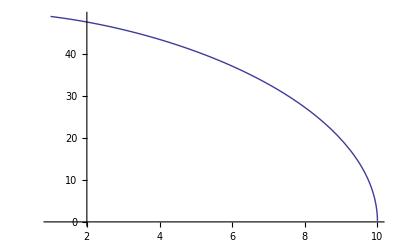

```mathematica
Plot[τ0s[ro]  /. do->10,{ro,1,10}]
```

```mathematica
(*  general solution in O(r0x^2/ro^4)
approx:  ϕo=0, yo=0
 *)
```

```mathematica
(* acceleration equation Newton  *)
```

```mathematica
repNox
```

{ro→r[τ],ϕo→ϕ[τ],θo→θ[τ]}

```mathematica
aror
```

{-1/(128 ro^4)r0x^2 (-1+μ) μ (6+24 Cos[2 θo]-30 Cos[4 θo]+15 Cos[4 θo-2 ϕb]-36 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θo+ϕb)]+15 Cos[2 (2 θo+ϕb)]) Csc[θo]-Sin[θo]/(2 ro^2),-(3 r0x^2 (-1+μ) μ Sin[θo] Sin[ϕb]^2)/(2 ro^4),-Cos[θo]/(2 ro^2)-1/(32 ro^4)3 r0x^2 (-1+μ) μ Cos[θo] (-2+10 Cos[2 θo]-5 Cos[2 (θo-ϕb)]+10 Cos[2 ϕb]-5 Cos[2 (θo+ϕb)])}

```mathematica
arorx=aror /. repNox
```

{-1/(128 r[τ]^4)r0x^2 (-1+μ) μ (6+10 Cos[2 ϕb]+15 Cos[2 ϕb-4 θ[τ]]+24 Cos[2 θ[τ]]-30 Cos[4 θ[τ]]-36 Cos[2 (-ϕb+θ[τ])]-36 Cos[2 (ϕb+θ[τ])]+15 Cos[2 (ϕb+2 θ[τ])]) Csc[θ[τ]]-Sin[θ[τ]]/(2 r[τ]^2),-(3 r0x^2 (-1+μ) μ Sin[ϕb]^2 Sin[θ[τ]])/(2 r[τ]^4),-1/(32 r[τ]^4)3 r0x^2 (-1+μ) μ Cos[θ[τ]] (-2+10 Cos[2 ϕb]+10 Cos[2 θ[τ]]-5 Cos[2 (-ϕb+θ[τ])]-5 Cos[2 (ϕb+θ[τ])])-Cos[θ[τ]]/(2 r[τ]^2)}

```mathematica
repphib=ϕb->(Pi/2+τ ω);
```

```mathematica
repphib=ϕb->(τ ω);
```

```mathematica
deqgN1=Simplify[xox''[τ]-arorx[[1]]   /. θ[τ]->θ0  /. r[τ]->ro   ]
```

1/(128 ro^4)r0x^2 (-1+μ) μ (6+24 Cos[2 θ0]-30 Cos[4 θ0]+15 Cos[4 θ0-2 ϕb]-36 Cos[2 (θ0-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θ0+ϕb)]+15 Cos[2 (2 θ0+ϕb)]) Csc[θ0]+Sin[θ0]/(2 ro^2)+2 Cos[θ0] r'[τ] θ'[τ]-ro Sin[θ0] θ'[τ]^2+Sin[θ0] r''[τ]+ro Cos[θ0] θ''[τ]

```mathematica
deqgN1=Simplify[xox''[τ]-arorx[[1]]   /. θ[τ]->θ0  /. r[τ]->ro   ]
```

1/(128 ro^4)r0x^2 (-1+μ) μ (6+24 Cos[2 θ0]-30 Cos[4 θ0]+15 Cos[4 θ0-2 ϕb]-36 Cos[2 (θ0-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θ0+ϕb)]+15 Cos[2 (2 θ0+ϕb)]) Csc[θ0]+Sin[θ0]/(2 ro^2)+2 Cos[θ0] r'[τ] θ'[τ]-ro Sin[θ0] θ'[τ]^2+Sin[θ0] r''[τ]+ro Cos[θ0] θ''[τ]

```mathematica
deqgN2=Simplify[yox''[τ]-arorx[[2]]  /. θ[τ]->θ0  /. r[τ]->ro   /. ϕ[τ]->0]
```

(3 r0x^2 (-1+μ) μ Sin[θ0] Sin[ϕb]^2)/(2 ro^4)+2 Sin[θ0] r'[τ] ϕ'[τ]+2 ro Cos[θ0] θ'[τ] ϕ'[τ]+ro Sin[θ0] ϕ''[τ]

```mathematica
deqgN3=Simplify[zox''[τ]-arorx[[3]]  /. θ[τ]->θ0  /. r[τ]->ro  ]
```

Cos[θ0]/(2 ro^2)+1/(32 ro^4)3 r0x^2 (-1+μ) μ Cos[θ0] (-2+10 Cos[2 θ0]-5 Cos[2 (θ0-ϕb)]+10 Cos[2 ϕb]-5 Cos[2 (θ0+ϕb)])-2 Sin[θ0] r'[τ] θ'[τ]-ro Cos[θ0] θ'[τ]^2+Cos[θ0] r''[τ]-ro Sin[θ0] θ''[τ]

```mathematica
Print[deqgN1 ]//TraditionalForm;
```

1/(128 ro^4)r0x^2 (-1+μ) μ (6+24 Cos[2 θ0]-30 Cos[4 θ0]+15 Cos[4 θ0-2 ϕb]-36 Cos[2 (θ0-ϕb)]+10 Cos[2 ϕb]-36 Cos[2 (θ0+ϕb)]+15 Cos[2 (2 θ0+ϕb)]) Csc[θ0]+Sin[θ0]/(2 ro^2)+2 Cos[θ0] r'[τ] θ'[τ]-ro Sin[θ0] θ'[τ]^2+Sin[θ0] r''[τ]+ro Cos[θ0] θ''[τ]

```mathematica
Print[deqgN2  ]//TraditionalForm  ;
```

(3 r0x^2 (-1+μ) μ Sin[θ0] Sin[ϕb]^2)/(2 ro^4)+2 Sin[θ0] r'[τ] ϕ'[τ]+2 ro Cos[θ0] θ'[τ] ϕ'[τ]+ro Sin[θ0] ϕ''[τ]

```mathematica
Print[deqgN3  ]//TraditionalForm  ;
```

Cos[θ0]/(2 ro^2)+1/(32 ro^4)3 r0x^2 (-1+μ) μ Cos[θ0] (-2+10 Cos[2 θ0]-5 Cos[2 (θ0-ϕb)]+10 Cos[2 ϕb]-5 Cos[2 (θ0+ϕb)])-2 Sin[θ0] r'[τ] θ'[τ]-ro Cos[θ0] θ'[τ]^2+Cos[θ0] r''[τ]-ro Sin[θ0] θ''[τ]

```mathematica
(* eq  ϕ''  deqgN2-order O(do Sin[θ0]) and O4dnA-order O(1):
2 Cot[θ0] θ'[τ] ϕ'[τ]+ ϕ''[τ] *)
```

```mathematica
O4dnA=α ((Fc (-1-ⅈ μ)^3 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)-(2 Fc (-ⅈ+μ)^3 Cot[θ0] θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2))+(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+α^2 (((2 Cos[θ0]^2+6 ⅈ μ Cos[θ0]^2-6 μ^2 Cos[θ0]^2-2 ⅈ μ^3 Cos[θ0]^2-2 r[τ]-4 ⅈ μ r[τ]+2 μ^2 r[τ]-Sin[θ0]^2-3 ⅈ μ Sin[θ0]^2+3 μ^2 Sin[θ0]^2+ⅈ μ^3 Sin[θ0]^2) r'[τ] ϕ'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ]))+1/(r[τ]^3 (-1-ⅈ μ+r[τ]))2 Cot[θ0] (-r[τ]-3 ⅈ μ r[τ]+3 μ^2 r[τ]+ⅈ μ^3 r[τ]+Cos[θ0]^2 r[τ]+3 ⅈ μ Cos[θ0]^2 r[τ]-3 μ^2 Cos[θ0]^2 r[τ]-ⅈ μ^3 Cos[θ0]^2 r[τ]-Sin[θ0]^2-4 ⅈ μ Sin[θ0]^2+6 μ^2 Sin[θ0]^2+4 ⅈ μ^3 Sin[θ0]^2-μ^4 Sin[θ0]^2+2 r[τ] Sin[θ0]^2+6 ⅈ μ r[τ] Sin[θ0]^2-6 μ^2 r[τ] Sin[θ0]^2-2 ⅈ μ^3 r[τ] Sin[θ0]^2) θ'[τ] ϕ'[τ])+ϕ''[τ]
```

α ((Fc (-1-ⅈ μ)^3 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)-(2 Fc (-ⅈ+μ)^3 Cot[θ0] θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2))+(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+α^2 (((2 Cos[θ0]^2+6 ⅈ μ Cos[θ0]^2-6 μ^2 Cos[θ0]^2-2 ⅈ μ^3 Cos[θ0]^2-2 r[τ]-4 ⅈ μ r[τ]+2 μ^2 r[τ]-Sin[θ0]^2-3 ⅈ μ Sin[θ0]^2+3 μ^2 Sin[θ0]^2+ⅈ μ^3 Sin[θ0]^2) r'[τ] ϕ'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ]))+(2 Cot[θ0] (-r[τ]-3 ⅈ μ r[τ]+3 μ^2 r[τ]+ⅈ μ^3 r[τ]+Cos[θ0]^2 r[τ]+3 ⅈ μ Cos[θ0]^2 r[τ]-3 μ^2 Cos[θ0]^2 r[τ]-ⅈ μ^3 Cos[θ0]^2 r[τ]-Sin[θ0]^2-4 ⅈ μ Sin[θ0]^2+6 μ^2 Sin[θ0]^2+4 ⅈ μ^3 Sin[θ0]^2-μ^4 Sin[θ0]^2+2 r[τ] Sin[θ0]^2+6 ⅈ μ r[τ] Sin[θ0]^2-6 μ^2 r[τ] Sin[θ0]^2-2 ⅈ μ^3 r[τ] Sin[θ0]^2) θ'[τ] ϕ'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ])))+ϕ''[τ]

```mathematica
deqgN2=Simplify[yox''[τ]-arorx[[2]]  /. θ[τ]->θ0      /. ϕ[τ]->0]
```

(3 r0x^2 (-1+μ) μ Sin[θ0] Sin[ϕb]^2)/(2 r[τ]^4)+2 Sin[θ0] r'[τ] ϕ'[τ]+r[τ] (2 Cos[θ0] θ'[τ] ϕ'[τ]+Sin[θ0] ϕ''[τ])

```mathematica
Print[deqgN2  ]//TraditionalForm  ;
```

(3 r0x^2 (-1+μ) μ Sin[θ0] Sin[ϕb]^2)/(2 r[τ]^4)+2 Sin[θ0] r'[τ] ϕ'[τ]+r[τ] (2 Cos[θ0] θ'[τ] ϕ'[τ]+Sin[θ0] ϕ''[τ])

```mathematica
Print[Simplify[O4dnA  /. μ->0 /. r[τ]->ro]]//TraditionalForm;
```

(Fc α (r'[τ]-2 (-1+ro) Cot[θ0] θ'[τ]))/((-1+ro)^2 ro^2)+(2 r'[τ] ϕ'[τ])/ro+2 Cot[θ0] θ'[τ] ϕ'[τ]+(α^2 ((1-4 ro+3 Cos[2 θ0]) r'[τ]+2 (-1+ro) Sin[2 θ0] θ'[τ]) ϕ'[τ])/(2 (-1+ro) ro^3)+ϕ''[τ]

```mathematica
deqgN2a=2 Sin[θ0] r'[τ] ϕ'[τ]/ro+2  Cos[θ0] θ'[τ] ϕ'[τ]+ Sin[θ0] ϕ''[τ]
Print[deqgN2a]//TraditionalForm;
```

(2 Sin[θ0] r'[τ] ϕ'[τ])/ro+2 Cos[θ0] θ'[τ] ϕ'[τ]+Sin[θ0] ϕ''[τ]

(2 Sin[θ0] r'[τ] ϕ'[τ])/ro+2 Cos[θ0] θ'[τ] ϕ'[τ]+Sin[θ0] ϕ''[τ]

```mathematica
(* eq θ'' : 2 r'[τ] θ'[τ]+r[τ] θ''[τ] with (2 r'[τ] θ'[τ])/r[τ] +θ''[τ]-Cos[θ0] Sin[θ0] ϕ'[τ]^2 ;ϕ' neglected
ϕ'[τ]r[τ]^2=lphi; ϕ'^2=lphi^2/r^4
 *)
```

```mathematica
O3dnA =(2 r'[τ] θ'[τ])/r[τ]+(Fc α (-ⅈ+μ)^3 Sin[2 θ0] ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)-Cos[θ0] Sin[θ0] ϕ'[τ]^2+α^2 ((Fc^2 (1+ⅈ μ)^5 Cos[θ0] Sin[θ0])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)-(ⅈ (-ⅈ+μ)^2 Sin[2 θ0] r'[τ]^2)/(2 (-ⅈ+μ+ⅈ r[τ]) r[τ]^3)+(2 (-ⅈ+μ)^2 Cos[θ0]^2 r'[τ] θ'[τ])/r[τ]^3+((-ⅈ+μ)^2 Cos[θ0] Sin[θ0] θ'[τ]^2)/r[τ]^2-1/r[τ]^3(-ⅈ+μ)^2 Cos[θ0] Sin[θ0] (-r[τ]+Cos[θ0]^2 r[τ]-2 Sin[θ0]^2-2 ⅈ μ Sin[θ0]^2) ϕ'[τ]^2)+θ''[τ]
```

(2 r'[τ] θ'[τ])/r[τ]+(Fc α (-ⅈ+μ)^3 Sin[2 θ0] ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)-Cos[θ0] Sin[θ0] ϕ'[τ]^2+α^2 ((Fc^2 (1+ⅈ μ)^5 Cos[θ0] Sin[θ0])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)-(ⅈ (-ⅈ+μ)^2 Sin[2 θ0] r'[τ]^2)/(2 (-ⅈ+μ+ⅈ r[τ]) r[τ]^3)+(2 (-ⅈ+μ)^2 Cos[θ0]^2 r'[τ] θ'[τ])/r[τ]^3+((-ⅈ+μ)^2 Cos[θ0] Sin[θ0] θ'[τ]^2)/r[τ]^2-1/r[τ]^3(-ⅈ+μ)^2 Cos[θ0] Sin[θ0] (-r[τ]+Cos[θ0]^2 r[τ]-2 Sin[θ0]^2-2 ⅈ μ Sin[θ0]^2) ϕ'[τ]^2)+θ''[τ]

```mathematica
(*  equation  θ''   *)
```

```mathematica
deqgN13=Simplify[Cos[θ0]deqgN1-Sin[θ0] deqgN3 ] /. 1/(32 ro^4)Csc[θ0]->1
```

2 r0x^2 (-1+μ) μ Cos[θ0] (6-6 Cos[2 θ0]+3 Cos[2 (θ0-ϕb)]-10 Cos[2 ϕb]+3 Cos[2 (θ0+ϕb)])+64 ro^4 Sin[θ0] r'[τ] θ'[τ]+32 ro^5 Sin[θ0] θ''[τ]

```mathematica
Print[deqgN13  ]//TraditionalForm;
```

2 r0x^2 (-1+μ) μ Cos[θ0] (6-6 Cos[2 θ0]+3 Cos[2 (θ0-ϕb)]-10 Cos[2 ϕb]+3 Cos[2 (θ0+ϕb)])+64 ro^4 Sin[θ0] r'[τ] θ'[τ]+32 ro^5 Sin[θ0] θ''[τ]

```mathematica
Print[Simplify[O3dnA  /. μ->0 /. r[τ]->ro]]//TraditionalForm;
```

(2 r'[τ] θ'[τ])/ro+(Fc α Sin[2 θ0] ϕ'[τ])/((-1+ro) ro^2)-Cos[θ0] Sin[θ0] ϕ'[τ]^2-1/(2 ro^3)α^2 ((Fc^2 Sin[2 θ0])/(-1+ro)^2-(Sin[2 θ0] r'[τ]^2)/(-1+ro)+4 Cos[θ0]^2 r'[τ] θ'[τ]+ro Sin[2 θ0] θ'[τ]^2+2 (2+ro) Cos[θ0] Sin[θ0]^3 ϕ'[τ]^2)+θ''[τ]

```mathematica
deqgN13a=2  r'[τ] θ'[τ]+ ro θ''[τ]
Print[deqgN13a]//TraditionalForm;
```

2 r'[τ] θ'[τ]+ro θ''[τ]

2 r'[τ] θ'[τ]+ro θ''[τ]

```mathematica
(* eq r'': comparison  r''-r*θ'^2 -r*Sin[θ0]^2 ϕ'^2 +1/(2 r[τ]^2), ϕ' neglected *)
```

```mathematica
O2dnA=(Fc α (-1-ⅈ μ)^3 Sin[θ0]^2 ϕ'[τ])/r[τ]^2+1/2 α^2 ((Fc^2 (-ⅈ+μ)^5 (-4 ⅈ Cos[θ0]^2+4 μ Cos[θ0]^2-ⅈ r[τ]+4 ⅈ Cos[θ0]^2 r[τ]))/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+1/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)(-ⅈ+μ)^2 (-2 Cos[θ0]^2-4 ⅈ μ Cos[θ0]^2+2 μ^2 Cos[θ0]^2+r[τ]+ⅈ μ r[τ]+2 Cos[θ0]^2 r[τ]+2 ⅈ μ Cos[θ0]^2 r[τ]-2 r[τ] Sin[θ0]^2-2 ⅈ μ r[τ] Sin[θ0]^2+2 r[τ]^2 Sin[θ0]^2) r'[τ]^2+(4 (-ⅈ+μ)^2 Cos[θ0] Sin[θ0] r'[τ] θ'[τ])/r[τ]^2-2 r[τ] ((1+2 ⅈ μ-μ^2)/r[τ]^2+((-ⅈ+μ)^2 Cos[θ0]^2 (-r[τ]-ⅈ μ r[τ]+r[τ]^2))/r[τ]^4) θ'[τ]^2+1/2 Sin[θ0]^2 (4 r[τ]^5 ((-1-2 ⅈ μ+μ^2)/r[τ]^6+(3 (-ⅈ+μ)^2 Cos[θ0]^2 (r[τ]+ⅈ μ r[τ]-r[τ]^2))/r[τ]^8)+1/r[τ]^6(r[τ]+ⅈ μ r[τ]-r[τ]^2) (-8 (-ⅈ+μ)^2 Cos[θ0]^2 r[τ]^3+2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ0]^2)) ϕ'[τ]^2)+1/2 ((Fc^2 (-ⅈ+μ)^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+((-ⅈ+μ) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ]) r[τ])-2 (-1-ⅈ μ+r[τ]) θ'[τ]^2-2 (-1-ⅈ μ+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])
```

(Fc α (-1-ⅈ μ)^3 Sin[θ0]^2 ϕ'[τ])/r[τ]^2+1/2 α^2 ((Fc^2 (-ⅈ+μ)^5 (-4 ⅈ Cos[θ0]^2+4 μ Cos[θ0]^2-ⅈ r[τ]+4 ⅈ Cos[θ0]^2 r[τ]))/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+((-ⅈ+μ)^2 (-2 Cos[θ0]^2-4 ⅈ μ Cos[θ0]^2+2 μ^2 Cos[θ0]^2+r[τ]+ⅈ μ r[τ]+2 Cos[θ0]^2 r[τ]+2 ⅈ μ Cos[θ0]^2 r[τ]-2 r[τ] Sin[θ0]^2-2 ⅈ μ r[τ] Sin[θ0]^2+2 r[τ]^2 Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+(4 (-ⅈ+μ)^2 Cos[θ0] Sin[θ0] r'[τ] θ'[τ])/r[τ]^2-2 r[τ] ((1+2 ⅈ μ-μ^2)/r[τ]^2+((-ⅈ+μ)^2 Cos[θ0]^2 (-r[τ]-ⅈ μ r[τ]+r[τ]^2))/r[τ]^4) θ'[τ]^2+1/2 Sin[θ0]^2 (4 r[τ]^5 ((-1-2 ⅈ μ+μ^2)/r[τ]^6+(3 (-ⅈ+μ)^2 Cos[θ0]^2 (r[τ]+ⅈ μ r[τ]-r[τ]^2))/r[τ]^8)+1/r[τ]^6(r[τ]+ⅈ μ r[τ]-r[τ]^2) (-8 (-ⅈ+μ)^2 Cos[θ0]^2 r[τ]^3+2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ0]^2)) ϕ'[τ]^2)+1/2 ((Fc^2 (-ⅈ+μ)^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+((-ⅈ+μ) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ]) r[τ])-2 (-1-ⅈ μ+r[τ]) θ'[τ]^2-2 (-1-ⅈ μ+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])

```mathematica
(*  equation  r''  *)
deqgN31=Simplify[Sin[θ0]deqgN1+Cos[θ0] deqgN3 ]  /. 1/(32 ro^4)->1
```

16 ro^2-6 r0x^2 μ+6 r0x^2 μ^2-18 r0x^2 μ Cos[2 θ0]+18 r0x^2 μ^2 Cos[2 θ0]+9 r0x^2 μ Cos[2 (θ0-ϕb)]-9 r0x^2 μ^2 Cos[2 (θ0-ϕb)]-10 r0x^2 μ Cos[2 ϕb]+10 r0x^2 μ^2 Cos[2 ϕb]+9 r0x^2 μ Cos[2 (θ0+ϕb)]-9 r0x^2 μ^2 Cos[2 (θ0+ϕb)]-32 ro^5 θ'[τ]^2+32 ro^4 r''[τ]

```mathematica
Print[deqgN31  ]//TraditionalForm;
```

16 ro^2-6 r0x^2 μ+6 r0x^2 μ^2-18 r0x^2 μ Cos[2 θ0]+18 r0x^2 μ^2 Cos[2 θ0]+9 r0x^2 μ Cos[2 (θ0-ϕb)]-9 r0x^2 μ^2 Cos[2 (θ0-ϕb)]-10 r0x^2 μ Cos[2 ϕb]+10 r0x^2 μ^2 Cos[2 ϕb]+9 r0x^2 μ Cos[2 (θ0+ϕb)]-9 r0x^2 μ^2 Cos[2 (θ0+ϕb)]-32 ro^5 θ'[τ]^2+32 ro^4 r''[τ]

```mathematica
Print[Simplify[O2dnA  /. μ->0 /. r[τ]->ro]]//TraditionalForm;
```

1/2 (Fc^2/((-1+ro) ro)+r'[τ]^2/(ro-ro^2)-2 (-1+ro) θ'[τ]^2-(2 Fc α Sin[θ0]^2 ϕ'[τ])/ro^2-2 (-1+ro) Sin[θ0]^2 ϕ'[τ]^2+1/(2 ro^3)α^2 (-(2 Fc^2 (-2+ro+2 (-1+ro) Cos[2 θ0]))/(-1+ro)^2+(2 (-1+ro+ro^2-(-1+ro)^2 Cos[2 θ0]) r'[τ]^2)/(-1+ro)^2-8 ro Cos[θ0] Sin[θ0] r'[τ] θ'[τ]+4 ro (-ro+(-1+ro) Cos[θ0]^2) θ'[τ]^2+(-1-ro-2 ro^2+(1-3 ro+2 ro^2) Cos[2 θ0]) Sin[θ0]^2 ϕ'[τ]^2)+2 r''[τ])

```mathematica
(*  equation  r'' , term(1/do^4) neglected  *)deqgN31a=r''[τ] - ro θ'[τ]^2+1/(2 ro^2)
Print[deqgN31a]//TraditionalForm;
```

1/(2 ro^2)-ro θ'[τ]^2+r''[τ]

1/(2 ro^2)-ro θ'[τ]^2+r''[τ]

```mathematica
(* accel r'' in first correction order in r0x  *)
```

```mathematica
deqgNr=(r''[τ]-Sqrt[arorx.arorx])
```

-√((-1/(32 r[τ]^4)3 r0x^2 (-1+μ) μ Cos[θ[τ]] (-2+10 Cos[2 ϕb]+10 Cos[2 θ[τ]]-5 Cos[2 (-ϕb+θ[τ])]-5 Cos[2 (ϕb+θ[τ])])-Cos[θ[τ]]/(2 r[τ]^2))^2+(9 r0x^4 (-1+μ)^2 μ^2 Sin[ϕb]^4 Sin[θ[τ]]^2)/(4 r[τ]^8)+(-1/(128 r[τ]^4)r0x^2 (-1+μ) μ (6+10 Cos[2 ϕb]+15 Cos[2 ϕb-4 θ[τ]]+24 Cos[2 θ[τ]]-30 Cos[4 θ[τ]]-36 Cos[2 (-ϕb+θ[τ])]-36 Cos[2 (ϕb+θ[τ])]+15 Cos[2 (ϕb+2 θ[τ])]) Csc[θ[τ]]-Sin[θ[τ]]/(2 r[τ]^2))^2)+r''[τ]

```mathematica
(*  E1dn1 for comparison with deqgNr: trivial results   *)
```

```mathematica
E1dn1 /. θ'[τ]->lth/r[τ]^2  /. ϕ'[τ]-> lphi/r[τ]^2
```

-1+(Fc^2 (1-1/r[τ]))/(1-(1+ⅈμ)/r[τ])+r[τ]+(2 Fc lphi α (1+ⅈμ) (1-1/r[τ]) Sin[θ0]^2)/((1-(1+ⅈμ)/r[τ]) r[τ]^3)-((1-1/r[τ]) (lth^2+lphi^2 Sin[θ0]^2))/((1+ⅈμ)^2 r[τ]^2)-((1-1/r[τ]) r'[τ]^2)/(1-(1+ⅈμ)/r[τ])+α^2 (1-1/r[τ]) (-(lth^2 Cos[θ0]^2)/r[τ]^4+(Fc^2 (-1-ⅈ μ)^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-(lphi^2 Sin[θ0]^2)/r[τ]^4-(lphi^2 Sin[θ0]^4)/r[τ]^5-(ⅈ lphi^2 μ Sin[θ0]^4)/r[τ]^5+(((-1-ⅈ μ) Cos[θ0]^2-r[τ] Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]))

```mathematica
dE1dn1=r''[τ]-Simplify[D[r'[τ] /. Solve[E1dn1==0 /. θ'[τ]->lth/r[τ]^2  /. ϕ'[τ]-> lphi/r[τ]^2, r'[τ]][[2,1]],τ],TimeConstraint->0.1]
```

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

(((1+ⅈμ)/(1+ⅈμ-r[τ])^2+(2 ⅈ α^2 (-ⅈ+μ) Cos[θ0]^2)/(r[τ]^3 (-1-ⅈ μ+r[τ])^2)-(α^2 ((-ⅈ+μ) (-2 ⅈ+μ+(-4 ⅈ+μ) Cos[2 θ0])+(ⅈ μ+(2+ⅈ μ) Cos[2 θ0]) r[τ]))/(2 r[τ]^2 (-1-ⅈ μ+r[τ])^3)-((α^2 (μ+(-2 ⅈ+μ) Cos[2 θ0]))/(-ⅈ+μ+ⅈ r[τ])^3+r[τ]/(1+ⅈμ-r[τ])^2)/r[τ]+(2 α^2 Sin[θ0]^2)/(1+ⅈ μ-r[τ])^3) √(1-(lth^2 α^2 Cos[θ0]^2)/r[τ]^5+(lth^2 α^2 Cos[θ0]^2)/r[τ]^4-lth^2/((1+ⅈμ)^2 r[τ]^3)+lth^2/((1+ⅈμ)^2 r[τ]^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)+(Fc^2 α^2 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-r[τ]+(Fc^2 r[τ])/(1+ⅈμ-r[τ])+(Fc^2 α^2 Cos[θ0]^2)/(r[τ]^2 (-1-ⅈ μ+r[τ])^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/(r[τ]^2 (-1-ⅈ μ+r[τ])^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/(r[τ] (-1-ⅈ μ+r[τ])^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/(r[τ] (-1-ⅈ μ+r[τ])^2)+Fc^2/(-1-ⅈμ+r[τ])-(lphi^2 α^2 Sin[θ0]^2)/r[τ]^5+(lphi^2 α^2 Sin[θ0]^2)/r[τ]^4-(lphi^2 Sin[θ0]^2)/((1+ⅈμ)^2 r[τ]^3)-(2 Fc lphi α ⅈμ Sin[θ0]^2)/((1+ⅈμ-r[τ]) r[τ]^3)+(lphi^2 Sin[θ0]^2)/((1+ⅈμ)^2 r[τ]^2)+(2 Fc lphi α ⅈμ Sin[θ0]^2)/((1+ⅈμ-r[τ]) r[τ]^2)+(2 Fc lphi α Sin[θ0]^2)/(r[τ]^3 (-1-ⅈμ+r[τ]))-(2 Fc lphi α Sin[θ0]^2)/(r[τ]^2 (-1-ⅈμ+r[τ]))-(lphi^2 α^2 Sin[θ0]^4)/r[τ]^6-(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/r[τ]^6+(lphi^2 α^2 Sin[θ0]^4)/r[τ]^5+(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/r[τ]^5) r'[τ])/(2 (-((-1+r[τ]) (α^2 (1+ⅈ μ) (1+ⅈμ) Cos[θ0]^2+1/2 α^2 (-ⅈ μ+ⅈμ+(-2-ⅈ μ-ⅈμ) Cos[2 θ0]) r[τ]+(-2-2 ⅈ μ) r[τ]^3+r[τ]^4-r[τ]^2 ((-ⅈ+μ)^2+α^2 Sin[θ0]^2)))/(r[τ]^2 (-1-ⅈ μ+r[τ])^2 (-1-ⅈμ+r[τ])))^(3/2))-(-r'[τ]+(Fc^2 (1+ⅈμ) r'[τ])/(1+ⅈμ-r[τ])^2+(5 lth^2 α^2 Cos[θ0]^2 r'[τ])/r[τ]^6-(4 lth^2 α^2 Cos[θ0]^2 r'[τ])/r[τ]^5+(3 lth^2 r'[τ])/((1+ⅈμ)^2 r[τ]^4)-(2 lth^2 r'[τ])/((1+ⅈμ)^2 r[τ]^3)+(2 Fc^2 α^2 Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+(6 ⅈ Fc^2 α^2 μ Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+(2 Fc^2 α^2 Cos[θ0]^2 r'[τ])/((1+ⅈ μ-r[τ])^3 r[τ]^2)-(6 Fc^2 α^2 μ Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^3 r[τ]^2)+(2 Fc^2 α^2 μ^3 Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^3 r[τ]^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)+(6 Fc^2 α^2 μ^2 Cos[θ0]^2 r'[τ])/((1+ⅈ μ-r[τ])^3 r[τ])-(Fc^2 (1+ⅈμ) r'[τ])/((1+ⅈμ-r[τ])^2 r[τ])+(Fc^2 r'[τ])/((1+ⅈμ-r[τ]) r[τ])+(6 Fc^2 α^2 μ Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^3 r[τ])-(2 Fc^2 α^2 μ^3 Cos[θ0]^2 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^3 r[τ])+(6 Fc^2 α^2 μ^2 Cos[θ0]^2 r'[τ])/(r[τ]^2 (-1-ⅈ μ+r[τ])^3)+(2 Fc^2 α^2 Cos[θ0]^2 r'[τ])/(r[τ] (-1-ⅈ μ+r[τ])^3)+(6 Fc^2 α^2 μ^2 Cos[θ0]^2 r'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ])^2)+(2 ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2 r'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ])^2)+(Fc^2 α^2 Cos[θ0]^2 r'[τ])/(r[τ]^2 (-1-ⅈ μ+r[τ])^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2 r'[τ])/(r[τ]^2 (-1-ⅈ μ+r[τ])^2)+(5 lphi^2 α^2 Sin[θ0]^2 r'[τ])/r[τ]^6-(4 lphi^2 α^2 Sin[θ0]^2 r'[τ])/r[τ]^5+(3 lphi^2 Sin[θ0]^2 r'[τ])/((1+ⅈμ)^2 r[τ]^4)-(2 Fc lphi α (1+ⅈμ) Sin[θ0]^2 r'[τ])/((1+ⅈμ-r[τ])^2 r[τ]^4)-(2 Fc lphi α ⅈμ (1+ⅈμ) Sin[θ0]^2 r'[τ])/((1+ⅈμ-r[τ])^2 r[τ]^4)+(8 Fc lphi α ⅈμ Sin[θ0]^2 r'[τ])/((1+ⅈμ-r[τ]) r[τ]^4)-(2 lphi^2 Sin[θ0]^2 r'[τ])/((1+ⅈμ)^2 r[τ]^3)+(2 Fc lphi α (1+ⅈμ) Sin[θ0]^2 r'[τ])/((1+ⅈμ-r[τ])^2 r[τ]^3)+(2 Fc lphi α ⅈμ (1+ⅈμ) Sin[θ0]^2 r'[τ])/((1+ⅈμ-r[τ])^2 r[τ]^3)-(6 Fc lphi α ⅈμ Sin[θ0]^2 r'[τ])/((1+ⅈμ-r[τ]) r[τ]^3)-(8 Fc lphi α Sin[θ0]^2 r'[τ])/(r[τ]^4 (-1-ⅈμ+r[τ]))+(6 Fc lphi α Sin[θ0]^2 r'[τ])/(r[τ]^3 (-1-ⅈμ+r[τ]))+(6 lphi^2 α^2 Sin[θ0]^4 r'[τ])/r[τ]^7+(6 ⅈ lphi^2 α^2 μ Sin[θ0]^4 r'[τ])/r[τ]^7-(5 lphi^2 α^2 Sin[θ0]^4 r'[τ])/r[τ]^6-(5 ⅈ lphi^2 α^2 μ Sin[θ0]^4 r'[τ])/r[τ]^6)/(2 √(1-(lth^2 α^2 Cos[θ0]^2)/r[τ]^5+(lth^2 α^2 Cos[θ0]^2)/r[τ]^4-lth^2/((1+ⅈμ)^2 r[τ]^3)+lth^2/((1+ⅈμ)^2 r[τ]^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)+(Fc^2 α^2 Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ])-r[τ]+(Fc^2 r[τ])/(1+ⅈμ-r[τ])+(Fc^2 α^2 Cos[θ0]^2)/(r[τ]^2 (-1-ⅈ μ+r[τ])^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/(r[τ]^2 (-1-ⅈ μ+r[τ])^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/(r[τ] (-1-ⅈ μ+r[τ])^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/(r[τ] (-1-ⅈ μ+r[τ])^2)+Fc^2/(-1-ⅈμ+r[τ])-(lphi^2 α^2 Sin[θ0]^2)/r[τ]^5+(lphi^2 α^2 Sin[θ0]^2)/r[τ]^4-(lphi^2 Sin[θ0]^2)/((1+ⅈμ)^2 r[τ]^3)-(2 Fc lphi α ⅈμ Sin[θ0]^2)/((1+ⅈμ-r[τ]) r[τ]^3)+(lphi^2 Sin[θ0]^2)/((1+ⅈμ)^2 r[τ]^2)+(2 Fc lphi α ⅈμ Sin[θ0]^2)/((1+ⅈμ-r[τ]) r[τ]^2)+(2 Fc lphi α Sin[θ0]^2)/(r[τ]^3 (-1-ⅈμ+r[τ]))-(2 Fc lphi α Sin[θ0]^2)/(r[τ]^2 (-1-ⅈμ+r[τ]))-(lphi^2 α^2 Sin[θ0]^4)/r[τ]^6-(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/r[τ]^6+(lphi^2 α^2 Sin[θ0]^4)/r[τ]^5+(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/r[τ]^5) √(-((-1+r[τ]) (α^2 (1+ⅈ μ) (1+ⅈμ) Cos[θ0]^2+1/2 α^2 (-ⅈ μ+ⅈμ+(-2-ⅈ μ-ⅈμ) Cos[2 θ0]) r[τ]+(-2-2 ⅈ μ) r[τ]^3+r[τ]^4-r[τ]^2 ((-ⅈ+μ)^2+α^2 Sin[θ0]^2)))/(r[τ]^2 (-1-ⅈ μ+r[τ])^2 (-1-ⅈμ+r[τ]))))+r''[τ]

```mathematica
dE1dn2=Simplify[dE1dn1   /.  r'[τ]->  rx[τ]/( do^(3/2))  /. r[τ]->do,TimeConstraint->0.1]
```

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

(rx[τ] ((1+ⅈμ)/(1-do+ⅈμ)^2+(2 α^2 (1+ⅈ μ) Cos[θ0]^2)/(do^3 (-1+do-ⅈ μ)^2)-(α^2 (-2+ⅈ (-3+do) μ+μ^2+(-4+do (2+ⅈ μ)-5 ⅈ μ+μ^2) Cos[2 θ0]))/(2 do^2 (-1+do-ⅈ μ)^3)-(do/(1-do+ⅈμ)^2+(α^2 (μ+(-2 ⅈ+μ) Cos[2 θ0]))/(-ⅈ+ⅈ do+μ)^3)/do-(2 α^2 Sin[θ0]^2)/(-1+do-ⅈ μ)^3) √(1-do+Fc^2/(-1+do-ⅈμ)-lth^2/(do^3 (1+ⅈμ)^2)+lth^2/(do^2 (1+ⅈμ)^2)+(do Fc^2)/(1-do+ⅈμ)-(lth^2 α^2 Cos[θ0]^2)/do^5+(lth^2 α^2 Cos[θ0]^2)/do^4+(Fc^2 α^2 Cos[θ0]^2)/(do^2 (-1+do-ⅈ μ)^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/(do^2 (-1+do-ⅈ μ)^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/(do (-1+do-ⅈ μ)^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/(do (-1+do-ⅈ μ)^2)+(Fc^2 α^2 Cos[θ0]^2)/(do (-ⅈ+ⅈ do+μ)^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/(do (-ⅈ+ⅈ do+μ)^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/(do^2 (-ⅈ+ⅈ do+μ)^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/(do^2 (-ⅈ+ⅈ do+μ)^2)-(lphi^2 α^2 Sin[θ0]^2)/do^5+(lphi^2 α^2 Sin[θ0]^2)/do^4+(2 Fc lphi α Sin[θ0]^2)/(do^3 (-1+do-ⅈμ))-(2 Fc lphi α Sin[θ0]^2)/(do^2 (-1+do-ⅈμ))-(lphi^2 Sin[θ0]^2)/(do^3 (1+ⅈμ)^2)+(lphi^2 Sin[θ0]^2)/(do^2 (1+ⅈμ)^2)-(2 Fc lphi α ⅈμ Sin[θ0]^2)/(do^3 (1-do+ⅈμ))+(2 Fc lphi α ⅈμ Sin[θ0]^2)/(do^2 (1-do+ⅈμ))-(lphi^2 α^2 Sin[θ0]^4)/do^6+(lphi^2 α^2 Sin[θ0]^4)/do^5-(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/do^6+(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/do^5))/(2 do^(3/2) (-((-1+do) (do^4+do^3 (-2-2 ⅈ μ)+α^2 (1+ⅈ μ) (1+ⅈμ) Cos[θ0]^2+1/2 do α^2 (-ⅈ μ+ⅈμ+(-2-ⅈ μ-ⅈμ) Cos[2 θ0])-do^2 ((-ⅈ+μ)^2+α^2 Sin[θ0]^2)))/(do^2 (-1+do-ⅈ μ)^2 (-1+do-ⅈμ)))^(3/2))-(rx[τ] (-do^7+(3 do^3 lth^2)/(1+ⅈμ)^2-(2 do^4 lth^2)/(1+ⅈμ)^2-(do^6 Fc^2 (1+ⅈμ))/(1-do+ⅈμ)^2+(do^7 Fc^2 (1+ⅈμ))/(1-do+ⅈμ)^2+(do^6 Fc^2)/(1-do+ⅈμ)+5 do lth^2 α^2 Cos[θ0]^2-4 do^2 lth^2 α^2 Cos[θ0]^2-(2 do^5 Fc^2 α^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^3+(2 do^6 Fc^2 α^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^3-(2 do^4 Fc^2 α^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^2+(do^5 Fc^2 α^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^2-(6 ⅈ do^4 Fc^2 α^2 μ Cos[θ0]^2)/(-1+do-ⅈ μ)^2+(3 ⅈ do^5 Fc^2 α^2 μ Cos[θ0]^2)/(-1+do-ⅈ μ)^2+(6 do^5 Fc^2 α^2 μ^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^3-(6 do^6 Fc^2 α^2 μ^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^3+(6 do^4 Fc^2 α^2 μ^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^2-(3 do^5 Fc^2 α^2 μ^2 Cos[θ0]^2)/(-1+do-ⅈ μ)^2+(2 ⅈ do^4 Fc^2 α^2 μ^3 Cos[θ0]^2)/(-1+do-ⅈ μ)^2-(ⅈ do^5 Fc^2 α^2 μ^3 Cos[θ0]^2)/(-1+do-ⅈ μ)^2-(6 do^5 Fc^2 α^2 μ Cos[θ0]^2)/(-ⅈ+ⅈ do+μ)^3+(6 do^6 Fc^2 α^2 μ Cos[θ0]^2)/(-ⅈ+ⅈ do+μ)^3+(2 do^5 Fc^2 α^2 μ^3 Cos[θ0]^2)/(-ⅈ+ⅈ do+μ)^3-(2 do^6 Fc^2 α^2 μ^3 Cos[θ0]^2)/(-ⅈ+ⅈ do+μ)^3+5 do lphi^2 α^2 Sin[θ0]^2-4 do^2 lphi^2 α^2 Sin[θ0]^2+(6 do^4 Fc lphi α Sin[θ0]^2)/(-1+do-ⅈμ)+(3 do^3 lphi^2 Sin[θ0]^2)/(1+ⅈμ)^2-(2 do^4 lphi^2 Sin[θ0]^2)/(1+ⅈμ)^2-(2 do^3 Fc lphi α (1+ⅈμ) Sin[θ0]^2)/(1-do+ⅈμ)^2+(2 do^4 Fc lphi α (1+ⅈμ) Sin[θ0]^2)/(1-do+ⅈμ)^2-(2 do^3 Fc lphi α ⅈμ (1+ⅈμ) Sin[θ0]^2)/(1-do+ⅈμ)^2+(2 do^4 Fc lphi α ⅈμ (1+ⅈμ) Sin[θ0]^2)/(1-do+ⅈμ)^2+(8 do^3 Fc lphi α Sin[θ0]^2)/(1-do+ⅈμ)+(8 do^3 Fc lphi α ⅈμ Sin[θ0]^2)/(1-do+ⅈμ)-(6 do^4 Fc lphi α ⅈμ Sin[θ0]^2)/(1-do+ⅈμ)+6 lphi^2 α^2 Sin[θ0]^4-5 do lphi^2 α^2 Sin[θ0]^4+6 ⅈ lphi^2 α^2 μ Sin[θ0]^4-5 ⅈ do lphi^2 α^2 μ Sin[θ0]^4))/(2 do^(17/2) √(1-do+Fc^2/(-1+do-ⅈμ)-lth^2/(do^3 (1+ⅈμ)^2)+lth^2/(do^2 (1+ⅈμ)^2)+(do Fc^2)/(1-do+ⅈμ)-(lth^2 α^2 Cos[θ0]^2)/do^5+(lth^2 α^2 Cos[θ0]^2)/do^4+(Fc^2 α^2 Cos[θ0]^2)/(do^2 (-1+do-ⅈ μ)^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/(do^2 (-1+do-ⅈ μ)^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/(do (-1+do-ⅈ μ)^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/(do (-1+do-ⅈ μ)^2)+(Fc^2 α^2 Cos[θ0]^2)/(do (-ⅈ+ⅈ do+μ)^2)+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/(do (-ⅈ+ⅈ do+μ)^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/(do^2 (-ⅈ+ⅈ do+μ)^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/(do^2 (-ⅈ+ⅈ do+μ)^2)-(lphi^2 α^2 Sin[θ0]^2)/do^5+(lphi^2 α^2 Sin[θ0]^2)/do^4+(2 Fc lphi α Sin[θ0]^2)/(do^3 (-1+do-ⅈμ))-(2 Fc lphi α Sin[θ0]^2)/(do^2 (-1+do-ⅈμ))-(lphi^2 Sin[θ0]^2)/(do^3 (1+ⅈμ)^2)+(lphi^2 Sin[θ0]^2)/(do^2 (1+ⅈμ)^2)-(2 Fc lphi α ⅈμ Sin[θ0]^2)/(do^3 (1-do+ⅈμ))+(2 Fc lphi α ⅈμ Sin[θ0]^2)/(do^2 (1-do+ⅈμ))-(lphi^2 α^2 Sin[θ0]^4)/do^6+(lphi^2 α^2 Sin[θ0]^4)/do^5-(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/do^6+(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/do^5) √(-((-1+do) (do^4+do^3 (-2-2 ⅈ μ)+α^2 (1+ⅈ μ) (1+ⅈμ) Cos[θ0]^2+1/2 do α^2 (-ⅈ μ+ⅈμ+(-2-ⅈ μ-ⅈμ) Cos[2 θ0])-do^2 ((-ⅈ+μ)^2+α^2 Sin[θ0]^2)))/(do^2 (-1+do-ⅈ μ)^2 (-1+do-ⅈμ))))+r''[τ]

```mathematica
Series[dE1dn2 /. do->1/p,{p,0,4}]
```

r''[τ]-1/2 rx[τ] p^2+1/4 (-rx[τ]+Fc^2 rx[τ]-ⅈμ rx[τ]) p^3-3/16 (rx[τ]-2 Fc^2 rx[τ]+Fc^4 rx[τ]+2 ⅈμ rx[τ]-2 Fc^2 ⅈμ rx[τ]+ⅈμ^2 rx[τ]-4 α^2 rx[τ] Sin[θ0]^2) p^4+O[p]^(9/2)

```mathematica
(* series r'' Newton in r0x *)
```

```mathematica
(* energy equation E, orbit equations: com-spacetime *)
```

```mathematica
repN
```

{t'[τ]→Fc/(1-(1+ⅈ μ)/r[τ]),t''[τ]→0}

```mathematica
E1dA=-1+(Fc^2 r[τ])/(-1-ⅈ μ+r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 θ'[τ]^2)/(-ⅈ+μ)^2+(r[τ]^2 Sin[θ0]^2 ϕ'[τ]^2)/(-ⅈ+μ)^2
```

-1+(Fc^2 r[τ])/(-1-ⅈ μ+r[τ])+(ⅈ r[τ] r'[τ]^2)/((-ⅈ+μ)^2 (-ⅈ+μ+ⅈ r[τ]))+(r[τ]^2 θ'[τ]^2)/(-ⅈ+μ)^2+(r[τ]^2 Sin[θ0]^2 ϕ'[τ]^2)/(-ⅈ+μ)^2

```mathematica
(* r[τ]->r[τ]/(1+ⅈ μ)  *)
E1dN=Simplify[E1dA /. μ->0]
```

-1+(r[τ] (Fc^2-r'[τ]^2))/(-1+r[τ])-r[τ]^2 (θ'[τ]^2+Sin[θ0]^2 ϕ'[τ]^2)

```mathematica
(* orbit equations spacetime : fullfilled with ϕ'[τ]=O(1/r[τ]^5) ,r'[τ]=O(1/r[τ]^4) *)
```

```mathematica
O1dA
O1dN=Simplify[O1dA /. μ->0]
```

-(ⅈ Fc (-ⅈ+μ) r'[τ])/(-ⅈ+μ+ⅈ r[τ])^2

(Fc r'[τ])/(-1+r[τ])^2

```mathematica
O2dA
O2dN=Simplify[O2dA /. μ->0]
```

1/2 ((Fc^2 (-ⅈ+μ)^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+((-ⅈ+μ) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ]) r[τ])-2 (-1-ⅈ μ+r[τ]) θ'[τ]^2-2 (-1-ⅈ μ+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])

1/2 (Fc^2/((-1+r[τ]) r[τ])+r'[τ]^2/(r[τ]-r[τ]^2)-2 (-1+r[τ]) θ'[τ]^2-2 (-1+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])

```mathematica
O3dA
O3dN=Simplify[O3dA /. μ->0]
```

(2 r'[τ] θ'[τ])/r[τ]-Cos[θ0] Sin[θ0] ϕ'[τ]^2+θ''[τ]

(2 r'[τ] θ'[τ])/r[τ]-Cos[θ0] Sin[θ0] ϕ'[τ]^2+θ''[τ]

```mathematica
O4dA
O4dN=Simplify[O4dA /. μ->0]
```

(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+ϕ''[τ]

(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
O1dnA= SeriesCoefficient[Series[O1dn ,{α,0,3}],0] + α SeriesCoefficient[Series[O1dn ,{α,0,3}],1] + α^2 SeriesCoefficient[Series[O1dn ,{α,0,3}],2]
```

-(ⅈ Fc (-ⅈ+μ) r'[τ])/(-ⅈ+μ+ⅈ r[τ])^2+α^2 (-ⅈ+μ) ((Fc (-ⅈ+μ)^2 (1+ⅈ μ-3 Cos[θ0]^2-3 ⅈ μ Cos[θ0]^2+3 Cos[θ0]^2 r[τ]) r'[τ])/((-ⅈ+μ+ⅈ r[τ])^3 r[τ]^2)-(Fc (-ⅈ+μ)^2 Sin[2 θ0] θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2))-(3 ⅈ α (-ⅈ+μ) Sin[θ0]^2 r'[τ] ϕ'[τ])/(r[τ] (-1-ⅈ μ+r[τ]))

```mathematica
O2dnA= SeriesCoefficient[Series[O2dn ,{α,0,3}],0] + α SeriesCoefficient[Series[O2dn ,{α,0,3}],1] + α^2 SeriesCoefficient[Series[O2dn ,{α,0,3}],2]
```

(Fc α (-1-ⅈ μ)^3 Sin[θ0]^2 ϕ'[τ])/r[τ]^2+1/2 α^2 ((Fc^2 (-ⅈ+μ)^5 (-4 ⅈ Cos[θ0]^2+4 μ Cos[θ0]^2-ⅈ r[τ]+4 ⅈ Cos[θ0]^2 r[τ]))/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+((-ⅈ+μ)^2 (-2 Cos[θ0]^2-4 ⅈ μ Cos[θ0]^2+2 μ^2 Cos[θ0]^2+r[τ]+ⅈ μ r[τ]+2 Cos[θ0]^2 r[τ]+2 ⅈ μ Cos[θ0]^2 r[τ]-2 r[τ] Sin[θ0]^2-2 ⅈ μ r[τ] Sin[θ0]^2+2 r[τ]^2 Sin[θ0]^2) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^3)+(4 (-ⅈ+μ)^2 Cos[θ0] Sin[θ0] r'[τ] θ'[τ])/r[τ]^2-2 r[τ] ((1+2 ⅈ μ-μ^2)/r[τ]^2+((-ⅈ+μ)^2 Cos[θ0]^2 (-r[τ]-ⅈ μ r[τ]+r[τ]^2))/r[τ]^4) θ'[τ]^2+1/2 Sin[θ0]^2 (4 r[τ]^5 ((-1-2 ⅈ μ+μ^2)/r[τ]^6+(3 (-ⅈ+μ)^2 Cos[θ0]^2 (r[τ]+ⅈ μ r[τ]-r[τ]^2))/r[τ]^8)+1/r[τ]^6(r[τ]+ⅈ μ r[τ]-r[τ]^2) (-8 (-ⅈ+μ)^2 Cos[θ0]^2 r[τ]^3+2 (-1-ⅈ μ)^3 r[τ]^2 Sin[θ0]^2)) ϕ'[τ]^2)+1/2 ((Fc^2 (-ⅈ+μ)^3)/((-ⅈ+μ+ⅈ r[τ]) r[τ])+((-ⅈ+μ) r'[τ]^2)/((-ⅈ+μ+ⅈ r[τ]) r[τ])-2 (-1-ⅈ μ+r[τ]) θ'[τ]^2-2 (-1-ⅈ μ+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])

```mathematica
O3dnA= SeriesCoefficient[Series[O3dn ,{α,0,3}],0] + α SeriesCoefficient[Series[O3dn ,{α,0,3}],1] + α^2 SeriesCoefficient[Series[O3dn ,{α,0,3}],2]
```

(2 r'[τ] θ'[τ])/r[τ]+(Fc α (-ⅈ+μ)^3 Sin[2 θ0] ϕ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2)-Cos[θ0] Sin[θ0] ϕ'[τ]^2+α^2 (-(Fc^2 (1+ⅈ μ)^5 Cos[θ0] Sin[θ0])/(r[τ]^3 (-1-ⅈ μ+r[τ])^2)-(ⅈ (-ⅈ+μ)^2 Sin[2 θ0] r'[τ]^2)/(2 (-ⅈ+μ+ⅈ r[τ]) r[τ]^3)+(2 (-ⅈ+μ)^2 Cos[θ0]^2 r'[τ] θ'[τ])/r[τ]^3+((-ⅈ+μ)^2 Cos[θ0] Sin[θ0] θ'[τ]^2)/r[τ]^2-1/r[τ]^3(-ⅈ+μ)^2 Cos[θ0] Sin[θ0] (-r[τ]+Cos[θ0]^2 r[τ]-2 Sin[θ0]^2-2 ⅈ μ Sin[θ0]^2) ϕ'[τ]^2)+θ''[τ]

```mathematica
O4dnA= SeriesCoefficient[Series[O4dn ,{α,0,3}],0] + α SeriesCoefficient[Series[O4dn ,{α,0,3}],1] + α^2 SeriesCoefficient[Series[O4dn ,{α,0,3}],2]
```

α ((Fc (-1-ⅈ μ)^3 r'[τ])/((-ⅈ+μ+ⅈ r[τ])^2 r[τ]^2)-(2 Fc (-ⅈ+μ)^3 Cot[θ0] θ'[τ])/((-ⅈ+μ+ⅈ r[τ]) r[τ]^2))+(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+α^2 (((2 Cos[θ0]^2+6 ⅈ μ Cos[θ0]^2-6 μ^2 Cos[θ0]^2-2 ⅈ μ^3 Cos[θ0]^2-2 r[τ]-4 ⅈ μ r[τ]+2 μ^2 r[τ]-Sin[θ0]^2-3 ⅈ μ Sin[θ0]^2+3 μ^2 Sin[θ0]^2+ⅈ μ^3 Sin[θ0]^2) r'[τ] ϕ'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ]))+(2 Cot[θ0] (-r[τ]-3 ⅈ μ r[τ]+3 μ^2 r[τ]+ⅈ μ^3 r[τ]+Cos[θ0]^2 r[τ]+3 ⅈ μ Cos[θ0]^2 r[τ]-3 μ^2 Cos[θ0]^2 r[τ]-ⅈ μ^3 Cos[θ0]^2 r[τ]-Sin[θ0]^2-4 ⅈ μ Sin[θ0]^2+6 μ^2 Sin[θ0]^2+4 ⅈ μ^3 Sin[θ0]^2-μ^4 Sin[θ0]^2+2 r[τ] Sin[θ0]^2+6 ⅈ μ r[τ] Sin[θ0]^2-6 μ^2 r[τ] Sin[θ0]^2-2 ⅈ μ^3 r[τ] Sin[θ0]^2) θ'[τ] ϕ'[τ])/(r[τ]^3 (-1-ⅈ μ+r[τ])))+ϕ''[τ]

```mathematica
O1dnAm=O1dnA /. μ->0
```

-(Fc r'[τ])/(-ⅈ+ⅈ r[τ])^2-ⅈ α^2 (-(Fc (1-3 Cos[θ0]^2+3 Cos[θ0]^2 r[τ]) r'[τ])/((-ⅈ+ⅈ r[τ])^3 r[τ]^2)+(Fc Sin[2 θ0] θ'[τ])/((-ⅈ+ⅈ r[τ]) r[τ]^2))-(3 α Sin[θ0]^2 r'[τ] ϕ'[τ])/((-1+r[τ]) r[τ])

```mathematica
O2dnAm=O2dnA /. μ->0
```

-(Fc α Sin[θ0]^2 ϕ'[τ])/r[τ]^2+1/2 α^2 (-(ⅈ Fc^2 (-4 ⅈ Cos[θ0]^2-ⅈ r[τ]+4 ⅈ Cos[θ0]^2 r[τ]))/((-ⅈ+ⅈ r[τ])^2 r[τ]^3)-((-2 Cos[θ0]^2+r[τ]+2 Cos[θ0]^2 r[τ]-2 r[τ] Sin[θ0]^2+2 r[τ]^2 Sin[θ0]^2) r'[τ]^2)/((-ⅈ+ⅈ r[τ])^2 r[τ]^3)-(4 Cos[θ0] Sin[θ0] r'[τ] θ'[τ])/r[τ]^2-2 r[τ] (1/r[τ]^2-(Cos[θ0]^2 (-r[τ]+r[τ]^2))/r[τ]^4) θ'[τ]^2+1/2 Sin[θ0]^2 (4 r[τ]^5 (-1/r[τ]^6-(3 Cos[θ0]^2 (r[τ]-r[τ]^2))/r[τ]^8)+((r[τ]-r[τ]^2) (8 Cos[θ0]^2 r[τ]^3-2 r[τ]^2 Sin[θ0]^2))/r[τ]^6) ϕ'[τ]^2)+1/2 ((ⅈ Fc^2)/((-ⅈ+ⅈ r[τ]) r[τ])-(ⅈ r'[τ]^2)/((-ⅈ+ⅈ r[τ]) r[τ])-2 (-1+r[τ]) θ'[τ]^2-2 (-1+r[τ]) Sin[θ0]^2 ϕ'[τ]^2+2 r''[τ])

```mathematica
O3dnAm=O3dnA /. μ->0
```

(2 r'[τ] θ'[τ])/r[τ]+(ⅈ Fc α Sin[2 θ0] ϕ'[τ])/((-ⅈ+ⅈ r[τ]) r[τ]^2)-Cos[θ0] Sin[θ0] ϕ'[τ]^2+α^2 (-(Fc^2 Cos[θ0] Sin[θ0])/((-1+r[τ])^2 r[τ]^3)+(ⅈ Sin[2 θ0] r'[τ]^2)/(2 (-ⅈ+ⅈ r[τ]) r[τ]^3)-(2 Cos[θ0]^2 r'[τ] θ'[τ])/r[τ]^3-(Cos[θ0] Sin[θ0] θ'[τ]^2)/r[τ]^2+(Cos[θ0] Sin[θ0] (-r[τ]+Cos[θ0]^2 r[τ]-2 Sin[θ0]^2) ϕ'[τ]^2)/r[τ]^3)+θ''[τ]

```mathematica
O4dnAm=O4dnA /. μ->0
```

α (-(Fc r'[τ])/((-ⅈ+ⅈ r[τ])^2 r[τ]^2)-(2 ⅈ Fc Cot[θ0] θ'[τ])/((-ⅈ+ⅈ r[τ]) r[τ]^2))+(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ0] θ'[τ] ϕ'[τ]+α^2 (((2 Cos[θ0]^2-2 r[τ]-Sin[θ0]^2) r'[τ] ϕ'[τ])/((-1+r[τ]) r[τ]^3)+(2 Cot[θ0] (-r[τ]+Cos[θ0]^2 r[τ]-Sin[θ0]^2+2 r[τ] Sin[θ0]^2) θ'[τ] ϕ'[τ])/((-1+r[τ]) r[τ]^3))+ϕ''[τ]

```mathematica
deqgNr1=Simplify[Series[deqgNr /. θ[τ]->θ0,{r0x,0,4}]]
```

(-1/2 √(1/r[τ]^4)+r''[τ])-1/(32 r[τ]^2)((-1+μ) μ (6+18 Cos[2 θ0]-9 Cos[2 (θ0-ϕb)]+10 Cos[2 ϕb]-9 Cos[2 (θ0+ϕb)]) √(1/r[τ]^4)) r0x^2+1/2048(-1+μ)^2 μ^2 (-836+886 Cos[2 θ0]-60 Cos[4 θ0]-54 Cos[6 θ0]-9 Cos[6 θ0-4 ϕb]+137 Cos[2 (θ0-2 ϕb)]+24 Cos[4 θ0-2 ϕb]+36 Cos[6 θ0-2 ϕb]-612 Cos[2 (θ0-ϕb)]+6 Cos[4 (θ0-ϕb)]+1104 Cos[2 ϕb]-332 Cos[4 ϕb]-612 Cos[2 (θ0+ϕb)]+6 Cos[4 (θ0+ϕb)]+24 Cos[2 (2 θ0+ϕb)]+36 Cos[2 (3 θ0+ϕb)]+137 Cos[2 (θ0+2 ϕb)]-9 Cos[6 θ0+4 ϕb]) Csc[θ0]^2 (1/r[τ]^4)^(3/2) r0x^4+O[r0x]^5

```mathematica
(* **************  first order sols  ******************** *)
```

```mathematica
(* first-order solutions of deqgN13a,deqgN31a,deqgN2a *)
eqphi=ϕ''[τ]+ϕ'[τ]θ'[τ]2Cot[θ0];
eqth=2 θ'[τ]r'[τ]/r[τ]+θ''[τ]-Cos[θ0]Sin[θ0]ϕ'[τ]^2;
eqr=r''[τ]-θ'[τ]^2 r[τ]-r[τ] Sin[θ0]^2 ϕ'[τ]^2 +1/(2 r[τ]^2);
```

```mathematica
eqphi
eqth
eqr
```

2 Cot[θ0] θ'[τ] ϕ'[τ]+ϕ''[τ]

(2 r'[τ] θ'[τ])/r[τ]-Cos[θ0] Sin[θ0] ϕ'[τ]^2+θ''[τ]

1/(2 r[τ]^2)-r[τ] θ'[τ]^2-r[τ] Sin[θ0]^2 ϕ'[τ]^2+r''[τ]

```mathematica
(* sol eqphi, O(ϕ'^2)≤1/r in eqr, so ϕ'=0  *)
sphie={ϕ'[τ]->cphi1  Exp[-2Cot[θ0]θ[τ]]}
```

{ϕ'[τ]→cphi1 ⅇ^(-2 Cot[θ0] θ[τ])}

```mathematica
eqths = eqth /. {ϕ'[τ]->0}
```

(2 r'[τ] θ'[τ])/r[τ]+θ''[τ]

```mathematica
(* sol eqths  *)
sthe={θ'[τ]-> cth/r[τ]^2}
```

{θ'[τ]→cth/r[τ]^2}

```mathematica
eqrs=eqr /. sthe /. {ϕ'[τ]->0}
```

-cth^2/r[τ]^3+1/(2 r[τ]^2)+r''[τ]

```mathematica
(* sol eqrs *)
seqre={}
```

{}

```mathematica
r'[τ] /. Solve[E1dn1==0  /. θ'[τ]->lth/r[τ]^2  /. ϕ'[τ]-> lphi/r[τ]^2, r'[τ]][[2,1]]
```

(√(1-Fc^2/(1-1/r[τ]-ⅈμ/r[τ])-(lth^2 α^2 Cos[θ0]^2)/r[τ]^5+(lth^2 α^2 Cos[θ0]^2)/r[τ]^4-lth^2/((1+ⅈμ)^2 r[τ]^3)+lth^2/((1+ⅈμ)^2 r[τ]^2)-(Fc^2 α^2 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ]^2)-(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ]^2)+(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ]^2)+(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ]^2)+Fc^2/((1-1/r[τ]-ⅈμ/r[τ]) r[τ])+(Fc^2 α^2 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])+(3 ⅈ Fc^2 α^2 μ Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])-(3 Fc^2 α^2 μ^2 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])-(ⅈ Fc^2 α^2 μ^3 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])-r[τ]-(lphi^2 α^2 Sin[θ0]^2)/r[τ]^5+(lphi^2 α^2 Sin[θ0]^2)/r[τ]^4+(2 Fc lphi α Sin[θ0]^2)/((1-1/r[τ]-ⅈμ/r[τ]) r[τ]^4)+(2 Fc lphi α ⅈμ Sin[θ0]^2)/((1-1/r[τ]-ⅈμ/r[τ]) r[τ]^4)-(lphi^2 Sin[θ0]^2)/((1+ⅈμ)^2 r[τ]^3)-(2 Fc lphi α Sin[θ0]^2)/((1-1/r[τ]-ⅈμ/r[τ]) r[τ]^3)-(2 Fc lphi α ⅈμ Sin[θ0]^2)/((1-1/r[τ]-ⅈμ/r[τ]) r[τ]^3)+(lphi^2 Sin[θ0]^2)/((1+ⅈμ)^2 r[τ]^2)-(lphi^2 α^2 Sin[θ0]^4)/r[τ]^6-(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/r[τ]^6+(lphi^2 α^2 Sin[θ0]^4)/r[τ]^5+(ⅈ lphi^2 α^2 μ Sin[θ0]^4)/r[τ]^5))/(√(-1/(1-1/r[τ]-ⅈμ/r[τ])+(α^2 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ]^2)+(ⅈ α^2 μ Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ]^2)+1/((1-1/r[τ]-ⅈμ/r[τ]) r[τ])-(α^2 Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])-(ⅈ α^2 μ Cos[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])-(α^2 Sin[θ0]^2)/(ⅈ-μ-ⅈ r[τ])^2+(α^2 Sin[θ0]^2)/((ⅈ-μ-ⅈ r[τ])^2 r[τ])))

```mathematica
rs2[τ_]= Simplify[do^2 r0x^2  SeriesCoefficient[Series[deqgNr,{r0x,0,4}],{r0x,0,2}] /. r[τ]-> do /. ϕb-> τ ω  /. θ[τ]-> θ0]
```

-1/32 √(1/do^4) r0x^2 (-1+μ) μ (6+18 Cos[2 θ0]+10 Cos[2 τ ω]-9 Cos[2 (θ0-τ ω)]-9 Cos[2 (θ0+τ ω)])

```mathematica
(*  second-order correction factor 1/r^(□2) *)
rs2[τ_]= -r0x^2 (1-μ) μ (6+18 Cos[2 θ0]+10 Cos[2 τ ω]-9 Cos[2 (θ0-τ ω)]-9 Cos[2 (θ0+τ ω)])/(32 do^2)
```

-1/(32 do^2)r0x^2 (1-μ) μ (6+18 Cos[2 θ0]+10 Cos[2 τ ω]-9 Cos[2 (θ0-τ ω)]-9 Cos[2 (θ0+τ ω)])

```mathematica
(* second-order correction factor of r  *)
rs0[τ_]=-rs2[τ]/2
```

1/(64 do^2)r0x^2 (1-μ) μ (6+18 Cos[2 θ0]+10 Cos[2 τ ω]-9 Cos[2 (θ0-τ ω)]-9 Cos[2 (θ0+τ ω)])

```mathematica
(* first order sol r[τ] :r''=1/r^2, r'=1/Sqrt[do]-1/Sqrt[r]  *)
τs[r_]=Integrate[1/(1/Sqrt[do+eps]-1/Sqrt[r]),r]
```

2. (0.01+do) √r+√(0.01+do) r+(2. (0.0001+0.02 do+do^2) ArcTan[(√r)/(√(-0.01-1. do))])/(√(-0.01-1. do))+(0.01+do)^(3/2) Log[0.01+do-1. r]

```mathematica
τs1[r_]=τs[r] -τs[do] ;
```

```mathematica
τs1d[r_]=Re[(τs[r] -τs[do] ) /. do->1];
```

```mathematica
τs1[do] 
τs1[do*0.9] /. do->1
τs1[do*0.1] /. do->1
τs1[do*0.0001] /. do->1
```

0.

4.71638+0. ⅈ

7.71839+0. ⅈ

7.74615+0. ⅈ

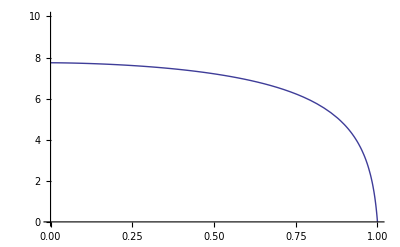

```mathematica
Plot[Re[τs1[r1x] /. do->1],{r1x,0.,1.},PlotRange->{0,10}]
```

```mathematica
sola=Solve[α^2 Fc^2  Cos[θo] Sin[θo]-αFc  2Cos[θo] Sin[θo]lth-r0x^2 (-1+μ) μ Cot[θ0] (-6 Cos[2 θ0]-10 Cos[2 τ ω]+3 (2+Cos[2 (θ0-τ ω)]+Cos[2 (θ0+τ ω)]))/16==0,α]
```

{{α→-1/(4 Fc)√Csc[θo] √Sec[θo] √(-6 r0x^2 μ Cot[θ0]+6 r0x^2 μ^2 Cot[θ0]+6 r0x^2 μ Cos[2 θ0] Cot[θ0]-6 r0x^2 μ^2 Cos[2 θ0] Cot[θ0]+10 r0x^2 μ Cos[2 τ ω] Cot[θ0]-10 r0x^2 μ^2 Cos[2 τ ω] Cot[θ0]-3 r0x^2 μ Cos[2 (θ0-τ ω)] Cot[θ0]+3 r0x^2 μ^2 Cos[2 (θ0-τ ω)] Cot[θ0]-3 r0x^2 μ Cos[2 (θ0+τ ω)] Cot[θ0]+3 r0x^2 μ^2 Cos[2 (θ0+τ ω)] Cot[θ0]+32 lth αFc Cos[θo] Sin[θo])},{α→1/(4 Fc)√Csc[θo] √Sec[θo] √(-6 r0x^2 μ Cot[θ0]+6 r0x^2 μ^2 Cot[θ0]+6 r0x^2 μ Cos[2 θ0] Cot[θ0]-6 r0x^2 μ^2 Cos[2 θ0] Cot[θ0]+10 r0x^2 μ Cos[2 τ ω] Cot[θ0]-10 r0x^2 μ^2 Cos[2 τ ω] Cot[θ0]-3 r0x^2 μ Cos[2 (θ0-τ ω)] Cot[θ0]+3 r0x^2 μ^2 Cos[2 (θ0-τ ω)] Cot[θ0]-3 r0x^2 μ Cos[2 (θ0+τ ω)] Cot[θ0]+3 r0x^2 μ^2 Cos[2 (θ0+τ ω)] Cot[θ0]+32 lth αFc Cos[θo] Sin[θo])}}

```mathematica
sola=α Fc->lth+√(lth^2+(1/8) r0x^2 (1-μ)μ( Cos[2 τ ω](5-3Cos[θ0])-6 Sin[θ0]^2)/Sin[θ0]^2 )
```

Fc α→lth+√(lth^2+1/8 r0x^2 (1-μ) μ Csc[θ0]^2 ((5-3 Cos[θ0]) Cos[2 τ ω]-6 Sin[θ0]^2))

```mathematica
(* numerical part  *)
```

```mathematica
(*  transformed Newton solution  bin BH r0x0=16.80 μ=0.5
r0x[τ]=rN[τ]*(1+μ)
radii r=:10.26, 46.3, r2=6.85,30.66 , period: 739:  sol= roxd1   *)
```

```mathematica
μ0=1/2;
m20=μ0/(1+μ0)
m10=1/(1+μ0)
mr0=m10 m20
r0=30.;
r10=r0*mr0/m10
r20=r0*mr0/m20
ω0=1/Sqrt[2 r0^3]
T0=2 Pi/ω0
ta02=2000.;
lcp0=1.1ω0( r10^2 +r20^2)
lc0=lcp0(1+μ0 I)^2
Fc0=(1-1/(2.5r0))
ecp0=(Fc0^2-1)/2
fN=(1+μ0)  (* r0-factor *)
rp0=r0
```

1/3

2/3

2/9

10.

20.

0.00430331

1460.08

2.36682

1.77512+2.36682 ⅈ

0.986667

-0.0132444

3/2

30.

```mathematica
-N1dAbt
sirpx=Solve[N1dAbt==0 /. rN1dAbt1 /. rN1dAbt2 /. rp[τ]->1/irpx ,irpx]
irp[ϵ_,lcp_]=irpx /. sirpx
rp[ϵ_,lcp_]=1/irp[ϵ,lcp]
```

1-Fc^2+lcp^2/rp[τ]^2-1/rp[τ]+rp'[τ]^2

{{irpx→(1-√(1+8 lcp^2 ϵ))/(2 lcp^2)},{irpx→(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}}

{(1-√(1+8 lcp^2 ϵ))/(2 lcp^2),(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}

{(2 lcp^2)/(1-√(1+8 lcp^2 ϵ)),(2 lcp^2)/(1+√(1+8 lcp^2 ϵ))}

```mathematica
(*  max-min value for r2 and r20 true_r0=r0x *)
```

```mathematica
rp1=rp[ecp0,lcp0][[1]]
rp2=rp[ecp0,lcp0][[2]]
r0x2=2 rp1*rp2/(rp1+rp2)
r0x0=(1+μ0)r0x2
r0x1=r0x2 μ0
ω0x=1/Sqrt[2 r0x^3]
T0x=N[2 Pi/ω0x]
(* true factors in lcp0, Fc0 *)
flcp0=lcp0/(ω0x( r0x1^2 +r0x2^2))
fFc0=1/((1-Fc0)r0x)
```

30.9099

6.8418

11.2037

16.8056

5.60185

1/(√2 √(r0x^3))

8.88577 √(r0x^3)

0.0213328 √(r0x^3)

75./r0x

```mathematica
(* total Newton radialeq, Rs=2mG/c^2, r0=rox(1+μ0) *)
CN=r0x'[τ]^2/2 +lc^2/(2 r0x[τ]^2)- 1/(2r0x[τ]) -(Fc^2-1)/2
```

1/2 (1-Fc^2)+lc^2/(2 r0x[τ]^2)-1/(2 r0x[τ])+1/2 r0x'[τ]^2

```mathematica
CN0=CN /. lc->lcp0 /. Fc->Fc0
CN0 /. r0x[τ]->rp0
```

0.0132444+2.80093/r0x[τ]^2-1/(2 r0x[τ])+1/2 r0x'[τ]^2

-0.000310082+1/2 r0x'[τ]^2

```mathematica
bcN={r0x[0.]== rp0}
solCN=NDSolve[Join[{CN0==0 },bcN],r0x,{τ,0.,ta02},PrecisionGoal->4,AccuracyGoal->4]
```

{r0x[0.]==30.}

NDSolve::mxst: Maximum number of 10000 steps reached at the point τ == 377.875.

NDSolve::mxst: Maximum number of 10000 steps reached at the point τ == 939.586.

{{r0x→InterpolatingFunction[{{0.,377.875}},<>]},{r0x→InterpolatingFunction[{{0.,939.586}},<>]}}

```mathematica
tauCN1 =solCN[[1,1,2]][[1,1,2]]
tauCN2 =solCN[[2,1,2]][[1,1,2]]
roxs1[τ_]=fN r0x[τ] /. solCN[[1]];
roxs2[τ_]=fN r0x[τ] /. solCN[[2]];
roxs10[τ_]= r0x[τ] /. solCN[[1]];
roxs20[τ_]= r0x[τ] /. solCN[[2]];
```

377.875

939.586

```mathematica
roxs1[1.]
roxs1[0.]
```

44.9617+0. ⅈ

45.+0. ⅈ

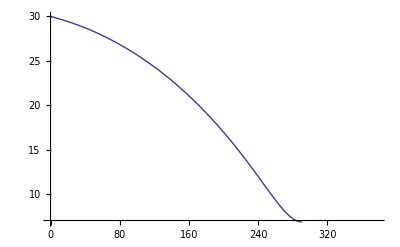

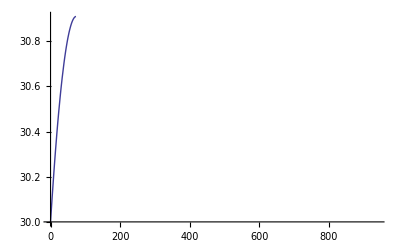

```mathematica
Plot[roxs10[τ],{τ,0,tauCN1}]
Plot[roxs20[τ],{τ,0,tauCN2}]
```

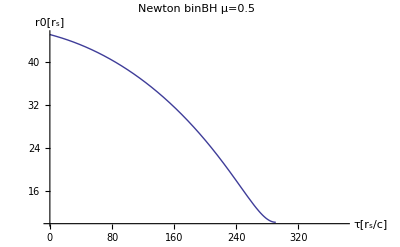

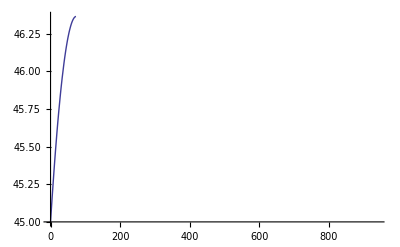

```mathematica
Plot[roxs1[τ],{τ,0,tauCN1},AxesLabel->{"τ[r_s/c]","r0[r_s]"},PlotLabel->"Newton binBH μ=0.5"]
Plot[roxs2[τ],{τ,0,tauCN2}]
```

```mathematica
(* largest and smallest radius *)
taus11=τ /. FindRoot[Re[roxs1'[τ]],{τ,290}]
r1s11=roxs1[taus11]
taus12=τ /. FindRoot[Re[roxs2'[τ]],{τ,80}]
r1s12=roxs2[taus12]
taupers=2(taus11+taus12)
```

295.746

10.2578-0.0000136884 ⅈ

79.8985

46.3662-0.000195619 ⅈ

751.289

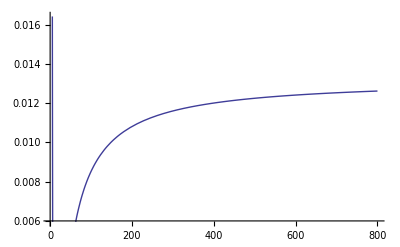

```mathematica
Plot[CN0 /.  r0x'[τ]->0  /. r0x[τ]->r0x,{r0x,1,800}]
```

```mathematica
(* derivative of Newton radialeq, Rs=2mG/c^2 *)
CNd=Simplify[D[CN,τ]/r0x'[τ]]
```

-lc^2/r0x[τ]^3+1/(2 r0x[τ]^2)+r0x''[τ]

```mathematica
CNd0=CNd /. lc->lcp0  /. Fc->Fc0
CNd0 /. r0x[τ]->rp0
```

-5.60185/r0x[τ]^3+1/(2 r0x[τ]^2)+r0x''[τ]

0.00034808+r0x''[τ]

```mathematica
(* GR:  *)
rCN1=fN r0x[τ] /. FindRoot[CN0 /.  r0x'[τ]->0,{r0x[τ],4.}]
rCN2=fN  r0x[τ] /. FindRoot[CN0 /.  r0x'[τ]->0,{r0x[τ],100.}]
```

10.2627

46.3648

```mathematica
(* GR:  *)
rCN1=fN r0x[τ] /. FindRoot[CN0 /.  r0x'[τ]->0,{r0x[τ],4.}]
rCN2=fN  r0x[τ] /. FindRoot[CN0 /.  r0x'[τ]->0,{r0x[τ],100.}]
```

10.2627

46.3648

```mathematica
dvr0=Re[roxs1'[0.]fN]
```

-0.056032

```mathematica
dvr0=Re[roxs10'[0.]]
```

-0.0249031

```mathematica
bcNd={r0x[0.]== r0 ,r0x'[0.]== dvr0}
solCNd=NDSolve[Join[{CNd0==0 },bcNd],r0x,{τ,0.,ta02},PrecisionGoal->4,AccuracyGoal->4]
```

{r0x[0.]==30.,r0x'[0.]==-0.0249031}

{{r0x→InterpolatingFunction[{{0.,2000.}},<>]}}

```mathematica
tauCNd =solCNd[[1,1,2]][[1,1,2]]
roxd10[τ_]= r0x[τ] /. solCNd[[1]];
roxd1[τ_]=fN r0x[τ] /. solCNd[[1]];
roxd10[10.]
```

2000.

29.7274

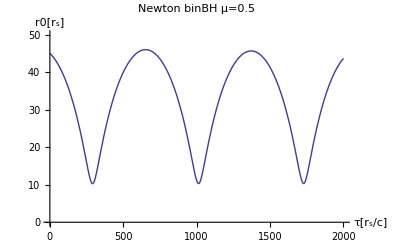

```mathematica
Plot[roxd1[τ],{τ,0,tauCNd},PlotRange->{0,50},AxesLabel->{"τ[r_s/c]","r0[r_s]"},PlotLabel->"Newton binBH μ=0.5"]
```

```mathematica
(* largest and smallest radius *)
taud11=τ /. FindRoot[roxd1'[τ],{τ,T0/5}]
r1d11=roxd1[taud11]
taud12=τ /. FindRoot[roxd1'[τ],{τ,T0/2}]
r1d12=roxd1[taud12]
Taud1=2(taud12-taud11)
Tomega0=2Pi/ω0
```

291.031

10.284

651.734

45.9733

721.406

1460.08

```mathematica
(* large radii *)
taud12=τ /. FindRoot[roxd1'[τ],{τ,T0/2}]
r1d12=roxd1[taud12]
taud22=τ /. FindRoot[roxd1'[τ],{τ,T0}]
r1d22=roxd1[taud22]
```

651.734

45.9733

1370.88

45.6322

```mathematica
(*  small radii *)
taud11=τ  /. FindMinimum[Abs[roxd1[τ]],{τ,T0/5}][[2]]
r1d11=roxd1[taud11]
taud21=τ  /. FindMinimum[Abs[roxd1[τ]],{τ,0.7T0}][[2]]
r1d21=roxd1[taud21]
```

291.031

10.284

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1013.2

10.304

```mathematica
(*  GR bin BH solution from Schwarzschild (alpha=0) r0x0=16.80 μ=0.5 α=0
radii r:7.91,46.8, radii r2:31.19,5.26  , period: 746.4 : roxdss1,   piecewise roxss *)
```

```mathematica
μ0=1/2;
m20=μ0/(1+μ0)
m10=1/(1+μ0)
mr0=m10 m20
r0=30.;
r10=r0*mr0/m10
r20=r0*mr0/m20
ω0=1/Sqrt[2 r0^3]
T0=2 Pi/ω0
ta02=2000.;
lcp0=1.1ω0( r10^2 +r20^2)
lc0=lcp0(1+μ0 I)^2
Fc0=(1-1/(2.5r0))
ecp0=(Fc0^2-1)/2
fN=(1+μ0)  (* r0-factor *)
rp0=r0 
rp01=r0(1+μ0 I)/(1+μ0 )
```

1/3

2/3

2/9

10.

20.

0.00430331

1460.08

2.36682

1.77512+2.36682 ⅈ

0.986667

-0.0132444

3/2

30.

20.+10. ⅈ

```mathematica
ω1=0.1;
ω2=0.1;
T0=2 Pi/ω0
ta01=0.;
ta02=2000.;
```

1460.08

```mathematica
lcp0=1.1ω0( r10^2 +r20^2)
lc1=lcp0(1+μ0 I)^2
Fc0=(1-1/(2.5r0))
```

2.36682

1.77512+2.36682 ⅈ

0.986667

```mathematica
-N1dAbt
sirpx=Solve[N1dAbt==0 /. rN1dAbt1 /. rN1dAbt2 /. rp[τ]->1/irpx ,irpx]
irp[ϵ_,lcp_]=irpx /. sirpx
rp[ϵ_,lcp_]=1/irp[ϵ,lcp]
```

1-Fc^2+lcp^2/rp[τ]^2-1/rp[τ]+rp'[τ]^2

{{irpx→(1-√(1+8 lcp^2 ϵ))/(2 lcp^2)},{irpx→(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}}

{(1-√(1+8 lcp^2 ϵ))/(2 lcp^2),(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}

{(2 lcp^2)/(1-√(1+8 lcp^2 ϵ)),(2 lcp^2)/(1+√(1+8 lcp^2 ϵ))}

```mathematica
(*  max-min value for r2 and r20 true_r0=r0x *)
rp1=rp[ecp0,lcp0][[1]]
rp2=rp[ecp0,lcp0][[2]]
r0x2=2 rp1*rp2/(rp1+rp2)
r0x0=(1+μ0)r0x2
r0x1=r0x2 μ0
ω0x=1/Sqrt[2 r0x^3]
T0x=N[2 Pi/ω0x]
(* true factors in lcp0, Fc0 *)
flcp0=lcp0/(ω0x( r0x1^2 +r0x2^2))
fFc0=1/((1-Fc0)r0x)
```

30.9099

6.8418

11.2037

16.8056

5.60185

1/(√2 √(r0x^3))

8.88577 √(r0x^3)

0.0213328 √(r0x^3)

75./r0x

```mathematica
N1dAbt
```

-1+Fc^2-lcp^2/rp[τ]^2+1/rp[τ]-rp'[τ]^2

```mathematica
E1dAbs
```

(-1+Fc^2) (1+ⅈ μ)^2-(lc^2 (1-(1+ⅈ μ)/r[τ]))/r[τ]^2+(1+ⅈ μ)^3/r[τ]-r'[τ]^2

```mathematica
(* total Schwarzschild radialeq, Rs=2mG/c^2 *)
CGR=E1dAbs /. r[τ]->r0x[τ] /. r'[τ]->r0x'[τ] /. μ->μ0
```

(3/4+ⅈ) (-1+Fc^2)-(lc^2 (1-(1+ⅈ/2)/r0x[τ]))/r0x[τ]^2+(1/4+(11 ⅈ)/8)/r0x[τ]-r0x'[τ]^2

```mathematica
CGR0=CGR /. lc->lc1 /. Fc->Fc0
CGR0 /. r0x[τ]->rp01
```

(-0.0198667-0.0264889 ⅈ)+((2.45081-8.40278 ⅈ) (1-(1+ⅈ/2)/r0x[τ]))/r0x[τ]^2+(1/4+(11 ⅈ)/8)/r0x[τ]-r0x'[τ]^2

(0.00765503+0.0102067 ⅈ)-r0x'[τ]^2

```mathematica
bcGR={r0x[0.]== rp01}
solCGR=NDSolve[Join[{CGR0==0 },bcGR],r0x,{τ,0.,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{r0x[0.]==20.+10. ⅈ}

NDSolve::mxst: Maximum number of 10000 steps reached at the point τ == 343.048.

{{r0x→InterpolatingFunction[{{0.,343.048}},<>]},{r0x→InterpolatingFunction[{{0.,2000.}},<>]}}

```mathematica
tauCGR1 =solCGR[[1,1,2]][[1,1,2]]
tauCGR2 =solCGR[[2,1,2]][[1,1,2]]
roxss1[τ_]=r0x[τ] /. solCGR[[1]];
roxss2[τ_]=r0x[τ] /. solCGR[[2]];
roxss20[τ_]=Re[roxss1[τ]]+Im[roxss1[τ]];
```

343.048

2000.

```mathematica
roxss1[1.]
roxss1'[1.]
roxss1[0.]
```

19.8978+9.94891 ⅈ

-0.103236-0.051618 ⅈ

20.+10. ⅈ

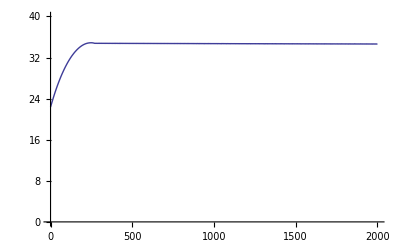

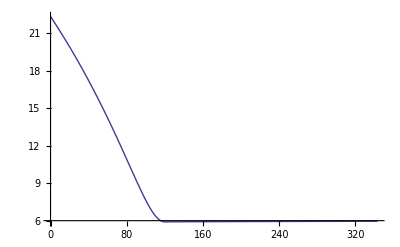

```mathematica
Plot[Abs[roxss2[τ]],{τ,0,tauCGR2},PlotRange->{0,40}]
Plot[Abs[roxss1[τ]],{τ,0,tauCGR1}]
```

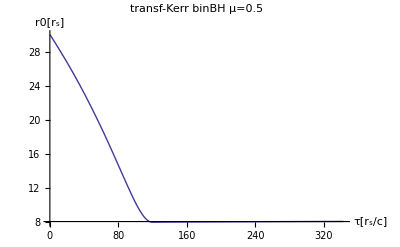

```mathematica
Plot[Re[roxss20[τ]]+Im[roxss20[τ]],{τ,0,tauCGR1},AxesLabel->{"τ[r_s/c]","r0[r_s]"},PlotLabel->"transf-Kerr binBH μ=0.5"]
```

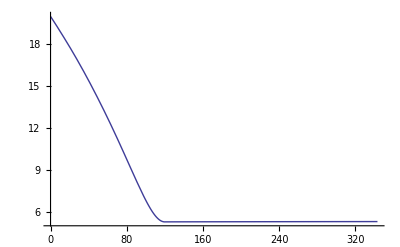

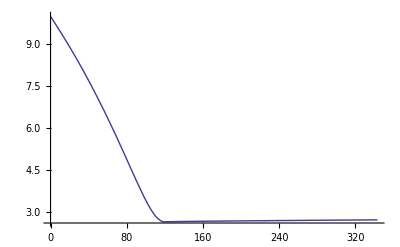

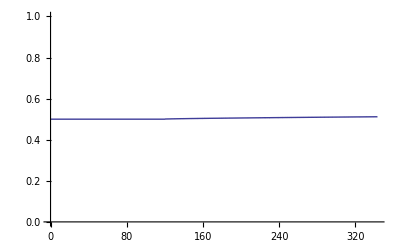

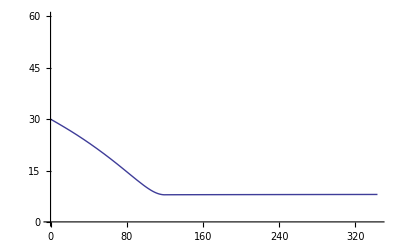

```mathematica
Plot[Re[roxss1[τ]],{τ,0,tauCGR1}]
Plot[Im[roxss1[τ]],{τ,0,tauCGR1}]
Plot[Im[roxss1[τ]]/Re[roxss1[τ]],{τ,0,tauCGR1},PlotRange->{0,1.}]
Plot[Im[roxss1[τ]]+Re[roxss1[τ]],{τ,0,tauCGR1},PlotRange->{0,60}]
```

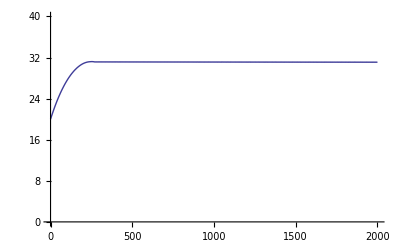

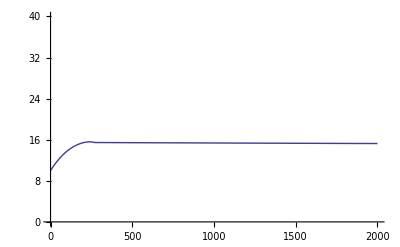

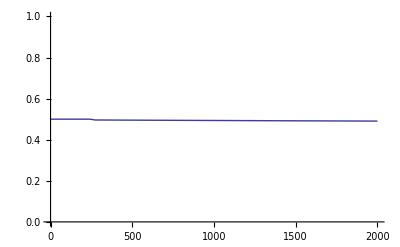

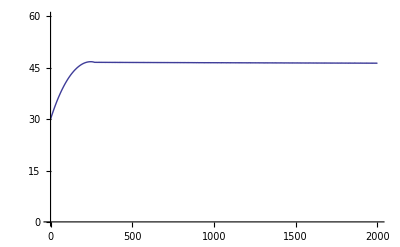

```mathematica
Plot[Re[roxss2[τ]],{τ,0,tauCGR2},PlotRange->{0,40}]
Plot[Im[roxss2[τ]],{τ,0,tauCGR2},PlotRange->{0,40}]
Plot[Im[roxss2[τ]]/Re[roxss2[τ]],{τ,0,tauCGR2},PlotRange->{0,1.}]
Plot[Im[roxss2[τ]]+Re[roxss2[τ]],{τ,0,tauCGR2},PlotRange->{0,60}]
```

```mathematica
tauds12= τ  /. FindMinimum[Re[roxss1[τ]],{τ,130}][[2]]
r1ds11=Re[roxss1[tauds12]]+Im[roxss1[tauds11]]
```

131.384

5.28132+Im[InterpolatingFunction[{{0.,343.048}},<>][tauds11]]

```mathematica
tauds11= τ  /. FindMaximum[Re[roxss2[τ]],{τ,230}][[2]]
r1ds12=Re[roxss2[tauds11]]+Im[roxss2[tauds12]]
```

252.864

45.6797

```mathematica
tauperds=2tauds12+2tauds11
```

768.496

```mathematica
tauds11
tauds12
```

252.864

131.384

```mathematica
(*  piecewise solution 2 functions 0≤τ≤ tauperds  *)
roxss[τ_,tauds11_,tauds12_,roxss2_,roxss1_]:=Block[{retval},
If[τ≤ tauds11,
retval=roxss2[τ];
];
If[τ≥  tauds11  && τ≤ 2 tauds11,
retval=roxss2[-τ+2tauds11];
];
If[τ≥  2tauds11  && τ≤ 2 tauds11+tauds12,
retval=roxss1[τ- 2tauds11];
];
If[τ≥  2tauds11+tauds12  && τ≤ 2 tauds11+2tauds12,
retval=roxss1[tauds12-τ+(2 tauds11+tauds12)];
];
Return[retval];
];
```

```mathematica
roxssp[τ_]:=roxss[τ,tauds11,tauds12,roxss2,roxss1];
```

```mathematica
(*  piecewise solution  function 0≤τ≤ 4tauperds  *)
roxss0[τ_,tauds11_,roxss2_]:=Block[{retval},
If[τ≤ tauds11,
retval=roxss2[τ];
];
If[τ≥  tauds11  && τ≤ 2 tauds11,
retval=roxss2[τ- tauds11];
];
If[τ≥  2tauds11  && τ≤ 3 tauds11,
retval=roxss2[τ- 2tauds11];
];
If[τ≥  3tauds11  && τ≤ 4 tauds11,
retval=roxss2[τ- 2tauds11];
];
Return[retval];
];
```

```mathematica
roxss1[tauds12]
roxss1[0]
```

5.28132+2.65008 ⅈ

20.+10. ⅈ

```mathematica
(* max min radii r2 *)
roxss[tauds11,tauds11,tauds12,roxss2,roxss1]
roxss[2tauds11,tauds11,tauds12,roxss2,roxss1]
roxss[2tauds11+tauds12-1,tauds11,tauds12,roxss2,roxss1]
roxss[tauperds,tauds11,tauds12,roxss2,roxss1]
```

31.2076+15.5631 ⅈ

20.+10. ⅈ

5.28232+2.65085 ⅈ

20.+10. ⅈ

31.2076+15.5631 ⅈ

28.9443+14.4721 ⅈ

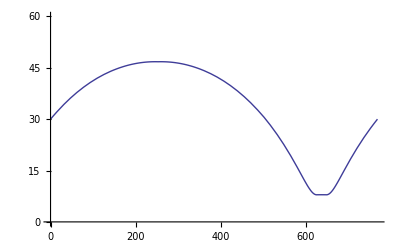

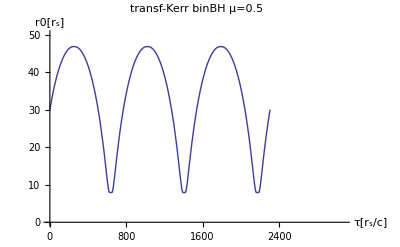

```mathematica
roxss0[tauds11,tauperds,roxssp]
roxss0[tauds12,tauperds,roxssp]
Plot[Im[roxss[τ,tauds11,tauds12,roxss2,roxss1]]+Re[roxss[τ,tauds11,tauds12,roxss2,roxss1]],{τ,0,tauperds},PlotRange->{0,60}]
Plot[Im[roxss0[τ,tauperds,roxssp]]+Re[roxss0[τ,tauperds,roxssp]],{τ,0,4tauperds},PlotRange->{0,50},AxesLabel->{"τ[r_s/c]","r0[r_s]"},PlotLabel->"transf-Kerr binBH μ=0.5"]
```

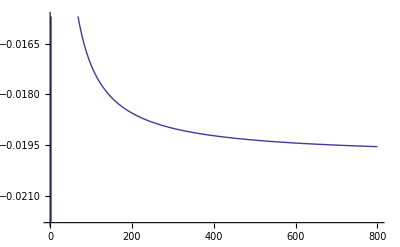

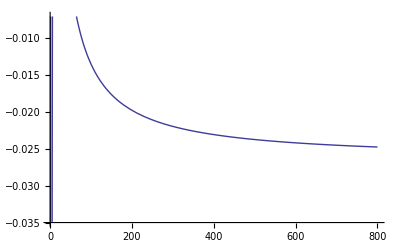

```mathematica
Plot[Re[CGR0 /.  r0x'[τ]->0  /. r0x[τ]->r0x],{r0x,1,800}]
Plot[Im[CGR0 /.  r0x'[τ]->0  /. r0x[τ]->r0x],{r0x,1,800}]
```

```mathematica
(* derivative of Newton radialeq, Rs=2mG/c^2 *)
CNd=Simplify[D[CN,τ]/r0x'[τ]]
```

-lc^2/r0x[τ]^3+1/(2 r0x[τ]^2)+r0x''[τ]

```mathematica
(* derivative of Newton radialeq, Rs=2mG/c^2: period too short because of dt/dτ=Fc/(1-1/r) *)
CGRd=8 r0x[τ]^4 Simplify[D[CGR,τ]/r0x'[τ]]
```

(-24-12 ⅈ) lc^2+16 lc^2 r0x[τ]-(2+11 ⅈ) r0x[τ]^2-16 r0x[τ]^4 r0x''[τ]

```mathematica
(* transformed derivative Newton radial: not working *)
CGRNd=CNd /. r0x[τ]->r0x[τ](1+μ0)/(1+μ0 I)  /. r0x''[τ]->r0x''[τ](1+μ0)/(1+μ0 I)
```

-((2/27+(11 ⅈ)/27) lc^2)/r0x[τ]^3+(1/6+(2 ⅈ)/9)/r0x[τ]^2+(6/5-(3 ⅈ)/5) r0x''[τ]

```mathematica
CGRd0=CGRd /. lc->lc1 /. Fc->Fc0   
CGRd0 /. r0x[τ]->rp01
```

(159.653-172.257 ⅈ)-(39.213-134.444 ⅈ) r0x[τ]-(2+11 ⅈ) r0x[τ]^2-16 r0x[τ]^4 r0x''[τ]

(1830.95-1975.5 ⅈ)+(1.12×10^6-3.84×10^6 ⅈ) r0x''[τ]

```mathematica
CGRNd0=CGRNd /. lc->lc1 /. Fc->Fc0   
CGRNd0 /. r0x[τ]->rp01
```

(3.6049+0.37605 ⅈ)/r0x[τ]^3+(1/6+(2 ⅈ)/9)/r0x[τ]^2+(6/5-(3 ⅈ)/5) r0x''[τ]

(0.000646326-0.000311214 ⅈ)+(6/5-(3 ⅈ)/5) r0x''[τ]

```mathematica
(* GR:  *)
rCGR1=r0x[τ] /. FindRoot[CGR0 /.  r0x'[τ]->0,{r0x[τ],4.}]
rCGR2=r0x[τ] /. FindRoot[CGR0 /.  r0x'[τ]->0,{r0x[τ],100.}]
```

5.27877+2.63939 ⅈ

31.1884+15.5942 ⅈ

```mathematica
rCGR1/(1+μ0 I)
rCGR2/(1+μ0 I)
```

5.27877-1.77636×10^-15 ⅈ

31.1884-1.77636×10^-15 ⅈ

```mathematica
rCGR1/Abs[1+μ0]
rCGR2/Abs[1+μ0]
```

3.51918+1.75959 ⅈ

20.7923+10.3961 ⅈ

```mathematica
rp01=r0(1+μ0 I)/(1+μ0 )
```

20.+10. ⅈ

```mathematica
dvr1=dvr0(1+μ0 I)/(1+μ0 )
dvr0
```

-0.0166021-0.00830103 ⅈ

-0.0249031

```mathematica
bcGRd={r0x[0.]== rp01,r0x'[0.]== dvr1}
solCGRd=NDSolve[Join[{CGRNd0==0 },bcGRd],r0x,{τ,0.,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{r0x[0.]==20.+10. ⅈ,r0x'[0.]==-0.0166021-0.00830103 ⅈ}

{{r0x→InterpolatingFunction[{{0.,2000.}},<>]}}

```mathematica
bcGRd={r0x[0.]== rp01,r0x'[0.]== dvr1}
solCGRd=NDSolve[Join[{CGRd0==0 },bcGRd],r0x,{τ,0.,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{r0x[0.]==20.+10. ⅈ,r0x'[0.]==-0.0166021-0.00830103 ⅈ}

{{r0x→InterpolatingFunction[{{0.,2000.}},<>]}}

```mathematica
Off[NIntegrate::nlim];
```

```mathematica
tauCGRd =solCGRd[[1,1,2]][[1,1,2]]
roxdss1[τ_]=r0x[τ] /. solCGRd[[1]];
roxdrs1[τ_]=roxdss1[τ]/(1+μ0 I)
roxdss1[100.]
roxdrs1[100.]
```

2000.

(4/5-(2 ⅈ)/5) InterpolatingFunction[{{0.,2000.}},<>][τ]

15.1132+7.55662 ⅈ

15.1132-1.77636×10^-15 ⅈ

```mathematica
toxdss1[τx_]=NIntegrate[Fc0/(1-1/(roxdrs1[τ])),{τ,0,τx},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
toxdss1[200.]  
toxdss1[400.]  
toxdss1[1000.]
```

215.156+2.98248×10^-15 ⅈ

430.31-3.38472×10^-18 ⅈ

1069.97-1.27376×10^-14 ⅈ

```mathematica
ϕ'[τ]->lc1/roxdss1[τ]^2
```

ϕ'[τ]→(1.77512+2.36682 ⅈ)/(InterpolatingFunction[{{0.,2000.}},<>][τ])^2

```mathematica
phioxdss1[τx_]=lc1/roxdss1[τx]^2
```

(1.77512+2.36682 ⅈ)/(InterpolatingFunction[{{0.,2000.}},<>][τx])^2

```mathematica
phioxdss1[τx_]:=NIntegrate[lc1/(roxdrs1[τ])^2,{τ,0,τx},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
phioxdss1[200.]
```

2.78518+3.71358 ⅈ

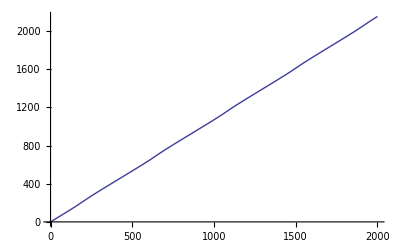

```mathematica
Plot[Re[toxdss1[τ]],{τ,0,tauCGRd}]
```

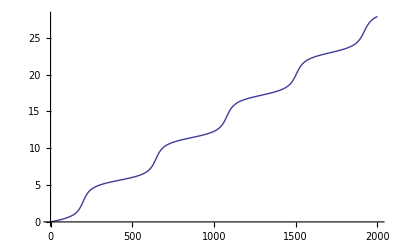

```mathematica
Plot[Re[phioxdss1[τx]],{τx,0,tauCGRd}]
```

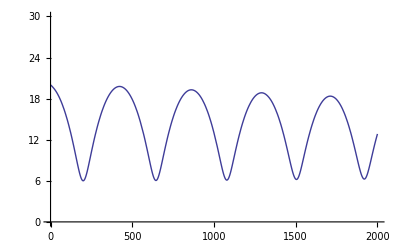

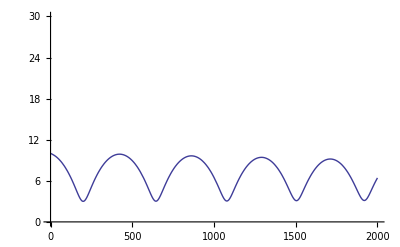

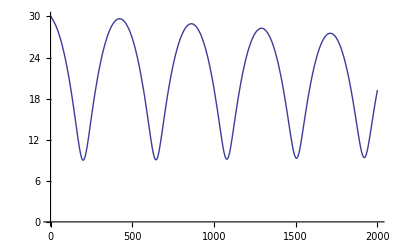

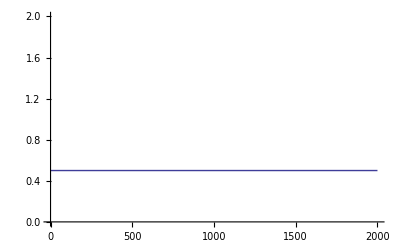

```mathematica
Plot[Re[roxdss1[τ]],{τ,0,tauCGRd},PlotRange->{0,30}]
Plot[Im[roxdss1[τ]],{τ,0,tauCGRd},PlotRange->{0,30}]
Plot[Re[roxdss1[τ]]+Im[roxdss1[τ]],{τ,0,tauCGRd},PlotRange->{0,30}]
Plot[Im[roxdss1[τ]]/Re[roxdss1[τ]],{τ,0,tauCGRd},PlotRange->{0,2}]
```

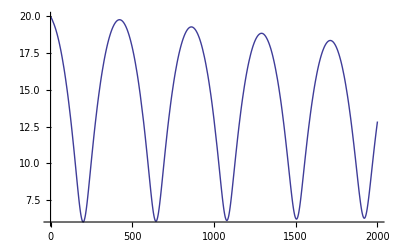

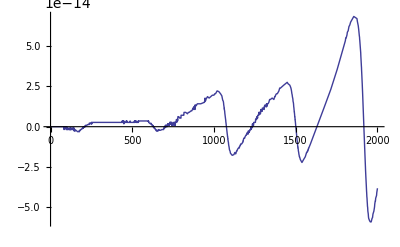

```mathematica
Plot[Re[roxdrs1[τ]],{τ,0,tauCGRd}]
Plot[Im[roxdrs1[τ]],{τ,0,tauCGRd}]
```

```mathematica
(* largest and smallest radius *)
taud11= τ  /. FindMaximum[Re[roxdss1[τ]],{τ,200}][[2]]
r1d11=Re[roxdss1[taud11]]
taud12= τ  /. FindMinimum[Re[roxdss1[τ]],{τ,400}][[2]]
r1d12=Re[roxdss1[taud12]]
Taud1=2(taud12-taud11)
Tomega0=2Pi/ω0
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

421.982

19.7778

199.685

6.00753

-444.594

1460.08

```mathematica
(* large radii *)
taud12=τ /. FindRoot[roxdss1'[τ],{τ,T0/2}]
r1d12=roxdss1[Re[taud12]]
taud22=τ /. FindRoot[roxdss1'[τ],{τ,T0}]
r1d22=roxdss1[Re[taud22]]
```

861.407+2.32634×10^-13 ⅈ

19.2876+9.64378 ⅈ

1711.31+1.06406×10^-12 ⅈ

18.3629+9.18147 ⅈ

```mathematica
(*  small radii *)
taud11=τ  /. FindMinimum[Abs[roxdss1[τ]],{τ,T0/4}][[2]]
r1d11=roxdss1[Re[taud11]]
taud21=τ  /. FindMinimum[Abs[roxdss1[τ]],{τ,0.5 T0}][[2]]
r1d21=roxdss1[Re[taud21]]
taud31=τ  /. FindMinimum[Abs[roxdss1[τ]],{τ, 0.8 T0}][[2]]
r1d31=roxdss1[Re[taud21]]
```

InterpolatingFunction::dmval: Input value {-248.731} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

199.685

6.00753+3.00376 ⅈ

644.891

6.04995+3.02498 ⅈ

1078.5

6.04995+3.02498 ⅈ

```mathematica
(*    energy  *)
```

```mathematica
(* energy with mr in Newton  *)
Etot[rx_,drx_,dphi_]:=mr0(drx^2/2+dphi^2rx^2(1-1/rx)/2-1/(2 rx));
Ekin[rx_,drx_,dphi_]:=mr0(drx^2/2+dphi^2rx^2(1-1/rx)/2);
```

```mathematica
Off[NIntegrate::nlim];
```

```mathematica
r0db1[τx_]=roxdss1[τx];
dr0db1[τx_]=roxdss1'[τx];
phidb1[τx_]=phioxdss1[τx];
```

```mathematica
(* sum of m1-energy and m2-energy in Newton  *)
Etotc[rx_,drx_,dphi_]:=(m10*Re[drx]^2/2+m20*Im[drx]^2/2+Abs[dphi]^2(Re[rx]^2+Im[rx]^2)(1-1/(Re[rx]+Im[rx]))/2-1/(2 (Re[rx]+Im[rx])) );
Ekinc[rx_,drx_,dphi_]:=(m10*Re[drx]^2/2+m20*Im[drx]^2/2+Abs[dphi]^2(Re[rx]^2+Im[rx]^2)(1-1/(Re[rx]+Im[rx]))/2);
```

```mathematica
Etot[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud11
Etot[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud21
Etot[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud31
```

0.000928723+0.0321028 ⅈ

0.000843728+0.0317211 ⅈ

0.000737723+0.0312437 ⅈ

```mathematica
Etotc[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud11
Etotc[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud21
Etotc[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud31
```

0.0792724

0.0778945

0.0761746

```mathematica
Ekinc[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud11
Ekinc[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud21
Ekinc[r0db1[τx],dr0db1[τx],Abs[phidb1'[τx]]] /. τx->taud31
```

0.134758

0.132991

0.130782

```mathematica
(* Einstein power formula  *)
Pgr[r0x_]:=(2/5)mr0^2/r0x^5;
IPgr[r0x_]:=(2/25)mr0^2/r0x^4;
```

```mathematica
(* instantaneous kin.power in mr *)
Pradl[ τx_,dtau_]:=(Ekin[r0db1[ τx+dtau],dr0db1[ τx+dtau],Abs[phidb1'[ τx+dtau]]]-Ekin[r0db1[ τx],dr0db1[ τx],Abs[phidb1'[ τx]]])/dtau;
```

```mathematica
(* instantaneous kin.power in m1,m2 *)
Pradc[ τx_,dtau_]:=(Ekinc[r0db1[ τx+dtau],r0db1'[ τx+dtau],phidb1'[ τx+dtau]]-Ekinc[r0db1[ τx],r0db1'[ τx],phidb1'[ τx]])/dtau;
```

```mathematica
(* instantaneous total power in mr *)
Pradt[ τx_,dtau_]:=(Etot[r0db1[ τx+dtau],dr0db1[ τx+dtau],Abs[phidb1'[ τx+dtau]]]-Etot[r0db1[ τx],dr0db1[ τx],Abs[phidb1'[ τx]]])/dtau;
```

```mathematica
(* instantaneous total power in m1,m2 *)
Pradct[ τx_,dtau_]:=(Etotc[r0db1[ τx+dtau],r0db1'[ τx+dtau],phidb1'[ τx+dtau]]-Etotc[r0db1[ τx],r0db1'[ τx],phidb1'[ τx]])/dtau;
```

```mathematica
Pradl[taud11,0.1]
Pradl[taud21,0.1]
Pradl[taud31,0.1]
```

-9.64816×10^-7-1.7875×10^-6 ⅈ

-9.26425×10^-7-1.71057×10^-6 ⅈ

-8.75207×10^-7-1.60832×10^-6 ⅈ

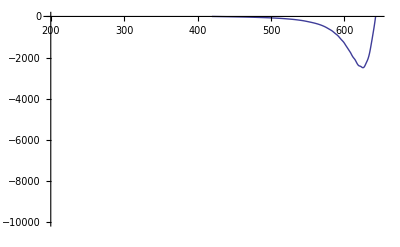

```mathematica
Plot[Pradc[τ,5.]1. 10^6,{τ,taud11,taud21},PlotRange->{-10000,0}]
```

```mathematica
(*  perihelion rotation *)
Abs[phidb1[taud11]]
Abs[phidb1[taud21]]
Abs[phidb1[taud31]]
dphidber1=Abs[phidb1[taud21]]-Abs[phidb1[taud11]]-2Pi
dphidber2=Abs[phidb1[taud31]]-Abs[phidb1[taud21]]-2Pi
```

4.61616

14.247

23.8551

3.34766

3.32488

```mathematica
(*  GR bin BHsolution from Schwarzschild (alpha=0)  r0x0=16.80 μ=0.5 piecewise roxsp, interpol roxsi,  fit roxsf  *)
```

```mathematica
μ0=1/2;
m20=μ0/(1+μ0)
m10=1/(1+μ0)
mr0=m10 m20
r0=30.;
r10=r0*mr0/m10
r20=r0*mr0/m20
ω0=1/Sqrt[2 r0^3]
(* spin omega1 omega2 *)
ω1=0.1;
ω2=0.1;
T0=2 Pi/ω0
ta01=0.;
ta02=800.;
```

1/3

2/3

2/9

10.

20.

0.00430331

1460.08

```mathematica
lcp0=1.1ω0( r10^2 +r20^2)
lc1=lcp0(1+μ0 I)^2
Fc0=(1-1/(2.5r0))
rp01=r0(1+μ0 I)/(1+μ0 )
(*  default-alpha orbit *)
αo0=(2/3)ω0 r0^2  mr0;
(* imaginary orbit alpha from Pgrav *)
αo0= (8Pi/(5Fc0 r0)) μ0/((1+μ0)^7 (3+8μ0 I-4μ0^2))
(* real alfa spin from m1 m2 *)
αs0=(2/(3(1+μ0)^2))(ω1+ω2 μ0^2)
alpha0=αs0+αo0
```

2.36682

1.77512+2.36682 ⅈ

0.986667

20.+10. ⅈ

0.000496946-0.000993892 ⅈ

0.037037

0.037534-0.000993892 ⅈ

```mathematica
vi={t,r1,th,phi}
```

{t,r1,th,phi}

```mathematica
Mgijd
```

{{1-rs/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)),0,0,(alpha1 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2))},{0,(-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2)/((1+ⅈ fm)^2 (alpha1^2-rs/(1+ⅈ fm)+rs^2/(1+ⅈ fm)^2)),0,0},{0,0,-rs^2/(1+ⅈ fm)^2-alpha1^2 Cos[th]^2,0},{(alpha1 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)),0,0,-Sin[th]^2 (alpha1^2+rs^2/(1+ⅈ fm)^2+(alpha1^2 rs Sin[th]^2)/((1+ⅈ fm) (rs^2/(1+ⅈ fm)^2+alpha1^2 Cos[th]^2)))}}

```mathematica
Mgijd1=Mgijd /. rs-> r1  /. fm->μ0
```

{{1-((4/5-(2 ⅈ)/5) r1)/((12/25-(16 ⅈ)/25) r1^2+alpha1^2 Cos[th]^2),0,0,((4/5-(2 ⅈ)/5) alpha1 r1 Sin[th]^2)/((12/25-(16 ⅈ)/25) r1^2+alpha1^2 Cos[th]^2)},{0,((12/25-(16 ⅈ)/25) ((-12/25+(16 ⅈ)/25) r1^2-alpha1^2 Cos[th]^2))/(alpha1^2-(4/5-(2 ⅈ)/5) r1+(12/25-(16 ⅈ)/25) r1^2),0,0},{0,0,(-12/25+(16 ⅈ)/25) r1^2-alpha1^2 Cos[th]^2,0},{((4/5-(2 ⅈ)/5) alpha1 r1 Sin[th]^2)/((12/25-(16 ⅈ)/25) r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+(12/25-(16 ⅈ)/25) r1^2+((4/5-(2 ⅈ)/5) alpha1^2 r1 Sin[th]^2)/((12/25-(16 ⅈ)/25) r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
Mgijs1 =Simplify[Mgijd /. rs-> r1  /. fm->μ0  /. alpha1->0]
```

{{1-(1+ⅈ/2)/r1,0,0,0},{0,((24-32 ⅈ) r1)/((50+25 ⅈ)-50 r1),0,0},{0,0,(-12/25+(16 ⅈ)/25) r1^2,0},{0,0,0,(-12/25+(16 ⅈ)/25) r1^2 Sin[th]^2}}

```mathematica
Mgijk
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,(-r1^2-alpha1^2 Cos[th]^2)/(alpha1^2-r1+r1^2),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (alpha1^2+r1^2+(alpha1^2 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))}}

```mathematica
Mgijk1=
{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,-(1/(1-r1/(r1^2+alpha1^2 Cos[th]^2)+(alpha1^2 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2))),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2(r1^2+alpha1^2 Cos[th]^2+alpha1^2 (1+r1/(r1^2+alpha1^2 Cos[th]^2)) Sin[th]^2)}}
```

{{1-r1/(r1^2+alpha1^2 Cos[th]^2),0,0,(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)},{0,-1/(1-r1/(r1^2+alpha1^2 Cos[th]^2)+(alpha1^2 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2)),0,0},{0,0,-r1^2-alpha1^2 Cos[th]^2,0},{(alpha1 r1 Sin[th]^2)/(r1^2+alpha1^2 Cos[th]^2),0,0,-Sin[th]^2 (r1^2+alpha1^2 Cos[th]^2+alpha1^2 (1+r1/(r1^2+alpha1^2 Cos[th]^2)) Sin[th]^2)}}

```mathematica
iMgijs=Inverse[Mgijs1]
```

{{-((14976/625+(5632 ⅈ)/625) r1^5 Sin[th]^2)/(((50+25 ⅈ)-50 r1) (((2432/125+(2624 ⅈ)/125) r1^4 Sin[th]^2)/((50+25 ⅈ)-50 r1)-((14976/625+(5632 ⅈ)/625) r1^5 Sin[th]^2)/((50+25 ⅈ)-50 r1))),0,0,0},{0,((-16/125+(88 ⅈ)/125) r1^3 Sin[th]^2-(112/625+(384 ⅈ)/625) r1^4 Sin[th]^2)/(((2432/125+(2624 ⅈ)/125) r1^4 Sin[th]^2)/((50+25 ⅈ)-50 r1)-((14976/625+(5632 ⅈ)/625) r1^5 Sin[th]^2)/((50+25 ⅈ)-50 r1)),0,0},{0,0,(((32/5-(176 ⅈ)/5) r1^2 Sin[th]^2)/((50+25 ⅈ)-50 r1)+((224/25+(768 ⅈ)/25) r1^3 Sin[th]^2)/((50+25 ⅈ)-50 r1))/(((2432/125+(2624 ⅈ)/125) r1^4 Sin[th]^2)/((50+25 ⅈ)-50 r1)-((14976/625+(5632 ⅈ)/625) r1^5 Sin[th]^2)/((50+25 ⅈ)-50 r1)),0},{0,0,0,(((32/5-(176 ⅈ)/5) r1^2)/((50+25 ⅈ)-50 r1)+((224/25+(768 ⅈ)/25) r1^3)/((50+25 ⅈ)-50 r1))/(((2432/125+(2624 ⅈ)/125) r1^4 Sin[th]^2)/((50+25 ⅈ)-50 r1)-((14976/625+(5632 ⅈ)/625) r1^5 Sin[th]^2)/((50+25 ⅈ)-50 r1))}}

```mathematica
iMgijk=Simplify[Inverse[Mgijd1]]
```

{{((6+8 ⅈ) alpha1^2 ((3+4 ⅈ) alpha1^2+4 r1^2) Cos[th]^2+4 r1 ((6+8 ⅈ) alpha1^2 r1+8 r1^3+(2+11 ⅈ) alpha1^2 Sin[th]^2))/(((3+4 ⅈ) alpha1^2+2 r1 ((-2-ⅈ)+2 r1)) ((3+4 ⅈ) alpha1^2+8 r1^2+(3+4 ⅈ) alpha1^2 Cos[2 th])),0,0,((8+44 ⅈ) alpha1 r1)/(((3+4 ⅈ) alpha1^2+2 r1 ((-2-ⅈ)+2 r1)) ((3+4 ⅈ) alpha1^2+8 r1^2+(3+4 ⅈ) alpha1^2 Cos[2 th]))},{0,-((3/4+ⅈ) ((3+4 ⅈ) alpha1^2+2 r1 ((-2-ⅈ)+2 r1)))/(4 r1^2+(3+4 ⅈ) alpha1^2 Cos[th]^2),0,0},{0,0,-(3+4 ⅈ)/(4 r1^2+(3+4 ⅈ) alpha1^2 Cos[th]^2),0},{((8+44 ⅈ) alpha1 r1)/(((3+4 ⅈ) alpha1^2+2 r1 ((-2-ⅈ)+2 r1)) ((3+4 ⅈ) alpha1^2+8 r1^2+(3+4 ⅈ) alpha1^2 Cos[2 th])),0,0,-((6+8 ⅈ) (2 r1 ((-2-ⅈ)+2 r1)+(3+4 ⅈ) alpha1^2 Cos[th]^2) Csc[th]^2)/(((3+4 ⅈ) alpha1^2+2 r1 ((-2-ⅈ)+2 r1)) ((3+4 ⅈ) alpha1^2+8 r1^2+(3+4 ⅈ) alpha1^2 Cos[2 th]))}}

```mathematica
Gijkmat=Table[0.,{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
Gijkkat=Table[0.,{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
i1l={1,2,3,4};
i2l={1,2,3,4};
i3l={1,2,3,4};
```

```mathematica
tim1=TimeUsed[];
For[i1x=1,i1x≤Length[i1l],i1x++,
For[i2x=1,i2x≤Length[i2l],i2x++,
For[i3x=1,i3x≤Length[i3l],i3x++,
i=i1l[[i1x]];
j=i2l[[i2x]];
k=i3l[[i3x]];
Gijkmat[[i,j,k]] =Simplify[(1/2)Sum[iMgijs[[k,l]]*(D[Mgijs1[[l,i]],vi[[j]]]
+D[Mgijs1[[l,j]],vi[[i]]]-D[Mgijs1[[i,j]],vi[[l]]]),{l,1,4}]];
];
];
];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.015

```mathematica
Gijkmat
```

{{{0,((7-24 ⅈ)+(4+22 ⅈ) r1)/(32 r1^3),0,0},{-(2+ⅈ)/((4+2 ⅈ) r1-4 r1^2),0,0,0},{0,0,0,0},{0,0,0,0}},{{-(2+ⅈ)/((4+2 ⅈ) r1-4 r1^2),0,0,0},{0,(2+ⅈ)/((4+2 ⅈ) r1-4 r1^2),0,0},{0,0,1/r1,0},{0,0,0,1/r1}},{{0,0,0,0},{0,0,1/r1,0},{0,(1+ⅈ/2)-r1,0,0},{0,0,0,Cot[th]}},{{0,0,0,0},{0,0,0,1/r1},{0,0,0,Cot[th]},{0,-1/2 ((-2-ⅈ)+2 r1) Sin[th]^2,-Cos[th] Sin[th],0}}}

```mathematica
i1l={1,2,3,4};
i2l={1,2,3,4};
i3l={1,2,3,4};
```

```mathematica
tim1=TimeUsed[];
For[i1x=1,i1x≤Length[i1l],i1x++,
For[i2x=1,i2x≤Length[i2l],i2x++,
For[i3x=1,i3x≤Length[i3l],i3x++,
i=i1l[[i1x]];
j=i2l[[i2x]];
k=i3l[[i3x]];
Gijkkat[[i,j,k]] =Simplify[(1/2)Sum[iMgijk[[k,l]]*(D[Mgijd1[[l,i]],vi[[j]]]
+D[Mgijd1[[l,j]],vi[[i]]]-D[Mgijd1[[i,j]],vi[[l]]]),{l,1,4}]];
];
];
];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.797

```mathematica
SeedRandom[4711];
rr1th={r1->RandomReal[{1.2,5.}],th->RandomReal[{0.1,Pi-0.1}]};
Gijkmat /. rr1th
Gijkkat /. alpha1->0 /. rr1th
```

{{{0,0.00987782+0.0285172 ⅈ,0,0},{0.0329779+0.0234062 ⅈ,0,0,0},{0,0,0,0},{0,0,0,0}},{{0.0329779+0.0234062 ⅈ,0,0,0},{0,-0.0329779-0.0234062 ⅈ,0,0},{0,0,0.236423,0},{0,0,0,0.236423}},{{0,0,0,0},{0,0,0.236423,0},{0,-3.2297+0.5 ⅈ,0,0},{0,0,0,0.0199846}},{{0,0,0,0},{0,0,0,0.236423},{0,0,0,0.0199846},{0,-3.22841+0.4998 ⅈ,-0.0199766,0}}}

{{{0,0.00987782+0.0285172 ⅈ,0,0},{0.0329779+0.0234062 ⅈ,0,0,0},{0,0,0,0},{0,0,0,0}},{{0.0329779+0.0234062 ⅈ,0,0,0},{0,-0.0329779-0.0234062 ⅈ,0,0},{0,0,0.236423,0},{0,0,0,0.236423}},{{0,0,0,0},{0,0,0.236423,0},{0,-3.2297+0.5 ⅈ,0,0},{0,0,0,0.0199846}},{{0,0,0,0},{0,0,0,0.236423},{0,0,0,0.0199846},{0,-3.22841+0.4998 ⅈ,-0.0199766,0}}}

```mathematica
Gijkkat1=Simplify[Gijkkat,TimeConstraint->{0.1,300}];
```

```mathematica
vit={tt[tau],r1t[tau],tht[tau],phit[tau]}
```

{tt[tau],r1t[tau],tht[tau],phit[tau]}

```mathematica
r01e=1.05;
r02e=150.;
```

```mathematica
phitn0=N[1/Sqrt[2 r02e^3]]
Tphitn0=2Pi/phitn0
```

0.0003849

16324.2

```mathematica
(* Schwarzschild Ekin *)
E1dAbs
```

(-1+Fc^2) (1+ⅈ μ)^2-(lc^2 (1-(1+ⅈ μ)/r[τ]))/r[τ]^2+(1+ⅈ μ)^3/r[τ]-r'[τ]^2

```mathematica
(* total Schwarzschild radialeq, Rs=2mG/c^2 *)
CGR=E1dAbs /. r[τ]->r0x[τ] /. r'[τ]->r0x'[τ] /. μ->μ0
```

(3/4+ⅈ) (-1+Fc^2)-(lc^2 (1-(1+ⅈ/2)/r0x[τ]))/r0x[τ]^2+(1/4+(11 ⅈ)/8)/r0x[τ]-r0x'[τ]^2

```mathematica
(* total Schwarzschild radialeq, Rs=2mG/c^2 *)
CGR=E1dAbs /. r[τ]->r0x[τ] /. r'[τ]->r0x'[τ] /. μ->μ0
```

(3/4+ⅈ) (-1+Fc^2)-(lc^2 (1-(1+ⅈ/2)/r0x[τ]))/r0x[τ]^2+(1/4+(11 ⅈ)/8)/r0x[τ]-r0x'[τ]^2

```mathematica
CGR0=CGR /. lc->lc1 /. Fc->Fc0
CGR0 /. r0x[τ]->rp01
```

(-0.0198667-0.0264889 ⅈ)+((2.45081-8.40278 ⅈ) (1-(1+ⅈ/2)/r0x[τ]))/r0x[τ]^2+(1/4+(11 ⅈ)/8)/r0x[τ]-r0x'[τ]^2

(0.00765503+0.0102067 ⅈ)-r0x'[τ]^2

```mathematica
bcGR={r0x[0.]== rp01}
solCGR=NDSolve[Join[{CGR0==0 },bcGR],r0x,{τ,0.,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{r0x[0.]==20.+10. ⅈ}

NDSolve::mxst: Maximum number of 10000 steps reached at the point τ == 340.721.

{{r0x→InterpolatingFunction[{{0.,340.721}},<>]},{r0x→InterpolatingFunction[{{0.,800.}},<>]}}

```mathematica
tauCGR1 =solCGR[[2,1,2]][[1,1,2]]
tauCGR2 =solCGR[[1,1,2]][[1,1,2]]
roxss1[τ_]=r0x[τ] /. solCGR[[2]];
roxss2[τ_]=r0x[τ] /. solCGR[[1]];
roxss20[τ_]=Re[roxss2[τ]]+Im[roxss2[τ]];
```

800.

340.721

```mathematica
r1p=roxss1[tauCGR1 ]
r1n=roxss2[tauCGR2 ]
```

31.1292+15.3833 ⅈ

5.30127+2.71269 ⅈ

```mathematica
roxss1[1.]
roxss1'[1.]
roxss1[0.]
```

20.1+10.05 ⅈ

0.0989793+0.0494896 ⅈ

20.+10. ⅈ

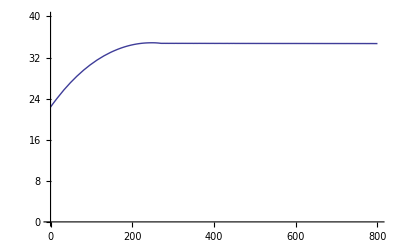

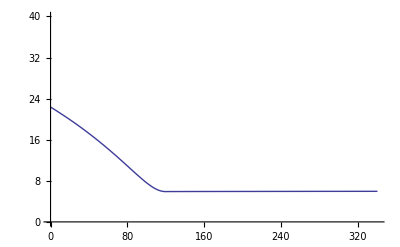

```mathematica
Plot[Abs[roxss1[τ]],{τ,0,tauCGR1},PlotRange->{0,40}]
Plot[Abs[roxss2[τ]],{τ,0,tauCGR2},PlotRange->{0,40}]
```

```mathematica
r1ts1[τ_]=roxss1[τ]
r1ts2[τ_]=roxss2[τ]
```

InterpolatingFunction[{{0.,800.}},<>][τ]

InterpolatingFunction[{{0.,340.721}},<>][τ]

```mathematica
stt={tt'[tau]-> Fc/(1-1/r1t[tau])}  /. Fc->Fc0
```

{tt'[tau]→0.986667/(1-1/r1t[tau])}

```mathematica
sphit={phit'[tau]-> lc/r1t[tau]^2} /. lc->lc1
```

{phit'[tau]→(1.77512+2.36682 ⅈ)/r1t[tau]^2}

```mathematica
stht={tht[tau]-> Pi/2,tht'[tau]->0,tht''[tau]->0};
```

```mathematica
dtts1[tau_]=ValList[stt][[1]] /.  r1t[tau]-> roxss1[tau]
```

0.986667/(1-1/(InterpolatingFunction[{{0.,800.}},<>][tau]))

```mathematica
tts1[tau_]=NIntegrate[dtts1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
tts1[20.]
```

20.509-0.407307 ⅈ

```mathematica
dphits1[tau_]=ValList[sphit][[1]] /.  r1t[tau]-> roxss1[tau]
```

(1.77512+2.36682 ⅈ)/(InterpolatingFunction[{{0.,800.}},<>][tau])^2

```mathematica
phits1[tau_]=NIntegrate[dphits1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
phits1[20.]
```

0.108005-1.23083×10^-17 ⅈ

```mathematica
thts1[tau_]=Pi/2;
```

```mathematica
r1p
r1n
```

31.1292+15.3833 ⅈ

5.30127+2.71269 ⅈ

```mathematica
tau1p=tau /. FindRoot[Re[r1ts1[tau]-r1p],{tau,170.}]
tau1n=tau /. FindRoot[Re[r1ts2[tau]-r1n],{tau,100.}]
```

227.059

117.708

```mathematica
tau1p=221.5259887176928
```

221.526

```mathematica
tau1n=116.70451987654579
```

116.705

```mathematica
(*  piecewise solution 2 functions 0≤τ≤ tauper=2(tau1p+tau1n)  *)
roxss[τ_,tau1p_,tau1n_,roxss1_Symbol,roxss2_Symbol]:=Block[{retval},
If[τ≤ tau1p,
retval=roxss1[τ];
];
If[τ≥  tau1p  && τ≤ 2 tau1p,
retval=roxss1[-τ+2tau1p];
];
If[τ≥  2tau1p  && τ≤ 2 tau1p+tau1n,
retval=roxss2[τ- 2tau1p];
];
If[τ≥  2tau1p+tau1n  && τ≤ 2 tau1p+2tau1n,
retval=roxss2[tau1n-τ+(2 tau1p+tau1n)];
];
Return[retval];
];
droxss[τ_,tau1p_,tau1n_,roxss1_Symbol,roxss2_Symbol]:=Block[{retval},
If[τ≤ tau1p,
retval=roxss1'[τ];
];
If[τ≥  tau1p  && τ≤ 2 tau1p,
retval=-roxss1'[-τ+2tau1p];
];
If[τ≥  2tau1p  && τ≤ 2 tau1p+tau1n,
retval=roxss2'[τ- 2tau1p];
];
If[τ≥  2tau1p+tau1n  && τ≤ 2 tau1p+2tau1n,
retval=-roxss2'[tau1n-τ+(2 tau1p+tau1n)];
];
Return[retval];
];
```

```mathematica
(*  piecewise solution 2 functions 0≤τ≤ tauper=2(tau1p+tau1n)  *)
roxss[τ_,tau1p_,tau1n_,roxss1_Symbol,roxss2_Symbol]:=Block[{retval},
retval=roxss1[τ]PosQ[tau1p-τ]+roxss1[-τ+2tau1p]PosQ[τ-tau1p]PosQ[2 tau1p-τ]+roxss2[τ- 2tau1p]PosQ[τ-2 tau1p]PosQ[ 2 tau1p+tau1n-τ]+roxss2[tau1n-τ+(2 tau1p+tau1n)]PosQ[τ- (2tau1p+tau1n) ]PosQ[2 tau1p+2tau1n-τ];
Return[retval];
];
droxss[τ_,tau1p_,tau1n_,roxss1_Symbol,roxss2_Symbol]:=Block[{retval},
retval=roxss1'[τ]PosQ[tau1p-τ]-roxss1'[-τ+2tau1p]PosQ[τ-tau1p]PosQ[2 tau1p-τ]+roxss2'[τ- 2tau1p]PosQ[τ-2 tau1p]PosQ[ 2 tau1p+tau1n-τ]-roxss2'[tau1n-τ+(2 tau1p+tau1n)]PosQ[τ- (2tau1p+tau1n) ]PosQ[2 tau1p+2tau1n-τ];
Return[retval];
];
```

```mathematica
roxss[tau1p,tau1p+30,tau1n+10,roxss1,roxss2]
roxss[tau,tau1p+30,tau1n+10,roxss1,roxss2] /. tau->tau1p
droxss[tau,tau1p+30,tau1n+10,roxss1,roxss2] /. tau->tau1p
```

InterpolatingFunction::dmval: Input value {-281.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {534.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

31.0889+15.5445 ⅈ

InterpolatingFunction::dmval: Input value {534.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-281.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

31.0889+15.5445 ⅈ

InterpolatingFunction::dmval: Input value {534.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-281.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.00821403+0.00410702 ⅈ

InterpolatingFunction::dmval: Input value {-503.037} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.446} lies outside the range of data in the interpolating function. Extrapolation will be used.

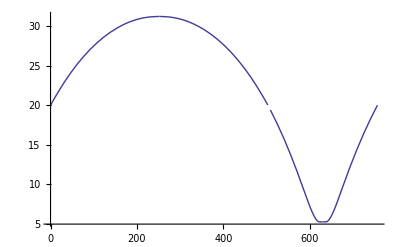

InterpolatingFunction::dmval: Input value {-503.037} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.446} lies outside the range of data in the interpolating function. Extrapolation will be used.

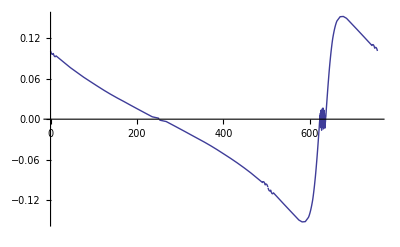

InterpolatingFunction::dmval: Input value {-503.037} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.446} lies outside the range of data in the interpolating function. Extrapolation will be used.

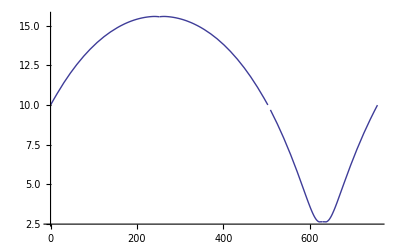

```mathematica
Plot[Re[roxss[tau,tau1p+30,tau1n+10,roxss1,roxss2]],{tau,0,2(tau1p+tau1n+40)}]
Plot[Re[droxss[tau,tau1p+30,tau1n+10,roxss1,roxss2]],{tau,0,2(tau1p+tau1n+40)}]
Plot[Im[roxss[tau,tau1p+30,tau1n+10,roxss1,roxss2]],{tau,0,2(tau1p+tau1n+40)}]
```

```mathematica
(*  piecewise solution  function 0≤τ≤ 4 tauper  *)
roxss0[τ_,tauds11_,roxss1_]:=Block[{retval},
If[τ≤ tauds11,
retval=roxss1[τ];
];
If[τ≥  tauds11  && τ≤ 2 tauds11,
retval=roxss1[τ- tauds11];
];
If[τ≥  2tauds11  && τ≤ 3 tauds11,
retval=roxss1[τ- 2tauds11];
];
If[τ≥  3tauds11  && τ≤ 4 tauds11,
retval=roxss1[τ- 3tauds11];
];
Return[retval];
];
droxss0[τ_,tauds11_,droxss1_]:=Block[{retval},
If[τ≤ tauds11,
retval=droxss1[τ];
];
If[τ≥  tauds11  && τ≤ 2 tauds11,
retval=droxss1[τ- tauds11];
];
If[τ≥  2tauds11  && τ≤ 3 tauds11,
retval=droxss1[τ- 2tauds11];
];
If[τ≥  3tauds11  && τ≤ 4 tauds11,
retval=droxss1[τ- 3tauds11];
];
Return[retval];
];
```

```mathematica
(*  piecewise solution  function 0≤τ≤ 4 tauper  *)
roxss0[τ_,tauds11_,roxss1_]:=Block[{retval},
retval=roxss1[τ]PosQ[ tauds11-τ]+roxss1[τ- tauds11]PosQ[τ-tauds11]PosQ[2tauds11-τ]+roxss1[τ- 2tauds11]PosQ[τ-2tauds11]PosQ[3tauds11-τ]+roxss1[τ- 3tauds11]PosQ[τ-3tauds11]PosQ[4tauds11-τ];
Return[retval];
];
droxss0[τ_,tauds11_,droxss1_]:=Block[{retval},
retval=droxss1[τ]PosQ[ tauds11-τ]+droxss1[τ- tauds11]PosQ[τ-tauds11]PosQ[2tauds11-τ]+droxss1[τ- 2tauds11]PosQ[τ-2tauds11]PosQ[3tauds11-τ]+droxss1[τ- 3tauds11]PosQ[τ-3tauds11]PosQ[4tauds11-τ];
Return[retval];
];
```

```mathematica
roxssp[tau_]:=roxss[tau,tau1p+30,tau1n+10,roxss1,roxss2];
droxssp[tau_]:=droxss[tau,tau1p+30,tau1n+10,roxss1,roxss2];
```

```mathematica
tauper=2(tau1p+tau1n+40);
```

InterpolatingFunction::dmval: Input value {-502.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

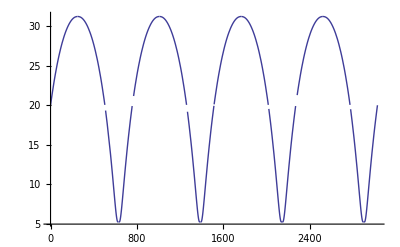

InterpolatingFunction::dmval: Input value {-502.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

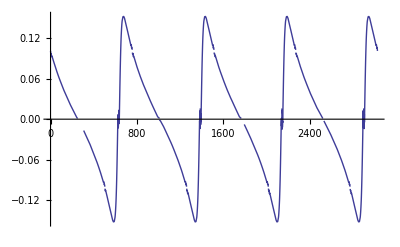

```mathematica
Plot[Re[roxss0[tau,tauper,roxssp]],{tau,0,4tauper}]
Plot[Re[droxss0[tau,tauper,droxssp]],{tau,0,4tauper}]
```

```mathematica
(* solution Schwarzschild tau≤ 4 tauper  *)
roxsp[tau_]:=roxss0[tau,tauper,roxssp];
droxsp[tau_]:=droxss0[tau,tauper,droxssp];
```

```mathematica
Plot[Re[roxsp[tau]],{tau,0,4tauper}]
Plot[Re[droxsp[tau]],{tau,0,4tauper}]
```

InterpolatingFunction::dmval: Input value {-502.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {-502.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.399} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tau1p+30
tau1n+10
tauper/2
tauper/2+tau1n+40
```

251.526

126.705

378.231

534.935

```mathematica
roxsp[tau1p+40]
roxsp[tau] /. tau->tau1p+40
droxsp[tau1p+40]
r1p
roxsp[605]
droxsp[605]
r1n
```

InterpolatingFunction::dmval: Input value {-241.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {494.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-494.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

31.1891+15.5892 ⅈ

InterpolatingFunction::dmval: Input value {2764.32} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2510.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2510.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

31.1891+15.5892 ⅈ

InterpolatingFunction::dmval: Input value {-241.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {494.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-494.935} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-0.0026613+0.000414585 ⅈ

31.1292+15.3833 ⅈ

InterpolatingFunction::dmval: Input value {-101.948} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-151.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-654.513} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

6.57187+3.28593 ⅈ

InterpolatingFunction::dmval: Input value {-101.948} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-151.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-654.513} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-0.125195-0.0625974 ⅈ

5.30127+2.71269 ⅈ

```mathematica
taup=tau1p+40
taun=605
```

261.526

605

```mathematica
(* at taup0 roxsp has neg.deriv of ta01 *)
taup0 =2tau1p+60.0
roxsp[0.]
droxsp[0.]
roxss1'[0]
roxsp[2tau1p+60.0]
droxsp[2tau1p+60.0]
```

503.052

InterpolatingFunction::dmval: Input value {-503.052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

20.+10. ⅈ

InterpolatingFunction::dmval: Input value {-503.052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {756.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.101028+0.0505141 ⅈ

0.101028+0.0505141 ⅈ

InterpolatingFunction::dmval: Input value {-253.409} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1009.87} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

20.+10. ⅈ

InterpolatingFunction::dmval: Input value {-253.409} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1009.87} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-0.101028-0.0505141 ⅈ

```mathematica
(* GR bin BH from Schwarzschild (alpha=0) NDSolve-solution bcond at ta01  :   correct to tauper  sol={ttk1,r1tk1,..} *)
```

```mathematica
tauper=2(tau1p+tau1n+40)
omegap=2 Pi/tauper
```

756.461

0.00830603

```mathematica
ta02=tauper+50;
ta01=0.;
ta02e=ta02;
ta01e=ta01;
```

```mathematica
r1ts1[tau_]=roxsp[tau];
dr1ts1[tau_]=droxsp[tau];
```

```mathematica
Off[NIntegrate::nlim];
```

```mathematica
dtts1[tau_]=ValList[stt][[1]] /.  r1t[tau]-> r1ts1[tau];
```

```mathematica
tts1[tau_]=NIntegrate[dtts1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
dphits1[tau_]=ValList[sphit][[1]] /.  r1t[tau]-> r1ts1[tau];
```

```mathematica
phits1[tau_]=NIntegrate[dphits1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
thts1[tau_]=Pi/2;
dthts1[tau_]=0.;
```

```mathematica
repfAdeq={t->tt[tau],r1->r1t[tau],th->tht[tau]}
```

{t→tt[tau],r1→r1t[tau],th→tht[tau]}

```mathematica
Gijkkat0=Gijkmat;
```

```mathematica
tim1=TimeUsed[];
fKdeq1=D[tt[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,1]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq2=D[r1t[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,2]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq3=D[tht[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,3]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq4=D[phit[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,4]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
bctxWs={tt[tau],tt'[tau],r1t[tau],r1t'[tau],tht[tau],tht'[tau],phit[tau],phit'[tau]}
```

{tt[tau],tt'[tau],r1t[tau],r1t'[tau],tht[tau],tht'[tau],phit[tau],phit'[tau]}

```mathematica
bctxWv={tts1[ta01],dtts1[ta01],r1ts2[ta01],r1ts2'[ta01],thts1[ta01],dthts1[ta01],phits1[ta01],dphits1[ta01]}
```

InterpolatingFunction::dmval: Input value {3025.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.,1.02733-0.0214027 ⅈ,20.+10. ⅈ,-0.101028-0.0505141 ⅈ,π/2,0.,0.,0.00591706-4.33681×10^-19 ⅈ}

```mathematica
bctxWvx={tts1,dtts1,r1ts1,dr1ts1,thts1,dthts1,phits1,dphits1};
```

```mathematica
bctxW=Table[(bctxWs[[i1]] /. tau->ta01)==bctxWv[[i1]],{i1,1,Length[bctxWs]} ]
```

{tt[0.]==0.,tt'[0.]==1.02733-0.0214027 ⅈ,r1t[0.]==20.+10. ⅈ,r1t'[0.]==-0.101028-0.0505141 ⅈ,tht[0.]==π/2,tht'[0.]==0.,phit[0.]==0.,phit'[0.]==0.00591706-4.33681×10^-19 ⅈ}

```mathematica
fKdeqe={fKdeq1==0,fKdeq2==0,fKdeq3==0,fKdeq4==0};
```

```mathematica
sfKdeq=NDSolve[Join[{fKdeqe,bctxW}],vit,{tau,ta01,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{{tt[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],r1t[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],tht[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],phit[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau]}}

```mathematica
taukax1 =Head[sfKdeq[[1,1,2]]][[1,1,2]]
taukax0 =ta01
taukax10=taukax1-50.;
```

806.461

0.

```mathematica
ttk1[tau_]= tt[tau] /. sfKdeq[[1]];
r1tk1[tau_]= r1t[tau] /. sfKdeq[[1]];
thtk1[tau_]= tht[tau] /. sfKdeq[[1]];
phitk1[tau_]= phit[tau] /. sfKdeq[[1]];
```

```mathematica
r1tk1[500.]
```

30.5188+17.3478 ⅈ

```mathematica
(*  period, max min radiii *)
```

```mathematica
tauds12= τ  /. FindMinimum[Re[r1tk1[τ]],{τ,130}][[2]]
r1ds11=Re[r1tk1[tauds12]]
```

119.774

5.83337

```mathematica
tauds11= τ  /. FindMaximum[Re[r1tk1[τ]],{τ,500}][[2]]
r1ds12=Re[r1tk1[tauds11]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

481.128

30.58

```mathematica
tauperds=2(-tauds12+tauds11)
```

722.707

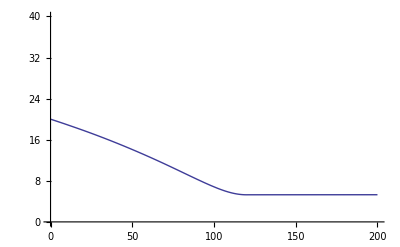

```mathematica
Plot[Re[r1ts2[tau]],{tau,taukax0,200.},PlotRange->{0.,40.}]
```

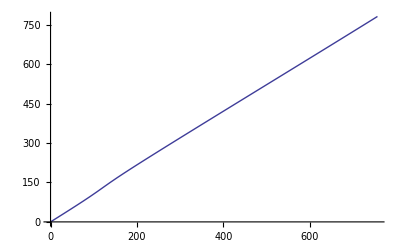

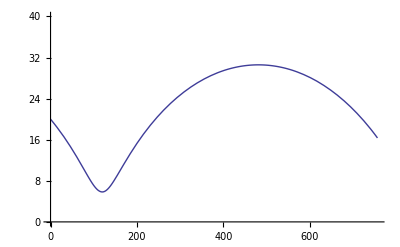

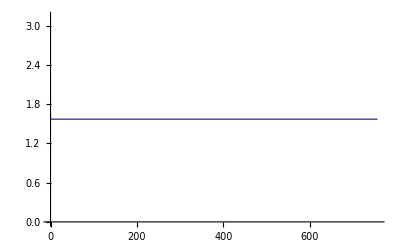

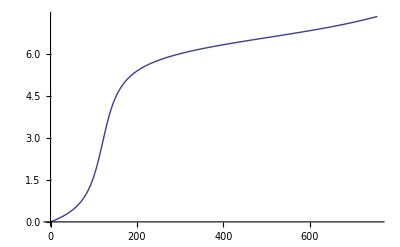

```mathematica
Plot[Re[ttk1[tau]],{tau,taukax0,taukax10}]
Plot[Re[r1tk1[tau]],{tau,taukax0,taukax10},PlotRange->{0.,40.}]
Plot[Re[thtk1[tau]],{tau,taukax0,taukax10}]
Plot[Re[phitk1[tau]],{tau,taukax0,taukax10}]
```

```mathematica
tk1[tau_]={ttk1[tau],r1tk1[tau],thtk1[tau],phitk1[tau]};
```

```mathematica
tk1[tau]>> "WdWcov4ART_tk1.txt";
```

```mathematica
tk1[tau_]=<< "WdWcov4ART_tk1.txt";
```

```mathematica
(*GR bin BH from Kerr r0x0=16.80 μ=0.5 alpha=αo0  pure Pgrav solution bcond ta01  : NDSolve,  
r2-radii: 31.19, 5.26, tauper=746.4
sol={r1tkd1,ttkd1,thtkd1,phitkd1} *)
```

```mathematica
μ0=1/2;
m20=μ0/(1+μ0)
m10=1/(1+μ0)
mr0=m10 m20
r0=30.;
r10=r0*mr0/m10
r20=r0*mr0/m20
ω0=1/Sqrt[2 r0^3]
(* spin omega1 omega2 *)
ω1=0.8;
ω2=0.8;
T0=2 Pi/ω0
ta01=0.;
ta02=2000.;
lcp0=1.1ω0( r10^2 +r20^2)
lc1=lcp0(1+μ0 I)^2
Fc0=(1-1/(2.5r0))
ecp0=(Fc0^2-1)/2
fN=(1+μ0)  (* r0-factor *)
rp0=r0 
(*  default-alpha orbit *)
αo0=(2/3)ω0 r0^2  mr0;
(* imaginary orbit alpha from Pgrav *)
αo0=   (8Pi/(5Fc0 r0)) μ0/((1+μ0)^7 (3+8μ0 I-4μ0^2))
(* real alfa spin from m1 m2 *)
αs0=(2/(3(1+μ0)^2))(ω1+ω2 μ0^2)
αs01=(2/(3(1+μ0)^2))(ω1)
αs02=(2/(3(1+μ0)^2))(ω2 μ0^2)
alpha0=αs0+αo0
```

1/3

2/3

2/9

10.

20.

0.00430331

1460.08

2.36682

1.77512+2.36682 ⅈ

0.986667

-0.0132444

3/2

30.

0.000496946-0.000993892 ⅈ

0.296296

0.237037

0.0592593

0.296793-0.000993892 ⅈ

```mathematica
-N1dAbt
sirpx=Solve[N1dAbt==0 /. rN1dAbt1 /. rN1dAbt2 /. rp[τ]->1/irpx ,irpx]
irp[ϵ_,lcp_]=irpx /. sirpx
rp[ϵ_,lcp_]=1/irp[ϵ,lcp]
```

1-Fc^2+lcp^2/rp[τ]^2-1/rp[τ]+rp'[τ]^2

{{irpx→(1-√(1+8 lcp^2 ϵ))/(2 lcp^2)},{irpx→(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}}

{(1-√(1+8 lcp^2 ϵ))/(2 lcp^2),(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}

{(2 lcp^2)/(1-√(1+8 lcp^2 ϵ)),(2 lcp^2)/(1+√(1+8 lcp^2 ϵ))}

```mathematica
(*  max-min value for r2 and r20 true_r0=r0x *)
rp1=rp[ecp0,lcp0][[1]]
rp2=rp[ecp0,lcp0][[2]]
r0x2=2 rp1*rp2/(rp1+rp2)
r0x0=(1+μ0)r0x2
r0x1=r0x2 μ0
ω0x=1/Sqrt[2 r0x^3]
T0x=N[2 Pi/ω0x]
(* true factors in lcp0, Fc0 *)
flcp0=lcp0/(ω0x( r0x1^2 +r0x2^2))
fFc0=1/((1-Fc0)r0x)
```

30.9099

6.8418

11.2037

16.8056

5.60185

1/(√2 √(r0x^3))

8.88577 √(r0x^3)

0.0213328 √(r0x^3)

75./r0x

```mathematica
tauper=2(tau1p+tau1n+40)
omegap=2 Pi/tauper
```

756.461

0.00830603

```mathematica
ta02=tauper+50;
ta01=0.;
ta02e=ta02;
ta01e=ta01;
```

```mathematica
r1ts1[tau_]=roxsp[tau];
dr1ts1[tau_]=droxsp[tau];
```

```mathematica
Off[NIntegrate::nlim];
```

```mathematica
dtts1[tau_]=ValList[stt][[1]] /.  r1t[tau]-> r1ts1[tau];
```

```mathematica
tts1[tau_]=NIntegrate[dtts1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
dphits1[tau_]=ValList[sphit][[1]] /.  r1t[tau]-> r1ts1[tau];
```

```mathematica
phits1[tau_]=NIntegrate[dphits1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
thts1[tau_]=Pi/2;
dthts1[tau_]=0.;
```

```mathematica
repfAdeq={t->tt[tau],r1->r1t[tau],th->tht[tau]}
```

{t→tt[tau],r1→r1t[tau],th→tht[tau]}

```mathematica
Gijkkat0=Gijkkat /. alpha1-> αo0;
```

```mathematica
tim1=TimeUsed[];
fKdeq1=D[tt[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,1]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq2=D[r1t[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,2]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq3=D[tht[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,3]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq4=D[phit[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,4]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
bctxWv={tts1[ta01],dtts1[ta01],r1ts2[ta01],r1ts2'[ta01],thts1[ta01],dthts1[ta01],phits1[ta01],dphits1[ta01]}
```

InterpolatingFunction::dmval: Input value {3025.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.,1.02733-0.0214027 ⅈ,20.+10. ⅈ,-0.101028-0.0505141 ⅈ,π/2,0.,0.,0.00591706-4.33681×10^-19 ⅈ}

```mathematica
bctxWvx={tts1,dtts1,r1ts1,dr1ts1,thts1,dthts1,phits1,dphits1};
```

```mathematica
bctxW=Table[(bctxWs[[i1]] /. tau->ta01)==bctxWv[[i1]],{i1,1,Length[bctxWs]} ]
```

{tt[0.]==0.,tt'[0.]==1.02733-0.0214027 ⅈ,r1t[0.]==20.+10. ⅈ,r1t'[0.]==-0.101028-0.0505141 ⅈ,tht[0.]==π/2,tht'[0.]==0.,phit[0.]==0.,phit'[0.]==0.00591706-4.33681×10^-19 ⅈ}

```mathematica
fKdeqe={fKdeq1==0,fKdeq2==0,fKdeq3==0,fKdeq4==0};
```

```mathematica
sfKdeq=NDSolve[Join[{fKdeqe,bctxW}],vit,{tau,ta01,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{{tt[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],r1t[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],tht[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],phit[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau]}}

```mathematica
taukax1 =Head[sfKdeq[[1,1,2]]][[1,1,2]]
taukax0 =ta01
taukax10=taukax1-50.;
```

806.461

0.

```mathematica
ttkd1[tau_]= tt[tau] /. sfKdeq[[1]];
r1tkd1[tau_]= r1t[tau] /. sfKdeq[[1]];
thtkd1[tau_]= tht[tau] /. sfKdeq[[1]];
phitkd1[tau_]= phit[tau] /. sfKdeq[[1]];
```

```mathematica
r1tkd1[500.]
r1tk1[500.]
r1tkd1[500.]-r1tk1[500.]
```

30.5162+17.3477 ⅈ

30.5188+17.3478 ⅈ

-0.00266062-0.0000903003 ⅈ

```mathematica
(*  period, max min radiii *)
```

```mathematica
tauds12= τ  /. FindMinimum[Re[r1tkd1[τ]],{τ,130}][[2]]
r1ds11=Re[r1tkd1[tauds12]]
```

119.77

5.83433

```mathematica
tauds11= τ  /. FindMaximum[Re[r1tkd1[τ]],{τ,500}][[2]]
r1ds12=Re[r1tkd1[tauds11]]
```

481.086

30.5776

```mathematica
tauperds=2(-tauds12+tauds11)
```

722.631

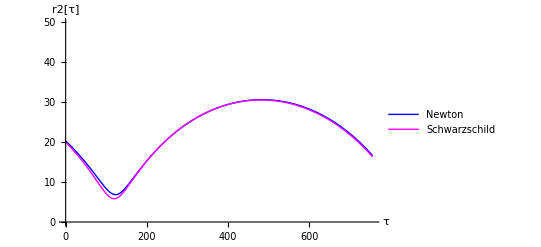

```mathematica
(*  Newton=blue, Schwarzschild=magenta *)
Plot[{roxd1[tau+168]1/(1+μ0),Re[r1tk1[tau]]},{tau,taukax0,taukax10},PlotRange->{0.,50.},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,1]},AxesLabel->{"τ","r2[τ]"},PlotLegends->{"Newton","Schwarzschild"}]
```

InterpolatingFunction::dmval: Input value {-0.0154534} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-253.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-756.446} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

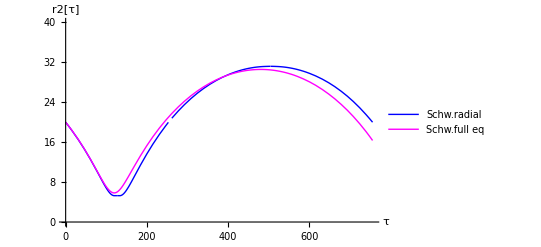

```mathematica
(* Schwarzschild piecewise(radial)=blue, NDSolve(full eq)=magenta *)
Plot[{Re[roxsp[tau+taup0]],Re[r1tk1[tau]]},{tau,taukax0,taukax10},PlotRange->{0.,40.},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,1]},AxesLabel->{"τ","r2[τ]"},PlotLegends->{"Schw.radial","Schw.full eq"}]
```

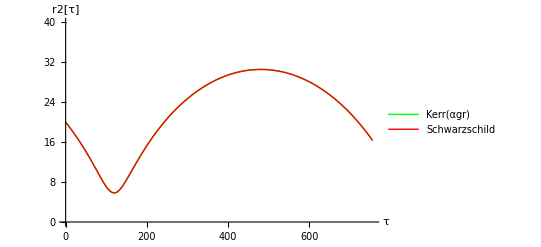

```mathematica
(* Kerr alphagr=green, Schwarzschild=red *)
Plot[{Re[r1tkd1[tau]],Re[r1tk1[tau]]},{tau,taukax0,taukax10},PlotRange->{0.,40.},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0]},AxesLabel->{"τ","r2[τ]"},PlotLegends->{"Kerr(αgr)","Schwarzschild"}]
```

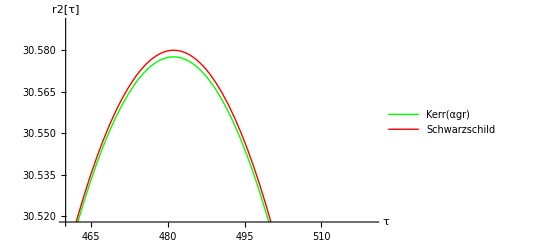

```mathematica
(* Kerr alphagr=green, Schwarzschild=red *)
Plot[{Re[r1tkd1[tau]],Re[r1tk1[tau]]},{tau,460,520},PlotRange->{30.518,30.59},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0]},AxesLabel->{"τ","r2[τ]"},PlotLegends->{"Kerr(αgr)","Schwarzschild"}]
```

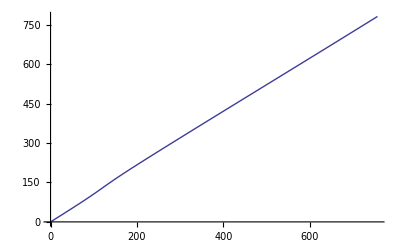

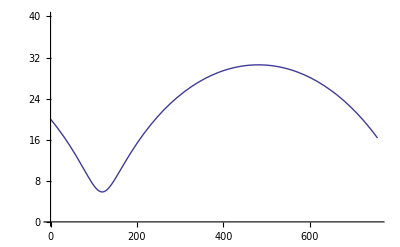

-Graphics-

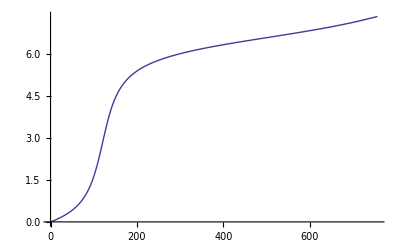

```mathematica
Plot[Re[ttkd1[tau]],{tau,taukax0,taukax10}]
Plot[Re[r1tkd1[tau]],{tau,taukax0,taukax10},PlotRange->{0.,40.}]
Plot[Re[thtkd1[tau]],{tau,taukax0,taukax10}]
Plot[Re[phitkd1[tau]],{tau,taukax0,taukax10}]
```

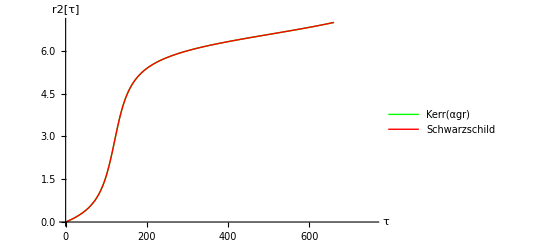

```mathematica
(* Kerr alphagr=green, Schwarzschild=red *)
Plot[{Re[phitkd1[tau]],Re[phitk1[tau]]},{tau,taukax0,taukax10},PlotRange->{0,7.},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0]},AxesLabel->{"τ","r2[τ]"},PlotLegends->{"Kerr(αgr)","Schwarzschild"}]
```

```mathematica
tkd1[tau_]={ttkd1[tau],r1tkd1[tau],thtkd1[tau],phitkd1[tau]};
```

```mathematica
tkd1[tau]>> "WdWcov4ART_tkd1g.txt";
```

```mathematica
tkd1[tau_]=<< "WdWcov4ART_tkd1g.txt";
```

```mathematica
(* GR bin BH with self-rotation,  r0x0=16.80 μ=0.5, alpha=alpha(Pgrav)+alpha(ω1,ω2), {ω1,ω2}=0.8 solution bcond=ta01  : NDSolve,  
r2-radii: 31.7482, 5.99876, tauper=751.954
sol= {r1tke1,ttke1,thtke1,phitke1}   *)
```

```mathematica
μ0=1/2;
m20=μ0/(1+μ0)
m10=1/(1+μ0)
mr0=m10 m20
r0=30.;
r10=r0*mr0/m10
r20=r0*mr0/m20
ω0=1/Sqrt[2 r0^3]
(* spin omega1 omega2 *)
ω1=0.8;
ω2=0.8;
T0=2 Pi/ω0
ta01=0.;
ta02=2000.;
lcp0=1.1ω0( r10^2 +r20^2)
lc1=lcp0(1+μ0 I)^2
Fc0=(1-1/(2.5r0))
ecp0=(Fc0^2-1)/2
fN=(1+μ0)  (* r0-factor *)
rp0=r0 
(*  default-alpha orbit *)
αo0=(2/3)ω0 r0^2  mr0;
(* imaginary orbit alpha from Pgrav *)
αo0=   (8Pi/(5Fc0 r0)) μ0/((1+μ0)^7 (3+8μ0 I-4μ0^2))
(* real alfa spin from m1 m2 *)
αs0=(2/(3(1+μ0)^2))(ω1+ω2 μ0^2)
αs01=(2/(3(1+μ0)^2))(ω1)
αs02=(2/(3(1+μ0)^2))(ω2 μ0^2)
alpha0=αs0+αo0
```

1/3

2/3

2/9

10.

20.

0.00430331

1460.08

2.36682

1.77512+2.36682 ⅈ

0.986667

-0.0132444

3/2

30.

0.000496946-0.000993892 ⅈ

0.296296

0.237037

0.0592593

0.296793-0.000993892 ⅈ

```mathematica
Fc0
lcp0
ecp0=(Fc0^2-1)/2
```

0.986667

2.36682

-0.0132444

```mathematica
-N1dAbt
sirpx=Solve[N1dAbt==0 /. rN1dAbt1 /. rN1dAbt2 /. rp[τ]->1/irpx ,irpx]
irp[ϵ_,lcp_]=irpx /. sirpx
rp[ϵ_,lcp_]=1/irp[ϵ,lcp]
```

1-Fc^2+lcp^2/rp[τ]^2-1/rp[τ]+rp'[τ]^2

{{irpx→(1-√(1+8 lcp^2 ϵ))/(2 lcp^2)},{irpx→(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}}

{(1-√(1+8 lcp^2 ϵ))/(2 lcp^2),(1+√(1+8 lcp^2 ϵ))/(2 lcp^2)}

{(2 lcp^2)/(1-√(1+8 lcp^2 ϵ)),(2 lcp^2)/(1+√(1+8 lcp^2 ϵ))}

```mathematica
rp1=rp[ecp0,lcp0][[1]]
rp2=rp[ecp0,lcp0][[2]]
```

30.9099

6.8418

```mathematica
(*  max-min value for r2 and r20 true_r0=r0x *)
rp1=rp[ecp0,lcp0][[1]]
rp2=rp[ecp0,lcp0][[2]]
r0x2=2 rp1*rp2/(rp1+rp2)
r0x0=(1+μ0)r0x2
r0x1=r0x2 μ0
ω0x=1/Sqrt[2 r0x^3]
T0x=N[2 Pi/ω0x]
(* true factors in lcp0, Fc0 *)
flcp0=lcp0/(ω0x( r0x1^2 +r0x2^2))
fFc0=1/((1-Fc0)r0x)
```

30.9099

6.8418

11.2037

16.8056

5.60185

1/(√2 √(r0x^3))

8.88577 √(r0x^3)

0.0213328 √(r0x^3)

75./r0x

```mathematica
tauper=2(tau1p+tau1n+40)
omegap=2 Pi/tauper
```

756.461

0.00830603

```mathematica
ta02=tauper+50;
ta01=0.;
ta02e=ta02;
ta01e=ta01;
```

```mathematica
r1ts1[tau_]=roxsp[tau];
dr1ts1[tau_]=droxsp[tau];
```

```mathematica
Off[NIntegrate::nlim];
```

```mathematica
dtts1[tau_]=ValList[stt][[1]] /.  r1t[tau]-> r1ts1[tau];
```

```mathematica
tts1[tau_]=NIntegrate[dtts1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
dphits1[tau_]=ValList[sphit][[1]] /.  r1t[tau]-> r1ts1[tau];
```

```mathematica
phits1[tau_]=NIntegrate[dphits1[taux],{taux,ta01,tau},PrecisionGoal->3,AccuracyGoal->3];
```

```mathematica
thts1[tau_]=Pi/2;
dthts1[tau_]=0.;
```

```mathematica
repfAdeq={t->tt[tau],r1->r1t[tau],th->tht[tau]}
```

{t→tt[tau],r1→r1t[tau],th→tht[tau]}

```mathematica
Gijkkat0=Gijkkat /. alpha1-> alpha0;
```

```mathematica
tim1=TimeUsed[];
fKdeq1=D[tt[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,1]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
tim1=TimeUsed[];
fKdeq3=D[tht[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,3]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.016

```mathematica
tim1=TimeUsed[];
fKdeq4=D[phit[tau],{tau,2}]+Sum[(Gijkkat0[[mx,nx,4]] /. repfAdeq)D[vit[[mx]],tau]D[vit[[nx]],tau],{mx,1,4},{nx,1,4}];
tim2=TimeUsed[];
Print[tim2-tim1];
```

0.

```mathematica
bctxWs={tt[tau],tt'[tau],r1t[tau],r1t'[tau],tht[tau],tht'[tau],phit[tau],phit'[tau]}
```

{tt[tau],tt'[tau],r1t[tau],r1t'[tau],tht[tau],tht'[tau],phit[tau],phit'[tau]}

```mathematica
bctxWv={tts1[ta01],dtts1[ta01],r1ts2[ta01],r1ts2'[ta01],thts1[ta01],dthts1[ta01],phits1[ta01],dphits1[ta01]}
```

InterpolatingFunction::dmval: Input value {3025.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.,1.02733-0.0214027 ⅈ,20.+10. ⅈ,-0.101028-0.0505141 ⅈ,π/2,0.,0.,0.00591706-4.33681×10^-19 ⅈ}

```mathematica
bctxWvx={tts1,dtts1,r1ts1,dr1ts1,thts1,dthts1,phits1,dphits1};
```

```mathematica
bctxW=Table[(bctxWs[[i1]] /. tau->ta01)==bctxWv[[i1]],{i1,1,Length[bctxWs]} ]
```

{tt[0.]==0.,tt'[0.]==1.02733-0.0214027 ⅈ,r1t[0.]==20.+10. ⅈ,r1t'[0.]==-0.101028-0.0505141 ⅈ,tht[0.]==π/2,tht'[0.]==0.,phit[0.]==0.,phit'[0.]==0.00591706-4.33681×10^-19 ⅈ}

```mathematica
fKdeqe={fKdeq1==0,fKdeq2==0,fKdeq3==0,fKdeq4==0};
```

```mathematica
sfKdeq=NDSolve[Join[{fKdeqe,bctxW}],vit,{tau,ta01,ta02},PrecisionGoal->3,AccuracyGoal->3]
```

{{tt[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],r1t[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],tht[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau],phit[tau]→InterpolatingFunction[{{0.,806.461}},<>][tau]}}

```mathematica
taukax1 =Head[sfKdeq[[1,1,2]]][[1,1,2]]
taukax0 =ta01
taukax10=taukax1-50.;
```

806.461

0.

```mathematica
ttke1[tau_]= tt[tau] /. sfKdeq[[1]];
r1tke1[tau_]= r1t[tau] /. sfKdeq[[1]];
thtke1[tau_]= tht[tau] /. sfKdeq[[1]];
phitke1[tau_]= phit[tau] /. sfKdeq[[1]];
```

```mathematica
(* dr1max *)
r1tke1[500.]
r1tk1[500.]
dr1max=r1tke1[500.]-r1tk1[500.]
```

31.7444+16.1702 ⅈ

30.5188+17.3478 ⅈ

1.22552-1.17764 ⅈ

```mathematica
(* period *)
tauper
taupers1={r1ts1[0.],r1ts1[738]}
tauperk1={r1tk1[0.],r1tk1[710]}
taupere1={r1tke1[0.],r1tke1[761]}
dtaupere1=761-710
```

756.461

InterpolatingFunction::dmval: Input value {3025.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2772.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{20.+10. ⅈ,18.0009+9.00045 ⅈ}

{20.+10. ⅈ,21.0627+17.677 ⅈ}

{20.+10. ⅈ,19.0656+13.1121 ⅈ}

51

```mathematica
(*  period, max min radiii *)
```

```mathematica
tauds12= τ  /. FindMinimum[Re[r1tke1[τ]],{τ,130}][[2]]
r1ds11=Re[r1tke1[tauds12]]
```

119.155

5.99876

```mathematica
tauds11= τ  /. FindMaximum[Re[r1tke1[τ]],{τ,500}][[2]]
r1ds12=Re[r1tke1[tauds11]]
```

495.132

31.7482

```mathematica
tauperds=2(-tauds12+tauds11)
```

751.954

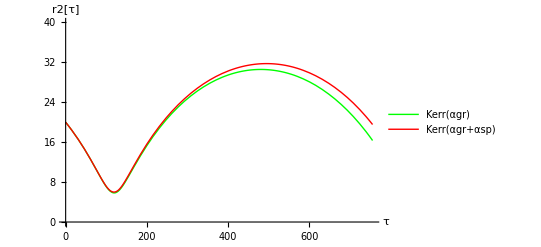

```mathematica
(* Kerr alphagr=green, Schwarzschild=red *)
Plot[{Re[r1tkd1[tau]],Re[r1tke1[tau]]},{tau,taukax0,taukax10},PlotRange->{0.,40.},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0]},AxesLabel->{"τ","r2[τ]"},PlotLegends->{"Kerr(αgr)","Kerr(αgr+αsp)"}]
```

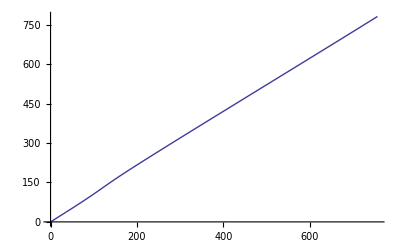

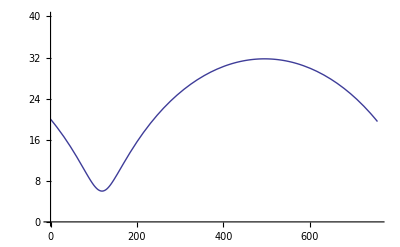

-Graphics-

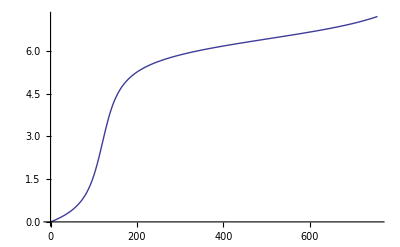

```mathematica
Plot[Re[ttke1[tau]],{tau,taukax0,taukax10}]
Plot[Re[r1tke1[tau]],{tau,taukax0,taukax10},PlotRange->{0.,40.}]
Plot[Re[thtke1[tau]],{tau,taukax0,taukax10}]
Plot[Re[phitke1[tau]],{tau,taukax0,taukax10}]
```

```mathematica
tke1[tau_]={ttke1[tau],r1tke1[tau],thtke1[tau],phitke1[tau]};
```

```mathematica
tke1[tau]>> "WdWcov4ART_tke1.txt";
```

```mathematica
tke1[tau_]=<< "WdWcov4ART_tke1.txt";
```